# The radial part of the source R[S_r_r^(1,1)]_lmω(r)

## Description

This is one of four Mathematica notebooks created by Lukáš Polcar that form the supplemental material to the 2025 paper “Towards relativistic inspirals into black holes surrounded by matter” by Lukáš Polcar and Vojtěch Witzany.
This notebook takes as input the results from the other  notebooks and evaluates the modified effective source localized on the matter shell in Schwarzschild coordinates. In particular, it solves the (1,1) equations for the ring, which contributes to the total source.  This part corresponds to Section IV of the paper.
Some lines and sections  are commented out or are set as not evaluatable for a quick evaluation of the entire notebook.

## Preparations and Tests

## Initial preparations and definitions

### Packages

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[1,0,0]];
IndexForm[LI[x_,2]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$CVVerbose=False;
```

```mathematica
<<xAct`TexAct`
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### Manifold and Metric

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,m,l,j,n,s}];
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

```mathematica
DefMetric[{3,1,0},g[-a,-b],CD,SymbolOfCovD->{"|","𝔇"}];
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

### NP Formalism Basis, tetrad vectors, and Derivative operators

```mathematica
DefBasis[NP,TangentM4,{1,2,3,4},BasisColor->RGBColor[0,0,1]];
```

** DefBasis: Defining basis NP.

** DefCovD: Defining parallel derivative PDNP[-a].

** DefTensor: Defining torsion tensor TorsionPDNP[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDNP[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDNP[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDNP[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpNP[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownNP[-a,-b,-c,-d].

#### Tetrad vectors

```mathematica
DefTensor[lNP[a],M4,PrintAs->"l"]
```

** DefTensor: Defining tensor lNP[a].

```mathematica
DefTensor[nNP[a],M4,PrintAs->"n"]
```

** DefTensor: Defining tensor nNP[a].

```mathematica
DefTensor[mNP[a],M4,Dagger->Complex,PrintAs->"m"]
```

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

** DefTensor: Defining tensor mNP†[-a].

```mathematica
PrintAs@mNP†^="m̄";
```

A bar notation denotes a complex conjugate

#### Tetrad Directional Derivatives

```mathematica
SetDaggerMatrix[NP,{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}]
```

```mathematica
xTensorFormStop[];
```

```mathematica
FormatBasis[PDNP[{1,-NP}],"D"];
```

```mathematica
FormatBasis[PDNP[{2,-NP}],"Δ"];
```

```mathematica
FormatBasis[PDNP[{3,-NP}],"δ"];
```

```mathematica
FormatBasis[PDNP[{4,-NP}],"δ̄"];
```

```mathematica
xTensorFormStart[];
```

#### Tetrad Contravariant Vector component values

```mathematica
{lNP[a]==Basis[a,{1,-NP}],nNP[a]==Basis[a,{2,-NP}],mNP[a]==Basis[a,{3,-NP}],mNP†[a]==Basis[a,{4,-NP}]}
```

{l | a
 ==e |   | a
1 |  ,n | a
 ==e |   | a
2 |  ,m | a
 ==e |   | a
3 |  ,m̄ | a
 ==e |   | a
4 |  }

```mathematica
Map[ToBasis[NP],%,{2}]
```

** DefTensor: Defining weight +2 density DetgNP[]. Determinant.

{l | a
 ==e |   | a
1 |  ,n | a
 ==e |   | a
2 |  ,m | a
 ==e |   | a
3 |  ,m̄ | a
 ==e |   | a
4 |  }

```mathematica
Flatten@ComponentArray@%
```

{l | 1
 ==1,l | 2
 ==0,l | 3
 ==0,l | 4
 ==0,n | 1
 ==0,n | 2
 ==1,n | 3
 ==0,n | 4
 ==0,m | 1
 ==0,m | 2
 ==0,m | 3
 ==1,m | 4
 ==0,m̄ | 1
 ==0,m̄ | 2
 ==0,m̄ | 3
 ==0,m̄ | 4
 ==1}

```mathematica
%/.Equal->ComponentValue;
```

#### Metric in NP tetrad form (positive metric signature)

```mathematica
g[a,b]==-(lNP[a]nNP[b]+lNP[b]nNP[a])+(mNP[a]mNP†[b]+mNP[b]mNP†[a])
```

g | a | b
  |  ==m | b
  m̄ | a
 +m | a
  m̄ | b
 -l | b
  n | a
 -l | a
  n | b

```mathematica
ToBasis[NP]/@%
```

g | a | b
  |  ==m | b
  m̄ | a
 +m | a
  m̄ | b
 -l | b
  n | a
 -l | a
  n | b

```mathematica
ToValues@ComponentArray@%
```

{{g | 1 | 1
  |  ==0,g | 1 | 2
  |  ==-1,g | 1 | 3
  |  ==0,g | 1 | 4
  |  ==0},{g | 2 | 1
  |  ==-1,g | 2 | 2
  |  ==0,g | 2 | 3
  |  ==0,g | 2 | 4
  |  ==0},{g | 3 | 1
  |  ==0,g | 3 | 2
  |  ==0,g | 3 | 3
  |  ==0,g | 3 | 4
  |  ==1},{g | 4 | 1
  |  ==0,g | 4 | 2
  |  ==0,g | 4 | 3
  |  ==1,g | 4 | 4
  |  ==0}}

```mathematica
%/.Equal->ComponentValue
```

{{g | 1 | 1
  |  →0,g | 1 | 2
  |  →-1,g | 1 | 3
  |  →0,g | 1 | 4
  |  →0},{g | 2 | 1
  |  →-1,g | 2 | 2
  |  →0,g | 2 | 3
  |  →0,g | 2 | 4
  |  →0},{g | 3 | 1
  |  →0,g | 3 | 2
  |  →0,g | 3 | 3
  |  →0,g | 3 | 4
  |  →1},{g | 4 | 1
  |  →0,g | 4 | 2
  |  →0,g | 4 | 3
  |  →1,g | 4 | 4
  |  →0}}

```mathematica
MatrixForm@ToValues@TableOfComponents[g[a,b],NP]
```

(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
MatrixForm@Inverse@%
```

(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
MetricInBasis[g,-NP,%]
```

{{g |   |  
1 | 1→0,g |   |  
1 | 2→-1,g |   |  
1 | 3→0,g |   |  
1 | 4→0},{g |   |  
2 | 1→-1,g |   |  
2 | 2→0,g |   |  
2 | 3→0,g |   |  
2 | 4→0},{g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→0,g |   |  
3 | 4→1},{g |   |  
4 | 1→0,g |   |  
4 | 2→0,g |   |  
4 | 3→1,g |   |  
4 | 4→0}}

```mathematica
RuleToSet@g
```

#### Relating contravariant tetrad vector and covariant Tetrad vectors component values

```mathematica
{lNP[-a]==g[-a,-b]lNP[b],nNP[-a]==g[-a,-b]nNP[b],mNP[-a]==g[-a,-b]mNP[b],mNP†[-a]==g[-a,-b]mNP†[b]}
```

{l |  
a==g |   |  
a | b l | b
 ,n |  
a==g |   |  
a | b n | b
 ,m |  
a==g |   |  
a | b m | b
 ,m̄ |  
a==g |   |  
a | b m̄ | b
 }

```mathematica
Map[ToBasis[NP],%,{2}]
```

{l |  
a==g |   |  
a | b l | b
 ,n |  
a==g |   |  
a | b n | b
 ,m |  
a==g |   |  
a | b m | b
 ,m̄ |  
a==g |   |  
a | b m̄ | b
 }

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l |  
a==g |   |  
a | 1 l | 1
 +g |   |  
a | 2 l | 2
 +g |   |  
a | 3 l | 3
 +g |   |  
a | 4 l | 4
 ,n |  
a==g |   |  
a | 1 n | 1
 +g |   |  
a | 2 n | 2
 +g |   |  
a | 3 n | 3
 +g |   |  
a | 4 n | 4
 ,m |  
a==g |   |  
a | 1 m | 1
 +g |   |  
a | 2 m | 2
 +g |   |  
a | 3 m | 3
 +g |   |  
a | 4 m | 4
 ,m̄ |  
a==g |   |  
a | 1 m̄ | 1
 +g |   |  
a | 2 m̄ | 2
 +g |   |  
a | 3 m̄ | 3
 +g |   |  
a | 4 m̄ | 4
 }

```mathematica
ToValues@Flatten@ComponentArray@%
```

{l |  
1==0,l |  
2==-1,l |  
3==0,l |  
4==0,n |  
1==-1,n |  
2==0,n |  
3==0,n |  
4==0,m |  
1==0,m |  
2==0,m |  
3==0,m |  
4==1,m̄ |  
1==0,m̄ |  
2==0,m̄ |  
3==1,m̄ |  
4==0}

```mathematica
%/.Equal->ComponentValue;
```

```mathematica
RuleToSet/@{lNP,nNP,mNP,mNP†};
```

```mathematica
{lNP[a]==SeparateBasis[NP]@lNP[a],nNP[a]==SeparateBasis[NP]@nNP[a],mNP[a]==SeparateBasis[NP]@mNP[a],mNP†[a]==SeparateBasis[NP]@mNP†[a]}
```

{l | a
 ==e |   | a
b |   l | b
 ,n | a
 ==e |   | a
b |   n | b
 ,m | a
 ==e |   | a
b |   m | b
 ,m̄ | a
 ==e |   | a
b |   m̄ | b
 }

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l | a
 ==e |   | a
1 |  ,n | a
 ==e |   | a
2 |  ,m | a
 ==e |   | a
3 |  ,m̄ | a
 ==e |   | a
4 |  }

```mathematica
Solve[%,Cases[%,Basis[{__},a_],Infinity]]//Flatten
```

{e |   | a
1 |  →l | a
 ,e |   | a
2 |  →n | a
 ,e |   | a
3 |  →m | a
 ,e |   | a
4 |  →m̄ | a
 }

```mathematica
%/.HoldPattern@Rule[X_,Y_]:>MakeRule[{X,Y}]//Flatten//Union
```

{HoldPattern[e |   | UnderBar[a̲]
1 |  ]:>Module[{},l | a
 ],HoldPattern[e |   | UnderBar[a̲]
2 |  ]:>Module[{},n | a
 ],HoldPattern[e |   | UnderBar[a̲]
3 |  ]:>Module[{},m | a
 ],HoldPattern[e |   | UnderBar[a̲]
4 |  ]:>Module[{},m̄ | a
 ]}

```mathematica
BasisToVectors=%;
```

```mathematica
{lNP[-a]==SeparateBasis[NP]@lNP[-a],nNP[-a]==SeparateBasis[NP]@nNP[-a],mNP[-a]==SeparateBasis[NP]@mNP[-a],mNP†[-a]==SeparateBasis[NP]@mNP†[-a]}
```

{l |  
a==e |   | b
a |   l |  
b,n |  
a==e |   | b
a |   n |  
b,m |  
a==e |   | b
a |   m |  
b,m̄ |  
a==e |   | b
a |   m̄ |  
b}

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l |  
a==-e |   | 2
a |  ,n |  
a==-e |   | 1
a |  ,m |  
a==e |   | 4
a |  ,m̄ |  
a==e |   | 3
a |  }

```mathematica
Solve[%,Cases[%,Basis[__],Infinity]]//Flatten
```

{e |   | 2
a |  →-l |  
a,e |   | 1
a |  →-n |  
a,e |   | 4
a |  →m |  
a,e |   | 3
a |  →m̄ |  
a}

```mathematica
%/.HoldPattern@Rule[X_,Y_]:>MakeRule[{X,Y}]//Flatten//Union
```

{HoldPattern[e | UnderBar[a̲] | 1
  |  ]:>Module[{},-n | a
 ],HoldPattern[e | UnderBar[a̲] | 2
  |  ]:>Module[{},-l | a
 ],HoldPattern[e | UnderBar[a̲] | 3
  |  ]:>Module[{},m̄ | a
 ],HoldPattern[e | UnderBar[a̲] | 4
  |  ]:>Module[{},m | a
 ]}

```mathematica
AppendTo[BasisToVectors,%]
```

{HoldPattern[e |   | UnderBar[a̲]
1 |  ]:>Module[{},l | a
 ],HoldPattern[e |   | UnderBar[a̲]
2 |  ]:>Module[{},n | a
 ],HoldPattern[e |   | UnderBar[a̲]
3 |  ]:>Module[{},m | a
 ],HoldPattern[e |   | UnderBar[a̲]
4 |  ]:>Module[{},m̄ | a
 ],{HoldPattern[e | UnderBar[a̲] | 1
  |  ]:>Module[{},-n | a
 ],HoldPattern[e | UnderBar[a̲] | 2
  |  ]:>Module[{},-l | a
 ],HoldPattern[e | UnderBar[a̲] | 3
  |  ]:>Module[{},m̄ | a
 ],HoldPattern[e | UnderBar[a̲] | 4
  |  ]:>Module[{},m | a
 ]}}

### Second basis and chart

```mathematica
DefScalarFunction/@{l1,l2,l4,n1,n2,n4,m1,m3,m4,m1dag,m3dag,m4dag,arot};
```

** DefScalarFunction: Defining scalar function l1.

** DefScalarFunction: Defining scalar function l2.

** DefScalarFunction: Defining scalar function l4.

** DefScalarFunction: Defining scalar function n1.

** DefScalarFunction: Defining scalar function n2.

** DefScalarFunction: Defining scalar function n4.

** DefScalarFunction: Defining scalar function m1.

** DefScalarFunction: Defining scalar function m3.

** DefScalarFunction: Defining scalar function m4.

** DefScalarFunction: Defining scalar function m1dag.

** DefScalarFunction: Defining scalar function m3dag.

** DefScalarFunction: Defining scalar function m4dag.

** DefScalarFunction: Defining scalar function arot.

```mathematica
DefChart[BL,M4,{1,2,3,4},{t[],r[],θ[],ϕ[]},FormatBasis->{"Partials","Differentials"},ChartColor->Green]
```

** DefChart: Defining chart BL.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping BL.

** DefMapping: Defining inverse mapping iBL.

** DefTensor: Defining mapping differential tensor diBL[-a,iBLa].

** DefTensor: Defining mapping differential tensor dBL[-a,BLa].

** DefBasis: Defining basis BL. Coordinated basis.

** DefCovD: Defining parallel derivative PDBL[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDBL[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDBL[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDBL[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDBL[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpBL[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownBL[-a,-b,-c,-d].

```mathematica
DefScalarFunction/@{gtt,grr,gthth,gtph};
```

** DefScalarFunction: Defining scalar function gtt.

** DefScalarFunction: Defining scalar function grr.

** DefScalarFunction: Defining scalar function gthth.

** DefScalarFunction: Defining scalar function gtph.

```mathematica
metricmatrix={{gtt[r[]],0,0,0},{0,grr[r[]],0,0},{0,0,gthth[r[]],0},{0,0,0,gthth[r[]]*Sin[θ[]]^2}}
```

{{gtt[r],0,0,0},{0,grr[r],0,0},{0,0,gthth[r],0},{0,0,0,gthth[r] Sin[θ]^2}}

```mathematica
MetricInBasis[g,-BL,%]
```

{{g |   |  
1 | 1→gtt[r],g |   |  
1 | 2→0,g |   |  
1 | 3→0,g |   |  
1 | 4→0},{g |   |  
2 | 1→0,g |   |  
2 | 2→grr[r],g |   |  
2 | 3→0,g |   |  
2 | 4→0},{g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→gthth[r],g |   |  
3 | 4→0},{g |   |  
4 | 1→0,g |   |  
4 | 2→0,g |   |  
4 | 3→0,g |   |  
4 | 4→gthth[r] Sin[θ]^2}}

```mathematica
ComponentValue[ComponentArray[lNP[{a,BL}]],{l1[r[]],l2[r[]],0,l4[r[]]}]
ComponentValue[ComponentArray[nNP[{a,BL}]],{n1[r[]],n2[r[]],0,n4[r[]]}]
ComponentValue[ComponentArray[mNP[{a,BL}]],{m1[r[], θ[]] ,0,m3[r[], θ[]] ,m4[r[], θ[]] }]
ComponentValue[ComponentArray[mNP†[{a,BL}]],{m1dag[r[], θ[]] ,0,m3dag[r[], θ[]] ,m4dag[r[], θ[]] }]
```

{l | 1
 →l1[r],l | 2
 →l2[r],l | 3
 →0,l | 4
 →l4[r]}

{n | 1
 →n1[r],n | 2
 →n2[r],n | 3
 →0,n | 4
 →n4[r]}

{m | 1
 →m1[r,θ],m | 2
 →0,m | 3
 →m3[r,θ],m | 4
 →m4[r,θ]}

{m̄ | 1
 →m1dag[r,θ],m̄ | 2
 →0,m̄ | 3
 →m3dag[r,θ],m̄ | 4
 →m4dag[r,θ]}

```mathematica
MetricInBasis[g,BL,Inverse[metricmatrix]]
```

{{g | 1 | 1
  |  →1/gtt[r],g | 1 | 2
  |  →0,g | 1 | 3
  |  →0,g | 1 | 4
  |  →0},{g | 2 | 1
  |  →0,g | 2 | 2
  |  →1/grr[r],g | 2 | 3
  |  →0,g | 2 | 4
  |  →0},{g | 3 | 1
  |  →0,g | 3 | 2
  |  →0,g | 3 | 3
  |  →1/gthth[r],g | 3 | 4
  |  →0},{g | 4 | 1
  |  →0,g | 4 | 2
  |  →0,g | 4 | 3
  |  →0,g | 4 | 4
  |  →Csc[θ]^2/gthth[r]}}

```mathematica
{lNP[-a]==g[-a,-b]lNP[b],nNP[-a]==g[-a,-b]nNP[b],mNP[-a]==g[-a,-b]mNP[b],mNP†[-a]==g[-a,-b]mNP†[b]}
```

{l |  
a==g |   |  
a | b l | b
 ,n |  
a==g |   |  
a | b n | b
 ,m |  
a==g |   |  
a | b m | b
 ,m̄ |  
a==g |   |  
a | b m̄ | b
 }

```mathematica
Map[ToBasis[BL],%,{2}]
```

** DefTensor: Defining weight +2 density DetgBL[]. Determinant.

{l |  
a==g |   |  
a | b l | b
 ,n |  
a==g |   |  
a | b n | b
 ,m |  
a==g |   |  
a | b m | b
 ,m̄ |  
a==g |   |  
a | b m̄ | b
 }

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l |  
a==g |   |  
a | 1 l | 1
 +g |   |  
a | 2 l | 2
 +g |   |  
a | 3 l | 3
 +g |   |  
a | 4 l | 4
 ,n |  
a==g |   |  
a | 1 n | 1
 +g |   |  
a | 2 n | 2
 +g |   |  
a | 3 n | 3
 +g |   |  
a | 4 n | 4
 ,m |  
a==g |   |  
a | 1 m | 1
 +g |   |  
a | 2 m | 2
 +g |   |  
a | 3 m | 3
 +g |   |  
a | 4 m | 4
 ,m̄ |  
a==g |   |  
a | 1 m̄ | 1
 +g |   |  
a | 2 m̄ | 2
 +g |   |  
a | 3 m̄ | 3
 +g |   |  
a | 4 m̄ | 4
 }

```mathematica
ToValues@Flatten@ComponentArray@%
```

{l |  
1==gtt[r] l1[r],l |  
2==grr[r] l2[r],l |  
3==0,l |  
4==gthth[r] l4[r] Sin[θ]^2,n |  
1==gtt[r] n1[r],n |  
2==grr[r] n2[r],n |  
3==0,n |  
4==gthth[r] n4[r] Sin[θ]^2,m |  
1==gtt[r] m1[r,θ],m |  
2==0,m |  
3==gthth[r] m3[r,θ],m |  
4==gthth[r] m4[r,θ] Sin[θ]^2,m̄ |  
1==gtt[r] m1dag[r,θ],m̄ |  
2==0,m̄ |  
3==gthth[r] m3dag[r,θ],m̄ |  
4==gthth[r] m4dag[r,θ] Sin[θ]^2}

```mathematica
%/.Equal->ComponentValue;
```

```mathematica
{Basis[{1,-NP},{a,BL}]->lNP[{a,BL}],Basis[{2,-NP},{a,BL}]->nNP[{a,BL}],Basis[{3,-NP},{a,BL}]->mNP[{a,BL}],Basis[{4,-NP},{a,BL}]->mNP†[{a,BL}]}
```

{e |   | a
1 |  →l | a
 ,e |   | a
2 |  →n | a
 ,e |   | a
3 |  →m | a
 ,e |   | a
4 |  →m̄ | a
 }

```mathematica
%//ComponentArray
```

{{dt |  
1→l | 1
 ,dr |  
1→l | 2
 ,dθ |  
1→l | 3
 ,dϕ |  
1→l | 4
 },{dt |  
2→n | 1
 ,dr |  
2→n | 2
 ,dθ |  
2→n | 3
 ,dϕ |  
2→n | 4
 },{dt |  
3→m | 1
 ,dr |  
3→m | 2
 ,dθ |  
3→m | 3
 ,dϕ |  
3→m | 4
 },{dt |  
4→m̄ | 1
 ,dr |  
4→m̄ | 2
 ,dθ |  
4→m̄ | 3
 ,dϕ |  
4→m̄ | 4
 }}

```mathematica
%/.Rule->ComponentValue
```

{{dt |  
1→l | 1
 ,dr |  
1→l | 2
 ,dθ |  
1→l | 3
 ,dϕ |  
1→l | 4
 },{dt |  
2→n | 1
 ,dr |  
2→n | 2
 ,dθ |  
2→n | 3
 ,dϕ |  
2→n | 4
 },{dt |  
3→m | 1
 ,dr |  
3→m | 2
 ,dθ |  
3→m | 3
 ,dϕ |  
3→m | 4
 },{dt |  
4→m̄ | 1
 ,dr |  
4→m̄ | 2
 ,dθ |  
4→m̄ | 3
 ,dϕ |  
4→m̄ | 4
 }}

```mathematica
Basis[{a,NP},{-b,-BL}]==g[{a,NP},{c,NP}]g[{-b,-BL},{-d,-BL}]Basis[{-c,-NP},{d,BL}]//ComponentArray//Flatten
```

{∂/(∂t) | 1
 ==e |   | d
c |   g |   |  
1 | d g | 1 | c
  |  ,∂/(∂r) | 1
 ==e |   | d
c |   g | 1 | c
  |   g |   |  
2 | d,∂/(∂θ) | 1
 ==e |   | d
c |   g | 1 | c
  |   g |   |  
3 | d,∂/(∂ϕ) | 1
 ==e |   | d
c |   g | 1 | c
  |   g |   |  
4 | d,∂/(∂t) | 2
 ==e |   | d
c |   g |   |  
1 | d g | 2 | c
  |  ,∂/(∂r) | 2
 ==e |   | d
c |   g |   |  
2 | d g | 2 | c
  |  ,∂/(∂θ) | 2
 ==e |   | d
c |   g | 2 | c
  |   g |   |  
3 | d,∂/(∂ϕ) | 2
 ==e |   | d
c |   g | 2 | c
  |   g |   |  
4 | d,∂/(∂t) | 3
 ==e |   | d
c |   g |   |  
1 | d g | 3 | c
  |  ,∂/(∂r) | 3
 ==e |   | d
c |   g |   |  
2 | d g | 3 | c
  |  ,∂/(∂θ) | 3
 ==e |   | d
c |   g |   |  
3 | d g | 3 | c
  |  ,∂/(∂ϕ) | 3
 ==e |   | d
c |   g | 3 | c
  |   g |   |  
4 | d,∂/(∂t) | 4
 ==e |   | d
c |   g |   |  
1 | d g | 4 | c
  |  ,∂/(∂r) | 4
 ==e |   | d
c |   g |   |  
2 | d g | 4 | c
  |  ,∂/(∂θ) | 4
 ==e |   | d
c |   g |   |  
3 | d g | 4 | c
  |  ,∂/(∂ϕ) | 4
 ==e |   | d
c |   g |   |  
4 | d g | 4 | c
  |  }

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{∂/(∂t) | 1
 ==-dt |  
2 g |   |  
1 | 1-dr |  
2 g |   |  
1 | 2-dθ |  
2 g |   |  
1 | 3-dϕ |  
2 g |   |  
1 | 4,∂/(∂r) | 1
 ==-dt |  
2 g |   |  
2 | 1-dr |  
2 g |   |  
2 | 2-dθ |  
2 g |   |  
2 | 3-dϕ |  
2 g |   |  
2 | 4,∂/(∂θ) | 1
 ==-dt |  
2 g |   |  
3 | 1-dr |  
2 g |   |  
3 | 2-dθ |  
2 g |   |  
3 | 3-dϕ |  
2 g |   |  
3 | 4,∂/(∂ϕ) | 1
 ==-dt |  
2 g |   |  
4 | 1-dr |  
2 g |   |  
4 | 2-dθ |  
2 g |   |  
4 | 3-dϕ |  
2 g |   |  
4 | 4,∂/(∂t) | 2
 ==-dt |  
1 g |   |  
1 | 1-dr |  
1 g |   |  
1 | 2-dθ |  
1 g |   |  
1 | 3-dϕ |  
1 g |   |  
1 | 4,∂/(∂r) | 2
 ==-dt |  
1 g |   |  
2 | 1-dr |  
1 g |   |  
2 | 2-dθ |  
1 g |   |  
2 | 3-dϕ |  
1 g |   |  
2 | 4,∂/(∂θ) | 2
 ==-dt |  
1 g |   |  
3 | 1-dr |  
1 g |   |  
3 | 2-dθ |  
1 g |   |  
3 | 3-dϕ |  
1 g |   |  
3 | 4,∂/(∂ϕ) | 2
 ==-dt |  
1 g |   |  
4 | 1-dr |  
1 g |   |  
4 | 2-dθ |  
1 g |   |  
4 | 3-dϕ |  
1 g |   |  
4 | 4,∂/(∂t) | 3
 ==dt |  
4 g |   |  
1 | 1+dr |  
4 g |   |  
1 | 2+dθ |  
4 g |   |  
1 | 3+dϕ |  
4 g |   |  
1 | 4,∂/(∂r) | 3
 ==dt |  
4 g |   |  
2 | 1+dr |  
4 g |   |  
2 | 2+dθ |  
4 g |   |  
2 | 3+dϕ |  
4 g |   |  
2 | 4,∂/(∂θ) | 3
 ==dt |  
4 g |   |  
3 | 1+dr |  
4 g |   |  
3 | 2+dθ |  
4 g |   |  
3 | 3+dϕ |  
4 g |   |  
3 | 4,∂/(∂ϕ) | 3
 ==dt |  
4 g |   |  
4 | 1+dr |  
4 g |   |  
4 | 2+dθ |  
4 g |   |  
4 | 3+dϕ |  
4 g |   |  
4 | 4,∂/(∂t) | 4
 ==dt |  
3 g |   |  
1 | 1+dr |  
3 g |   |  
1 | 2+dθ |  
3 g |   |  
1 | 3+dϕ |  
3 g |   |  
1 | 4,∂/(∂r) | 4
 ==dt |  
3 g |   |  
2 | 1+dr |  
3 g |   |  
2 | 2+dθ |  
3 g |   |  
2 | 3+dϕ |  
3 g |   |  
2 | 4,∂/(∂θ) | 4
 ==dt |  
3 g |   |  
3 | 1+dr |  
3 g |   |  
3 | 2+dθ |  
3 g |   |  
3 | 3+dϕ |  
3 g |   |  
3 | 4,∂/(∂ϕ) | 4
 ==dt |  
3 g |   |  
4 | 1+dr |  
3 g |   |  
4 | 2+dθ |  
3 g |   |  
4 | 3+dϕ |  
3 g |   |  
4 | 4}

```mathematica
%//ToValues//ToValues
```

{∂/(∂t) | 1
 ==-gtt[r] n1[r],∂/(∂r) | 1
 ==-grr[r] n2[r],∂/(∂θ) | 1
 ==0,∂/(∂ϕ) | 1
 ==-gthth[r] n4[r] Sin[θ]^2,∂/(∂t) | 2
 ==-gtt[r] l1[r],∂/(∂r) | 2
 ==-grr[r] l2[r],∂/(∂θ) | 2
 ==0,∂/(∂ϕ) | 2
 ==-gthth[r] l4[r] Sin[θ]^2,∂/(∂t) | 3
 ==gtt[r] m1dag[r,θ],∂/(∂r) | 3
 ==0,∂/(∂θ) | 3
 ==gthth[r] m3dag[r,θ],∂/(∂ϕ) | 3
 ==gthth[r] m4dag[r,θ] Sin[θ]^2,∂/(∂t) | 4
 ==gtt[r] m1[r,θ],∂/(∂r) | 4
 ==0,∂/(∂θ) | 4
 ==gthth[r] m3[r,θ],∂/(∂ϕ) | 4
 ==gthth[r] m4[r,θ] Sin[θ]^2}

```mathematica
%/.Equal->ComponentValue
```

{∂/(∂t) | 1
 →-gtt[r] n1[r],∂/(∂r) | 1
 →-grr[r] n2[r],∂/(∂θ) | 1
 →0,∂/(∂ϕ) | 1
 →-gthth[r] n4[r] Sin[θ]^2,∂/(∂t) | 2
 →-gtt[r] l1[r],∂/(∂r) | 2
 →-grr[r] l2[r],∂/(∂θ) | 2
 →0,∂/(∂ϕ) | 2
 →-gthth[r] l4[r] Sin[θ]^2,∂/(∂t) | 3
 →gtt[r] m1dag[r,θ],∂/(∂r) | 3
 →0,∂/(∂θ) | 3
 →gthth[r] m3dag[r,θ],∂/(∂ϕ) | 3
 →gthth[r] m4dag[r,θ] Sin[θ]^2,∂/(∂t) | 4
 →gtt[r] m1[r,θ],∂/(∂r) | 4
 →0,∂/(∂θ) | 4
 →gthth[r] m3[r,θ],∂/(∂ϕ) | 4
 →gthth[r] m4[r,θ] Sin[θ]^2}

```mathematica
RuleToSet/@{lNP,nNP,mNP,mNP†}//Quiet;
RuleToSet@g//Quiet
```

```mathematica
RuleToSet@Basis//Quiet
```

### Christoffel symbols

```mathematica
g[{-a,-BL},{-b,-BL}]Basis[-c,{a,BL}]Basis[-d,{b,BL}]//TraceBasisDummy
```

dr |  
c dr |  
d grr[r]+dθ |  
c dθ |  
d gthth[r]+dt |  
c dt |  
d gtt[r]+dϕ |  
c dϕ |  
d gthth[r] Sin[θ]^2

```mathematica
metric[-c_,-d_]=%/.TensorValues[g]
```

dr |  
c dr |  
d grr[r]+dθ |  
c dθ |  
d gthth[r]+dt |  
c dt |  
d gtt[r]+dϕ |  
c dϕ |  
d gthth[r] Sin[θ]^2

```mathematica
AllComponentValues[Christoffel[CD,PDBL][{a,BL},{-b,-BL},{-c,-BL}]]
```

** DefTensor: Defining tensor ChristoffelCDPDBL[a,-b,-c].

FoldedRule[{Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 2→Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 2→Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 3→Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 1→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 1→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2→Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 1→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2→Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 3→Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 1→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 1→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 2→Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 1→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 2→Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3→Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 1→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 1→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 2→Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 1→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 2→Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 3→Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4},{Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4→Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2→Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3→Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4→Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3→Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4→Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4→Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4→Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2→Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3→Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4→Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3→Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4→Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4→Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4→Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2→Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3→Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4→Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3→Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4→Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4→Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4→Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2→Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3→Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4→Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3→Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4→Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4→Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4}]

```mathematica
ChangeCovD[CD[-a][metric[-c,-d]]//ToBasis[BL],CD,PDBL]
```

-dr |  
d Γ[𝔇,𝒟] | 2 |   |  
  | a | c grr[r]-dr |  
c Γ[𝔇,𝒟] | 2 |   |  
  | a | d grr[r]-dθ |  
d Γ[𝔇,𝒟] | 3 |   |  
  | a | c gthth[r]-dθ |  
c Γ[𝔇,𝒟] | 3 |   |  
  | a | d gthth[r]-dt |  
d Γ[𝔇,𝒟] | 1 |   |  
  | a | c gtt[r]-dt |  
c Γ[𝔇,𝒟] | 1 |   |  
  | a | d gtt[r]+2 dθ |  
a dϕ |  
c dϕ |  
d Cos[θ] gthth[r] Sin[θ]-dϕ |  
d Γ[𝔇,𝒟] | 4 |   |  
  | a | c gthth[r] Sin[θ]^2-dϕ |  
c Γ[𝔇,𝒟] | 4 |   |  
  | a | d gthth[r] Sin[θ]^2+dr |  
a dr |  
c dr |  
d grr'[r]+dr |  
a dθ |  
c dθ |  
d gthth'[r]+dr |  
a dϕ |  
c dϕ |  
d Sin[θ]^2 gthth'[r]+dr |  
a dt |  
c dt |  
d gtt'[r]

```mathematica
Flatten[%//ComponentArray]/.TensorValues[ChristoffelCDPDBL]
```

{-2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2 gtt[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3 gtt[r],-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2 gtt[r],-2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2 grr[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2 gthth[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2 gthth[r],-2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3 gthth[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 gthth[r] Sin[θ]^2,-2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4 gthth[r] Sin[θ]^2,-2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2 gtt[r]+gtt'[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2 gtt[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3 gtt[r],-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2 gtt[r],-2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2 grr[r]+grr'[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2 gthth[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2 gthth[r],-2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3 gthth[r]+gthth'[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3 gthth[r] Sin[θ]^2,-2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4 gthth[r] Sin[θ]^2+Sin[θ]^2 gthth'[r],-2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3 gtt[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3 gtt[r],-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3 gtt[r],-2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3 grr[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3 gthth[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3 gthth[r],-2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3 gthth[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3 gthth[r] Sin[θ]^2,2 Cos[θ] gthth[r] Sin[θ]-2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4 gthth[r] Sin[θ]^2,-2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4 gtt[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4 gtt[r],-Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4 grr[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4 gtt[r],-2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4 grr[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4 gthth[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4 gthth[r]-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4 gtt[r],-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4 grr[r]-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4 gthth[r],-2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4 gthth[r],-Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4 gtt[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4 grr[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4 gthth[r] Sin[θ]^2,-Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4 gthth[r]-Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4 gthth[r] Sin[θ]^2,-2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4 gthth[r] Sin[θ]^2}

```mathematica
Simplify/@First@Solve[Map[#==0&,%],First/@IndependentRules[TensorValues[ChristoffelCDPDBL]]]
```

{Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2→gtt'[r]/(2 gtt[r]),Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1→-gtt'[r]/(2 grr[r]),Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2→grr'[r]/(2 grr[r]),Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3→-gthth'[r]/(2 grr[r]),Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4→-(Sin[θ]^2 gthth'[r])/(2 grr[r]),Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3→gthth'[r]/(2 gthth[r]),Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4→-Cos[θ] Sin[θ],Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4→gthth'[r]/(2 gthth[r]),Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4→Cot[θ],Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4→0}

```mathematica
%/.Rule->ComponentValue
```

{Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2→gtt'[r]/(2 gtt[r]),Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1→-gtt'[r]/(2 grr[r]),Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2→grr'[r]/(2 grr[r]),Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3→-gthth'[r]/(2 grr[r]),Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4→-(Sin[θ]^2 gthth'[r])/(2 grr[r]),Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3→gthth'[r]/(2 gthth[r]),Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4→-Cos[θ] Sin[θ],Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4→gthth'[r]/(2 gthth[r]),Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4→Cot[θ],Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4→0}

```mathematica
RuleToSet@ChristoffelCDPDBL//Quiet
```

### Schwarzschild quantities

```mathematica
DefConstantSymbol[MB,PrintAs->"M"]
```

** DefConstantSymbol: Defining constant symbol MB.

```mathematica
DefConstantSymbol[omega,PrintAs->"ω"]
```

** DefConstantSymbol: Defining constant symbol omega.

```mathematica
DefScalarFunction/@{Rad,SWSH,Psit}
```

** DefScalarFunction: Defining scalar function Rad.

** DefScalarFunction: Defining scalar function SWSH.

** DefScalarFunction: Defining scalar function Psit.

{Null,Null,Null}

```mathematica
Psi4subst=PsiCD4[LI[1]]->1/r[]^4*Rad[r[]]*SWSH[θ[],ϕ[]]*Exp[-I*omega*t[]]
Psi4subst2=PsiCD4[LI[1]]->Psit[t[],r[],θ[],ϕ[]]
```

PsiCD4[LI[1]]→(ⅇ^(-ⅈ ω t) Rad[r] SWSH[θ,ϕ])/r^4

PsiCD4[LI[1]]→Psit[t,r,θ,ϕ]

```mathematica
kappar = 0; 
taur = 0; 
sigmar = 0; 
rhor = -(1/r[]); 
pir = 0; 
nur = 0; 
mur = -((-2*MB + r[])/(2*r[]^2)); 
lambdar = 0; 
epsilonr = 0; 
gammar = MB/(2*r[]^2); 
betar = Cot[θ[]]/(2*Sqrt[2]*r[]); 
alphar = -(Cot[θ[]]/(2*Sqrt[2]*r[]));
```

```mathematica
Schwspincoeff={ks[]->0,ksp[]->0,ss[]->0,ssp[]->0,ts[]->0,tsp[]->0,ts†[]->0,tsp†[]->0,rs[]-> -(1/r[]),rs†[]-> -(1/r[]),rsp[]->((-2*MB + r[])/(2*r[]^2)),rsp†[]->((-2*MB + r[])/(2*r[]^2)),es[]->0,esp[]->-MB/(2*r[]^2),es†[]->0,esp†[]->-MB/(2*r[]^2),bs[]-> Cot[θ[]]/(2*Sqrt[2]*r[]),bs†[]-> Cot[θ[]]/(2*Sqrt[2]*r[]),bsp[]->(Cot[θ[]]/(2*Sqrt[2]*r[])),bsp†[]->(Cot[θ[]]/(2*Sqrt[2]*r[])),ksim1[]->(1/r[]),PsiCD2[]->-(MB/r[]^3),PsiCD2†[]->-(MB/r[]^3)};
```

```mathematica
l1[r_] := -(r/(2*MB - r)); 
l2[r_] := 1; 
l4[r_] := 0; 
n1[r_] := 1/2; 
n2[r_] := -(1/2) + MB/r; 
n4[r_] := 0; 
m1[r_, θ_] := 0; 
m3[r_, θ_] := 1/(Sqrt[2]*r); 
m4[r_, θ_] := ((1/(Sqrt[2]*r))*I)/Sin[θ]; 
m1dag[r_, θ_] := 0; 
m3dag[r_, θ_] := 1/(Sqrt[2]*r); 
m4dag[r_, θ_] := -((1/(Sqrt[2]*r))*I)/Sin[θ];
```

```mathematica
gtt[r_]:=-1+2MB/r;
grr[r_]:=1/(1-2MB/r);
gthth[r_]:=r^2;
```

```mathematica
DefConstantSymbol[R,PrintAs->"r_s"]
DefConstantSymbol[si,PrintAs->"s"]
DefConstantSymbol[li,PrintAs->"l"]
DefConstantSymbol[mi,PrintAs->"m"]
DefConstantSymbol[ni,PrintAs->"n"]
DefConstantSymbol[ki,PrintAs->"k"]
```

** DefConstantSymbol: Defining constant symbol R.

** DefConstantSymbol: Defining constant symbol si.

** DefConstantSymbol: Defining constant symbol li.

** DefConstantSymbol: Defining constant symbol mi.

** DefConstantSymbol: Defining constant symbol ni.

** DefConstantSymbol: Defining constant symbol ki.

### SWSHs

```mathematica
<<Teukolsky`
```

```mathematica
Format[SWSH[s_,l_,m_]]:=Subscript[Style["Y"],Style[s,Blue],Style[l],Style[m]]
Format[SWSHtheta[s_,l_,m_,theta_]]:=Subscript[Style["Y"],Style[s,Blue],Style[l],Style[m]][theta]
Format[Derivative[0,0,0,1][SWSHtheta][s_,l_,m_,theta_]]:=Subscript[Style["Y'"],Style[s,Blue],Style[l],Style[m]][theta]
```

```mathematica
SWSHexplit=SWSH[s_,l_,m_]:>SpinWeightedSphericalHarmonicY[s,l,m,θ[],ϕ[]]
```

Y_(s_,l_,m_):>SpinWeightedSphericalHarmonicY[s,l,m,θ,ϕ]

```mathematica
SWSHphisubst=SWSH[s_,l_,m_]:>SWSHtheta[s,l,m,θ[]]*Exp[I*m*ϕ[]]
```

Y_(s_,l_,m_):>Y_(s,l,m)[θ] Exp[ⅈ m ϕ]

```mathematica
SWSHthetaexplit={SWSHtheta[s_,l_,m_,theta_]:>SpinWeightedSphericalHarmonicY[s,l,m,theta,0],Derivative[0,0,0,1][SWSHtheta][s_,l_,m_,theta_]:>ReplaceAll[thetad->theta][D[SpinWeightedSphericalHarmonicY[s,l,m,thetad,0],thetad]]}
```

{Y_(s_,l_,m_)[theta_]:>SpinWeightedSphericalHarmonicY[s,l,m,theta,0],Y'_(s_,l_,m_)[theta_]:>ReplaceAll[thetad→theta][∂_thetad SpinWeightedSphericalHarmonicY[s,l,m,thetad,0]]}

```mathematica
SWSH[2,2,2]/.SWSHphisubst/.SWSHthetaexplit
```

1/2 ⅇ^(2 ⅈ ϕ) √(5/π) Sin[θ/2]^4

```mathematica
SWSHtheta[2,2,2,theta]/.SWSHthetaexplit
```

1/2 √(5/π) Sin[theta/2]^4

```mathematica
Derivative[0,0,0,1][SWSHtheta][2,2,1,theta]/.SWSHthetaexplit//Simplify
```

-1/2 √(5/π) (1+2 Cos[theta]) Sin[theta/2]^2

```mathematica
%/.theta->Pi/2
```

-(√(5/π))/4

```mathematica
Derivative[0,0,0,1][SWSHtheta][2,2,1,Pi/2]/.SWSHthetaexplit//Simplify
```

-(√(5/π))/4

```mathematica
Derivative[0,0,0,1][SWSHtheta][2,2,1,Pi/2]
```

Y'_(2,2,1)[π/2]

## Test: standard Teukolsky equation

### Test: {0,0} Teukolsky equation

```mathematica
Teukolskyeq00=-((3*esp[]-esp†[]+4*rsp[]+rsp†[])*PDNP[{1,-NP}][PsiCD4[LI[1]]])+4*es[]*PDNP[{2,-NP}][PsiCD4[LI[1]]]-rs[]*PDNP[{2,-NP}][PsiCD4[LI[1]]]+PDNP[{2,-NP}][PDNP[{1,-NP}][PsiCD4[LI[1]]]]+3*bsp[]*PDNP[{3,-NP}][PsiCD4[LI[1]]]-bs†[]*PDNP[{3,-NP}][PsiCD4[LI[1]]]+4*tsp[]*PDNP[{3,-NP}][PsiCD4[LI[1]]]+ts†[]*PDNP[{3,-NP}][PsiCD4[LI[1]]]-4*bs[]*PDNP[{4,-NP}][PsiCD4[LI[1]]]+ts[]*PDNP[{4,-NP}][PsiCD4[LI[1]]]+PsiCD4[LI[1]]*(12*bs[]*bsp[]-4*bs[]*bs†[]-12*es[]*esp[]+4*es[]*esp†[]-3*PsiCD2[]+3*esp[]*rs[]-esp†[]*rs[]-16*es[]*rsp[]+4*rs[]*rsp[]-4*es[]*rsp†[]+rs[]*rsp†[]-3*bsp[]*ts[]+bs†[]*ts[]+16*bs[]*tsp[]-4*ts[]*tsp[]+4*bs[]*ts†[]-ts[]*ts†[]+4*PDNP[{2,-NP}][es[]]-PDNP[{2,-NP}][rs[]]-4*PDNP[{4,-NP}][bs[]]+PDNP[{4,-NP}][ts[]])-PDNP[{4,-NP}][PDNP[{3,-NP}][PsiCD4[LI[1]]]];
```

```mathematica
Teukolskyeq00/.Schwspincoeff/.Psi4subst//Simplify
```

(ⅇ^(-ⅈ ω t) ((2 M-r) SWSH[θ,ϕ] (2 (M-r) Rad'[r]+r (-2 M+r) Rad''[r])-Rad[r] ((Cot[θ]^2 (4 M-2 r)+Csc[θ]^2 (4 M-2 r)+ω r (12 ⅈ M+r (-4 ⅈ+ω r))) SWSH[θ,ϕ]+ⅈ (2 M-r) (4 Cot[θ] Csc[θ] SWSH^(0,1)[θ,ϕ]+ⅈ (Csc[θ]^2 SWSH^(0,2)[θ,ϕ]+Cot[θ] SWSH^(1,0)[θ,ϕ]+SWSH^(2,0)[θ,ϕ])))))/(2 r^6 (-2 M+r))

```mathematica
PDNP[{1,-NP}][PsiCD4[LI[1]]]/.Psi4subst//ToValues//Simplify
```

(ⅇ^(-ⅈ ω t) SWSH[θ,ϕ] ((-8 M+r (4+ⅈ ω r)) Rad[r]+(2 M-r) r Rad'[r]))/((2 M-r) r^5)

```mathematica
PDNP[{1,-NP}][Rad[r[]]]
```

Rad'[r]

```mathematica
PDNP[{1,-BL}][Basis[{1, -NP}, {2, BL}]]
```

0

Separation of variables: factor -2 r^6 (This factor multiplies all other terms in Teukolsky equation)

```mathematica
Teukolskyeq00coord=(-2*r[]^6)*Teukolskyeq00/.Schwspincoeff/.Psi4subst2//Simplify
```

1/(-2 M+r)r^3 (-Csc[θ]^2 Psit[t,r,θ,ϕ] (2 M-r) (-8 M+Cos[2 θ] (8 M-3 r)-r)+r (4 ⅈ Cot[θ] Csc[θ] (2 M-r) Psit^(0,0,0,1)[t,r,θ,ϕ]-Csc[θ]^2 (2 M-r) Psit^(0,0,0,2)[t,r,θ,ϕ]-2 M Cot[θ] Psit^(0,0,1,0)[t,r,θ,ϕ]+Cot[θ] r Psit^(0,0,1,0)[t,r,θ,ϕ]-2 M Psit^(0,0,2,0)[t,r,θ,ϕ]+r Psit^(0,0,2,0)[t,r,θ,ϕ]+28 M^2 Psit^(0,1,0,0)[t,r,θ,ϕ]-26 M r Psit^(0,1,0,0)[t,r,θ,ϕ]+6 r^2 Psit^(0,1,0,0)[t,r,θ,ϕ]+4 M^2 r Psit^(0,2,0,0)[t,r,θ,ϕ]-4 M r^2 Psit^(0,2,0,0)[t,r,θ,ϕ]+r^3 Psit^(0,2,0,0)[t,r,θ,ϕ]-12 M r Psit^(1,0,0,0)[t,r,θ,ϕ]+4 r^2 Psit^(1,0,0,0)[t,r,θ,ϕ]-r^3 Psit^(2,0,0,0)[t,r,θ,ϕ]))

```mathematica
deltaK=r[]^2-2MB*r[]+aB^2;
SigmaK=r[]^2+aB^2*Cos[θ[]]^2;
sp=-2;
TeukKer=-(((r[]^2+aB^2)^2/deltaK-aB^2*Sin[θ[]]^2)* D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],{t[],2}]+4MB*aB*r[]/deltaK* D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],{t[],1},{ϕ[],1}]+(aB^2/deltaK-1/Sin[θ[]]^2)*D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],{ϕ[],2}]-deltaK^(-sp)D[deltaK^(sp+1)D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],r[]],r[]]-1/Sin[θ[]]*D[Sin[θ[]]*D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],θ[]],θ[]]-2sp*(aB*(r[]-MB)/deltaK+I*Cos[θ[]]/Sin[θ[]]^2)*D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],ϕ[]]-2sp*(MB*(r[]^2-aB^2)/deltaK-r[]-I*aB*Cos[θ[]])*D[(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]],t[]]+(sp^2*Cot[θ[]]^2-sp)*(r[]-I*aB*Cos[θ[]])^4*Psit[t[],r[],θ[],ϕ[]]);
```

```mathematica
TeukKercheck=TeukKer/.aB->0//Simplify
```

r^3 (-2 Psit[t,r,θ,ϕ] (8 M-r+2 Cot[θ]^2 r)+r (-4 ⅈ Cot[θ] Csc[θ] Psit^(0,0,0,1)[t,r,θ,ϕ]+Csc[θ]^2 Psit^(0,0,0,2)[t,r,θ,ϕ]+Cot[θ] Psit^(0,0,1,0)[t,r,θ,ϕ]+Psit^(0,0,2,0)[t,r,θ,ϕ]-14 M Psit^(0,1,0,0)[t,r,θ,ϕ]+6 r Psit^(0,1,0,0)[t,r,θ,ϕ]-2 M r Psit^(0,2,0,0)[t,r,θ,ϕ]+r^2 Psit^(0,2,0,0)[t,r,θ,ϕ]+4 r Psit^(1,0,0,0)[t,r,θ,ϕ]+(4 M r Psit^(1,0,0,0)[t,r,θ,ϕ])/(2 M-r)+(r^3 Psit^(2,0,0,0)[t,r,θ,ϕ])/(2 M-r)))

```mathematica
Teukolskyeq00coord-TeukKercheck//Simplify
```

0

### Test: {0,0} radial Teukolsky equation

```mathematica
DefScalarFunction/@{RadPsi4c}
```

** DefScalarFunction: Defining scalar function RadPsi4c.

{Null}

```mathematica
Format[Coefp[s_,l_]]:=Subscript[Style["c^+"],Style[s,Blue],Style[l]]
Format[Coefm[s_,l_]]:=Subscript[Style["c^-"],Style[s,Blue],Style[l]]
Coefp[s_?IntegerQ,l_]:=-1/Sqrt[2]*Sqrt[l*(l+1)-s*(s+1)];
Coefm[s_?IntegerQ,l_]:=1/Sqrt[2]*Sqrt[l*(l+1)-s*(s-1)];
signcoef[s_?IntegerQ,m_]:=(-1)^(s+m);
```

```mathematica
Format[RadPsi4c[li_,mi_,omega_,r_]]:=Subscript[Style["R"],li,mi,omega][r];
Format[Derivative[0,0,0,1][RadPsi4c][li_,mi_,omega_,r_]]:=Subscript[Style["R'"],li,mi,omega][r];
Format[Derivative[0,0,0,2][RadPsi4c][li_,mi_,omega_,r_]]:=Subscript[Style["R''"],li,mi,omega][r];
```

```mathematica
RadTeuk00=-2r[]^6*(-(Coefm[-1,li]*Coefp[-2,li]*ksim1[]^2*RadPsi4[-2,li,mi])-esp[]*(2*es[]*RadPsi4[-2,li,mi]+2*es†[]*RadPsi4[-2,li,mi]+PDNP[{1,-NP}][RadPsi4[-2,li,mi]])-esp†[]*(2*es[]*RadPsi4[-2,li,mi]+2*es†[]*RadPsi4[-2,li,mi]+PDNP[{1,-NP}][RadPsi4[-2,li,mi]])-5*rsp[]*(2*es[]*RadPsi4[-2,li,mi]+2*es†[]*RadPsi4[-2,li,mi]+PDNP[{1,-NP}][RadPsi4[-2,li,mi]])-rs[]*(-2*esp[]*RadPsi4[-2,li,mi]-2*esp†[]*RadPsi4[-2,li,mi]+PDNP[{2,-NP}][RadPsi4[-2,li,mi]])+2*(RadPsi4[-2,li,mi]*PDNP[{2,-NP}][es[]]+es[]*PDNP[{2,-NP}][RadPsi4[-2,li,mi]])+2*(RadPsi4[-2,li,mi]*PDNP[{2,-NP}][es†[]]+es†[]*PDNP[{2,-NP}][RadPsi4[-2,li,mi]])-RadPsi4[-2,li,mi]*(3*PsiCD2[]+esp[]*rs[]+esp†[]*rs[]-5*rs[]*rsp[]+PDNP[{2,-NP}][rs[]])+PDNP[{2,-NP}][PDNP[{1,-NP}][RadPsi4[-2,li,mi]]]);
```

```mathematica
FreqPsi4subst=RadPsi4[-2,li,mi]->ksim1[]^4RadPsi4c[li,mi,omega,r[]]*Exp[(-I)*omega*t[]]
```

RadPsi4[-2,l,m]→ⅇ^(-ⅈ ω t) ksim1[]^4 R_(l,m,ω)[r]

```mathematica
Kcoef:=(r[]^2+aB^2)*omega-aB*mi
```

```mathematica
RadTeuk00der=RadTeuk00*Exp[(I)*omega*t[]]/.FreqPsi4subst/.Schwspincoeff//Simplify
```

((-2 M (-2+l+l^2+6 ⅈ ω r)+r (-2+l+l^2+4 ⅈ ω r-ω^2 r^2)) R_(l,m,ω)[r])/(2 M-r)+2 (M-r) R'_(l,m,ω)[r]+r (-2 M+r) R''_(l,m,ω)[r]

```mathematica
RadTeuk00check=deltaK^-sp*D[deltaK^(sp+1)D[RadPsi4c[li,mi,omega,r[]],r[]],r[]]+((Kcoef^2-2I*sp*(r[]-MB)*Kcoef)/deltaK+4I*sp*omega*r[]+2-li*(li+1))*RadPsi4c[li,mi,omega,r[]]/.aB->0
```

(2-l (1+l)-8 ⅈ ω r+(ω^2 r^4+4 ⅈ ω r^2 (-M+r))/(-2 M r+r^2)) R_(l,m,ω)[r]+(-2 M r+r^2)^2 (-((-2 M+2 r) R'_(l,m,ω)[r])/((-2 M r+r^2)^2)+(R''_(l,m,ω)[r])/(-2 M r+r^2))

```mathematica
RadTeuk00check-RadTeuk00der//Simplify
```

0

The coefficient

```mathematica
-2r[]^6
```

-2 r^6

```mathematica
SigmaK*(r[]-I*aB*Cos[θ[]])^4
```

(-ⅈ aB Cos[θ]+r)^4 (aB^2 Cos[θ]^2+r^2)

```mathematica
SigmaK*(r[]-I*aB*Cos[θ[]])^4/.aB->0
```

r^6

## Hertz potential

### Hertz potential and the Teukolsky master equation

Radf corresponds to the Hertz potential as in Pound-Wardell, while RadHZ corresponds to the Hertz potential solving the +2 Teukolsky radial equation

```mathematica
DefScalarFunction[RadHZ,Dagger->Complex]
```

** DefScalarFunction: Defining scalar function RadHZ.

** DefScalarFunction: Defining scalar function RadHZ†.

```mathematica
FreqsubstHz={Radf[2,l_,m_]:>ksim1[]^-4*RadHZ[l,m,omega,r[]]*Exp[(-I)*omega*t[]],Radf†[2,l_,m_]:>ksim1[]^-4*RadHZ†[l,m,omega,r[]]*Exp[(I)*omega*t[]]}
```

{Radf[2,l_,m_]:>(RadHZ[l,m,ω,r] Exp[-ⅈ ω t])/ksim1[]^4,Radf†[2,l_,m_]:>(RadHZ†[l,m,ω,r] Exp[ⅈ ω t])/ksim1[]^4}

```mathematica
(*FreqsubstHz={Radf[2,li,mi]->ksim1[]^-4*RadHZ[li,mi,omega,r[]]*Exp[(-I)*omega*t[]],Radf†[2,l,m]->ksim1[]^-4*RadHZ†[li,mi,omega,r[]]*Exp[(I)*omega*t[]]}*)
```

```mathematica
Format[RadHZ[l_, m_, omega_, r_]]:=Subscript[Style["RHz"],l,m,omega][r]
Format[RadHZ†[l_, m_, omega_, r_]]:=Subscript[Style["OverBar[RHz]"],l,m,omega][r]
Format[Derivative[0, 0, 0, 1][RadHZ][l_, m_, omega_, r_]]:=Subscript[Style["RHz'"],l,m,omega][r]
Format[Derivative[0, 0, 0, 2][RadHZ][l_, m_, omega_, r_]]:=Subscript[Style["RHz^(2)"],l,m,omega][r]
Format[Derivative[0, 0, 0, 3][RadHZ][l_, m_, omega_, r_]]:=Subscript[Style["RHz^(3)"],l,m,omega][r]
Format[Derivative[0, 0, 0, 4][RadHZ] [l_, m_, omega_, r_]]:=Subscript[Style["RHz^(4)"],l,m,omega][r]
Format[Derivative[0, 0, 0, 1][RadHZ†][l_, m_, omega_, r_]]:=Subscript[Style["OverBar[RHz]'"],l,m,omega][r]
Format[Derivative[0, 0, 0, 2][RadHZ†][l_, m_, omega_, r_]]:=Subscript[Style["OverBar[RHz]^(2)"],l,m,omega][r]
Format[Derivative[0, 0, 0, 3][RadHZ†][l_, m_, omega_, r_]]:=Subscript[Style["OverBar[RHz]^(3)"],l,m,omega][r]
Format[Derivative[0, 0, 0, 4][RadHZ†][l_, m_, omega_, r_]]:=Subscript[Style["OverBar[RHz]^(4)"],l,m,omega][r]
```

factor -2/r^2 coming from SigmaK^2

RadHZ[l,m,r] satisfies Teukolsky master eq. for s=2

```mathematica
RadTeuk00adjHz=-2/r[]^2*(-(Coefm[2,li]*Coefp[1,li]*ksim1[]^2*Radf[2,li,mi])+3*rsp[]*(-2*es[]*Radf[2,li,mi]-2*es†[]*Radf[2,li,mi]+PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])-3*Radf[2,li,mi]*(PsiCD2[]-es[]*rsp[]-es†[]*rsp[]+rs[]*rsp[]-PDNP[{1,-NP}][rsp[]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]-es[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-es†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-rs[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]));
```

```mathematica
RadTeuk00adjHz
```

-1/r^2 2 (1/2 (-2+l (1+l)) ksim1[]^2 Radf[2,l,m]+3 rsp[] (-2 es[] Radf[2,l,m]-2 es†[] Radf[2,l,m]+DRadf[2,l,m])+2 (Radf[2,l,m] (Desp[])+esp[] (DRadf[2,l,m]))+2 (Radf[2,l,m] (Desp†[])+esp†[] (DRadf[2,l,m]))-3 Radf[2,l,m] (PsiCD2[]-es[] rsp[]-es†[] rsp[]+rs[] rsp[]-Drsp[])+DΔRadf[2,l,m]-es[] (2 esp[] Radf[2,l,m]+2 esp†[] Radf[2,l,m]+ΔRadf[2,l,m])-es†[] (2 esp[] Radf[2,l,m]+2 esp†[] Radf[2,l,m]+ΔRadf[2,l,m])-rs[] (2 esp[] Radf[2,l,m]+2 esp†[] Radf[2,l,m]+ΔRadf[2,l,m]))

```mathematica
RadTeuk00adjHzder=RadTeuk00adjHz*Exp[(I)*omega*t[]]/.FreqsubstHz/.Schwspincoeff//Simplify
```

((-2 M (-6+l+l^2-6 ⅈ ω r)+r (-6+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz_(l,m,ω)[r])/(2 M-r)-6 (M-r) RHz'_(l,m,ω)[r]-(2 M-r) r (RHz^(2))_(l,m,ω)[r]

```mathematica
sp=2;
```

```mathematica
RadTeuk00adjHzcheck=deltaK^-sp*D[deltaK^(sp+1)D[RadPsi4c[li,mi,omega,r[]],r[]],r[]]+((Kcoef^2-2I*sp*(r[]-MB)*Kcoef)/deltaK+4I*sp*omega*r[]-li (1+li)+sp (1+sp))*RadPsi4c[li,mi,omega,r[]]/.aB->0/.RadPsi4c->RadHZ//Simplify
```

((2 M (-6+l+l^2-6 ⅈ ω r)+r (6-l-l^2+4 ⅈ ω r+ω^2 r^2)) RHz_(l,m,ω)[r]+(2 M-r) (6 (M-r) RHz'_(l,m,ω)[r]+(2 M-r) r (RHz^(2))_(l,m,ω)[r]))/(-2 M+r)

```mathematica
RadTeuk00adjHzder-RadTeuk00adjHzcheck//Simplify
```

0

### Higher derivatives of the radial part of Hertz potential

```mathematica
DerHzpotsubst=Solve[RadTeuk00adjHzder==0,Derivative[0,0,0,2][RadHZ][l,m,ω,r]]//Flatten//Simplify
```

{(RHz^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2-6 ⅈ ω r)+r (-6+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) RHz'_(l,m,ω)[r])/(r (-2 M+r)^2)}

```mathematica
DerHzpotsubst/.RadHZ->RadHZ†/.-(4*I)*omega->(4*I)*omega/.-(6*I)*omega->(6*I)*omega
```

{(OverBar[RHz]^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2+6 ⅈ ω r)+r (-6+l+l^2+4 ⅈ ω r-ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) (OverBar[RHz]')_(l,m,ω)[r])/(r (-2 M+r)^2)}

```mathematica
DerHzpotsubst=Join[DerHzpotsubst,%]
```

{(RHz^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2-6 ⅈ ω r)+r (-6+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) RHz'_(l,m,ω)[r])/(r (-2 M+r)^2),(OverBar[RHz]^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2+6 ⅈ ω r)+r (-6+l+l^2+4 ⅈ ω r-ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) (OverBar[RHz]')_(l,m,ω)[r])/(r (-2 M+r)^2)}

```mathematica
{D[Derivative[0,0,0,2][RadHZ][l,m,ω,r],r[]]->D[Derivative[0,0,0,2][RadHZ][l,m,ω,r]/.DerHzpotsubst,r[]],D[((RadHZ†)^(0,0,0,2))[l,m,ω,r],r[]]->D[((RadHZ†)^(0,0,0,2))[l,m,ω,r]/.DerHzpotsubst,r[]]}/.DerHzpotsubst//Simplify
```

{(RHz^(3))_(l,m,ω)[r]→-(2 (4 M^2 (-12+2 l+2 l^2-9 ⅈ ω r)+r^2 (-24+4 l+4 l^2-14 ⅈ ω r-3 ω^2 r^2)+M r (72-12 l-12 l^2+56 ⅈ ω r+ω^2 r^2)) RHz_(l,m,ω)[r]+(2 M-r) (48 M^2+2 M r (-36-l-l^2+6 ⅈ ω r)+r^2 (36+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz'_(l,m,ω)[r])/(r^2 (-2 M+r)^3),(OverBar[RHz]^(3))_(l,m,ω)[r]→-(2 (4 M^2 (-12+2 l+2 l^2+9 ⅈ ω r)+r^2 (-24+4 l+4 l^2+14 ⅈ ω r-3 ω^2 r^2)+M r (72-12 l-12 l^2-56 ⅈ ω r+ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]+(2 M-r) (48 M^2+2 M r (-36-l-l^2-6 ⅈ ω r)+r^2 (36+l+l^2+4 ⅈ ω r-ω^2 r^2)) (OverBar[RHz]')_(l,m,ω)[r])/(r^2 (-2 M+r)^3)}

```mathematica
DerHzpotsubst=Join[DerHzpotsubst,%]
```

{(RHz^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2-6 ⅈ ω r)+r (-6+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) RHz'_(l,m,ω)[r])/(r (-2 M+r)^2),(OverBar[RHz]^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2+6 ⅈ ω r)+r (-6+l+l^2+4 ⅈ ω r-ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) (OverBar[RHz]')_(l,m,ω)[r])/(r (-2 M+r)^2),(RHz^(3))_(l,m,ω)[r]→-(2 (4 M^2 (-12+2 l+2 l^2-9 ⅈ ω r)+r^2 (-24+4 l+4 l^2-14 ⅈ ω r-3 ω^2 r^2)+M r (72-12 l-12 l^2+56 ⅈ ω r+ω^2 r^2)) RHz_(l,m,ω)[r]+(2 M-r) (48 M^2+2 M r (-36-l-l^2+6 ⅈ ω r)+r^2 (36+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz'_(l,m,ω)[r])/(r^2 (-2 M+r)^3),(OverBar[RHz]^(3))_(l,m,ω)[r]→-(2 (4 M^2 (-12+2 l+2 l^2+9 ⅈ ω r)+r^2 (-24+4 l+4 l^2+14 ⅈ ω r-3 ω^2 r^2)+M r (72-12 l-12 l^2-56 ⅈ ω r+ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]+(2 M-r) (48 M^2+2 M r (-36-l-l^2-6 ⅈ ω r)+r^2 (36+l+l^2+4 ⅈ ω r-ω^2 r^2)) (OverBar[RHz]')_(l,m,ω)[r])/(r^2 (-2 M+r)^3)}

```mathematica
{D[Derivative[0,0,0,3][RadHZ][l,m,ω,r],r[]]->D[Derivative[0,0,0,3][RadHZ][l,m,ω,r]/.DerHzpotsubst,r[]],D[((RadHZ†)^(0,0,0,3))[l,m,ω,r],r[]]->D[((RadHZ†)^(0,0,0,3))[l,m,ω,r]/.DerHzpotsubst,r[]]}/.DerHzpotsubst//Simplify
```

{(RHz^(4))_(l,m,ω)[r]→1/(r^3 (-2 M+r)^4)((-80 M^3 (-12+2 l+2 l^2-9 ⅈ ω r)-4 M^2 r (480-2 l^3-l^4+300 ⅈ ω r+47 ω^2 r^2+l^2 (-75+12 ⅈ ω r)+l (-74+12 ⅈ ω r))+r^3 (-360+2 l^3+l^4-176 ⅈ ω r-52 ω^2 r^2+8 ⅈ ω^3 r^3+ω^4 r^4+l^2 (55-8 ⅈ ω r-2 ω^2 r^2)-2 l (-27+4 ⅈ ω r+ω^2 r^2))+4 M r^2 (360-2 l^3-l^4+220 ⅈ ω r+34 ω^2 r^2-6 ⅈ ω^3 r^3+l^2 (-55+10 ⅈ ω r+ω^2 r^2)+l (-54+10 ⅈ ω r+ω^2 r^2))) RHz_(l,m,ω)[r]-4 (2 M-r) (120 M^3+4 M^2 r (-60-2 l-2 l^2+9 ⅈ ω r)+M r^2 (180+12 l+12 l^2-56 ⅈ ω r-ω^2 r^2)+r^3 (-60-4 l-4 l^2+14 ⅈ ω r+3 ω^2 r^2)) RHz'_(l,m,ω)[r]),(OverBar[RHz]^(4))_(l,m,ω)[r]→1/(r^3 (-2 M+r)^4)((-80 M^3 (-12+2 l+2 l^2+9 ⅈ ω r)+4 M^2 r (-480+2 l^3+l^4+300 ⅈ ω r-47 ω^2 r^2+3 l^2 (25+4 ⅈ ω r)+2 l (37+6 ⅈ ω r))+r^3 (-360+2 l^3+l^4+176 ⅈ ω r-52 ω^2 r^2-8 ⅈ ω^3 r^3+ω^4 r^4+l (54+8 ⅈ ω r-2 ω^2 r^2)+l^2 (55+8 ⅈ ω r-2 ω^2 r^2))+4 M r^2 (360-2 l^3-l^4-220 ⅈ ω r+34 ω^2 r^2+6 ⅈ ω^3 r^3+l^2 (-55-10 ⅈ ω r+ω^2 r^2)+l (-54-10 ⅈ ω r+ω^2 r^2))) OverBar[RHz]_(l,m,ω)[r]-4 (2 M-r) (120 M^3+4 M^2 r (-60-2 l-2 l^2-9 ⅈ ω r)+M r^2 (180+12 l+12 l^2+56 ⅈ ω r-ω^2 r^2)+r^3 (-60-4 l-4 l^2-14 ⅈ ω r+3 ω^2 r^2)) (OverBar[RHz]')_(l,m,ω)[r])}

```mathematica
DerHzpotsubst=Join[DerHzpotsubst,%]
```

{(RHz^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2-6 ⅈ ω r)+r (-6+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) RHz'_(l,m,ω)[r])/(r (-2 M+r)^2),(OverBar[RHz]^(2))_(l,m,ω)[r]→((-2 M (-6+l+l^2+6 ⅈ ω r)+r (-6+l+l^2+4 ⅈ ω r-ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]-6 (2 M^2-3 M r+r^2) (OverBar[RHz]')_(l,m,ω)[r])/(r (-2 M+r)^2),(RHz^(3))_(l,m,ω)[r]→-(2 (4 M^2 (-12+2 l+2 l^2-9 ⅈ ω r)+r^2 (-24+4 l+4 l^2-14 ⅈ ω r-3 ω^2 r^2)+M r (72-12 l-12 l^2+56 ⅈ ω r+ω^2 r^2)) RHz_(l,m,ω)[r]+(2 M-r) (48 M^2+2 M r (-36-l-l^2+6 ⅈ ω r)+r^2 (36+l+l^2-4 ⅈ ω r-ω^2 r^2)) RHz'_(l,m,ω)[r])/(r^2 (-2 M+r)^3),(OverBar[RHz]^(3))_(l,m,ω)[r]→-(2 (4 M^2 (-12+2 l+2 l^2+9 ⅈ ω r)+r^2 (-24+4 l+4 l^2+14 ⅈ ω r-3 ω^2 r^2)+M r (72-12 l-12 l^2-56 ⅈ ω r+ω^2 r^2)) OverBar[RHz]_(l,m,ω)[r]+(2 M-r) (48 M^2+2 M r (-36-l-l^2-6 ⅈ ω r)+r^2 (36+l+l^2+4 ⅈ ω r-ω^2 r^2)) (OverBar[RHz]')_(l,m,ω)[r])/(r^2 (-2 M+r)^3),(RHz^(4))_(l,m,ω)[r]→1/(r^3 (-2 M+r)^4)((-80 M^3 (-12+2 l+2 l^2-9 ⅈ ω r)-4 M^2 r (480-2 l^3-l^4+300 ⅈ ω r+47 ω^2 r^2+l^2 (-75+12 ⅈ ω r)+l (-74+12 ⅈ ω r))+r^3 (-360+2 l^3+l^4-176 ⅈ ω r-52 ω^2 r^2+8 ⅈ ω^3 r^3+ω^4 r^4+l^2 (55-8 ⅈ ω r-2 ω^2 r^2)-2 l (-27+4 ⅈ ω r+ω^2 r^2))+4 M r^2 (360-2 l^3-l^4+220 ⅈ ω r+34 ω^2 r^2-6 ⅈ ω^3 r^3+l^2 (-55+10 ⅈ ω r+ω^2 r^2)+l (-54+10 ⅈ ω r+ω^2 r^2))) RHz_(l,m,ω)[r]-4 (2 M-r) (120 M^3+4 M^2 r (-60-2 l-2 l^2+9 ⅈ ω r)+M r^2 (180+12 l+12 l^2-56 ⅈ ω r-ω^2 r^2)+r^3 (-60-4 l-4 l^2+14 ⅈ ω r+3 ω^2 r^2)) RHz'_(l,m,ω)[r]),(OverBar[RHz]^(4))_(l,m,ω)[r]→1/(r^3 (-2 M+r)^4)((-80 M^3 (-12+2 l+2 l^2+9 ⅈ ω r)+4 M^2 r (-480+2 l^3+l^4+300 ⅈ ω r-47 ω^2 r^2+3 l^2 (25+4 ⅈ ω r)+2 l (37+6 ⅈ ω r))+r^3 (-360+2 l^3+l^4+176 ⅈ ω r-52 ω^2 r^2-8 ⅈ ω^3 r^3+ω^4 r^4+l (54+8 ⅈ ω r-2 ω^2 r^2)+l^2 (55+8 ⅈ ω r-2 ω^2 r^2))+4 M r^2 (360-2 l^3-l^4-220 ⅈ ω r+34 ω^2 r^2+6 ⅈ ω^3 r^3+l^2 (-55-10 ⅈ ω r+ω^2 r^2)+l (-54-10 ⅈ ω r+ω^2 r^2))) OverBar[RHz]_(l,m,ω)[r]-4 (2 M-r) (120 M^3+4 M^2 r (-60-2 l-2 l^2-9 ⅈ ω r)+M r^2 (180+12 l+12 l^2+56 ⅈ ω r-ω^2 r^2)+r^3 (-60-4 l-4 l^2-14 ⅈ ω r+3 ω^2 r^2)) (OverBar[RHz]')_(l,m,ω)[r])}

```mathematica
DerHzpotsubst/.{li->l,mi->m}//InputForm
```

{Derivative[0, 0, 0, 2][RadHZ][l, m, omega, r[]] -> ((-2*MB*(-6 + l + l^2 - (6*I)*omega*r[]) + r[]*(-6 + l + l^2 - (4*I)*omega*r[] - omega^2*r[]^2))*RadHZ[l, m, omega, r[]] - 6*(2*MB^2 - 3*MB*r[] + r[]^2)*Derivative[0, 0, 0, 1][RadHZ][l, m, omega, r[]])/(r[]*(-2*MB + r[])^2), 
 Derivative[0, 0, 0, 2][RadHZ†][l, m, omega, r[]] -> ((-2*MB*(-6 + l + l^2 + (6*I)*omega*r[]) + r[]*(-6 + l + l^2 + (4*I)*omega*r[] - omega^2*r[]^2))*RadHZ†[l, m, omega, r[]] - 6*(2*MB^2 - 3*MB*r[] + r[]^2)*Derivative[0, 0, 0, 1][RadHZ†][l, m, omega, r[]])/(r[]*(-2*MB + r[])^2), 
 Derivative[0, 0, 0, 3][RadHZ][l, m, omega, r[]] -> -((2*(4*MB^2*(-12 + 2*l + 2*l^2 - (9*I)*omega*r[]) + r[]^2*(-24 + 4*l + 4*l^2 - (14*I)*omega*r[] - 3*omega^2*r[]^2) + MB*r[]*(72 - 12*l - 12*l^2 + (56*I)*omega*r[] + omega^2*r[]^2))*RadHZ[l, m, omega, r[]] + 
     (2*MB - r[])*(48*MB^2 + 2*MB*r[]*(-36 - l - l^2 + (6*I)*omega*r[]) + r[]^2*(36 + l + l^2 - (4*I)*omega*r[] - omega^2*r[]^2))*Derivative[0, 0, 0, 1][RadHZ][l, m, omega, r[]])/(r[]^2*(-2*MB + r[])^3)), 
 Derivative[0, 0, 0, 3][RadHZ†][l, m, omega, r[]] -> -((2*(4*MB^2*(-12 + 2*l + 2*l^2 + (9*I)*omega*r[]) + r[]^2*(-24 + 4*l + 4*l^2 + (14*I)*omega*r[] - 3*omega^2*r[]^2) + MB*r[]*(72 - 12*l - 12*l^2 - (56*I)*omega*r[] + omega^2*r[]^2))*RadHZ†[l, m, omega, r[]] + 
     (2*MB - r[])*(48*MB^2 + 2*MB*r[]*(-36 - l - l^2 - (6*I)*omega*r[]) + r[]^2*(36 + l + l^2 + (4*I)*omega*r[] - omega^2*r[]^2))*Derivative[0, 0, 0, 1][RadHZ†][l, m, omega, r[]])/(r[]^2*(-2*MB + r[])^3)), 
 Derivative[0, 0, 0, 4][RadHZ][l, m, omega, r[]] -> ((-80*MB^3*(-12 + 2*l + 2*l^2 - (9*I)*omega*r[]) - 4*MB^2*r[]*(480 - 2*l^3 - l^4 + (300*I)*omega*r[] + 47*omega^2*r[]^2 + l^2*(-75 + (12*I)*omega*r[]) + l*(-74 + (12*I)*omega*r[])) + 
      r[]^3*(-360 + 2*l^3 + l^4 - (176*I)*omega*r[] - 52*omega^2*r[]^2 + (8*I)*omega^3*r[]^3 + omega^4*r[]^4 + l^2*(55 - (8*I)*omega*r[] - 2*omega^2*r[]^2) - 2*l*(-27 + (4*I)*omega*r[] + omega^2*r[]^2)) + 
      4*MB*r[]^2*(360 - 2*l^3 - l^4 + (220*I)*omega*r[] + 34*omega^2*r[]^2 - (6*I)*omega^3*r[]^3 + l^2*(-55 + (10*I)*omega*r[] + omega^2*r[]^2) + l*(-54 + (10*I)*omega*r[] + omega^2*r[]^2)))*RadHZ[l, m, omega, r[]] - 
    4*(2*MB - r[])*(120*MB^3 + 4*MB^2*r[]*(-60 - 2*l - 2*l^2 + (9*I)*omega*r[]) + MB*r[]^2*(180 + 12*l + 12*l^2 - (56*I)*omega*r[] - omega^2*r[]^2) + r[]^3*(-60 - 4*l - 4*l^2 + (14*I)*omega*r[] + 3*omega^2*r[]^2))*Derivative[0, 0, 0, 1][RadHZ][l, m, omega, r[]])/(r[]^3*(-2*MB + r[])^4), 
 Derivative[0, 0, 0, 4][RadHZ†][l, m, omega, r[]] -> ((-80*MB^3*(-12 + 2*l + 2*l^2 + (9*I)*omega*r[]) + 4*MB^2*r[]*(-480 + 2*l^3 + l^4 + (300*I)*omega*r[] - 47*omega^2*r[]^2 + 3*l^2*(25 + (4*I)*omega*r[]) + 2*l*(37 + (6*I)*omega*r[])) + 
      r[]^3*(-360 + 2*l^3 + l^4 + (176*I)*omega*r[] - 52*omega^2*r[]^2 - (8*I)*omega^3*r[]^3 + omega^4*r[]^4 + l*(54 + (8*I)*omega*r[] - 2*omega^2*r[]^2) + l^2*(55 + (8*I)*omega*r[] - 2*omega^2*r[]^2)) + 
      4*MB*r[]^2*(360 - 2*l^3 - l^4 - (220*I)*omega*r[] + 34*omega^2*r[]^2 + (6*I)*omega^3*r[]^3 + l^2*(-55 - (10*I)*omega*r[] + omega^2*r[]^2) + l*(-54 - (10*I)*omega*r[] + omega^2*r[]^2)))*RadHZ†[l, m, omega, r[]] - 
    4*(2*MB - r[])*(120*MB^3 + 4*MB^2*r[]*(-60 - 2*l - 2*l^2 - (9*I)*omega*r[]) + MB*r[]^2*(180 + 12*l + 12*l^2 + (56*I)*omega*r[] - omega^2*r[]^2) + r[]^3*(-60 - 4*l - 4*l^2 - (14*I)*omega*r[] + 3*omega^2*r[]^2))*Derivative[0, 0, 0, 1][RadHZ†][l, m, omega, r[]])/(r[]^3*(-2*MB + r[])^4)}

```mathematica
DerHzpotsubstf={Derivative[0, 0, 0, 2][RadHZ][l_, m_, omega_, r[]] :> ((-2*MB*(-6 + l + l^2 - (6*I)*omega*r[]) + r[]*(-6 + l + l^2 - (4*I)*omega*r[] - omega^2*r[]^2))*RadHZ[l, m, omega, r[]] - 
    6*(2*MB^2 - 3*MB*r[] + r[]^2)*Derivative[0, 0, 0, 1][RadHZ][l, m, omega, r[]])/(r[]*(-2*MB + r[])^2), Derivative[0, 0, 0, 2][RadHZ†][l_, m_, omega_, r[]]:> 
  ((-2*MB*(-6 + l + l^2 + (6*I)*omega*r[]) + r[]*(-6 + l + l^2 + (4*I)*omega*r[] - omega^2*r[]^2))*RadHZ†[l, m, omega, r[]] - 6*(2*MB^2 - 3*MB*r[] + r[]^2)*Derivative[0, 0, 0, 1][RadHZ†][l, m, omega, r[]])/(r[]*(-2*MB + r[])^2), 
 Derivative[0, 0, 0, 3][RadHZ][l_, m_, omega_, r[]] :>-((2*(4*MB^2*(-12 + 2*l + 2*l^2 - (9*I)*omega*r[]) + r[]^2*(-24 + 4*l + 4*l^2 - (14*I)*omega*r[] - 3*omega^2*r[]^2) + MB*r[]*(72 - 12*l - 12*l^2 + (56*I)*omega*r[] + omega^2*r[]^2))*
      RadHZ[l, m, omega, r[]] + (2*MB - r[])*(48*MB^2 + 2*MB*r[]*(-36 - l - l^2 + (6*I)*omega*r[]) + r[]^2*(36 + l + l^2 - (4*I)*omega*r[] - omega^2*r[]^2))*Derivative[0, 0, 0, 1][RadHZ][l, m, omega, r[]])/(r[]^2*(-2*MB + r[])^3)), 
 Derivative[0, 0, 0, 3][RadHZ†][l_, m_, omega_, r[]] :>-((2*(4*MB^2*(-12 + 2*l + 2*l^2 + (9*I)*omega*r[]) + r[]^2*(-24 + 4*l + 4*l^2 + (14*I)*omega*r[] - 3*omega^2*r[]^2) + MB*r[]*(72 - 12*l - 12*l^2 - (56*I)*omega*r[] + omega^2*r[]^2))*
      RadHZ†[l, m, omega, r[]] + (2*MB - r[])*(48*MB^2 + 2*MB*r[]*(-36 - l - l^2 - (6*I)*omega*r[]) + r[]^2*(36 + l + l^2 + (4*I)*omega*r[] - omega^2*r[]^2))*Derivative[0, 0, 0, 1][RadHZ†][l, m, omega, r[]])/(r[]^2*(-2*MB + r[])^3)), 
 Derivative[0, 0, 0, 4][RadHZ][l_, m_, omega_, r[]] :>((-80*MB^3*(-12 + 2*l + 2*l^2 - (9*I)*omega*r[]) - 4*MB^2*r[]*(480 - 2*l^3 - l^4 + (300*I)*omega*r[] + 47*omega^2*r[]^2 + l^2*(-75 + (12*I)*omega*r[]) + l*(-74 + (12*I)*omega*r[])) + 
      r[]^3*(-360 + 2*l^3 + l^4 - (176*I)*omega*r[] - 52*omega^2*r[]^2 + (8*I)*omega^3*r[]^3 + omega^4*r[]^4 + l^2*(55 - (8*I)*omega*r[] - 2*omega^2*r[]^2) - 2*l*(-27 + (4*I)*omega*r[] + omega^2*r[]^2)) + 
      4*MB*r[]^2*(360 - 2*l^3 - l^4 + (220*I)*omega*r[] + 34*omega^2*r[]^2 - (6*I)*omega^3*r[]^3 + l^2*(-55 + (10*I)*omega*r[] + omega^2*r[]^2) + l*(-54 + (10*I)*omega*r[] + omega^2*r[]^2)))*RadHZ[l, m, omega, r[]] - 
    4*(2*MB - r[])*(120*MB^3 + 4*MB^2*r[]*(-60 - 2*l - 2*l^2 + (9*I)*omega*r[]) + MB*r[]^2*(180 + 12*l + 12*l^2 - (56*I)*omega*r[] - omega^2*r[]^2) + r[]^3*(-60 - 4*l - 4*l^2 + (14*I)*omega*r[] + 3*omega^2*r[]^2))*
     Derivative[0, 0, 0, 1][RadHZ][l, m, omega, r[]])/(r[]^3*(-2*MB + r[])^4), Derivative[0, 0, 0, 4][RadHZ†][l_, m_, omega_, r[]] :>
  ((-80*MB^3*(-12 + 2*l + 2*l^2 + (9*I)*omega*r[]) + 4*MB^2*r[]*(-480 + 2*l^3 + l^4 + (300*I)*omega*r[] - 47*omega^2*r[]^2 + 3*l^2*(25 + (4*I)*omega*r[]) + 2*l*(37 + (6*I)*omega*r[])) + 
      r[]^3*(-360 + 2*l^3 + l^4 + (176*I)*omega*r[] - 52*omega^2*r[]^2 - (8*I)*omega^3*r[]^3 + omega^4*r[]^4 + l*(54 + (8*I)*omega*r[] - 2*omega^2*r[]^2) + l^2*(55 + (8*I)*omega*r[] - 2*omega^2*r[]^2)) + 
      4*MB*r[]^2*(360 - 2*l^3 - l^4 - (220*I)*omega*r[] + 34*omega^2*r[]^2 + (6*I)*omega^3*r[]^3 + l^2*(-55 - (10*I)*omega*r[] + omega^2*r[]^2) + l*(-54 - (10*I)*omega*r[] + omega^2*r[]^2)))*RadHZ†[l, m, omega, r[]] - 
    4*(2*MB - r[])*(120*MB^3 + 4*MB^2*r[]*(-60 - 2*l - 2*l^2 - (9*I)*omega*r[]) + MB*r[]^2*(180 + 12*l + 12*l^2 + (56*I)*omega*r[] - omega^2*r[]^2) + r[]^3*(-60 - 4*l - 4*l^2 - (14*I)*omega*r[] + 3*omega^2*r[]^2))*
     Derivative[0, 0, 0, 1][RadHZ†][l, m, omega, r[]])/(r[]^3*(-2*MB + r[])^4)};
```

### Metric reconstruction test (asymptotic form)

```mathematica
Format[ ZplusHz[l_,m_,n_,k_]]:=Subscript[Style["Z^+"],l,m,n,k]
Format[ ZplusHz†[l_,m_,n_,k_]]:=Subscript[Style["(Z̄)^+"],l,m,n,k]
Format[ Cplus[l_,m_,n_,k_]]:=Subscript[Style["C^+"],l,m,n,k]
Format[ Cplus†[l_,m_,n_,k_]]:=Subscript[Style["(C̄)^+"],l,m,n,k]
Format[ omega[m_,n_,k_]]:=Subscript[Style["ω"],m,n,k]
```

```mathematica
AsymptformHz={RadHZ[l,m,omega,r]->ZplusHz[li,mi,ni,ki] r[] ^-5Exp[(I)*omega*r[]],RadHZ†[l,m,omega,r]->ZplusHz†[li,mi,ni,ki] r[] ^-5Exp[(-I)*omega*r[]]}
```

{RHz_(l,m,ω)[r]→(ⅇ^(ⅈ ω r) (Z^+)_(l,m,n,k))/r^5,OverBar[RHz]_(l,m,ω)[r]→(ⅇ^(-ⅈ ω r) ((Z̄)^+)_(l,m,n,k))/r^5}

```mathematica
h44metric=-(signcoef[2,mi]*SWSH[-2,li,-mi]*((3*esp[]+3*esp†[]+2*rsp[])*PDNP[{2,-NP}][Radf†[2,li,mi]]+Radf†[2,li,mi]*(2*esp[]^2+4*esp[]*esp†[]+2*esp†[]^2+esp[]*rsp[]+esp†[]*rsp[]-3*rsp[]^2+2*PDNP[{2,-NP}][esp[]]+2*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][rsp[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]));
```

```mathematica
h44metric/.FreqsubstHz/.AsymptformHz/.Schwspincoeff//Simplify;
```

```mathematica
%/.{((RadHZ†)^(0,0,0,1))[l,m,ω,r]->D[RadHZ†[l,m,omega,r]/.AsymptformHz,r[]],((RadHZ†)^(0,0,0,2))[l,m,ω,r]->D[RadHZ†[l,m,omega,r]/.AsymptformHz,{r[],2}]}/.omega->omega[mi,ni,ki]//Simplify
```

((-1)^m ⅇ^(-ⅈ ω_(m,n,k) (r-t)) (2 ω_(m,n,k)^2 (M-r)^2 r^2-2 (18 M^2-10 M r+r^2)-ⅈ ω_(m,n,k) r (16 M^2-19 M r+4 r^2)) Y_(-2,l,-m) ((Z̄)^+)_(l,m,n,k))/(2 r^5)

```mathematica
Asymptotic[%,r[]->Infinity]//Simplify//InputForm
```

((-1)^mi*omega[mi, ni, ki]^2*SWSH[-2, li, -mi]*ZplusHz†[li, mi, ni, ki])/(E^(I*omega[mi, ni, ki]*(r[] - t[]))*r[])

```mathematica
h44metricSWSH[li_,mi_,ni_,ki_]=((-1)^mi*omega[mi,ni,ki]^2*SWSH[-2,li,-mi]*ZplusHz†[li,mi,ni,ki])/(E^(I*omega[mi,ni,ki]*(r[]-t[]))*r[])
```

((-1)^m ⅇ^(-ⅈ ω_(m,n,k) (r-t)) ω_(m,n,k)^2 Y_(-2,l,-m) ((Z̄)^+)_(l,m,n,k))/r

```mathematica
h44metricSWSH[li,mi,ni,ki]/. ZplusHz†[l_,m_,n_,k_]:> (-1)^(l+k+m)*2/omega[m,n,k]^4*Cplus†[l,m,n,k]
```

(2 (-1)^(k+l+2 m) ⅇ^(-ⅈ ω_(m,n,k) (r-t)) ((C̄)^+)_(l,m,n,k) Y_(-2,l,-m))/(ω_(m,n,k)^2 r)

```mathematica
h44metricSWSHaftersubst=%/.Cplus†[l_,m_,n_,k_]:>(-1)^(l+k)Cplus[l,-m,-n,-k]
```

(2 (-1)^(2 k+2 l+2 m) ⅇ^(-ⅈ ω_(m,n,k) (r-t)) (C^+)_(l,-m,-n,-k) Y_(-2,l,-m))/(ω_(m,n,k)^2 r)

```mathematica
h44metricsummed=Sum[Assuming[Element[mi,Integers]&&Element[li,Integers]&&Element[ki,Integers],Refine[h44metricSWSHaftersubst]]/.{ni->-ni,ki->-ki,mi->-mi}/. omega[-m_,-n_,-k_]:>-omega[m,n,k],li,mi,ni,ki]//Simplify
```

∑_l ∑_m ∑_n ∑_k (2 ⅇ^(ⅈ ω_(m,n,k) (r-t)) (C^+)_(l,m,n,k) Y_(-2,l,m))/(ω_(m,n,k)^2 r)

### Relation between the Hertz potential and Weyl scalar Psi_4 (asymptotic form)

```mathematica
Psi4fromHzpot0=-1/2*(signcoef[2,mi]*SWSH[-2,li,-mi]*(PDNP[{2,-NP}][Radf†[2,li,mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+Radf†[2,li,mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]]));
```

```mathematica
Psi4fromHzpot0/.FreqsubstHz/.Schwspincoeff//Simplify;
```

```mathematica
Psi4fromHzpot1=%/.DerHzpotsubst/.AsymptformHz/.((RadHZ†)^(0,0,0,1))[l,m,ω,r]->D[RadHZ†[l,m,omega,r]/.AsymptformHz,r[]]/.omega->omega[mi,ni,ki]//Simplify
```

((-1)^m ⅇ^(-ⅈ ω_(m,n,k) (r-t)) (32 ⅈ ω_(m,n,k)^3 (3 M-r) r^4-16 ω_(m,n,k)^4 (M-r) r^5+l (-2-l+2 l^2+l^3) (-2 M+r)^2+4 ⅈ ω_(m,n,k) (48 M^3+6 (-11+3 l+3 l^2) M^2 r-5 (-7+3 l+3 l^2) M r^2+3 (-2+l+l^2) r^3)-4 ω_(m,n,k)^2 r (12 M^3+4 (-9+l+l^2) M^2 r-2 (-13+4 l+4 l^2) M r^2+3 (-2+l+l^2) r^3)) Y_(-2,l,-m) ((Z̄)^+)_(l,m,n,k))/(32 r^7)

```mathematica
Asymptotic[Psi4fromHzpot1,r[]->Infinity]//Simplify//InputForm
```

((-1)^mi*omega[mi, ni, ki]^4*SWSH[-2, li, -mi]*ZplusHz†[li, mi, ni, ki])/(2*E^(I*omega[mi, ni, ki]*(r[] - t[]))*r[])

```mathematica
Psi4fromHzpotSWSH[li_,mi_,ni_,ki_]=((-1)^mi*omega[mi,ni,ki]^4*SWSH[-2,li,-mi]*ZplusHz†[li,mi,ni,ki])/(2*E^(I*omega[mi,ni,ki]*(r[]-t[]))*r[])
```

((-1)^m ⅇ^(-ⅈ ω_(m,n,k) (r-t)) ω_(m,n,k)^4 Y_(-2,l,-m) ((Z̄)^+)_(l,m,n,k))/(2 r)

```mathematica
Psi4fromHzpotSWSH[li,mi,ni,ki]/. ZplusHz†[l_,m_,n_,k_]:> (-1)^(l+k+m)*2/omega[m,n,k]^4*Cplus†[l,m,n,k]
```

((-1)^(k+l+2 m) ⅇ^(-ⅈ ω_(m,n,k) (r-t)) ((C̄)^+)_(l,m,n,k) Y_(-2,l,-m))/r

```mathematica
Psi4fromHzpotSWSHaftersubst=%/.Cplus†[l_,m_,n_,k_]:>(-1)^(l+k)Cplus[l,-m,-n,-k]
```

((-1)^(2 k+2 l+2 m) ⅇ^(-ⅈ ω_(m,n,k) (r-t)) (C^+)_(l,-m,-n,-k) Y_(-2,l,-m))/r

```mathematica
Psi4fromHzpotsummed=Sum[Assuming[Element[mi,Integers]&&Element[li,Integers]&&Element[ki,Integers],Refine[Psi4fromHzpotSWSHaftersubst]]/.{ni->-ni,ki->-ki,mi->-mi}/. omega[-m_,-n_,-k_]:>-omega[m,n,k],li,mi,ni,ki]//Simplify
```

∑_l ∑_m ∑_n ∑_k (ⅇ^(ⅈ ω_(m,n,k) (r-t)) (C^+)_(l,m,n,k) Y_(-2,l,m))/r

```mathematica
D[-1/2*h44metricsummed,{t[],2}]
```

-1/2 ∑_l ∑_m ∑_n ∑_k -(2 ⅇ^(ⅈ ω_(m,n,k) (r-t)) (C^+)_(l,m,n,k) Y_(-2,l,m))/r

Comparison with Shah, van de Meent  https://journals.aps.org/prd/abstract/10.1103/PhysRevD.92.064025

```mathematica
Doperdag[func_]:=D[func,r[]]-r[]^2/(r[]^2-2MB*r[])*D[func,t[]]
```

```mathematica
Psi4check=1/32*1/r[]^4*(r[]^2-2MB*r[])^2*Doperdag[Doperdag[Doperdag[Doperdag[(r[]^2-2MB*r[])^2*RadHZ†[li,mi,omega,r[]]*ⅇ^(ⅈ ω t)]]]]/ⅇ^(ⅈ ω t)//Simplify
```

1/(32 r^2)((96 ⅈ M^3 ω-4 M^2 (-24+104 ⅈ ω r+39 ω^2 r^2)+4 M r (-24+95 ⅈ ω r+56 ω^2 r^2-7 ⅈ ω^3 r^3)+r^2 (24-96 ⅈ ω r-72 ω^2 r^2+16 ⅈ ω^3 r^3+ω^4 r^4)) OverBar[RHz]_(l,m,ω)[r]+(2 M-r) (4 (48 ⅈ M^2 (ⅈ+ω r)-2 M r (-36+46 ⅈ ω r+9 ω^2 r^2)+r^2 (-24+36 ⅈ ω r+12 ω^2 r^2-ⅈ ω^3 r^3)) (OverBar[RHz]')_(l,m,ω)[r]+(2 M-r) (6 (8 M^2+2 M r (-12+5 ⅈ ω r)-r^2 (-12+8 ⅈ ω r+ω^2 r^2)) (OverBar[RHz]^(2))_(l,m,ω)[r]+(2 M-r) r (4 (4 M+r (-4+ⅈ ω r)) (OverBar[RHz]^(3))_(l,m,ω)[r]+(2 M-r) r (OverBar[RHz]^(4))_(l,m,ω)[r]))))

```mathematica
Psi4check/.DerHzpotsubst/.AsymptformHz/.((RadHZ†)^(0,0,0,1))[l,m,ω,r]->D[RadHZ†[l,m,omega,r]/.AsymptformHz,r[]]/.omega->omega[mi,ni,ki]//Simplify
```

(ⅇ^(-ⅈ ω_(m,n,k) r) (32 ⅈ ω_(m,n,k)^3 (3 M-r) r^4-16 ω_(m,n,k)^4 (M-r) r^5+l (-2-l+2 l^2+l^3) (-2 M+r)^2+4 ⅈ ω_(m,n,k) (48 M^3+6 (-11+3 l+3 l^2) M^2 r-5 (-7+3 l+3 l^2) M r^2+3 (-2+l+l^2) r^3)-4 ω_(m,n,k)^2 r (12 M^3+4 (-9+l+l^2) M^2 r-2 (-13+4 l+4 l^2) M r^2+3 (-2+l+l^2) r^3)) ((Z̄)^+)_(l,m,n,k))/(32 r^7)

```mathematica
Psi4check-Psi4fromHzpot0/signcoef[2,mi]/SWSH[-2,li,-mi]/ⅇ^(ⅈ ω t) /.FreqsubstHz/.Schwspincoeff//Simplify
```

0

### Tests using BHP toolkit (single mode)

```mathematica
OrbittypeTeukolskymode[l_,m_,n_,k_,orbitl_]:=Module[{e,p,x},
{p,e,x}={orbitl["p"],orbitl["e"],orbitl["Inclination"]};
If[ e ==0 && x==1,Return[TeukolskyPointParticleMode[-2,l,m,orbitl]]];
If[ !e ==0 && x==1,Return[TeukolskyPointParticleMode[-2,l,m,n,orbitl]]];
If[ e ==0 &&! x==1,Return[TeukolskyPointParticleMode[-2,l,m,k,orbitl]]];
Return[TeukolskyPointParticleMode[-2,l,m,n,k,orbitl]];
]
```

```mathematica
HzpotFormat[l_,m_,n_,k_,orbitl_,r_]:=Module[{e,p,x},
{p,e,x}={orbitl["p"],orbitl["e"],orbitl["Inclination"]};;
If[ e ==0 && x==1,Return[{Subscript[Style["RHz"],l,m][r],Subscript[Style["RHz'"],l,m][r]}];];
If[ !e ==0 && x==1,Return[{Subscript[Style["RHz"],l,m,n][r],Subscript[Style["RHz'"],l,m,n][r]}];];
If[ e ==0 &&! x==1,Return[{Subscript[Style["RHz"],l,m,k][r],Subscript[Style["RHz'"],l,m,k][r]}];];
Return[{Subscript[Style["RHz"],l,m,n,k][r],Subscript[Style["RHz'"],l,m,n,k][r]}];
]
```

```mathematica
RadHzpotmode[l_,m_,n_,k_,orbit_]:=Module[{kloc,Teuksolplus2,Psi4amplitudeplus,Hzpotamplitudeplus,freq,Radfunc,RadHzpotres,dRadHzpotres},
If[orbit["Inclination"]==1,kloc=0,kloc=k];
Teuksolplus2=OrbittypeTeukolskymode[l,m,n,k,orbit];
freq=Teuksolplus2["ω"];
Psi4amplitudeplus=Teuksolplus2["Amplitudes"][[1]];
Hzpotamplitudeplus=(-1)^(l+kloc+m)*2/freq^4*Psi4amplitudeplus;
Radfunc=TeukolskyRadial[2,l,m,0,freq];
Format[RadHzpotres[r_]]:=HzpotFormat[l,m,n,k,orbit,r][[1]];
Format[dRadHzpotres[r_]]:=HzpotFormat[l,m,n,k,orbit,r][[2]];
RadHzpotres[r_?NumberQ]:=Hzpotamplitudeplus*Radfunc["Up"][r];
dRadHzpotres[r_?NumberQ]:=D[Hzpotamplitudeplus*Radfunc["Up"][rad],rad]/.rad->r;
{RadHzpotres,dRadHzpotres,freq}
];
```

```mathematica
With[{a=0.0,p=20.0,e=0.0,x=1,s=-2,l=10,n=-3,k=1,m=-2},orbit=KerrGeoOrbit[a,p,e,x];
parameters={p,e,x};
RadHzpofunc=RadHzpotmode[l,m,n,k,orbit][[1]];
]
```

```mathematica
RadHzpofunc[R]
```

RHz_(10,-2)[r_s]

```mathematica
h44metriclmomega=h44metric/SWSH[-2,li,-mi]*Exp[-I*omega*t[]]/.FreqsubstHz/.Schwspincoeff/.DerHzpotsubst/.r[]->rad//Simplify
```

1/4 (-1)^m ((8 M^2+2 M rad (-6+l+l^2+3 ⅈ ω rad)+rad^2 (2-l-l^2+2 ⅈ ω rad+2 ω^2 rad^2)) OverBar[RHz]_(l,m,ω)[rad]+2 (2 M-rad) rad (M-ⅈ ω rad^2) (OverBar[RHz]')_(l,m,ω)[rad])

```mathematica
Radh44fromHzpotmode[l_,m_,n_,k_,orbit_]:=Module[{RadHzpot,dRadHzpot,freq,h44expr,h44moderes},
{RadHzpot,dRadHzpot,freq}=RadHzpotmode[l,m,n,k,orbit];
h44expr=h44metriclmomega/.{MB->1,omega->freq,li->l,mi->m,RadHZ†[li,mi,omega,rad]->Conjugate[RadHzpot[rad]],Derivative[0,0,0,1][RadHZ†][li,mi,omega,rad]->Conjugate[dRadHzpot[rad]]};
Format[h44moderes[r_]]:=Subscript[Style["Rh_(44,)"],l,n,k,m][r];
h44moderes [r_?NumberQ]:=h44expr/.rad->r;
h44moderes
 ]
```

```mathematica
Psi4fromHzpotlmomega=Psi4fromHzpot0/SWSH[-2,li,-mi]*Exp[-I*omega*t[]]/.FreqsubstHz/.Schwspincoeff/.DerHzpotsubst/.r[]->rad//Simplify
```

1/(32 rad^2)(-1)^m ((2 l^3 (-2 M+rad)^2+l^4 (-2 M+rad)^2+2 l (M^2 (-4-4 ⅈ ω rad)-rad^2 (1+4 ⅈ ω rad+4 ω^2 rad^2)+2 M rad (2+5 ⅈ ω rad+4 ω^2 rad^2))+l^2 (M^2 (-4-8 ⅈ ω rad)+4 M rad (1+5 ⅈ ω rad+4 ω^2 rad^2)-rad^2 (1+8 ⅈ ω rad+8 ω^2 rad^2))+4 ω (-12 ⅈ M^3+6 M^2 rad (4 ⅈ+3 ω rad)+ⅈ M rad^2 (-15+16 ⅈ ω rad+4 ω^2 rad^2)+2 rad^3 (2 ⅈ+2 ω rad+ⅈ ω^2 rad^2+ω^3 rad^3))) OverBar[RHz]_(l,m,ω)[rad]-4 ⅈ ω (2 M-rad) rad (6 M^2+2 (-3+l+l^2) M rad+rad^2 (2-l-l^2+2 ω^2 rad^2)) (OverBar[RHz]')_(l,m,ω)[rad])

```mathematica
Radpsi4fromHzpotmode[l_,m_,n_,k_,orbit_]:=Module[{RadHzpot,dRadHzpot,freq,Psi4expr,Psi4moderes},
{RadHzpot,dRadHzpot,freq}=RadHzpotmode[l,m,n,k,orbit];
Psi4expr=Psi4fromHzpotlmomega/.{MB->1,omega->freq,li->l,mi->m,RadHZ†[li,mi,omega,rad]->Conjugate[RadHzpot[rad]],Derivative[0,0,0,1][RadHZ†][li,mi,omega,rad]->Conjugate[dRadHzpot[rad]]};
Format[Psi4moderes[r_]]:=Subscript[Style["Ψ_(4,)"],l,n,k,m][r];
Psi4moderes [r_?NumberQ]:=Psi4expr/.rad->r;
Psi4moderes
 ]
```

```mathematica
With[{a=0.0,p=20.0,e=0.1,x=0.9,s=-2,l=10,n=2,k=1,m=-2},
orbit=KerrGeoOrbit[a,p,e,x];
ψmin2=TeukolskyPointParticleMode[s,l,m,n,k,orbit];
Radpsi4toolkit[r_?NumberQ]:=ψmin2[r]/r^4;
Radh44asympt[r_?NumberQ]:=2*(ψmin2["ω"])^-2*ψmin2[r]/r^4;
Radh44fce=Radh44fromHzpotmode[l,-m,-n,-k,orbit];
Radpsi4fce=Radpsi4fromHzpotmode[l,-m,-n,-k,orbit];
]
```

```mathematica
Radh44asympt[40000]
```

9.84534×10^-25+4.98356×10^-25 ⅈ

```mathematica
Radh44fce[40000]
```

9.85137×10^-25+4.9866×10^-25 ⅈ

```mathematica
Radpsi4toolkit[40]
```

-7.10101×10^-11-1.16521×10^-9 ⅈ

```mathematica
Radpsi4fce[40]
```

-7.10101×10^-11-1.16521×10^-9 ⅈ

## The Sources from modified Teukolsky equation

## Preparation

```mathematica
DefConstantSymbol[md,PrintAs->"m_s"]
DefConstantSymbol[ad,PrintAs->"a_s"]
```

** DefConstantSymbol: Defining constant symbol md.

** DefConstantSymbol: Defining constant symbol ad.

```mathematica
DefTensorPerturbation[PhiCD01Rad[LI[order]],PhiCD01[],M4,Dagger->Complex];
PrintAs@PhiCD01Rad^="RΦ_01";
PrintAs@PhiCD01Rad†^="R(Φ̄)_01";
DefTensorPerturbation[PhiCD12Rad[LI[order]],PhiCD12[],M4,Dagger->Complex];
PrintAs@PhiCD12Rad^="RΦ_12";
PrintAs@PhiCD12Rad†^="R(Φ̄)_12";
```

** DefTensor: Defining tensor PhiCD01Rad[LI[order]].

** DefTensor: Defining tensor PhiCD01Rad†[LI[order]].

** DefTensor: Defining tensor PhiCD12Rad[LI[order]].

** DefTensor: Defining tensor PhiCD12Rad†[LI[order]].

```mathematica
DefTensorPerturbation[PhiCD00[LI[order]],PhiCD00[],M4];
PrintAs@PhiCD00^="Φ_00";
DefTensorPerturbation[PhiCD11[LI[order]],PhiCD11[],M4];
PrintAs@PhiCD11^="Φ_11";
DefTensorPerturbation[PhiCD22[LI[order]],PhiCD22[],M4];
PrintAs@PhiCD22^="Φ_22";
DefTensorPerturbation[LambdaRic[LI[order]],LambdaRic[],M4];
PrintAs@LambdaRic^="Λ";
```

** DefTensor: Defining tensor PhiCD00[LI[order]].

** DefTensor: Defining tensor PhiCD11[LI[order]].

** DefTensor: Defining tensor PhiCD22[LI[order]].

** DefTensor: Defining tensor LambdaRic[LI[order]].

```mathematica
DefTensorPerturbation[PsiCD3Rad[LI[order]],PsiCD3Rad[],M4,Dagger->Complex];
PrintAs@PsiCD3Rad^="RΨ_3";
PrintAs@PsiCD3Rad†^="R(Ψ̄)_3";
```

** DefTensor: Defining tensor PsiCD3Rad[LI[order]].

** DefTensor: Defining tensor PsiCD3Rad†[LI[order]].

```mathematica
DefTensorPerturbation[nsRad[LI[order]],nsRad[],M4,Dagger->Complex];
```

** DefTensor: Defining tensor nsRad[LI[order]].

** DefTensor: Defining tensor nsRad†[LI[order]].

```mathematica
PrintAs@nsRad^="Rν";
PrintAs@nsRad†^="Rν̄";
```

```mathematica
Format[TripleIntC[sf_,s1_,l1_,l2_,l_,m_]]:=Subscript[Superscript[Style["C"],{Style[sf,Blue],l,m}],Style[s1,Blue],l1,0,Style[sf-s1,Blue],l2,m]
```

```mathematica
TripleIntC[sf_?IntegerQ,s1_?IntegerQ,l1_?IntegerQ,l2_?IntegerQ,l_?IntegerQ,m_?IntegerQ]:=signcoef[sf,m]*Sqrt[(2l+1)*(2l1+1)*(2l2+1)/4/Pi]*ThreeJSymbol[{l,sf},{l1,-s1},{l2,s1-sf}]*ThreeJSymbol[{l,-m},{l1,0},{l2,m}]//Quiet
```

```mathematica
phisubst={PhiCD00[LI[{1,0}]]->(md/(R*(-2*MB + R)))*DiracDelta[r[] - R],PhiCD11[LI[{1,0}]]-> (md*(-MB + R)*DiracDelta[-R + r[]])/(4*R^2*(-2*MB + R)),PhiCD22[LI[{1,0}]]-> ((md*(-2*MB + R))/(4*R^3))*DiracDelta[r[] - R],LambdaRic[LI[{1,0}]]-> ((md*(-3*MB + R))/(12*R^2*(-2*MB + R)))*DiracDelta[r[] - R]}
```

{Φ_00 | {1, 0}
 →(m_s DiracDelta[-r_s+r])/(r_s (-2 M+r_s)),Φ_11 | {1, 0}
 →(m_s (-M+r_s) DiracDelta[-r_s+r])/(4 r_s^2 (-2 M+r_s)),Φ_22 | {1, 0}
 →(m_s (-2 M+r_s) DiracDelta[-r_s+r])/(4 r_s^3),Λ | {1, 0}
 →(m_s (-3 M+r_s) DiracDelta[-r_s+r])/(12 r_s^2 (-2 M+r_s))}

```mathematica
Rphisubst={PhiCD01Rad[LI[{1,0}]]-> (-((3*I*ad*MB*Sin[θ[]])/(2*Sqrt[2]*R^3)))*DiracDelta[r[] - R]/SWSH[1,1,0],PhiCD01Rad†[LI[{1,0}]]-> (-((3*I*ad*MB*Sin[θ[]])/(2*Sqrt[2]*R^3)))*DiracDelta[r[] - R]/SWSH[-1,1,0],
PhiCD12Rad[LI[{1,0}]]->(-((3*I*ad*MB*(-2*MB + R)*Sin[θ[]])/(4*Sqrt[2]*R^4)))*DiracDelta[r[] - R]/SWSH[1,1,0],PhiCD12Rad†[LI[{1,0}]]->(-((3*I*ad*MB*(-2*MB + R)*Sin[θ[]])/(4*Sqrt[2]*R^4)))*DiracDelta[r[] - R]/SWSH[-1,1,0]}/.SWSHexplit//Simplify
```

{RΦ_01 | {1, 0}
 →-(ⅈ a_s M √(3 π) DiracDelta[-r_s+r])/r_s^3,R(Φ̄)_01 | {1, 0}
 →(ⅈ a_s M √(3 π) DiracDelta[-r_s+r])/r_s^3,RΦ_12 | {1, 0}
 →(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4),R(Φ̄)_12 | {1, 0}
 →-(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4)}

```mathematica
RPsic3subst={PsiCD3Rad[LI[{1,0}]]->(3*I*ad*MB*(-2*MB + R)*DiracDelta[-R + r[]]*Sin[θ[]])/(4*Sqrt[2]*R^4)/SWSH[-1,1,0],PsiCD3Rad†[LI[{1,0}]]->(3*I*ad*MB*(-2*MB + R)*DiracDelta[-R + r[]]*Sin[θ[]])/(4*Sqrt[2]*R^4)/SWSH[1,1,0]}/.SWSHexplit//Simplify
```

{RΨ_3 | {1, 0}
 →(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4),R(Ψ̄)_3 | {1, 0}
 →-(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4)}

```mathematica
Rnusubst={nsRad[LI[{1,0}]]->((I/4)*ad*(-2*MB+R)^2*DiracDelta[-R+r[]]*Sin[θ[]])/(Sqrt[2]*R^3)/SWSH[-1,1,0]/.SWSHexplit//Simplify}
```

{Rν | {1, 0}
 →-(ⅈ a_s √(π/3) (-2 M+r_s)^2 DiracDelta[-r_s+r])/(2 r_s^3)}

```mathematica
Substrule10qunatities=Join[phisubst,Rphisubst,RPsic3subst,Rnusubst]
```

{Φ_00 | {1, 0}
 →(m_s DiracDelta[-r_s+r])/(r_s (-2 M+r_s)),Φ_11 | {1, 0}
 →(m_s (-M+r_s) DiracDelta[-r_s+r])/(4 r_s^2 (-2 M+r_s)),Φ_22 | {1, 0}
 →(m_s (-2 M+r_s) DiracDelta[-r_s+r])/(4 r_s^3),Λ | {1, 0}
 →(m_s (-3 M+r_s) DiracDelta[-r_s+r])/(12 r_s^2 (-2 M+r_s)),RΦ_01 | {1, 0}
 →-(ⅈ a_s M √(3 π) DiracDelta[-r_s+r])/r_s^3,R(Φ̄)_01 | {1, 0}
 →(ⅈ a_s M √(3 π) DiracDelta[-r_s+r])/r_s^3,RΦ_12 | {1, 0}
 →(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4),R(Φ̄)_12 | {1, 0}
 →-(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4),RΨ_3 | {1, 0}
 →(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4),R(Ψ̄)_3 | {1, 0}
 →-(ⅈ a_s M √(3 π) (2 M-r_s) DiracDelta[-r_s+r])/(2 r_s^4),Rν | {1, 0}
 →-(ⅈ a_s √(π/3) (-2 M+r_s)^2 DiracDelta[-r_s+r])/(2 r_s^3)}

```mathematica
DefScalarFunction/@{DiracDeltas}
```

** DefScalarFunction: Defining scalar function DiracDeltas.

{Null}

```mathematica
DefScalarFunction[RadTmunu]
```

** DefScalarFunction: Defining scalar function RadTmunu.

```mathematica
Format[RadTmunu[a_,b_,l_, m_, omega_, r_]]:=Subscript[Superscript[Style["RT"],Style[{1,1},Red]],Style[a,Blue],Style[b,Blue],l,m,omega][r]
Format[Derivative[0,0,0,0,0,1][RadTmunu][a_,b_,l_, m_, omega_, r_]]:=Subscript[Superscript[Style["RT'"],Style[{1,1},Red]],Style[a,Blue],Style[b,Blue],l,m,omega][r]
Format[Derivative[0,0,0,0,0,2][RadTmunu][a_,b_,l_, m_, omega_, r_]]:=Subscript[Superscript[Style["RT''"],Style[{1,1},Red]],Style[a,Blue],Style[b,Blue],l,m,omega][r]
```

## 𝒯_lmω^(1,1)

### 𝒯^((0,1)ab)T_ab^(1,0)

#### The expression in NP formalism

```mathematica
PureSourceSchwSWSHdecomposed=-1/4*(signcoef[2,-mi]*(PhiCD22[LI[{1,0}]]*(8*esp[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+16*esp[]*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+8*esp†[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+26*esp[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+26*esp†[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+16*rsp[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-2*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]-10*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*PDNP[{2,-NP}][esp[]]-10*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*PDNP[{2,-NP}][esp†[]]-4*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*esp[]*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*esp†[]*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-26*esp[]*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-26*esp†[]*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*es[]*esp[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-9*PsiCD2[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-51*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-44*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-44*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-16*es[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]-16*es†[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]-36*rs[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*PDNP[{1,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3+7*esp[]^2*rsp[]+14*esp[]*esp†[]*rsp[]+7*esp†[]^2*rsp[]+8*esp[]*rsp[]^2+8*esp†[]*rsp[]^2+3*rsp[]*PDNP[{2,-NP}][esp[]]+3*rsp[]*PDNP[{2,-NP}][esp†[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+2*Radf†[2,li,-mi]*(2*esp[]^2*PsiCD2[]+4*esp[]*esp†[]*PsiCD2[]+2*esp†[]^2*PsiCD2[]+2*esp[]^2*PsiCD2†[]+4*esp[]*esp†[]*PsiCD2†[]+2*esp†[]^2*PsiCD2†[]-8*es[]*esp[]^2*rsp[]-16*es[]*esp[]*esp†[]*rsp[]-8*es[]*esp†[]^2*rsp[]-8*esp[]^2*es†[]*rsp[]-16*esp[]*esp†[]*es†[]*rsp[]-8*esp†[]^2*es†[]*rsp[]-3*esp[]*PsiCD2[]*rsp[]-3*esp†[]*PsiCD2[]*rsp[]-25*esp[]*PsiCD2†[]*rsp[]-25*esp†[]*PsiCD2†[]*rsp[]+12*esp[]^2*rs[]*rsp[]+24*esp[]*esp†[]*rs[]*rsp[]+12*esp†[]^2*rs[]*rsp[]-16*es[]*esp[]*rsp[]^2-16*es[]*esp†[]*rsp[]^2-16*esp[]*es†[]*rsp[]^2-16*esp†[]*es†[]*rsp[]^2-9*PsiCD2[]*rsp[]^2-15*PsiCD2†[]*rsp[]^2-4*esp[]*rs[]*rsp[]^2-4*esp†[]*rs[]*rsp[]^2-24*rs[]*rsp[]^3+6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]-2*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]-2*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]-4*es[]*esp[]*PDNP[{2,-NP}][esp[]]-4*es[]*esp†[]*PDNP[{2,-NP}][esp[]]-4*esp[]*es†[]*PDNP[{2,-NP}][esp[]]-4*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]-6*PsiCD2[]*PDNP[{2,-NP}][esp[]]-14*PsiCD2†[]*PDNP[{2,-NP}][esp[]]-28*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]+4*PDNP[{1,-NP}][esp[]]*(2*esp[]^2+4*esp[]*esp†[]+2*esp†[]^2+5*esp[]*rsp[]+5*esp†[]*rsp[]+4*rsp[]^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+4*PDNP[{1,-NP}][esp†[]]*(2*esp[]^2+4*esp[]*esp†[]+2*esp†[]^2+5*esp[]*rsp[]+5*esp†[]*rsp[]+4*rsp[]^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])-4*es[]*esp[]*PDNP[{2,-NP}][esp†[]]-4*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]-4*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]-4*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]-6*PsiCD2[]*PDNP[{2,-NP}][esp†[]]-14*PsiCD2†[]*PDNP[{2,-NP}][esp†[]]-28*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])-6*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-14*PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-28*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+2*Coefm[-2,li]*(Coefp[-3,li]*(-2*ksim1[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])*ksim1[]+PDNP[{2,-NP}][ksim1[]])+ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]])+PhiCD22[LI[{1,0}]]*(2*Radf†[2,li,-mi]*(esp[]^2*ksim1[]^2+2*esp[]*esp†[]*ksim1[]^2+esp†[]^2*ksim1[]^2+6*esp[]*ksim1[]^2*rsp[]+6*esp†[]*ksim1[]^2*rsp[]-3*ksim1[]^2*PDNP[{2,-NP}][esp[]]-3*ksim1[]^2*PDNP[{2,-NP}][esp†[]]-5*esp[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]-5*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+6*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-3*PDNP[{2,-NP}][ksim1[]]^2-3*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-ksim1[]*((5*esp[]*ksim1[]+5*esp†[]*ksim1[]-6*ksim1[]*rsp[]+12*PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+3*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])))+2*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,li,li,mi]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]-3*esp[]*ksim1[]*rsp[]-3*esp†[]*ksim1[]*rsp[]-2*ksim1[]*rsp[]^2+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]-2*rsp[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-2*esp[]^2*ksim1[]*rsp[]-4*esp[]*esp†[]*ksim1[]*rsp[]-2*esp†[]^2*ksim1[]*rsp[]-4*esp[]*ksim1[]*rsp[]^2-4*esp†[]*ksim1[]*rsp[]^2-2*ksim1[]*rsp[]^3+2*esp[]^2*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*PDNP[{2,-NP}][ksim1[]]-3*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-3*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-2*rsp[]^2*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][esp[]]*(4*esp[]*ksim1[]+4*esp†[]*ksim1[]-2*ksim1[]*rsp[]+5*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][esp†[]]*(4*esp[]*ksim1[]+4*esp†[]*ksim1[]-2*ksim1[]*rsp[]+5*PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]))+2*(12*Coefp[-2,li]*esp[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]+36*Coefp[-2,li]*esp[]^2*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]+36*Coefp[-2,li]*esp[]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]+12*Coefp[-2,li]*esp†[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]+44*Coefp[-2,li]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]+88*Coefp[-2,li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]+44*Coefp[-2,li]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]+20*Coefp[-2,li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]+20*Coefp[-2,li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]+4*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^3*TripleIntC[-2,-1,1,li,li,mi]+12*Coefp[-2,1+li]*esp[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]+36*Coefp[-2,1+li]*esp[]^2*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]+36*Coefp[-2,1+li]*esp[]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]+12*Coefp[-2,1+li]*esp†[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]+44*Coefp[-2,1+li]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]+88*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]+44*Coefp[-2,1+li]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]+20*Coefp[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]+20*Coefp[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]+4*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^3*TripleIntC[-2,-1,1,1+li,li,mi]-4*Coefp[-1,1]*esp[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]-12*Coefp[-1,1]*esp[]^2*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]-12*Coefp[-1,1]*esp[]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]-4*Coefp[-1,1]*esp†[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]+8*Coefm[1,1]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]+16*Coefm[1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]+8*Coefm[1,1]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]-20*Coefp[-1,1]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]-40*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]-20*Coefp[-1,1]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]-28*Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]-28*Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]-4*Coefp[-1,1]*esp[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]-12*Coefp[-1,1]*esp[]^2*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]-12*Coefp[-1,1]*esp[]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]-4*Coefp[-1,1]*esp†[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]+8*Coefm[1,1]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]+16*Coefm[1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]+8*Coefm[1,1]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]-20*Coefp[-1,1]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]-40*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]-20*Coefp[-1,1]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]-28*Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]-28*Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]-4*Coefp[-1,1]*esp[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]-12*Coefp[-1,1]*esp[]^2*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]-12*Coefp[-1,1]*esp[]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]-4*Coefp[-1,1]*esp†[]^3*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]+8*Coefm[1,1]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]+16*Coefm[1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]+8*Coefm[1,1]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]-20*Coefp[-1,1]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]-40*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]-20*Coefp[-1,1]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]-28*Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]-28*Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]-4*Coefm[-2,-1+li]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]-8*Coefm[-2,-1+li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]-4*Coefm[-2,-1+li]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]-8*Coefm[-2,-1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,-1+li,li,mi]-8*Coefm[-2,-1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,-1+li,li,mi]-4*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^3*TripleIntC[-2,1,1,-1+li,li,mi]-4*Coefm[-2,1+li]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]-8*Coefm[-2,1+li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]-4*Coefm[-2,1+li]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]-8*Coefm[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]-8*Coefm[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]-4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^3*TripleIntC[-2,1,1,1+li,li,mi]+20*Coefp[-2,li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+20*Coefp[-2,li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+72*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+20*Coefp[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+20*Coefp[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+72*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[-2,-1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[-2,-1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]-4*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefm[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]-4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+20*Coefp[-2,li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+20*Coefp[-2,li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+72*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+20*Coefp[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+20*Coefp[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+72*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[-2,-1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[-2,-1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-4*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefm[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+26*Coefp[-2,li]*esp[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+52*Coefp[-2,li]*esp[]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+26*Coefp[-2,li]*esp†[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+94*Coefp[-2,li]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+94*Coefp[-2,li]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+16*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+26*Coefp[-2,1+li]*esp[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+52*Coefp[-2,1+li]*esp[]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+26*Coefp[-2,1+li]*esp†[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+94*Coefp[-2,1+li]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+94*Coefp[-2,1+li]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+16*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*esp[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp[]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*esp†[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*esp[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp[]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*esp†[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*esp[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp[]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*esp†[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-1,1]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefm[-2,-1+li]*esp[]^2*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefm[-2,-1+li]*esp[]*esp†[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefm[-2,-1+li]*esp†[]^2*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-6*Coefm[-2,-1+li]*esp[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-6*Coefm[-2,-1+li]*esp†[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-4*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefm[-2,1+li]*esp[]^2*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefm[-2,1+li]*esp[]*esp†[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefm[-2,1+li]*esp†[]^2*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-6*Coefm[-2,1+li]*esp[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-6*Coefm[-2,1+li]*esp†[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-4*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-16*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-16*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+10*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+10*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-16*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-16*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+10*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+10*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-8*esp[]^2*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-16*esp[]*esp†[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp†[]^2*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp[]*Radf†[2,li,-mi]*rsp[]^2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp†[]*Radf†[2,li,-mi]*rsp[]^2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp†[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*esp†[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-8*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-4*Coefp[-2,li]*esp[]^2*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-8*Coefp[-2,li]*esp[]*esp†[]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-4*Coefp[-2,li]*esp†[]^2*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+28*Coefp[-2,li]*esp[]*ksim1[]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+28*Coefp[-2,li]*esp†[]*ksim1[]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+12*Coefp[-2,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-4*Coefp[-2,1+li]*esp[]^2*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-8*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-4*Coefp[-2,1+li]*esp†[]^2*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+28*Coefp[-2,1+li]*esp[]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+28*Coefp[-2,1+li]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+12*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*esp[]^2*ksim1[]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*esp†[]^2*ksim1[]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp[]*ksim1[]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp†[]*ksim1[]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*esp[]^2*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*esp†[]^2*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp[]*ksim1[]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp†[]*ksim1[]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*esp[]^2*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*esp†[]^2*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp[]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-1,1]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-28*Coefp[-2,li]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-28*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*ksim1[]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-28*Coefp[-2,li]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-28*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*ksim1[]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+4*Coefp[-1,1]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-30*Coefp[-2,li]*esp[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-30*Coefp[-2,li]*esp†[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-2,li]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-30*Coefp[-2,1+li]*esp[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-30*Coefp[-2,1+li]*esp†[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+8*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-4*esp[]*PsiCD2[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp†[]*PsiCD2[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-8*esp[]*PsiCD2†[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-8*esp†[]*PsiCD2†[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]+4*es[]*esp[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]+4*es[]*esp†[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]+4*esp[]*es†[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]+4*esp†[]*es†[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-3*PsiCD2[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-13*PsiCD2†[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-20*esp[]*Radf†[2,li,-mi]*rs[]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-20*esp†[]*Radf†[2,li,-mi]*rs[]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-16*Radf†[2,li,-mi]*rs[]*rsp[]^2*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp[]*Radf†[2,li,-mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp†[]*Radf†[2,li,-mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*Radf†[2,li,-mi]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp[]*Radf†[2,li,-mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp†[]*Radf†[2,li,-mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*Radf†[2,li,-mi]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*esp[]^2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp[]*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*esp†[]^2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp[]*rsp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-4*esp†[]*rsp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*Radf†[2,li,-mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*Radf†[2,li,-mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]-2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]+4*Coefm[1,1]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+8*Coefm[1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefm[1,1]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*Coefp[-1,1]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*Coefp[-1,1]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-22*Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-22*Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-14*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefm[-2,-1+li]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+8*Coefm[-2,-1+li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefm[-2,-1+li]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*Coefm[-2,-1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*Coefm[-2,-1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+10*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+10*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+10*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+10*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*Coefp[-1,1]*esp[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*Coefp[-1,1]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*Coefm[-2,-1+li]*esp[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*Coefm[-2,-1+li]*esp†[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*Coefp[-1,1]*esp[]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*Coefp[-1,1]*esp†[]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefp[-1,1]*ksim1[]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+26*Coefp[-2,li]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+52*Coefp[-2,li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+26*Coefp[-2,li]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+94*Coefp[-2,li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+94*Coefp[-2,li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+16*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefm[1,1]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*Coefm[1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefm[1,1]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*Coefp[-1,1]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*Coefp[-1,1]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+12*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+12*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-22*Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-22*Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-14*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-16*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+10*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-16*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+10*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefp[-2,li]*esp[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefp[-2,li]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+68*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*Coefp[-1,1]*esp[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*Coefp[-1,1]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*esp[]^2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-8*esp[]*esp†[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*esp†[]^2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-12*esp[]*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-12*esp†[]*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*rsp[]^2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-30*Coefp[-2,li]*esp[]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-30*Coefp[-2,li]*esp†[]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*Coefp[-2,li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*Coefp[-1,1]*esp[]*ksim1[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*Coefp[-1,1]*esp†[]*ksim1[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefp[-1,1]*ksim1[]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-28*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-2*PsiCD2[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-4*PsiCD2†[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*es[]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*es†[]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-10*rs[]*rsp[]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+26*Coefp[-2,1+li]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+52*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+26*Coefp[-2,1+li]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+94*Coefp[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+94*Coefp[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+16*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefm[1,1]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+8*Coefm[1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefm[1,1]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-4*Coefp[-1,1]*esp[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-4*Coefp[-1,1]*esp†[]^2*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+12*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+12*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-22*Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-22*Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-14*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefm[-2,1+li]*esp[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+8*Coefm[-2,1+li]*esp[]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefm[-2,1+li]*esp†[]^2*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-6*Coefm[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-6*Coefm[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-16*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+10*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+10*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-16*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+10*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+10*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+68*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-1,1]*esp[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-1,1]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+12*Coefm[-2,1+li]*esp[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+12*Coefm[-2,1+li]*esp†[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-4*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-30*Coefp[-2,1+li]*esp[]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-30*Coefp[-2,1+li]*esp†[]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+8*Coefp[-2,1+li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-1,1]*esp[]*ksim1[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-1,1]*esp†[]*ksim1[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-1,1]*ksim1[]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-28*Coefp[-2,1+li]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-8*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-8*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-4*Radf†[2,li,-mi]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-8*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-8*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-4*Radf†[2,li,-mi]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-2,li]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*Coefp[-2,li]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+34*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*Coefp[-2,1+li]*esp[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*Coefp[-2,1+li]*esp†[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+34*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefm[-2,-1+li]*esp[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefm[-2,-1+li]*esp†[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefm[-2,1+li]*esp[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefm[-2,1+li]*esp†[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-14*Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-14*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-12*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-12*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-8*Coefp[-2,li]*esp[]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-8*Coefp[-2,li]*esp†[]*ksim1[]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-4*Coefp[-2,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-8*Coefp[-2,1+li]*esp[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-8*Coefp[-2,1+li]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-4*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-4*Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-4*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-4*Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-4*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]+6*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*Coefm[-2,-1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*Coefm[-2,-1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-2*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*Coefp[-2,li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*Coefp[-2,li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+34*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-12*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*esp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-6*esp†[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-4*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-14*Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*Coefp[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*Coefp[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+34*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefm[1,1]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefm[1,1]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+Coefp[-1,1]*esp[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+Coefp[-1,1]*esp†[]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+4*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-6*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefm[-2,1+li]*esp[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefm[-2,1+li]*esp†[]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-2*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-12*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*Coefp[-1,1]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-14*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-4*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-4*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*Coefm[-2,-1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+2*Coefm[-2,-1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+2*Coefp[-2,-1+li]*TripleIntC[-2,-1,1,-1+li,li,mi]*(-15*esp[]*ksim1[]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-15*esp†[]*ksim1[]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*ksim1[]*rsp[]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-14*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]]-Radf†[2,-1+li,-mi]*(PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]-14*esp[]*ksim1[]*rsp[]-14*esp†[]*ksim1[]*rsp[]-6*ksim1[]*rsp[]^2+14*ksim1[]*PDNP[{2,-NP}][esp[]]+14*ksim1[]*PDNP[{2,-NP}][esp†[]]+15*esp[]*PDNP[{2,-NP}][ksim1[]]+15*esp†[]*PDNP[{2,-NP}][ksim1[]]-4*rsp[]*PDNP[{2,-NP}][ksim1[]]+7*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*(ksim1[]*(2*esp[]+2*esp†[]+rsp[])+PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])-7*ksim1[]*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PhiCD12Rad†[LI[{1,0}]]*(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(13*esp[]^2*ksim1[]+26*esp[]*esp†[]*ksim1[]+13*esp†[]^2*ksim1[]+47*esp[]*ksim1[]*rsp[]+47*esp†[]*ksim1[]*rsp[]+8*ksim1[]*rsp[]^2-8*ksim1[]*PDNP[{2,-NP}][esp[]]-8*ksim1[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*PDNP[{2,-NP}][ksim1[]]+34*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+17*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(6*esp[]^3*ksim1[]+18*esp[]^2*esp†[]*ksim1[]+18*esp[]*esp†[]^2*ksim1[]+6*esp†[]^3*ksim1[]+22*esp[]^2*ksim1[]*rsp[]+44*esp[]*esp†[]*ksim1[]*rsp[]+22*esp†[]^2*ksim1[]*rsp[]+10*esp[]*ksim1[]*rsp[]^2+10*esp†[]*ksim1[]*rsp[]^2+2*ksim1[]*rsp[]^3+2*PDNP[{2,-NP}][esp†[]]*(5*esp[]*ksim1[]+5*esp†[]*ksim1[]+18*ksim1[]*rsp[]-4*PDNP[{2,-NP}][ksim1[]])+2*PDNP[{2,-NP}][esp[]]*(ksim1[]*(5*esp[]+5*esp†[]+18*rsp[])-4*PDNP[{2,-NP}][ksim1[]])+13*esp[]^2*PDNP[{2,-NP}][ksim1[]]+26*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+13*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+47*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+47*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+8*rsp[]^2*PDNP[{2,-NP}][ksim1[]]-4*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-4*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+17*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]))-4*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+2*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-4*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+2*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+2*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+2*PhiCD11[LI[{1,0}]]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3+6*esp[]^2*rsp[]+12*esp[]*esp†[]*rsp[]+6*esp†[]^2*rsp[]+18*esp[]*rsp[]^2+18*esp†[]*rsp[]^2+6*rsp[]^3-3*(esp[]+esp†[]-5*rsp[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[]-5*rsp[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+9*esp[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+9*esp†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*rsp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*Radf†[2,li,-mi]*(6*esp[]^2*rsp[]^2+12*esp[]*esp†[]*rsp[]^2+6*esp†[]^2*rsp[]^2+6*esp[]*rsp[]^3+6*esp†[]*rsp[]^3-2*PDNP[{2,-NP}][esp[]]^2+2*PDNP[{2,-NP}][esp[]]*(esp[]^2+2*esp[]*esp†[]+esp†[]^2+3*esp[]*rsp[]+3*esp†[]*rsp[]+3*rsp[]^2-2*PDNP[{2,-NP}][esp†[]])+2*(esp[]^2+2*esp[]*esp†[]+esp†[]^2+3*esp[]*rsp[]+3*esp†[]*rsp[]+3*rsp[]^2)*PDNP[{2,-NP}][esp†[]]-2*PDNP[{2,-NP}][esp†[]]^2-esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+3*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]])-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+3*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]))));
```

#### The coordinate form

```mathematica
PureSource1=PureSourceSchwSWSHdecomposed/.FreqsubstHz/.Substrule10qunatities/.Schwspincoeff/.DiracDelta->DiracDeltas/.DiracDeltas->DiracDelta/.omega->-omega//Simplify;
```

```mathematica
PureSource2=Collect[PureSource1,Exp[-I*omega*t[]]]*Exp[I*omega*t[]]//Simplify;
```

```mathematica
PureSource3=PureSource2/.DerHzpotsubstf//Simplify;
```

```mathematica
PureSourceDirac=Collect[Simplify[Coefficient[PureSource3,DiracDelta[-R+r[]]]/.r[]->R],{RadHZ†[li, -mi, -omega, R],RadHZ†[li+1, -mi, -omega,R],RadHZ†[li-1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega,R]}]//Simplify;
```

```mathematica
PureSourceDirac1=Collect[Simplify[Coefficient[PureSource3,Derivative[1][DiracDelta][-R+r[]]]],{RadHZ†[li, -mi, -omega, r[]],RadHZ†[li+1, -mi, -omega, r[]],RadHZ†[li-1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega, r[]]}]//Simplify;
```

```mathematica
PureSourceDirac2=Collect[Simplify[Coefficient[PureSource3,Derivative[2][DiracDelta][-R+r[]]]],{RadHZ†[li, -mi, -omega, r[]],RadHZ†[li+1, -mi, -omega, r[]],RadHZ†[li-1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega, r[]]}]//Simplify;
```

### 𝒯^((0,0)ab)T_ab^(1,1)

#### The expression in NP formalism

```mathematica
TeukSource11SWSHpertmetricdecomposed=signcoef[2,-mi]*(4*Coefm[-2,li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^3*TripleIntC[-2,1,1,li,li,mi]+4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^3*TripleIntC[-2,1,1,1+li,li,mi]-2*Coefm[-2,li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]-2*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+2*Coefm[-2,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])+2*Coefm[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])-8*Coefp[-2,-1+li]*ksim1[]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,-1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])-8*Coefp[-2,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])-8*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])-8*Coefp[-2,-1+li]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])-8*Coefp[-2,li]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])-8*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])+3*PsiCD2[]*Radf†[2,li,-mi]*rsp[]*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])+13*PsiCD2†[]*Radf†[2,li,-mi]*rsp[]*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])+16*Radf†[2,li,-mi]*rs[]*rsp[]^2*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])+4*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])-6*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])+20*Coefp[-2,-1+li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])+2*Coefm[1,1]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])-2*Coefm[1,1]*ksim1[]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])-8*Coefp[-2,-1+li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,-1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])+8*Coefp[-2,-1+li]*TripleIntC[-2,-1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])-6*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-2*Coefm[-2,li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+20*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+2*Coefm[1,1]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-8*Coefm[-2,li]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+24*rsp[]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+8*rsp[]^2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-2*Coefm[1,1]*ksim1[]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-2*Coefm[-2,li]*TripleIntC[-2,1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-8*Coefp[-2,li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+8*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+2*Coefm[-2,li]*Coefp[-3,li]*ksim1[]^2*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+2*PsiCD2[]*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+6*PsiCD2†[]*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+8*rs[]*rsp[]*(2*(esp[]+esp†[])*PhiCD22[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-6*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-2*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,1,1,1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])+20*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])+2*Coefm[1,1]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-8*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-2*Coefm[1,1]*ksim1[]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-2*Coefm[-2,1+li]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-8*Coefp[-2,1+li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])+8*Coefp[-2,1+li]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-10*Coefp[-2,-1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,-1+li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-10*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-10*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+4*Coefm[-2,li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,1,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+4*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+Coefm[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+Coefm[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-4*Coefp[-2,-1+li]*Radf†[2,-1+li,-mi]*TripleIntC[-2,-1,1,-1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-4*Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-4*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefp[-2,-1+li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,-1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-3*Coefm[-2,li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-3*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*rsp[]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]])+2*rsp[]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]])+2*Coefp[-2,-1+li]*ksim1[]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,-1+li,li,mi]*(PhiCD12Rad†[LI[{1,0}]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])+2*Coefp[-2,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(PhiCD12Rad†[LI[{1,0}]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])+2*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*(PhiCD12Rad†[LI[{1,0}]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])+2*Coefp[-2,-1+li]*Radf†[2,-1+li,-mi]*TripleIntC[-2,-1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(PhiCD12Rad†[LI[{1,0}]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])+2*Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(PhiCD12Rad†[LI[{1,0}]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])+2*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(PhiCD12Rad†[LI[{1,0}]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])-2*Coefp[-2,-1+li]*ksim1[]*TripleIntC[-2,-1,1,-1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*(PhiCD12Rad†[LI[{1,0}]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])-3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])-2*Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*(PhiCD12Rad†[LI[{1,0}]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])-3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])-2*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*(PhiCD12Rad†[LI[{1,0}]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])-3*(esp[]+esp†[])*PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]])+10*Coefp[-2,-1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,-1+li,li,mi]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-2*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-6*Coefp[-2,-1+li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+Coefm[1,1]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-Coefm[1,1]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+4*Coefp[-2,-1+li]*ksim1[]*TripleIntC[-2,-1,1,-1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+12*LambdaRic[LI[{1,0}]]*rsp[]^2*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+4*PhiCD11[LI[{1,0}]]*rsp[]^2*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+10*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-2*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-4*Coefm[-2,li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+Coefm[1,1]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+3*Coefm[-2,li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*rsp[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+2*rsp[]*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-Coefm[1,1]*ksim1[]*TripleIntC[-2,0,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-Coefm[-2,li]*ksim1[]*TripleIntC[-2,1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+4*Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+3*((esp[]+esp†[])*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+((esp[]+esp†[])*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+PhiCD22[LI[{1,0}]]*(-3*PsiCD2[]*rsp[]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+3*PsiCD2†[]*rsp[]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+4*Radf†[2,li,-mi]*(4*rsp[]^2*(PsiCD2†[]+rs[]*rsp[])+Coefm[-2,li]*Coefp[-3,li]*(ksim1[]*(esp[]+esp†[]+4*rsp[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][ksim1[]]^2-ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))-4*PsiCD2[]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-4*PsiCD2†[]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-8*rs[]*rsp[]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+2*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*(4*(ksim1[]*rsp[]-PDNP[{2,-NP}][ksim1[]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-ksim1[]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])))+10*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-2*Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-4*Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,1,1,1+li,li,mi]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-6*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+Coefm[1,1]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+3*Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-Coefm[1,1]*ksim1[]*TripleIntC[-2,0,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-Coefm[-2,1+li]*ksim1[]*TripleIntC[-2,1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+4*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+2*Coefp[-2,-1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,-1,1,-1+li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefp[-2,1+li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+Coefm[-2,li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,1,1,li,li,mi]*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+Coefm[-2,1+li]*PhiCD12Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,1,1,1+li,li,mi]*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-2*Coefp[-2,-1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,-1+li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+Coefm[-2,-1+li]*TripleIntC[-2,1,1,-1+li,li,mi]*(-(((esp[]+esp†[])*PhiCD12Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad[LI[{1,0}]]])*((3*(esp[]+esp†[])*ksim1[]+2*PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+Radf†[2,-1+li,-mi]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]-2*ksim1[]*rsp[]^2+2*ksim1[]*PDNP[{2,-NP}][esp[]]+2*ksim1[]*PDNP[{2,-NP}][esp†[]]+3*esp[]*PDNP[{2,-NP}][ksim1[]]+3*esp†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]))-PhiCD12Rad[LI[{1,0}]]*(-(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]-12*esp[]*ksim1[]*rsp[]-12*esp†[]*ksim1[]*rsp[]-2*ksim1[]*rsp[]^2+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]-8*rsp[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))-3*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+4*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(8*esp[]^2*ksim1[]*rsp[]+16*esp[]*esp†[]*ksim1[]*rsp[]+8*esp†[]^2*ksim1[]*rsp[]+4*esp[]*ksim1[]*rsp[]^2+4*esp†[]*ksim1[]*rsp[]^2-4*ksim1[]*rsp[]^3-2*esp[]^2*PDNP[{2,-NP}][ksim1[]]-4*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+12*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]^2*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][esp[]]*(4*ksim1[]*(esp[]+esp†[]-2*rsp[])+5*PDNP[{2,-NP}][ksim1[]])-PDNP[{2,-NP}][esp†[]]*(4*ksim1[]*(esp[]+esp†[]-2*rsp[])+5*PDNP[{2,-NP}][ksim1[]])-2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]))+12*LambdaRic[LI[{1,0}]]*rsp[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+4*PhiCD11[LI[{1,0}]]*rsp[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefm[-2,li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-6*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*PDNP[{2,-NP}][PhiCD11[LI[{1,0}]]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*Coefp[-2,1+li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+Coefm[1,1]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+Coefm[-2,1+li]*ksim1[]*PhiCD12Rad[LI[{1,0}]]*TripleIntC[-2,1,1,1+li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+3*LambdaRic[LI[{1,0}]]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]])+PhiCD11[LI[{1,0}]]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]));
```

```mathematica
TeukSource11SWSHStressenergydecomposed=4*Pi*(-4*rsp[]^2*RStressEnergy[4,4,li,mi]-Coefm[-1,li]*(Coefm[0,li]*ksim1[]^2*RStressEnergy[2,2,li,mi]+2*RStressEnergy[2,4,li,mi]*(ksim1[]*(esp[]+esp†[]+4*rsp[])-PDNP[{2,-NP}][ksim1[]])-2*ksim1[]*PDNP[{2,-NP}][RStressEnergy[2,4,li,mi]])+esp[]*PDNP[{2,-NP}][RStressEnergy[4,4,li,mi]]+esp†[]*PDNP[{2,-NP}][RStressEnergy[4,4,li,mi]]+6*rsp[]*PDNP[{2,-NP}][RStressEnergy[4,4,li,mi]]-PDNP[{2,-NP}][PDNP[{2,-NP}][RStressEnergy[4,4,li,mi]]]);
```

#### The coordinate form

the part without T_μν^(1,1)

```mathematica
PureSource11=TeukSource11SWSHpertmetricdecomposed/.FreqsubstHz/.Substrule10qunatities/.Schwspincoeff/.DiracDelta->DiracDeltas/.DiracDeltas->DiracDelta/.omega->-omega//Simplify;
```

```mathematica
PureSource112=Collect[PureSource11,Exp[-I*omega*t[]]]*Exp[I*omega*t[]]//Simplify;
```

```mathematica
PureSource113=PureSource112/.DerHzpotsubstf//Simplify;
```

```mathematica
PureSource11Dirac=Collect[Simplify[Coefficient[PureSource113,DiracDelta[-R+r[]]]/.r[]->R],{RadHZ†[li, -mi, -omega, R],RadHZ†[li+1, -mi, -omega,R],RadHZ†[li-1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega,R]}]//Simplify;
```

```mathematica
PureSource11Dirac1=Collect[Simplify[Coefficient[PureSource113,Derivative[1][DiracDelta][-R+r[]]]],{RadHZ†[li, -mi, -omega, r[]],RadHZ†[li+1, -mi, -omega, r[]],RadHZ†[li-1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega, r[]]}]//Simplify;
```

```mathematica
PureSource11Dirac2=Collect[Simplify[Coefficient[PureSource113,Derivative[2][DiracDelta][-R+r[]]]],{RadHZ†[li, -mi, -omega, r[]],RadHZ†[li+1, -mi, -omega, r[]],RadHZ†[li-1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega, r[]]}]//Simplify;
```

the part involving T_μν^(1,1)

```mathematica
FreqsubstRadTmunu={RStressEnergy[a_,b_,li,mi]:>RadTmunu[a,b,li, mi, omega, r[]]*Exp[-I*omega*t[]]}
```

{RStressEnergy[a_,b_,l,m]:>(RT^{1,1})_(a,b,l,m,ω)[r] Exp[-ⅈ ω t]}

```mathematica
TeukSource11Stressenergy=TeukSource11SWSHStressenergydecomposed*Exp[I*omega*t[]]/.FreqsubstRadTmunu/.Schwspincoeff//Simplify
```

-1/r^4 π (2 √(l (1+l)) √(-2+l+l^2) r^2 (RT^{1,1})_(2,2,l,m,ω)[r]+2 √2 √(-2+l+l^2) r (-8 M+r (3+ⅈ ω r)) (RT^{1,1})_(2,4,l,m,ω)[r]+16 M^2 (RT^{1,1})_(4,4,l,m,ω)[r]-16 M r (RT^{1,1})_(4,4,l,m,ω)[r]+4 r^2 (RT^{1,1})_(4,4,l,m,ω)[r]-14 ⅈ M ω r^2 (RT^{1,1})_(4,4,l,m,ω)[r]+6 ⅈ ω r^3 (RT^{1,1})_(4,4,l,m,ω)[r]-ω^2 r^4 (RT^{1,1})_(4,4,l,m,ω)[r]-4 √2 √(-2+l+l^2) M r^2 (RT'^{1,1})_(2,4,l,m,ω)[r]+2 √2 √(-2+l+l^2) r^3 (RT'^{1,1})_(2,4,l,m,ω)[r]+24 M^2 r (RT'^{1,1})_(4,4,l,m,ω)[r]-24 M r^2 (RT'^{1,1})_(4,4,l,m,ω)[r]+6 r^3 (RT'^{1,1})_(4,4,l,m,ω)[r]-4 ⅈ M ω r^3 (RT'^{1,1})_(4,4,l,m,ω)[r]+2 ⅈ ω r^4 (RT'^{1,1})_(4,4,l,m,ω)[r]+4 M^2 r^2 (RT''^{1,1})_(4,4,l,m,ω)[r]-4 M r^3 (RT''^{1,1})_(4,4,l,m,ω)[r]+r^4 (RT''^{1,1})_(4,4,l,m,ω)[r])

## K_lmω^(1,1)

### K_(1lmω)^(1,1)

#### The NP form

```mathematica
K1aPsi3HZpotSCHWSWSHdecomposed=(signcoef[2,-mi]*(84*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2†[]*Radf†[2,li,-mi]*rsp[]^3*TripleIntC[-2,0,1,li,li,mi]-84*Coefp[-1,1]*ksim1[]*PsiCD2†[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^3*TripleIntC[-2,0,1,li,li,mi]-24*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rs[]*rsp[]^4*TripleIntC[-2,0,1,li,li,mi]+24*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rs[]*rsp[]^4*TripleIntC[-2,0,1,li,li,mi]+84*PsiCD2†[]*Radf†[2,li,-mi]*rsp[]^3*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])-24*Radf†[2,li,-mi]*rs[]*rsp[]^4*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])+6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2-6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2+6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2-6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2+6*Coefm[-2,li]*Coefp[-3,li]*Radf†[2,li,-mi]*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]^2+168*PsiCD2†[]*Radf†[2,li,-mi]*rsp[]^3*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]-48*Radf†[2,li,-mi]*rs[]*rsp[]^4*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]+12*Coefm[-2,li]*Coefp[-3,li]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][ksim1[]]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]-36*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PsiCD2†[]]+36*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PsiCD2†[]]-36*Radf†[2,li,-mi]*rsp[]^2*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*PDNP[{2,-NP}][PsiCD2†[]]-72*Radf†[2,li,-mi]*rsp[]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*PDNP[{2,-NP}][PsiCD2†[]]-6*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2[]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-18*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2†[]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+6*Coefp[-1,1]*ksim1[]*PsiCD2[]*PsiCD3Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+18*Coefp[-1,1]*ksim1[]*PsiCD2†[]*PsiCD3Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-24*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rs[]*rsp[]^3*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+24*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rs[]*rsp[]^3*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-6*PsiCD2[]*rsp[]^2*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-18*PsiCD2†[]*rsp[]^2*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-24*rs[]*rsp[]^3*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+12*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-12*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+12*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-12*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+12*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]^2*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-6*Coefm[-2,li]*Coefp[-3,li]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]^2*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-12*PsiCD2[]*rsp[]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-36*PsiCD2†[]*rsp[]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-48*rs[]*rsp[]^3*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+24*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])-12*Coefm[-2,li]*Coefp[-3,li]*PDNP[{2,-NP}][ksim1[]]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])+6*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]])+12*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]])+3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]])+3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]])-6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-2,li]*Coefp[-3,li]*Radf†[2,li,-mi]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-12*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*Radf†[2,li,-mi]*rsp[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*Coefm[-2,li]*Coefp[-3,li]*Radf†[2,li,-mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+36*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+48*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+24*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-12*Coefp[-2,li]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-12*Coefp[-2,li]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefp[-2,li]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefp[-2,li]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])-2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,li,-mi]]-PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+es[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])-2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,li,-mi]]-PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+es[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+6*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(-2*Radf†[2,li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])+2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,li,-mi]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-es[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]])*(-((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(-2*Radf†[2,li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])+2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,li,-mi]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-es[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]-es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]])*(-((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-12*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^3*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-3*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^3*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-2,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+3*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^3*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2[]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2†[]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-3*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^3*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefp[-1,1]*ksim1[]*PsiCD2[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefp[-1,1]*ksim1[]*PsiCD2†[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rs[]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+12*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rs[]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+3*Coefm[-2,li]*Coefp[-3,li]*ksim1[]^2*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*PsiCD2[]*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*PsiCD2†[]*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*rs[]*rsp[]^2*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-36*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-48*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-24*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+12*Coefp[-2,li]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+12*Coefp[-2,li]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+12*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefm[-2,li]*Coefp[-3,li]*ksim1[]^2*rsp[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*PsiCD2[]*rsp[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-24*rs[]*rsp[]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefp[-2,li]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-6*Coefp[-2,li]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+3*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])-12*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+6*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]])+2*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-2,1,li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+12*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+16*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+8*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*Radf†[2,li,-mi]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(es[]+es†[])*Radf†[2,li,-mi]-PDNP[{1,-NP}][Radf†[2,li,-mi]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(es[]+es†[])*Radf†[2,li,-mi]-PDNP[{1,-NP}][Radf†[2,li,-mi]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*Coefm[-2,li]*Coefp[-3,li]*ksim1[]*Radf†[2,li,-mi]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,-2,1,li,li,mi]*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^2*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*Coefp[-2,li]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*Coefp[-2,li]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-2*Coefp[-2,li]*Radf†[2,li,-mi]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*(2*(es[]+es†[])*Radf†[2,li,-mi]-PDNP[{1,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-2*Coefp[-2,li]*Radf†[2,li,-mi]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*(2*(es[]+es†[])*Radf†[2,li,-mi]-PDNP[{1,-NP}][Radf†[2,li,-mi]])*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+8*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+8*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+8*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-4*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-4*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,li,-mi]+PDNP[{2,-NP}][Radf†[2,li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(-3*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+6*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+12*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+6*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-9*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(-3*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+6*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+12*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+6*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-9*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(-3*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+6*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+12*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+6*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-9*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(-3*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+6*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+12*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+6*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-9*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^3*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefm[-1,1]*Coefp[-2,li]*Coefp[-1,li]*ksim1[]^3*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-2,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-12*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-16*Coefp[-2,li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-8*Coefp[-2,li]*ksim1[]*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,-1,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^3*PhiCD12Rad†[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-3*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2[]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*PsiCD2†[]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefm[-2,li]*Coefp[-3,li]*Coefp[-1,1]*ksim1[]^3*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+3*Coefp[-1,1]*ksim1[]*PsiCD2[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefp[-1,1]*ksim1[]*PsiCD2†[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-4*Coefp[-1,1]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rs[]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+2*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{1,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+4*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{1,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+4*Coefp[-2,li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-Coefm[-2,li]*Coefp[-3,li]*ksim1[]^2*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-3*PsiCD2[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-PsiCD2†[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-4*rs[]*rsp[]*(2*(es[]+es†[])*PhiCD22[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD22[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+4*Coefp[-2,li]*ksim1[]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+8*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+8*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+8*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-4*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-4*Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*Coefm[-2,li]*Coefp[-3,li]*ksim1[]^2*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-6*PsiCD2[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*PsiCD2†[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-8*rs[]*rsp[]*PDNP[{2,-NP}][LambdaRic[LI[{1,0}]]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*Coefp[-2,li]*ksim1[]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{1,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-2*Coefp[-2,li]*ksim1[]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*PDNP[{1,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+2*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*(2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])+2*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+4*Coefp[-2,li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*(2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])+2*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*(2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])+2*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*(2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])+2*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Radf†[2,li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+PhiCD22[LI[{1,0}]]*rs[]*(6*esp[]^2*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+12*esp[]*esp†[]*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*esp†[]^2*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp[]*PsiCD2[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp†[]*PsiCD2[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp[]*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp†[]*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*esp[]^2*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+16*esp[]*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*esp†[]^2*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*PsiCD2[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*PsiCD2†[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+36*esp[]*rs[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+36*esp†[]*rs[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+24*rs[]*rsp[]^3*PDNP[{2,-NP}][Radf†[2,li,-mi]]+15*PsiCD2[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PsiCD2†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+20*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+15*PsiCD2[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PsiCD2†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+20*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(6*esp[]^2*PsiCD2[]*rsp[]+12*esp[]*esp†[]*PsiCD2[]*rsp[]+6*esp†[]^2*PsiCD2[]*rsp[]+6*esp[]^2*PsiCD2†[]*rsp[]+12*esp[]*esp†[]*PsiCD2†[]*rsp[]+6*esp†[]^2*PsiCD2†[]*rsp[]+6*esp[]*PsiCD2[]*rsp[]^2+6*esp†[]*PsiCD2[]*rsp[]^2+18*esp[]*PsiCD2†[]*rsp[]^2+18*esp†[]*PsiCD2†[]*rsp[]^2+12*esp[]^2*rs[]*rsp[]^2+24*esp[]*esp†[]*rs[]*rsp[]^2+12*esp†[]^2*rs[]*rsp[]^2-42*PsiCD2†[]*rsp[]^3+24*esp[]*rs[]*rsp[]^3+24*esp†[]*rs[]*rsp[]^3+12*rs[]*rsp[]^4+2*(3*rsp[]*(PsiCD2[]+PsiCD2†[]+2*rs[]*rsp[])+esp[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[])+esp†[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[]))*PDNP[{2,-NP}][esp[]]+2*(3*rsp[]*(PsiCD2[]+PsiCD2†[]+2*rs[]*rsp[])+esp[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[])+esp†[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[]))*PDNP[{2,-NP}][esp†[]]+18*rsp[]^2*PDNP[{2,-NP}][PsiCD2†[]]+3*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+3*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+9*esp[]*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+9*esp†[]*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*PsiCD2[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*rs[]*rsp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+4*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+Coefm[-2,li]*Coefp[-3,li]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^2*ksim1[]^2+4*esp[]*esp†[]*ksim1[]^2+2*esp†[]^2*ksim1[]^2-9*esp[]*ksim1[]^2*rsp[]-9*esp†[]*ksim1[]^2*rsp[]+5*ksim1[]^2*PDNP[{2,-NP}][esp[]]+5*ksim1[]^2*PDNP[{2,-NP}][esp†[]]+12*esp[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]-12*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+6*PDNP[{2,-NP}][ksim1[]]^2+6*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*Radf†[2,li,-mi]*(-3*esp[]^2*ksim1[]^2*rsp[]-6*esp[]*esp†[]*ksim1[]^2*rsp[]-3*esp†[]^2*ksim1[]^2*rsp[]+2*esp[]^2*ksim1[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*ksim1[]*PDNP[{2,-NP}][ksim1[]]-9*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-9*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+3*esp[]*PDNP[{2,-NP}][ksim1[]]^2+3*esp†[]*PDNP[{2,-NP}][ksim1[]]^2-3*rsp[]*PDNP[{2,-NP}][ksim1[]]^2+ksim1[]*PDNP[{2,-NP}][esp[]]*(ksim1[]*(2*esp[]+2*esp†[]-3*rsp[])+5*PDNP[{2,-NP}][ksim1[]])+ksim1[]*PDNP[{2,-NP}][esp†[]]*(2*esp[]*ksim1[]+2*esp†[]*ksim1[]-3*ksim1[]*rsp[]+5*PDNP[{2,-NP}][ksim1[]])+ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+ksim1[]*(3*(ksim1[]*(esp[]+esp†[]-rsp[])+2*PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])))+2*PhiCD11[LI[{1,0}]]*rsp[]*(6*esp[]^2*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+12*esp[]*esp†[]*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*esp†[]^2*PsiCD2[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*PsiCD2†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp[]*PsiCD2[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp†[]*PsiCD2[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp[]*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp†[]*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*esp[]^2*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+16*esp[]*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*esp†[]^2*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*PsiCD2[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*PsiCD2†[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+36*esp[]*rs[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+36*esp†[]*rs[]*rsp[]^2*PDNP[{2,-NP}][Radf†[2,li,-mi]]+24*rs[]*rsp[]^3*PDNP[{2,-NP}][Radf†[2,li,-mi]]+15*PsiCD2[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PsiCD2†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+20*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+15*PsiCD2[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PsiCD2†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+20*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Radf†[2,li,-mi]*(6*esp[]^2*PsiCD2[]*rsp[]+12*esp[]*esp†[]*PsiCD2[]*rsp[]+6*esp†[]^2*PsiCD2[]*rsp[]+6*esp[]^2*PsiCD2†[]*rsp[]+12*esp[]*esp†[]*PsiCD2†[]*rsp[]+6*esp†[]^2*PsiCD2†[]*rsp[]+6*esp[]*PsiCD2[]*rsp[]^2+6*esp†[]*PsiCD2[]*rsp[]^2+18*esp[]*PsiCD2†[]*rsp[]^2+18*esp†[]*PsiCD2†[]*rsp[]^2+12*esp[]^2*rs[]*rsp[]^2+24*esp[]*esp†[]*rs[]*rsp[]^2+12*esp†[]^2*rs[]*rsp[]^2-42*PsiCD2†[]*rsp[]^3+24*esp[]*rs[]*rsp[]^3+24*esp†[]*rs[]*rsp[]^3+12*rs[]*rsp[]^4+2*(3*rsp[]*(PsiCD2[]+PsiCD2†[]+2*rs[]*rsp[])+esp[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[])+esp†[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[]))*PDNP[{2,-NP}][esp[]]+2*(3*rsp[]*(PsiCD2[]+PsiCD2†[]+2*rs[]*rsp[])+esp[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[])+esp†[]*(3*PsiCD2[]+PsiCD2†[]+4*rs[]*rsp[]))*PDNP[{2,-NP}][esp†[]]+18*rsp[]^2*PDNP[{2,-NP}][PsiCD2†[]]+3*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+3*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+9*esp[]*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+9*esp†[]*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*PsiCD2[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*PsiCD2†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*rs[]*rsp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PsiCD2[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PsiCD2†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+4*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+Coefm[-2,li]*Coefp[-3,li]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^2*ksim1[]^2+4*esp[]*esp†[]*ksim1[]^2+2*esp†[]^2*ksim1[]^2-9*esp[]*ksim1[]^2*rsp[]-9*esp†[]*ksim1[]^2*rsp[]+5*ksim1[]^2*PDNP[{2,-NP}][esp[]]+5*ksim1[]^2*PDNP[{2,-NP}][esp†[]]+12*esp[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]-12*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+6*PDNP[{2,-NP}][ksim1[]]^2+6*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*Radf†[2,li,-mi]*(-3*esp[]^2*ksim1[]^2*rsp[]-6*esp[]*esp†[]*ksim1[]^2*rsp[]-3*esp†[]^2*ksim1[]^2*rsp[]+2*esp[]^2*ksim1[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*ksim1[]*PDNP[{2,-NP}][ksim1[]]-9*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-9*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+3*esp[]*PDNP[{2,-NP}][ksim1[]]^2+3*esp†[]*PDNP[{2,-NP}][ksim1[]]^2-3*rsp[]*PDNP[{2,-NP}][ksim1[]]^2+ksim1[]*PDNP[{2,-NP}][esp[]]*(ksim1[]*(2*esp[]+2*esp†[]-3*rsp[])+5*PDNP[{2,-NP}][ksim1[]])+ksim1[]*PDNP[{2,-NP}][esp†[]]*(2*esp[]*ksim1[]+2*esp†[]*ksim1[]-3*ksim1[]*rsp[]+5*PDNP[{2,-NP}][ksim1[]])+ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+ksim1[]*(3*(ksim1[]*(esp[]+esp†[]-rsp[])+2*PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])))-2*Coefp[-2,li]*PhiCD12Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])-2*Coefp[-2,li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])-2*Coefp[-2,li]*PhiCD01Rad†[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])+Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])+Coefp[-2,li]*Radf†[2,li,-mi]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])-Coefp[-2,-1+li]*TripleIntC[-2,-1,1,-1+li,li,mi]*(-3*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])-3*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])-24*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*rs[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*rs[]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*(-((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]])+PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(-2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])+2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-es[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-es†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*(-((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*(-((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]])+PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(-2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])+2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-es[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-es†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*(-((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+24*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-12*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-12*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+6*rs[]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-3*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+6*rs[]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-3*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+12*PhiCD01Rad†[LI[{1,0}]]*rsp[]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-6*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-6*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+(2*(es[]+es†[])*Radf†[2,-1+li,-mi]-PDNP[{1,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+(2*(es[]+es†[])*Radf†[2,-1+li,-mi]-PDNP[{1,-NP}][Radf†[2,-1+li,-mi]])*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-8*PhiCD01Rad†[LI[{1,0}]]*rsp[]*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+8*ksim1[]*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-4*ksim1[]*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-4*ksim1[]*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-8*PhiCD01Rad†[LI[{1,0}]]*rsp[]*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+4*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+4*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+2*ksim1[]*rs[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-PDNP[{1,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+2*ksim1[]*rs[]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-PDNP[{1,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-ksim1[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]+(esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]*(2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])+2*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+Radf†[2,-1+li,-mi]*(4*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*rs[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*rs[]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]+(esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(-3*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+6*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+12*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+6*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-9*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])-((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])+2*PhiCD01Rad†[LI[{1,0}]]*rsp[]*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3+8*esp[]^2*rsp[]+16*esp[]*esp†[]*rsp[]+8*esp†[]^2*rsp[]-(7*esp[]+7*esp†[]+4*rsp[])*PDNP[{2,-NP}][esp[]]-(7*esp[]+7*esp†[]+4*rsp[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])-((esp[]+esp†[])*(11*esp[]+11*esp†[]+12*rsp[])-4*PDNP[{2,-NP}][esp[]]-4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+4*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]))+2*ksim1[]*PhiCD01Rad†[LI[{1,0}]]*rsp[]*(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]])-ksim1[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]])-ksim1[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]]))-PsiCD3Rad[LI[{1,0}]]*(Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*(-6*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*(rsp[]^2*(PsiCD2[]+3*PsiCD2†[]+4*rs[]*rsp[])+Coefm[-2,-1+li]*Coefp[-3,-1+li]*(-(ksim1[]*(esp[]+esp†[]+2*rsp[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][ksim1[]]^2+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))-6*PsiCD2[]*rsp[]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-6*PsiCD2†[]*rsp[]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-12*rs[]*rsp[]^2*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-3*PsiCD2[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-PsiCD2†[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-4*rs[]*rsp[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+Coefm[-2,-1+li]*Coefp[-3,-1+li]*ksim1[]*(3*(ksim1[]*rsp[]-2*PDNP[{2,-NP}][ksim1[]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])-ksim1[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])))+2*Radf†[2,-1+li,-mi]*(Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*(-6*rsp[]^2*(rsp[]*(-7*PsiCD2†[]+2*rs[]*rsp[])+3*PDNP[{2,-NP}][PsiCD2†[]])+Coefm[-2,-1+li]*Coefp[-3,-1+li]*(3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][ksim1[]]^2+3*ksim1[]*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][ksim1[]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]-ksim1[]*PDNP[{2,-NP}][esp[]]-ksim1[]*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]))-Coefp[-2,-1+li]*(Coefm[-1,1]*Coefp[-1,-1+li]*ksim1[]*TripleIntC[-2,-2,1,-1+li,li,mi]*(-3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][ksim1[]]^2+PDNP[{2,-NP}][ksim1[]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]-ksim1[]*PDNP[{2,-NP}][esp[]]-ksim1[]*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+ksim1[]*(-3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]))-TripleIntC[-2,-1,1,-1+li,li,mi]*(6*(esp[]+esp†[])*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+6*esp[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]+18*esp[]^2*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+18*esp[]*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]-12*es[]*esp[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-24*es[]*esp[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*es[]*esp†[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*esp[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-24*esp[]*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*esp†[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+16*esp[]^2*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+32*esp[]*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+16*esp†[]^2*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-8*esp[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-8*esp†[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-8*esp[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-8*esp†[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-7*esp[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-7*esp†[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+6*es[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+6*es†[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-8*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-7*esp[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-7*esp†[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+6*es[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+6*es†[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-8*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-11*esp[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-22*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-11*esp†[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*es[]*esp[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-24*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-24*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-6*es[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-6*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+8*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])))+Coefp[-2,-1+li]*(Coefm[-1,1]*Coefp[-1,-1+li]*ksim1[]*TripleIntC[-2,-2,1,-1+li,li,mi]*(-(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^2*ksim1[]^2+4*esp[]*esp†[]*ksim1[]^2+2*esp†[]^2*ksim1[]^2-9*esp[]*ksim1[]^2*rsp[]-9*esp†[]*ksim1[]^2*rsp[]+5*ksim1[]^2*PDNP[{2,-NP}][esp[]]+5*ksim1[]^2*PDNP[{2,-NP}][esp†[]]+12*esp[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]-12*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+6*PDNP[{2,-NP}][ksim1[]]^2+6*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))+2*Radf†[2,-1+li,-mi]*(3*esp[]^2*ksim1[]^2*rsp[]+6*esp[]*esp†[]*ksim1[]^2*rsp[]+3*esp†[]^2*ksim1[]^2*rsp[]+12*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*esp[]*PDNP[{2,-NP}][ksim1[]]^2-6*esp†[]*PDNP[{2,-NP}][ksim1[]]^2-ksim1[]*PDNP[{2,-NP}][esp[]]*(ksim1[]*(2*esp[]+2*esp†[]-3*rsp[])+6*PDNP[{2,-NP}][ksim1[]])-ksim1[]*PDNP[{2,-NP}][esp†[]]*(2*esp[]*ksim1[]+2*esp†[]*ksim1[]-3*ksim1[]*rsp[]+6*PDNP[{2,-NP}][ksim1[]])-ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-6*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-ksim1[]*(3*(ksim1[]*(esp[]+esp†[]-rsp[])+2*PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]))+2*TripleIntC[-2,-1,1,-1+li,li,mi]*(-6*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-6*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]]-8*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]-8*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]-8*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]-8*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]-4*esp[]^2*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]-8*esp[]*esp†[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]-4*esp†[]^2*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]-6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]*PDNP[{2,-NP}][ksim1[]]-10*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-10*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+2*esp[]^3*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*esp[]^2*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*esp[]*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp†[]^3*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*es[]*esp[]^2*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*es[]*esp[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*es[]*esp†[]^2*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp[]^2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*esp[]*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp†[]^2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+16*esp[]^2*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+32*esp[]*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+16*esp†[]^2*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp[]^2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-8*esp[]*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp†[]^2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*esp[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*esp†[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+40*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+40*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-10*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*es[]*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+48*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+48*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-12*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-16*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-16*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-4*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-7*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-6*esp[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*es[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*es†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+24*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*es[]*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*es[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+24*esp[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+24*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*es[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+24*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-2*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-4*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*Radf†[2,-1+li,-mi]*(2*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+2*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+6*esp[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]-4*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]-2*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]+4*es[]*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]+4*es[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]+4*esp[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]+4*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]-16*esp[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]-16*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]+4*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+4*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+4*esp[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp[]]+2*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]^2-2*esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]-4*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]-2*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]+4*es[]*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]+4*es[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]+4*esp[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]-16*esp[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]-16*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+4*esp[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+6*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]^2+2*esp[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp[]*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]-4*es[]*esp[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-8*es[]*esp[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-4*es[]*esp†[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-4*esp[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-8*esp[]*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-4*esp†[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-2*esp[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+8*es[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+8*es†[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-24*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-2*esp[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+8*es[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+8*es†[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-24*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*(2*(esp[]+esp†[])*ksim1[]+3*PDNP[{2,-NP}][ksim1[]])+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*(4*(esp[]+esp†[])*ksim1[]*rsp[]+6*rsp[]*PDNP[{2,-NP}][ksim1[]])+esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-8*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-8*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-6*esp[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-12*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*es[]*esp[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-24*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-24*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+4*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+4*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*es[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-2*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+8*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-4*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]])))-PhiCD12Rad†[LI[{1,0}]]*(Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*(6*(2*(esp[]+esp†[])*Radf†[2,-1+li,-mi]+PDNP[{2,-NP}][Radf†[2,-1+li,-mi]])*(rsp[]^2*(PsiCD2[]+3*PsiCD2†[]+4*rs[]*rsp[])+Coefm[-2,-1+li]*Coefp[-3,-1+li]*(-(ksim1[]*(esp[]+esp†[]+2*rsp[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][ksim1[]]^2+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))+6*PsiCD2[]*rsp[]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+6*PsiCD2†[]*rsp[]*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+12*rs[]*rsp[]^2*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+3*PsiCD2[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+PsiCD2†[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+4*rs[]*rsp[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+Coefm[-2,-1+li]*Coefp[-3,-1+li]*ksim1[]*(-3*(ksim1[]*rsp[]-2*PDNP[{2,-NP}][ksim1[]])*(2*Radf†[2,-1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]])+ksim1[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Radf†[2,-1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])))-2*Radf†[2,-1+li,-mi]*(Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,-1+li,li,mi]*(-6*rsp[]^2*(rsp[]*(-7*PsiCD2†[]+2*rs[]*rsp[])+3*PDNP[{2,-NP}][PsiCD2†[]])+Coefm[-2,-1+li]*Coefp[-3,-1+li]*(3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][ksim1[]]^2+3*ksim1[]*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][ksim1[]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]-ksim1[]*PDNP[{2,-NP}][esp[]]-ksim1[]*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]))+Coefp[-2,-1+li]*(-(Coefm[-1,1]*Coefp[-1,-1+li]*ksim1[]*TripleIntC[-2,-2,1,-1+li,li,mi]*(-3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][ksim1[]]^2+PDNP[{2,-NP}][ksim1[]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]-ksim1[]*PDNP[{2,-NP}][esp[]]-ksim1[]*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+ksim1[]*(-3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])))-TripleIntC[-2,-1,1,-1+li,li,mi]*(3*(esp[]+esp†[])*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+6*esp[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]+18*esp[]^2*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+18*esp[]*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]-6*es[]*esp[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*es[]*esp[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*es[]*esp†[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*esp[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*esp[]*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*esp†[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]^2*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+24*esp[]*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]^2*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-4*esp[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-4*esp†[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-4*esp[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-4*esp†[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]+rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-7*esp[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-7*esp†[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+3*es[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+3*es†[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-6*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-7*esp[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-7*esp†[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+3*es[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+3*es†[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-6*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-11*esp[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-22*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-11*esp†[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+9*es[]*esp[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+9*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+9*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+9*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-18*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-18*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-3*es[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-3*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])))-Coefp[-2,-1+li]*(Coefm[-1,1]*Coefp[-1,-1+li]*ksim1[]*TripleIntC[-2,-2,1,-1+li,li,mi]*(-(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^2*ksim1[]^2+4*esp[]*esp†[]*ksim1[]^2+2*esp†[]^2*ksim1[]^2-9*esp[]*ksim1[]^2*rsp[]-9*esp†[]*ksim1[]^2*rsp[]+5*ksim1[]^2*PDNP[{2,-NP}][esp[]]+5*ksim1[]^2*PDNP[{2,-NP}][esp†[]]+12*esp[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]-12*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+6*PDNP[{2,-NP}][ksim1[]]^2+6*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))+2*Radf†[2,-1+li,-mi]*(3*esp[]^2*ksim1[]^2*rsp[]+6*esp[]*esp†[]*ksim1[]^2*rsp[]+3*esp†[]^2*ksim1[]^2*rsp[]+12*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*esp[]*PDNP[{2,-NP}][ksim1[]]^2-6*esp†[]*PDNP[{2,-NP}][ksim1[]]^2-ksim1[]*PDNP[{2,-NP}][esp[]]*(ksim1[]*(2*esp[]+2*esp†[]-3*rsp[])+6*PDNP[{2,-NP}][ksim1[]])-ksim1[]*PDNP[{2,-NP}][esp†[]]*(2*esp[]*ksim1[]+2*esp†[]*ksim1[]-3*ksim1[]*rsp[]+6*PDNP[{2,-NP}][ksim1[]])-ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-ksim1[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-6*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-ksim1[]*(3*(ksim1[]*(esp[]+esp†[]-rsp[])+2*PDNP[{2,-NP}][ksim1[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]))-2*TripleIntC[-2,-1,1,-1+li,li,mi]*(-3*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-3*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]]-4*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]-4*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]-4*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]-4*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]-2*esp[]^2*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]-4*esp[]*esp†[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]^2*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]-3*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]*PDNP[{2,-NP}][ksim1[]]-5*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-5*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+2*esp[]^3*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*esp[]^2*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*esp[]*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp†[]^3*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*es[]*esp[]^2*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*es[]*esp[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*es[]*esp†[]^2*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*esp[]^2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp[]*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*esp†[]^2*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*esp[]^2*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+24*esp[]*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*esp†[]^2*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp†[]*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*esp[]^2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-4*esp[]*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*esp†[]^2*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*esp[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*esp†[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+30*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-3*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+30*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-5*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*es[]*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+36*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+36*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-6*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-16*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-16*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]-2*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-2*ksim1[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-7*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-3*esp[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*esp†[]*rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*es[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*es†[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*rs[]*rsp[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*es[]*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*es[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*esp[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+18*esp[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+18*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*esp[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-8*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*es[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-3*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+18*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-6*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]-rsp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-4*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*Radf†[2,-1+li,-mi]*(ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+ksim1[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+3*esp[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*esp†[]*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]-4*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]-2*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp[]]-12*esp[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]-12*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]+2*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*esp[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+2*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+3*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp[]]+2*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]^2-2*esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]-4*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]-2*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][esp†[]]-12*esp[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]-12*esp†[]*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]+2*ksim1[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*ksim1[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+2*esp[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+3*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]^2+2*esp[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp[]*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]-2*es[]*esp[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-4*es[]*esp[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-2*es[]*esp†[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-2*esp[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-4*esp[]*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-2*esp[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*es[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*es†[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-18*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-2*esp[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*esp†[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*es[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*es†[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-18*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*(2*(esp[]+esp†[])*ksim1[]+3*PDNP[{2,-NP}][ksim1[]])+rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*(2*(esp[]+esp†[])*ksim1[]+3*PDNP[{2,-NP}][ksim1[]])+esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-6*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-6*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-6*esp[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-12*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-6*esp†[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*es[]*esp[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-18*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-18*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+4*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+4*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-es[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-2*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-2*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-es[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-es†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+6*ksim1[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-rsp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-4*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]-ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]])))-2*Coefp[-2,li]*ksim1[]*PhiCD12Rad†[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]])-2*Coefp[-2,li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]])-2*Coefp[-2,li]*ksim1[]*PhiCD01Rad†[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,li,li,mi]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]])+Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]])+Coefp[-2,li]*ksim1[]*TripleIntC[-2,-1,1,li,li,mi]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]])-Coefp[-2,1+li]*TripleIntC[-2,-1,1,1+li,li,mi]*(-3*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-3*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+2*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]])-24*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*rs[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-6*rs[]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*(-((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]])+PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(-2*Radf†[2,1+li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])+2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-es[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-es†[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*(-((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*(-((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]])+PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(-2*Radf†[2,1+li,-mi]*((esp[]+esp†[])*(es[]+es†[])-PDNP[{1,-NP}][esp[]]-PDNP[{1,-NP}][esp†[]])+2*(esp[]+esp†[])*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-es[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-es†[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*(-((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]+2*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-2*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-2*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+24*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-12*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-12*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+6*rs[]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-3*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+6*rs[]*PDNP[{2,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-3*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+(es[]+es†[])*PDNP[{2,-NP}][ksim1[]])*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+12*PhiCD01Rad†[LI[{1,0}]]*rsp[]*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-6*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-6*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((esp[]+esp†[])*PDNP[{2,-NP}][ksim1[]]-PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])+(2*(es[]+es†[])*Radf†[2,1+li,-mi]-PDNP[{1,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+(2*(es[]+es†[])*Radf†[2,1+li,-mi]-PDNP[{1,-NP}][Radf†[2,1+li,-mi]])*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-8*PhiCD01Rad†[LI[{1,0}]]*rsp[]*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+8*ksim1[]*PhiCD01Rad†[LI[{1,0}]]*rsp[]^2*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-4*ksim1[]*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-4*ksim1[]*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-8*PhiCD01Rad†[LI[{1,0}]]*rsp[]*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+4*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+4*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*PDNP[{2,-NP}][ksim1[]]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+2*ksim1[]*rs[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-PDNP[{1,-NP}][ksim1[]]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+2*ksim1[]*rs[]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-PDNP[{1,-NP}][ksim1[]]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-ksim1[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]+(esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]*(2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])+2*es[]*esp[]^2*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*es[]*esp[]*esp†[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*es[]*esp†[]^2*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*esp[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*esp†[]^2*es†[]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+2*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+2*es[]*esp[]*PDNP[{2,-NP}][esp[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+2*es[]*esp[]*PDNP[{2,-NP}][esp†[]]+2*es[]*esp†[]*PDNP[{2,-NP}][esp†[]]+2*esp[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*esp†[]*es†[]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+2*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+Radf†[2,1+li,-mi]*(4*rsp[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*rsp[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*((-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]+3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*rs[]*((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+2*rs[]*((esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*((2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][ksim1[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-((esp[]+esp†[])*PhiCD12Rad†[LI[{1,0}]]+(esp[]+esp†[])*PsiCD3Rad[LI[{1,0}]]-PDNP[{2,-NP}][PhiCD12Rad†[LI[{1,0}]]]-PDNP[{2,-NP}][PsiCD3Rad[LI[{1,0}]]])*(-3*(esp[]+esp†[])*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(2*(esp[]+esp†[])^2-PDNP[{2,-NP}][esp[]]-PDNP[{2,-NP}][esp†[]])+6*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+12*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+6*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+6*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+12*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]-PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-3*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-3*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-9*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-9*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])-((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])-((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-7*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+(-11*(esp[]+esp†[])^2+4*PDNP[{2,-NP}][esp[]]+4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])+2*PhiCD01Rad†[LI[{1,0}]]*rsp[]*(PDNP[{2,-NP}][ksim1[]]*(6*esp[]^3+18*esp[]^2*esp†[]+18*esp[]*esp†[]^2+6*esp†[]^3+8*esp[]^2*rsp[]+16*esp[]*esp†[]*rsp[]+8*esp†[]^2*rsp[]-(7*esp[]+7*esp†[]+4*rsp[])*PDNP[{2,-NP}][esp[]]-(7*esp[]+7*esp†[]+4*rsp[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])-((esp[]+esp†[])*(11*esp[]+11*esp†[]+12*rsp[])-4*PDNP[{2,-NP}][esp[]]-4*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+4*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]))+2*ksim1[]*PhiCD01Rad†[LI[{1,0}]]*rsp[]*(PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+Radf†[2,1+li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]])-ksim1[]*((es[]+es†[])*PhiCD12Rad†[LI[{1,0}]]+PDNP[{1,-NP}][PhiCD12Rad†[LI[{1,0}]]])*(PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+Radf†[2,1+li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]])-ksim1[]*((es[]+es†[])*PsiCD3Rad[LI[{1,0}]]+PDNP[{1,-NP}][PsiCD3Rad[LI[{1,0}]]])*(PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*(2*esp[]^3+6*esp[]^2*esp†[]+6*esp[]*esp†[]^2+2*esp†[]^3-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]-3*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-7*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+esp[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*esp[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+esp†[]^2*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-8*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-8*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+Radf†[2,1+li,-mi]*(-4*PDNP[{2,-NP}][esp[]]^2+4*PDNP[{2,-NP}][esp[]]*((esp[]+esp†[])^2-2*PDNP[{2,-NP}][esp†[]])+4*(esp[]+esp†[])^2*PDNP[{2,-NP}][esp†[]]-4*PDNP[{2,-NP}][esp†[]]^2-2*((esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+(esp[]+esp†[])*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]))-2*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-2*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]]))-PsiCD3Rad[LI[{1,0}]]*(Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,1+li,li,mi]*(-6*(2*(esp[]+esp†[])*Radf†[2,1+li,-mi]+PDNP[{2,-NP}][Radf†[2,1+li,-mi]])*(rsp[]^2*(PsiCD2[]+3*PsiCD2†[]+4*rs[]*rsp[])+Coefm[-2,1+li]*Coefp[-3,1+li]*(-(ksim1[]*(esp[]+esp†[]+2*rsp[])*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][ksim1[]]^2+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))-6*PsiCD2[]*rsp[]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-6*PsiCD2†[]*rsp[]*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-12*rs[]*rsp[]^2*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-3*PsiCD2[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-PsiCD2†[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])-4*rs[]*rsp[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])+Coefm[-2,1+li]*Coefp[-3,1+li]*ksim1[]*(3*(ksim1[]*rsp[]-2*PDNP[{2,-NP}][ksim1[]])*(2*Radf†[2,1+li,-mi]*((esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+3*(esp[]+esp†[])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]])-ksim1[]*((2*(esp[]+esp†[])^2+5*PDNP[{2,-NP}][esp[]]+5*PDNP[{2,-NP}][esp†[]])*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Radf†[2,1+li,-mi]*(2*(esp[]+esp†[])*PDNP[{2,-NP}][esp[]]+2*(esp[]+esp†[])*PDNP[{2,-NP}][esp†[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]])+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]])))+2*Radf†[2,1+li,-mi]*(Coefp[-1,1]*ksim1[]*TripleIntC[-2,0,1,1+li,li,mi]*(-6*rsp[]^2*(rsp[]*(-7*PsiCD2†[]+2*rs[]*rsp[])+3*PDNP[{2,-NP}][PsiCD2†[]])+Coefm[-2,1+li]*Coefp[-3,1+li]*(3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][ksim1[]]^2+3*ksim1[]*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-PDNP[{2,-NP}][ksim1[]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]-ksim1[]*PDNP[{2,-NP}][esp[]]-ksim1[]*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]))-Coefp[-2,1+li]*(Coefm[-1,1]*Coefp[-1,1+li]*ksim1[]*TripleIntC[-2,-2,1,1+li,li,mi]*(-3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][ksim1[]]^2+PDNP[{2,-NP}][ksim1[]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]-ksim1[]*PDNP[{2,-NP}][esp[]]-ksim1[]*PDNP[{2,-NP}][esp†[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+ksim1[]*(-3*(esp[]+esp†[]+rsp[])*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]))-TripleIntC[-2,-1,1,1+li,li,mi]*(6*(esp[]+esp†[])*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*(-2*(esp[]+esp†[])^2+PDNP[{2,-NP}][esp[]]+PDNP[{2,-NP}][esp†[]])+6*esp[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]+18*esp[]^2*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+18*esp[]*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]^3*rs[]*PDNP[{2,-NP}][ksim1[]]-12*es[]*esp[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-24*es[]*esp[]*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*es[]*esp†[]^2*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*esp[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-24*esp[]*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-12*esp†[]^2*es†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+16*esp[]^2*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+32*esp[]*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+16*esp†[]^2*rs[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-8*esp[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-8*esp†[]*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-8*esp[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-8*esp†[]*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]-7*esp[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-7*esp†[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+6*es[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+6*es†[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-8*rs[]*rsp[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-7*esp[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-7*esp†[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+6*es[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+6*es†[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-8*rs[]*rsp[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-11*esp[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-22*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-11*esp†[]^2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*es[]*esp[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*es[]*esp†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*esp[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+18*esp†[]*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-24*esp[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-24*esp†[]*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rsp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rsp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+6*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-6*es[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-6*es†[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+8*rs[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]])))+Coefp[-2,1+li]*(Coefm[-1,1]*Coefp[-1,1+li]*ksim1[]*TripleIntC[-2,-2,1,1+li,li,mi]*(-(PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*(2*esp[]^2*ksim1[]^2+4*esp[]*esp†[]*ksim1[]^2+2*esp†[]^2*ksim1[]^2-9*esp[]*ksim1[]^2*rsp[]-9*esp†[]*ksim1[]^2*rsp[]+5*ksim1[]^2*PDNP[{2,-NP}][esp[]]+5*ksim1[]^2*PDNP[{2,-NP}][esp†[]]+12*esp[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][ksim1[]]-12*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+6*PDNP[{2,-NP}][ksim1[]]^2+6*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]))+2*Radf†[2,1+li,-mi]*(3*esp[]^2*ksim1[]^2*rsp[]+6*esp[]*esp†[]*ksim1[]^2*rsp[]+3*esp†[]^2*ksim1[]^2*rsp[]+12*esp[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*esp†[]*ksim1[]*rsp[]*PDNP[{2,-NP}][ksim1[]]-6*esp[]*PDNP[{2,-NP}][ksim1[]]^2-6*esp†[]*PDNP[{2,-NP}][ksim1[]]^2-ksim1[]*PDNP[{2,-NP}][esp[]]*(ksim1[]*(2*esp[]+2*esp†[]-3*rsp[])+6*PDNP[{2,-NP
```

#### The coordinate form

```mathematica
K1a1=K1aPsi3HZpotSCHWSWSHdecomposed/.FreqsubstHz/.Substrule10qunatities/.Schwspincoeff/.DiracDelta->DiracDeltas/.DiracDeltas->DiracDelta/.omega->-omega//Simplify;
```

```mathematica
K1a2=Collect[K1a1,Exp[-I*omega*t[]]]*Exp[I*omega*t[]]//Simplify;
```

```mathematica
K1a3=K1a2/.DerHzpotsubstf//Simplify;
```

```mathematica
K1aDirac=Collect[Simplify[Coefficient[K1a3,DiracDelta[-R+r[]]]/.r[]->R],{RadHZ†[li, -mi, -omega, R],RadHZ†[li+1, -mi, -omega,R],RadHZ†[li-1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega,R]}]//Simplify;
```

```mathematica
K1aDirac1=Collect[Simplify[Coefficient[K1a3,Derivative[1][DiracDelta][-R+r[]]]],{RadHZ†[li, -mi, -omega, r[]],RadHZ†[li+1, -mi, -omega, r[]],RadHZ†[li-1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega, r[]]}]//Simplify;
```

### K_(2lmω)^(1,1)

#### The NP form

```mathematica
K2Psi3HZpotSCHSWSHdecomposed=-1/2*(signcoef[2,-mi]*(-8*Coefp[-2,1+li]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]-16*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]-8*Coefp[-2,1+li]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]-16*Coefp[-2,1+li]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]-16*Coefp[-2,1+li]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]-8*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^3*TripleIntC[-2,-1,1,1+li,li,mi]+4*Coefp[-1,1]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]+8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]+4*Coefp[-1,1]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]+4*Coefp[-1,1]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]+8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]+4*Coefp[-1,1]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]+4*Coefp[-1,1]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]+8*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]+4*Coefp[-1,1]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]+4*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-2,1+li]*esp[]^2*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*Coefp[-2,1+li]*esp[]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*Coefp[-2,1+li]*esp†[]^2*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*Coefp[-2,1+li]*esp[]^2*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+4*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*Coefp[-2,1+li]*esp†[]^2*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+2*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+3*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+3*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]]+36*Coefp[-2,1+li]*es[]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+36*Coefp[-2,1+li]*es[]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+36*Coefp[-2,1+li]*esp[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+36*Coefp[-2,1+li]*esp†[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]-64*Coefp[-2,1+li]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]-64*Coefp[-2,1+li]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+8*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]-8*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]+4*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+4*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+4*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+4*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+16*Coefp[-2,1+li]*esp[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp[]]+16*Coefp[-2,1+li]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp[]]+4*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp[]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp[]]+5*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]*PDNP[{2,-NP}][esp[]]+36*Coefp[-2,1+li]*es[]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+36*Coefp[-2,1+li]*es[]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+36*Coefp[-2,1+li]*esp[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+36*Coefp[-2,1+li]*esp†[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-64*Coefp[-2,1+li]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-64*Coefp[-2,1+li]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+8*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]-8*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+16*Coefp[-2,1+li]*esp[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp†[]]+16*Coefp[-2,1+li]*esp†[]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp†[]]+5*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]*PDNP[{2,-NP}][esp†[]]+18*Coefp[-2,1+li]*es[]*esp[]^2*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+36*Coefp[-2,1+li]*es[]*esp[]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+18*Coefp[-2,1+li]*es[]*esp†[]^2*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+18*Coefp[-2,1+li]*esp[]^2*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+36*Coefp[-2,1+li]*esp[]*esp†[]*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+18*Coefp[-2,1+li]*esp†[]^2*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-32*Coefp[-2,1+li]*esp[]^2*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-64*Coefp[-2,1+li]*esp[]*esp†[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-32*Coefp[-2,1+li]*esp†[]^2*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp[]^2*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-2,1+li]*esp[]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp†[]^2*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-12*Coefp[-2,1+li]*esp[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-12*Coefp[-2,1+li]*esp†[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]-8*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-2,1+li]*esp[]^2*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][ksim1[]]+16*Coefp[-2,1+li]*esp[]*esp†[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][ksim1[]]+8*Coefp[-2,1+li]*esp†[]^2*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][ksim1[]]+2*Coefp[-2,1+li]*esp[]^2*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]+4*Coefp[-2,1+li]*esp[]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]+2*Coefp[-2,1+li]*esp†[]^2*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][ksim1[]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][ksim1[]]+6*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]*PDNP[{2,-NP}][ksim1[]]+6*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]*PDNP[{2,-NP}][ksim1[]]+3*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]*PDNP[{2,-NP}][ksim1[]]+45*Coefp[-2,1+li]*es[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+45*Coefp[-2,1+li]*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]-80*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+10*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+20*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+45*Coefp[-2,1+li]*es[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+45*Coefp[-2,1+li]*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]-80*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+10*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+20*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+2*Coefp[-1,1]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Coefp[-1,1]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*Coefp[-1,1]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Coefp[-1,1]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*Coefp[-2,1+li]*es[]*esp[]^2*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+36*Coefp[-2,1+li]*es[]*esp[]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+18*Coefp[-2,1+li]*es[]*esp†[]^2*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+18*Coefp[-2,1+li]*esp[]^2*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+36*Coefp[-2,1+li]*esp[]*esp†[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+18*Coefp[-2,1+li]*esp†[]^2*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-32*Coefp[-2,1+li]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-64*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-32*Coefp[-2,1+li]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp[]^2*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+8*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp†[]^2*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-12*Coefp[-2,1+li]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-12*Coefp[-2,1+li]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-8*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Coefp[-1,1]*esp[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-1,1]*esp[]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Coefp[-1,1]*esp†[]^2*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]^2*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Coefp[-2,1+li]*esp[]^2*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+4*Coefp[-2,1+li]*esp[]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+2*Coefp[-2,1+li]*esp†[]^2*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+8*Coefp[-2,1+li]*esp[]^2*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+16*Coefp[-2,1+li]*esp[]*esp†[]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+8*Coefp[-2,1+li]*esp†[]^2*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+3*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+45*Coefp[-2,1+li]*es[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+45*Coefp[-2,1+li]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-80*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+10*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+20*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+45*Coefp[-2,1+li]*es[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+45*Coefp[-2,1+li]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-80*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+10*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+5*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+20*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+54*Coefp[-2,1+li]*es[]*esp[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+54*Coefp[-2,1+li]*es[]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+54*Coefp[-2,1+li]*esp[]*es†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+54*Coefp[-2,1+li]*esp†[]*es†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-96*Coefp[-2,1+li]*esp[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-96*Coefp[-2,1+li]*esp†[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+12*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+12*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]-8*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+6*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+24*Coefp[-2,1+li]*esp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+24*Coefp[-2,1+li]*esp†[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]+18*Coefp[-2,1+li]*es[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+18*Coefp[-2,1+li]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]-32*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+8*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+18*Coefp[-2,1+li]*es[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+18*Coefp[-2,1+li]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]-32*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,-1+li,-mi]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,li,-mi]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+8*Coefp[-2,1+li]*ksim1[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+27*Coefp[-2,1+li]*es[]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*Coefp[-2,1+li]*es[]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*Coefp[-2,1+li]*esp[]*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*Coefp[-2,1+li]*esp†[]*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-48*Coefp[-2,1+li]*esp[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-48*Coefp[-2,1+li]*esp†[]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-4*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*Coefp[-2,1+li]*esp[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*Coefp[-2,1+li]*esp†[]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*Coefp[-2,1+li]*es[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*Coefp[-2,1+li]*es†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]-48*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*Coefp[-2,1+li]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+27*Coefp[-2,1+li]*es[]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+27*Coefp[-2,1+li]*es[]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+27*Coefp[-2,1+li]*esp[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+27*Coefp[-2,1+li]*esp†[]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-48*Coefp[-2,1+li]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-48*Coefp[-2,1+li]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefp[-2,1+li]*esp[]*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefp[-2,1+li]*esp†[]*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-4*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-1,1]*esp[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-1,1]*esp†[]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+2*Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*rsp[]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-2,1+li]*esp[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-2,1+li]*esp†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+12*Coefp[-2,1+li]*esp[]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+12*Coefp[-2,1+li]*esp†[]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+3*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+27*Coefp[-2,1+li]*es[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+27*Coefp[-2,1+li]*es†[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]-48*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+6*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+12*Coefp[-2,1+li]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]+9*Coefp[-2,1+li]*es[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+9*Coefp[-2,1+li]*es†[]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]-16*Coefp[-2,1+li]*PsiCD3Rad[LI[{1,0}]]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*Coefp[-2,1+li]*nsRad[LI[{1,0}]]*Radf†[2,1+li,-mi]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+4*Coefp[-2,1+li]*Radf†[2,1+li,-mi]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][Radf†[2,1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,-1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+Coefp[-2,-1+li]*TripleIntC[-2,-1,1,-1+li,li,mi]*(4*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(2*esp[]^2*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][esp[]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][esp†[]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])-4*PsiCD3Rad[LI[{1,0}]]*(PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*(8*esp[]^2*ksim1[]+16*esp[]*esp†[]*ksim1[]+8*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]+2*ksim1[]*rsp[]^2+20*ksim1[]*PDNP[{2,-NP}][esp[]]+20*ksim1[]*PDNP[{2,-NP}][esp†[]]+24*esp[]*PDNP[{2,-NP}][ksim1[]]+24*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+12*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+Radf†[2,-1+li,-mi]*(2*esp[]^2*ksim1[]*rsp[]+4*esp[]*esp†[]*ksim1[]*rsp[]+2*esp†[]^2*ksim1[]*rsp[]+4*esp[]*ksim1[]*rsp[]^2+4*esp†[]*ksim1[]*rsp[]^2+2*ksim1[]*rsp[]^3+8*esp[]^2*PDNP[{2,-NP}][ksim1[]]+16*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+8*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+3*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+3*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]^2*PDNP[{2,-NP}][ksim1[]]+2*PDNP[{2,-NP}][esp[]]*(ksim1[]*(8*esp[]+8*esp†[]+rsp[])+10*PDNP[{2,-NP}][ksim1[]])+2*PDNP[{2,-NP}][esp†[]]*(ksim1[]*(8*esp[]+8*esp†[]+rsp[])+10*PDNP[{2,-NP}][ksim1[]])+8*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+8*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+12*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]])+nsRad[LI[{1,0}]]*(3*esp[]*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+3*esp†[]*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]+2*esp[]^2*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]*PDNP[{2,-NP}][ksim1[]]+5*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+5*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+18*es[]*esp[]^2*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+36*es[]*esp[]*esp†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+18*es[]*esp†[]^2*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+18*esp[]^2*es†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+36*esp[]*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+18*esp†[]^2*es†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+8*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp[]^2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+4*esp[]*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*esp†[]^2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+3*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+45*es[]*ksim1[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+45*es†[]*ksim1[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+10*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+45*es[]*ksim1[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+45*es†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+10*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+5*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+54*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+54*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+54*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+54*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*esp[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+12*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+6*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]+2*ksim1[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*ksim1[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*es[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*es†[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rs[]*PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+27*es[]*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+27*es[]*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+27*esp[]*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+27*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+3*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+27*es[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+27*es†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+6*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]+PDNP[{1,-NP}][Radf†[2,-1+li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+Radf†[2,-1+li,-mi]*(2*esp[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*esp[]*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*esp†[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+2*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+36*es[]*esp[]*ksim1[]*PDNP[{2,-NP}][esp[]]+36*es[]*esp†[]*ksim1[]*PDNP[{2,-NP}][esp[]]+36*esp[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp[]]+36*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp[]]+8*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]+8*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]+4*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+4*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp[]]+36*es[]*esp[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+36*es[]*esp†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+36*esp[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+36*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+8*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]+8*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+4*esp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp†[]]+18*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+36*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+18*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+18*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+36*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+18*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+8*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+45*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+45*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+10*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+45*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+45*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+10*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+18*es[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+18*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+18*es[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+18*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+27*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+9*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+9*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+9*es[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+9*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+2*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]+PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,-1+li,-mi]]]]))+Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+Coefp[-2,li]*TripleIntC[-2,-1,1,li,li,mi]*(4*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+3*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(2*esp[]^2*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][esp[]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+PDNP[{2,-NP}][esp†[]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])-4*PsiCD3Rad[LI[{1,0}]]*(PDNP[{2,-NP}][Radf†[2,li,-mi]]*(8*esp[]^2*ksim1[]+16*esp[]*esp†[]*ksim1[]+8*esp†[]^2*ksim1[]+3*esp[]*ksim1[]*rsp[]+3*esp†[]*ksim1[]*rsp[]+2*ksim1[]*rsp[]^2+20*ksim1[]*PDNP[{2,-NP}][esp[]]+20*ksim1[]*PDNP[{2,-NP}][esp†[]]+24*esp[]*PDNP[{2,-NP}][ksim1[]]+24*esp†[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{2,-NP}][ksim1[]]+12*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+12*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+ksim1[]*rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+12*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+Radf†[2,li,-mi]*(2*esp[]^2*ksim1[]*rsp[]+4*esp[]*esp†[]*ksim1[]*rsp[]+2*esp†[]^2*ksim1[]*rsp[]+4*esp[]*ksim1[]*rsp[]^2+4*esp†[]*ksim1[]*rsp[]^2+2*ksim1[]*rsp[]^3+8*esp[]^2*PDNP[{2,-NP}][ksim1[]]+16*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+8*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+3*esp[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+3*esp†[]*rsp[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]^2*PDNP[{2,-NP}][ksim1[]]+2*PDNP[{2,-NP}][esp[]]*(ksim1[]*(8*esp[]+8*esp†[]+rsp[])+10*PDNP[{2,-NP}][ksim1[]])+2*PDNP[{2,-NP}][esp†[]]*(ksim1[]*(8*esp[]+8*esp†[]+rsp[])+10*PDNP[{2,-NP}][ksim1[]])+8*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+8*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+12*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+12*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+rsp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+4*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]])+nsRad[LI[{1,0}]]*(3*esp[]*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+3*esp†[]*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]+2*esp[]^2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][ksim1[]]+2*esp†[]^2*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]*PDNP[{2,-NP}][ksim1[]]+5*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+5*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+18*es[]*esp[]^2*ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+36*es[]*esp[]*esp†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*es[]*esp†[]^2*ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp[]^2*es†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+36*esp[]*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+18*esp†[]^2*es†[]*ksim1[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+8*esp[]*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]^2*ksim1[]*rs[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp†[]*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp[]^2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+4*esp[]*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*esp†[]^2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+3*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+45*es[]*ksim1[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+45*es†[]*ksim1[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+10*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+45*es[]*ksim1[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+45*es†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+10*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+5*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+54*es[]*esp[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+54*es[]*esp†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+54*esp[]*es†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+54*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+12*esp[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+12*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+6*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][Radf†[2,li,-mi]]+2*ksim1[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*ksim1[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+3*esp[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*esp†[]*PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*es[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*es†[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*rs[]*PDNP[{2,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]*(2*esp[]^2*ksim1[]+4*esp[]*esp†[]*ksim1[]+2*esp†[]^2*ksim1[]+5*ksim1[]*PDNP[{2,-NP}][esp[]]+5*ksim1[]*PDNP[{2,-NP}][esp†[]]+6*esp[]*PDNP[{2,-NP}][ksim1[]]+6*esp†[]*PDNP[{2,-NP}][ksim1[]]+3*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+27*es[]*esp[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+27*es[]*esp†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+27*esp[]*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+27*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+3*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+27*es[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+27*es†[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+6*rs[]*PDNP[{2,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]+PDNP[{1,-NP}][Radf†[2,li,-mi]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+Radf†[2,li,-mi]*(2*esp[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+4*esp[]*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*esp†[]^2*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+2*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]]+2*ksim1[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]]+3*esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+3*esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]]+36*es[]*esp[]*ksim1[]*PDNP[{2,-NP}][esp[]]+36*es[]*esp†[]*ksim1[]*PDNP[{2,-NP}][esp[]]+36*esp[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp[]]+36*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp[]]+8*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]+8*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp[]]+4*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp[]]+4*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp[]]+4*esp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+4*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp[]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp[]]+36*es[]*esp[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+36*es[]*esp†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+36*esp[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+36*esp†[]*es†[]*ksim1[]*PDNP[{2,-NP}][esp†[]]+8*esp[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]+8*esp†[]*ksim1[]*rs[]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][esp†[]]+4*ksim1[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][esp†[]]+4*esp[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+4*esp†[]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][esp†[]]+5*PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]*PDNP[{2,-NP}][esp†[]]+18*es[]*esp[]^2*PDNP[{2,-NP}][ksim1[]]+36*es[]*esp[]*esp†[]*PDNP[{2,-NP}][ksim1[]]+18*es[]*esp†[]^2*PDNP[{2,-NP}][ksim1[]]+18*esp[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+36*esp[]*esp†[]*es†[]*PDNP[{2,-NP}][ksim1[]]+18*esp†[]^2*es†[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+8*esp[]*esp†[]*rs[]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]^2*rs[]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+4*esp[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+4*esp†[]*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+45*es[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+45*es†[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+10*rs[]*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][ksim1[]]+45*es[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+45*es†[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+10*rs[]*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][ksim1[]]+PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]*(4*(esp[]+esp†[])*ksim1[]+5*PDNP[{2,-NP}][ksim1[]])+18*es[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+18*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+4*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+18*es[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+18*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+4*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+2*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+27*es[]*esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*es[]*esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*esp[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+27*esp†[]*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+6*esp†[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+3*PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]+9*es[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+9*es†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]]+2*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]]])+9*es[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+9*es†[]*ksim1[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+2*ksim1[]*rs[]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]+PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,-mi]]]]))+9*Coefp[-2,1+li]*es[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+9*Coefp[-2,1+li]*es†[]*ksim1[]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]-16*Coefp[-2,1+li]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+2*Coefp[-2,1+li]*ksim1[]*nsRad[LI[{1,0}]]*rs[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+Coefp[-1,1]*ksim1[]*PsiCD3Rad[LI[{1,0}]]*TripleIntC[-2,0,1,1+li,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+Coefp[-2,1+li]*nsRad[LI[{1,0}]]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][ksim1[]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]+4*Coefp[-2,1+li]*ksim1[]*TripleIntC[-2,-1,1,1+li,li,mi]*PDNP[{1,-NP}][nsRad[LI[{1,0}]]]*PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,1+li,-mi]]]]));
```

#### The coordinate form

```mathematica
K21=K2Psi3HZpotSCHSWSHdecomposed/.FreqsubstHz/.Substrule10qunatities/.Schwspincoeff/.DiracDelta->DiracDeltas/.DiracDeltas->DiracDelta/.omega->-omega//Simplify;
```

```mathematica
K22=Collect[K21,Exp[-I*omega*t[]]]*Exp[I*omega*t[]]//Simplify;
```

```mathematica
K23=K22/.DerHzpotsubstf//Simplify;
```

```mathematica
K2Dirac=Collect[Simplify[Coefficient[K23,DiracDelta[-R+r[]]]/.r[]->R],{RadHZ†[li, -mi, -omega, R],RadHZ†[li+1, -mi, -omega,R],RadHZ†[li-1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega,R],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega,R]}]//Simplify;
```

```mathematica
K2Dirac1=Collect[Simplify[Coefficient[K23,Derivative[1][DiracDelta][-R+r[]]]],{RadHZ†[li, -mi, -omega, r[]],RadHZ†[li+1, -mi, -omega, r[]],RadHZ†[li-1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li+1, -mi, -omega, r[]],Derivative[0,0,0,1][RadHZ†][li-1, -mi, -omega, r[]]}]//Simplify;
```

## (O^(1,0)Ψ_4^(0,1))_lmω at r=r_s

```mathematica
O10Psi4Diracbeforefreqdecomp[l_,m_]:=(-1/2*I)*R^3*((ad*Sqrt[-4+l^2]*Sqrt[(l^2-m^2)/(-1+4*l^2)]*((-2*(30+Sqrt[(1+l)/(-2+l)]*Sqrt[-2-l+l^2])*MB+(26+Sqrt[(1+l)/(-2+l)]*Sqrt[-2-l+l^2])*R)*Rad[-1+l,m,t[],R]+2*R*(7*(-2*MB+R)*Derivative[0,0,0,1][Rad][-1+l,m,t[],R]+3*R*Derivative[0,0,1,0][Rad][-1+l,m,t[],R])))/l-((I*l*(1+l)*md*(56*MB-25*R)*R+ad*m*(2*MB-R)*(2*(-62+l+l^2)*MB-(-54+l+l^2)*R))*Rad[l,m,t[],R]+R*(-((2*MB-R)*(28*ad*m*(2*MB-R)-(5*I)*l*(1+l)*md*R)*Derivative[0,0,0,1][Rad][l,m,t[],R])+R*(12*ad*m*(2*MB-R)+I*l*(1+l)*md*R)*Derivative[0,0,1,0][Rad][l,m,t[],R]))/(l*(1+l)*(-2*MB+R))+(ad*Sqrt[-3+2*l+l^2]*Sqrt[(1+2*l+l^2-m^2)/(3+8*l+4*l^2)]*((2*(-30+Sqrt[l/(3+l)]*Sqrt[l*(3+l)])*MB+(26-Sqrt[l/(3+l)]*Sqrt[l*(3+l)])*R)*Rad[1+l,m,t[],R]+2*R*(7*(-2*MB+R)*Derivative[0,0,0,1][Rad][1+l,m,t[],R]+3*R*Derivative[0,0,1,0][Rad][1+l,m,t[],R])))/(1+l));
```

```mathematica
O10Psi4Dirac1beforefreqdecomp[l_,m_]:=((2*I)*ad*Sqrt[-4+l^2]*Sqrt[(l^2-m^2)/(-1+4*l^2)]*(2*MB-r[])*r[]^5*Rad[-1+l,m,t[],r[]])/(l*R)+((2*I)*ad*Sqrt[-3+2*l+l^2]*Sqrt[(1+2*l+l^2-m^2)/(3+8*l+4*l^2)]*(2*MB-r[])*r[]^5*Rad[1+l,m,t[],r[]])/((1+l)*R)+((2*MB-r[])*r[]^5*((24*I)*ad*m*MB*(2*MB-R)*R^2*(2*MB-r[])+l*(1+l)*md*(-2*R^2*r[]^3+MB*R*r[]*(-12*R^2-2*R*r[]+9*r[]^2)+6*MB^2*(4*R^3+R*r[]^2-2*r[]^3)))*Rad[l,m,t[],r[]]+l*(1+l)*md*r[]^8*(6*MB^2*(R-2*r[])-2*R^2*r[]+MB*R*(-2*R+9*r[]))*((2*MB-r[])*Derivative[0,0,0,1][Rad][l,m,t[],r[]]-r[]*Derivative[0,0,1,0][Rad][l,m,t[],r[]]))/(6*l*(1+l)*MB*(2*MB-R)*R^3*(2*MB-r[]));
```

```mathematica
FreqPsi4substn={Rad[l_,m_,t_,r_] :>(r^-4*RadPsi4c[l,m,omega,r])*E^(-I*omega*t),Derivative[0,0,0,1][Rad][l_,m_,t_,r_]:>ReplaceAll[rd->r][D[(rd^-4*RadPsi4c[l,m,omega,rd])*E^(-I*omega*t),rd]],Derivative[0,0,1,0][Rad][l_,m_,t_,r_]:>ReplaceAll[td->t][D[(r^-4*RadPsi4c[l,m,omega,r])*E^(-I*omega*td),td]]}
```

{Rad[l_,m_,t_,r_]:>(R_(l,m,ω)[r] ⅇ^(-ⅈ ω t))/r^4,Rad^(0,0,0,1)[l_,m_,t_,r_]:>ReplaceAll[rd→r][∂_rd (R_(l,m,ω)[rd] ⅇ^(-ⅈ ω t))/rd^4],Rad^(0,0,1,0)[l_,m_,t_,r_]:>ReplaceAll[td→t][∂_td (R_(l,m,ω)[r] ⅇ^(-ⅈ ω td))/r^4]}

```mathematica
O10Psi4Dirac=O10Psi4Diracbeforefreqdecomp[li,mi]*E^(I*omega*t[])/.Sqrt[(1+li)/(-2+li)]*Sqrt[-2-li+li^2]->li+1/.FreqPsi4substn//Simplify;
```

```mathematica
O10Psi4Dirac1=O10Psi4Dirac1beforefreqdecomp[li,mi]*E^(I*omega*t[])/.Sqrt[(1+li)/(-2+li)]*Sqrt[-2-li+li^2]->li+1/.FreqPsi4substn//Simplify;
```

```mathematica
O10Psi4Dirac=Assuming[li>3,Refine[O10Psi4Dirac]]//Simplify;
```

```mathematica
O10Psi4Dirac1=Assuming[li>3,Refine[O10Psi4Dirac1]]//Simplify;
```

## The Sources from modified Teukolsky equation: results

## 𝒯_lmω^(1,1)

### The part with operators acting on 𝒯^((0,1)ab)T_ab^(1,0)

#### Part proportional to δ(r-r_s)

```mathematica
PureSourceDiracfin=(2*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*RadHZ†[-1+li,-mi,-omega,R]*((-I)*Sqrt[2]*Sqrt[-2-li+li^2]*(64*MB^3+8*MB^2*R*(-33-11*li+11*li^2-(35*I)*omega*R)+R^3*(-22+(10*I)*omega*R-34*omega^2*R^2-(8*I)*omega^3*R^3+li*(-19-(6*I)*omega*R)+li^2*(19+(6*I)*omega*R))+2*MB*R^2*(74+(37*I)*omega*R+28*omega^2*R^2+li^2*(-41-(6*I)*omega*R)+li*(41+(6*I)*omega*R)))*TripleIntC[-2,-1,1,-1+li,li,mi]+I*(128*MB^3+8*MB^2*R*(-30-4*li+4*li^2-(15*I)*omega*R)+3*R^3*(-8-(4*I)*omega*R-6*omega^2*R^2-(4*I)*omega^3*R^3+li*(-4-(3*I)*omega*R)+li^2*(4+(3*I)*omega*R))-2*MB*R^2*(-64-(44*I)*omega*R+8*omega^2*R^2+li*(-20-(9*I)*omega*R)+li^2*(20+(9*I)*omega*R)))*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*R^2*(8*MB^2*omega+R*(-4*I+8*omega*R-(2*I)*omega^2*R^2+4*omega^3*R^3+li^2*(2*I-3*omega*R)+li*(-2*I+3*omega*R))+2*MB*(4*I-14*omega*R-(8*I)*omega^2*R^2+li*(2*I-3*omega*R)+li^2*(-2*I+3*omega*R)))*TripleIntC[-2,1,1,-1+li,li,mi])+RadHZ†[li,-mi,-omega,R]*((-2*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(64*MB^3+8*MB^2*R*(-33+11*li+11*li^2-(35*I)*omega*R)+2*MB*R^2*(74+(37*I)*omega*R+28*omega^2*R^2+li*(-41-(6*I)*omega*R)+li^2*(-41-(6*I)*omega*R))+R^3*(-22+(10*I)*omega*R-34*omega^2*R^2-(8*I)*omega^3*R^3+li*(19+(6*I)*omega*R)+li^2*(19+(6*I)*omega*R)))*TripleIntC[-2,-1,1,li,li,mi]+(2*I)*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(128*MB^3+8*MB^2*R*(-30+4*li+4*li^2-(15*I)*omega*R)+3*R^3*(-8-(4*I)*omega*R-6*omega^2*R^2-(4*I)*omega^3*R^3+li*(4+(3*I)*omega*R)+li^2*(4+(3*I)*omega*R))-2*MB*R^2*(-64-(44*I)*omega*R+8*omega^2*R^2+li*(20+(9*I)*omega*R)+li^2*(20+(9*I)*omega*R)))*TripleIntC[-2,0,1,li,li,mi]+R^2*(md*R*((320*I)*MB^4*omega-4*MB^3*(-28+14*li^3+7*li^4+(180*I)*omega*R-(21*I)*li*omega*R-34*omega^2*R^2+7*li^2*(1-(3*I)*omega*R))+4*MB^2*R*(-28+20*li^3+10*li^4+(138*I)*omega*R-33*omega^2*R^2+(6*I)*omega^3*R^3+li^2*(4-(26*I)*omega*R-4*omega^2*R^2)-2*li*(3+(13*I)*omega*R+2*omega^2*R^2))+MB*R^2*(28-38*li^3-19*li^4-(164*I)*omega*R-2*omega^2*R^2-(44*I)*omega^3*R^3+8*omega^4*R^4+li^2*(5+(47*I)*omega*R+8*omega^2*R^2)+li*(24+(47*I)*omega*R+8*omega^2*R^2))+R^3*(6*li^3+3*li^4+li*(-6-(8*I)*omega*R)+li^2*(-3-(8*I)*omega*R)+8*omega*R*(2*I+2*omega*R+(3*I)*omega^2*R^2-omega^3*R^3)))+2*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(8*MB^2*omega+R*(-4*I+8*omega*R-(2*I)*omega^2*R^2+4*omega^3*R^3+li*(2*I-3*omega*R)+li^2*(2*I-3*omega*R))+2*MB*(4*I-14*omega*R-(8*I)*omega^2*R^2+li*(-2*I+3*omega*R)+li^2*(-2*I+3*omega*R)))*TripleIntC[-2,1,1,li,li,mi]))+2*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*RadHZ†[1+li,-mi,-omega,R]*((-I)*Sqrt[2]*Sqrt[li*(3+li)]*(64*MB^3+8*MB^2*R*(-11+33*li+11*li^2-(35*I)*omega*R)+R^3*(16+(22*I)*omega*R-34*omega^2*R^2-(8*I)*omega^3*R^3+3*li*(19+(6*I)*omega*R)+li^2*(19+(6*I)*omega*R))+2*MB*R^2*(-8+(25*I)*omega*R+28*omega^2*R^2+li^2*(-41-(6*I)*omega*R)+li*(-123-(18*I)*omega*R)))*TripleIntC[-2,-1,1,1+li,li,mi]+I*(128*MB^3+8*MB^2*R*(-22+12*li+4*li^2-(15*I)*omega*R)-2*MB*R^2*(-24-(26*I)*omega*R+8*omega^2*R^2+3*li*(20+(9*I)*omega*R)+li^2*(20+(9*I)*omega*R))+3*R^3*(3*li*(4+(3*I)*omega*R)+li^2*(4+(3*I)*omega*R)+2*omega*R*(I-3*omega*R-(2*I)*omega^2*R^2)))*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*R^2*(3*li*(2*MB-R)*(-2*I+3*omega*R)+li^2*(2*MB-R)*(-2*I+3*omega*R)+2*omega*(4*MB^2+8*MB*R*(-1-I*omega*R)+R^2*(1-I*omega*R+2*omega^2*R^2)))*TripleIntC[-2,1,1,1+li,li,mi])+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)^3*R*((-2*I)*Sqrt[2]*Sqrt[-2-li+li^2]*(44*MB^2+MB*R*(-27-2*li+2*li^2+(36*I)*omega*R)+R^2*(4+li-li^2-(13*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,-1,1,-1+li,li,mi]+I*((32*MB^2+2*MB*R*(-12-3*li+3*li^2+(4*I)*omega*R)+3*R^2*(2+li-li^2-(2*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*R*(2*MB*(-2-li+li^2-(4*I)*omega*R)+R*(2+li-li^2+(2*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,1,1,-1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,R]+(2*MB-R)*R*((-4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(44*MB^2+MB*R*(-27+2*li+2*li^2+(36*I)*omega*R)+R^2*(4-li-li^2-(13*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,-1,1,li,li,mi]+(2*I)*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(32*MB^2+2*MB*R*(-12+3*li+3*li^2+(4*I)*omega*R)+3*R^2*(2-li-li^2-(2*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,0,1,li,li,mi]+R*(md*R*(4*MB^3*(-14+7*li+7*li^2+(2*I)*omega*R)-4*MB^2*R*(-14-(5*I)*omega*R+10*omega^2*R^2+li*(7+(6*I)*omega*R)+li^2*(7+(6*I)*omega*R))+MB*R^2*(-14-(30*I)*omega*R+52*omega^2*R^2+(8*I)*omega^3*R^3+li*(7+(20*I)*omega*R)+li^2*(7+(20*I)*omega*R))-(4*I)*omega*R^4*(li+li^2+2*(-I+omega*R)^2))+(2*I)*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(2*MB*(-2+li+li^2-(4*I)*omega*R)+R*(2-li-li^2+(2*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,1,1,li,li,mi]))*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R]+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)^3*R*((-2*I)*Sqrt[2]*Sqrt[li*(3+li)]*(44*MB^2+MB*R*(-23+6*li+2*li^2+(36*I)*omega*R)+R^2*(2-3*li-li^2-(13*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,-1,1,1+li,li,mi]+I*((32*MB^2+2*MB*R*(-6+9*li+3*li^2+(4*I)*omega*R)-3*R^2*(3*li+li^2+2*omega*R*(I-2*omega*R)))*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*R*(li*(6*MB-3*R)+li^2*(2*MB-R)+2*omega*R*((-4*I)*MB+R*(I+2*omega*R)))*TripleIntC[-2,1,1,1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R])/(64*(-1)^mi*(2*MB-R)*R^7);
```

#### Part proportional to δ^(1)(r-r_s)

```mathematica
PureSourceDirac1fin=((2*MB-r[])*(2*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*RadHZ†[-1+li,-mi,-omega,r[]]*((-I)*Sqrt[2]*Sqrt[-2-li+li^2]*(8*MB^2+2*MB*r[]*(-2-7*li+7*li^2-(13*I)*omega*r[])+r[]^2*(-6+7*li-7*li^2-(18*I)*omega*r[]+14*omega^2*r[]^2))*TripleIntC[-2,-1,1,-1+li,li,mi]+(2*I)*(8*MB^2+2*MB*r[]*(-6-li+li^2-(3*I)*omega*r[])+r[]^2*(2+li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,0,1,-1+li,li,mi])+RadHZ†[li,-mi,-omega,r[]]*(md*R*r[]*((8*I)*MB^3*omega*(R+2*r[])+4*R^2*r[]*(2-li-li^2-omega^2*r[]^2-I*omega^3*r[]^3)+MB*R*(-2*R*(-4-(16*I)*omega*r[]+8*omega^2*r[]^2+li*(2+(3*I)*omega*r[])+li^2*(2+(3*I)*omega*r[]))+r[]*(-44-(24*I)*omega*r[]+10*omega^2*r[]^2+(4*I)*omega^3*r[]^3+li*(22+(9*I)*omega*r[])+li^2*(22+(9*I)*omega*r[])))+2*MB^2*((-4*I)*omega*R^2+R*(-4-(22*I)*omega*r[]+8*omega^2*r[]^2+li*(2+(3*I)*omega*r[])+li^2*(2+(3*I)*omega*r[]))-2*r[]*(li*(6+(3*I)*omega*r[])+li^2*(6+(3*I)*omega*r[])+2*(-6-(4*I)*omega*r[]+omega^2*r[]^2))))-(2*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(8*MB^2+2*MB*r[]*(-2+7*li+7*li^2-(13*I)*omega*r[])+r[]^2*(-6-7*li-7*li^2-(18*I)*omega*r[]+14*omega^2*r[]^2))*TripleIntC[-2,-1,1,li,li,mi]+(4*I)*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,0,1,li,li,mi])+2*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*RadHZ†[1+li,-mi,-omega,r[]]*((-I)*Sqrt[2]*Sqrt[li*(3+li)]*(8*MB^2+2*MB*r[]*(12+21*li+7*li^2-(13*I)*omega*r[])+r[]^2*(-20-21*li-7*li^2-(18*I)*omega*r[]+14*omega^2*r[]^2))*TripleIntC[-2,-1,1,1+li,li,mi]+(2*I)*(8*MB^2+2*MB*r[]*(-4+3*li+li^2-(3*I)*omega*r[])+r[]^2*(-3*li-li^2+2*omega*r[]*(-I+omega*r[])))*TripleIntC[-2,0,1,1+li,li,mi])+4*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(2*MB-r[])*r[]*(Sqrt[2]*Sqrt[-2-li+li^2]*(I*MB+r[]*(-2*I+7*omega*r[]))*TripleIntC[-2,-1,1,-1+li,li,mi]+(2*I)*(MB+I*omega*r[]^2)*TripleIntC[-2,0,1,-1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+(2*MB-r[])*r[]*(md*R*(2*R^2*r[]*(-2+li+li^2+2*omega^2*r[]^2)-2*MB^2*(2*r[]*(6-3*li-3*li^2+(2*I)*omega*r[])+R*(-2+li+li^2-(4*I)*omega*r[]))+MB*R*(2*R*(-2+li+li^2-(4*I)*omega*r[])+r[]*(22-11*li-11*li^2+(6*I)*omega*r[]-4*omega^2*r[]^2)))+(4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(MB+r[]*(-2-(7*I)*omega*r[]))*TripleIntC[-2,-1,1,li,li,mi]+(8*I)*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(MB+I*omega*r[]^2)*TripleIntC[-2,0,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]+4*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(2*MB-r[])*r[]*(Sqrt[2]*Sqrt[li*(3+li)]*(I*MB+r[]*(-2*I+7*omega*r[]))*TripleIntC[-2,-1,1,1+li,li,mi]+(2*I)*(MB+I*omega*r[]^2)*TripleIntC[-2,0,1,1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(64*(-1)^mi*(2*MB-R)*R^4*r[]^2);
```

#### Part proportional to δ^(2)(r-r_s)

```mathematica
PureSourceDirac2fin=(ad*MB*Sqrt[(3*Pi)/2]*(2*MB-R)*(-2*MB+r[])^2*(Sqrt[-2-li+li^2]*(-2*I+omega*r[])*RadHZ†[-1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,-1+li,li,mi]+Sqrt[-2+li+li^2]*(-2*I+omega*r[])*RadHZ†[li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,li,li,mi]-(2*I)*Sqrt[li*(3+li)]*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]+Sqrt[li*(3+li)]*omega*r[]*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]+(2*I)*Sqrt[-2-li+li^2]*MB*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]-I*Sqrt[-2-li+li^2]*r[]*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+(2*I)*Sqrt[-2+li+li^2]*MB*TripleIntC[-2,-1,1,li,li,mi]*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]-I*Sqrt[-2+li+li^2]*r[]*TripleIntC[-2,-1,1,li,li,mi]*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]+(2*I)*Sqrt[li*(3+li)]*MB*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]-I*Sqrt[li*(3+li)]*r[]*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(8*(-1)^mi*R^4);
```

### The part of 𝒯^((0,0)ab)T_ab^(1,1) not depending on T_μν^(1,1)

#### Part proportional to δ(r-r_s)

```mathematica
PureSource11Diracfin=((-(ad*MB*Sqrt[3*Pi]*(2*MB-R)*RadHZ†[-1+li,-mi,-omega,R]*(2*Sqrt[2]*Sqrt[-2-li+li^2]*R*((-3*I)*li^2*(2*MB-R)*(4*MB+R*(-2-I*omega*R))+2*omega*R*(-28*MB^2+R^2+(5*I)*omega*R^3-2*omega^2*R^4+4*MB*R*(2-I*omega*R))+3*li*(2*MB-R)*((4*I)*MB+R*(-2*I+omega*R)))*TripleIntC[-2,-1,1,-1+li,li,mi]+((64*I)*MB^3+8*MB^2*R*(-15*I-(2*I)*li+(2*I)*li^2+7*omega*R)+6*MB*R^2*(10*I-5*omega*R+li*(3*I-omega*R)+li^2*(-3*I+omega*R))+R^3*(li^2*(5*I-3*omega*R)+li*(-5*I+3*omega*R)+2*(-5*I+omega*R-(4*I)*omega^2*R^2+2*omega^3*R^3)))*(2*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*TripleIntC[-2,1,1,-1+li,li,mi])))-RadHZ†[li,-mi,-omega,R]*(-128*MB^4*md*R+320*MB^3*md*R^2-32*li*MB^3*md*R^2-32*li^2*MB^3*md*R^2-224*MB^2*md*R^3+40*li*MB^2*md*R^3+36*li^2*MB^2*md*R^3-8*li^3*MB^2*md*R^3-4*li^4*MB^2*md*R^3+(208*I)*MB^3*md*omega*R^3+64*MB*md*R^4-24*li*MB*md*R^4-20*li^2*MB*md*R^4+8*li^3*MB*md*R^4+4*li^4*MB*md*R^4-(400*I)*MB^2*md*omega*R^4+(48*I)*li*MB^2*md*omega*R^4+(48*I)*li^2*MB^2*md*omega*R^4-8*md*R^5+6*li*md*R^5+5*li^2*md*R^5-2*li^3*md*R^5-li^4*md*R^5+(188*I)*MB*md*omega*R^5-(48*I)*li*MB*md*omega*R^5-(48*I)*li^2*MB*md*omega*R^5+168*MB^2*md*omega^2*R^5-(24*I)*md*omega*R^6+(12*I)*li*md*omega*R^6+(12*I)*li^2*md*omega*R^6-64*MB*md*omega^2*R^6+8*li*MB*md*omega^2*R^6+8*li^2*MB*md*omega^2*R^6-8*md*omega^2*R^7-4*li*md*omega^2*R^7-4*li^2*md*omega^2*R^7+(16*I)*MB*md*omega^3*R^7-(24*I)*md*omega^3*R^8+8*md*omega^4*R^9-2*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*R*(3*li*(2*MB-R)*((4*I)*MB+R*(-2*I+omega*R))+3*li^2*(2*MB-R)*((4*I)*MB+R*(-2*I+omega*R))+2*omega*R*(28*MB^2+(4*I)*MB*R*(2*I+omega*R)+R^2*(-1-(5*I)*omega*R+2*omega^2*R^2)))*TripleIntC[-2,-1,1,li,li,mi]+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*((64*I)*MB^3+8*MB^2*R*(-15*I+(2*I)*li+(2*I)*li^2+7*omega*R)+6*MB*R^2*(10*I-5*omega*R+li*(-3*I+omega*R)+li^2*(-3*I+omega*R))+R^3*(li*(5*I-3*omega*R)+li^2*(5*I-3*omega*R)+2*(-5*I+omega*R-(4*I)*omega^2*R^2+2*omega^3*R^3)))*TripleIntC[-2,0,1,li,li,mi]+(128*I)*ad*Sqrt[-6+li+li^2]*MB^5*Sqrt[6*Pi]*TripleIntC[-2,1,1,li,li,mi]-(304*I)*ad*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(32*I)*ad*li*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(32*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(240*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(52*I)*ad*li*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(52*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]+112*ad*Sqrt[-6+li+li^2]*MB^4*omega*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(80*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+(28*I)*ad*li*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+(28*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]-116*ad*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+12*ad*li*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+12*ad*li^2*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+(10*I)*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]-(5*I)*ad*li*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]-(5*I)*ad*li^2*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]+34*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]-12*ad*li*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]-12*ad*li^2*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]-2*ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R^5*TripleIntC[-2,1,1,li,li,mi]+3*ad*li*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R^5*TripleIntC[-2,1,1,li,li,mi]+3*ad*li^2*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R^5*TripleIntC[-2,1,1,li,li,mi]-(16*I)*ad*Sqrt[-6+li+li^2]*MB^2*omega^2*Sqrt[6*Pi]*R^5*TripleIntC[-2,1,1,li,li,mi]+(8*I)*ad*Sqrt[-6+li+li^2]*MB*omega^2*Sqrt[6*Pi]*R^6*TripleIntC[-2,1,1,li,li,mi]+8*ad*Sqrt[-6+li+li^2]*MB^2*omega^3*Sqrt[6*Pi]*R^6*TripleIntC[-2,1,1,li,li,mi]-4*ad*Sqrt[-6+li+li^2]*MB*omega^3*Sqrt[6*Pi]*R^7*TripleIntC[-2,1,1,li,li,mi])-ad*MB*Sqrt[3*Pi]*(2*MB-R)*RadHZ†[1+li,-mi,-omega,R]*((-2*I)*Sqrt[2]*Sqrt[li*(3+li)]*R*(8*MB^2*(6+9*li+3*li^2-(7*I)*omega*R)+2*MB*R*(-24+(2*I)*omega*R+4*omega^2*R^2+li^2*(-12-(3*I)*omega*R)+li*(-36-(9*I)*omega*R))+R^2*(9*li*(2+I*omega*R)+li^2*(6+(3*I)*omega*R)+2*(6+(4*I)*omega*R-5*omega^2*R^2-(2*I)*omega^3*R^3)))*TripleIntC[-2,-1,1,1+li,li,mi]+((64*I)*MB^3+8*MB^2*R*(-11*I+(6*I)*li+(2*I)*li^2+7*omega*R)+R^3*(li*(15*I-9*omega*R)+li^2*(5*I-3*omega*R)+4*omega*R*(-I+omega*R)^2)+6*MB*R^2*(4*I-3*omega*R+3*li*(-3*I+omega*R)+li^2*(-3*I+omega*R)))*(2*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*TripleIntC[-2,1,1,1+li,li,mi]))+ad*MB*Sqrt[3*Pi]*R*(-2*MB+R)^2*((2*I)*Sqrt[2]*Sqrt[-2-li+li^2]*R*(li^2*(2*MB-R)+li*(-2*MB+R)+2*omega*R*((8*I)*MB+R*(-3*I+2*omega*R)))*TripleIntC[-2,-1,1,-1+li,li,mi]-I*(16*MB^2+2*MB*R*(-5-li+li^2+(4*I)*omega*R)+R^2*(2+li-li^2-(4*I)*omega*R+4*omega^2*R^2))*(2*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*TripleIntC[-2,1,1,-1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,R]-(2*MB-R)*R*(-32*MB^3*md*R+16*MB^2*md*R^2+8*li*MB^2*md*R^2+8*li^2*MB^2*md*R^2-4*li*MB*md*R^3-4*li^2*MB*md*R^3+(56*I)*MB^2*md*omega*R^3-(24*I)*MB*md*omega*R^4-32*MB*md*omega^2*R^5+16*md*omega^2*R^6+(8*I)*md*omega^3*R^7-(2*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*R*(li*(2*MB-R)+li^2*(2*MB-R)+2*omega*R*((8*I)*MB+R*(-3*I+2*omega*R)))*TripleIntC[-2,-1,1,li,li,mi]+(2*I)*ad*MB*Sqrt[3*Pi]*(2*MB-R)*(16*MB^2+2*MB*R*(-5+li+li^2+(4*I)*omega*R)+R^2*(2-li-li^2-(4*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,0,1,li,li,mi]+(32*I)*ad*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*TripleIntC[-2,1,1,li,li,mi]-(36*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(4*I)*ad*li*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(4*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(14*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*li*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-16*ad*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(2*I)*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+I*ad*li*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+I*ad*li^2*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+16*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]-4*ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]+(8*I)*ad*Sqrt[-6+li+li^2]*MB^2*omega^2*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*Sqrt[-6+li+li^2]*MB*omega^2*Sqrt[6*Pi]*R^5*TripleIntC[-2,1,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R]+ad*MB*Sqrt[3*Pi]*R*(-2*MB+R)^2*((2*I)*Sqrt[2]*Sqrt[li*(3+li)]*R*(2*MB*(2+3*li+li^2+(8*I)*omega*R)+R*(-2-3*li-li^2-(6*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,-1,1,1+li,li,mi]-I*(16*MB^2+2*MB*R*(-3+3*li+li^2+(4*I)*omega*R)+R^2*(-3*li-li^2+4*omega*R*(-I+omega*R)))*(2*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*TripleIntC[-2,1,1,1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R]))/(32*(-1)^mi*R^7);
```

#### Part proportional to δ^(1)(r-r_s)

```mathematica
PureSource11Dirac1fin=((2*MB-r[])*(ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*RadHZ†[-1+li,-mi,-omega,r[]]*((4*I)*Sqrt[2]*Sqrt[-2-li+li^2]*r[]*(2*(4-li+li^2)*MB+r[]*(-4+li-li^2-(4*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,-1,1,-1+li,li,mi]-I*(8*MB^2+2*MB*r[]*(-6-li+li^2-(3*I)*omega*r[])+r[]^2*(2+li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*(2*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*TripleIntC[-2,1,1,-1+li,li,mi]))+RadHZ†[li,-mi,-omega,r[]]*(96*MB^3*md*R^2-192*MB^2*md*R^2*r[]+24*li*MB^2*md*R^2*r[]+24*li^2*MB^2*md*R^2*r[]+112*MB*md*R^2*r[]^2-32*li*MB*md*R^2*r[]^2-32*li^2*MB*md*R^2*r[]^2-(88*I)*MB^2*md*omega*R^2*r[]^2-16*MB*md*R*r[]^3+8*li*MB*md*R*r[]^3+8*li^2*MB*md*R*r[]^3-12*md*R^2*r[]^3+6*li*md*R^2*r[]^3+6*li^2*md*R^2*r[]^3+(68*I)*MB*md*omega*R^2*r[]^3-(12*I)*li*MB*md*omega*R^2*r[]^3-(12*I)*li^2*MB*md*omega*R^2*r[]^3-(8*I)*MB*md*omega*R*r[]^4+(4*I)*li*MB*md*omega*R*r[]^4+(4*I)*li^2*MB*md*omega*R*r[]^4+(4*I)*li*md*omega*R^2*r[]^4+(4*I)*li^2*md*omega*R^2*r[]^4-8*MB*md*omega^2*R^2*r[]^4-16*md*omega^2*R^2*r[]^5-(8*I)*md*omega^3*R^2*r[]^6+(4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]^2*(2*(4+li+li^2)*MB+r[]*(-4-li-li^2-(4*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,-1,1,li,li,mi]-(2*I)*ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,0,1,li,li,mi]-(16*I)*ad*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*r[]*TripleIntC[-2,1,1,li,li,mi]+(8*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R*r[]*TripleIntC[-2,1,1,li,li,mi]+(24*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*li*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(12*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]^2*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]^2*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]-12*ad*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]-I*ad*li*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]-I*ad*li^2*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]+6*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]-4*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*r[]^4*TripleIntC[-2,1,1,li,li,mi]+2*ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R*r[]^4*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*Sqrt[-6+li+li^2]*MB^2*omega^2*Sqrt[6*Pi]*r[]^5*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*Sqrt[-6+li+li^2]*MB*omega^2*Sqrt[6*Pi]*R*r[]^5*TripleIntC[-2,1,1,li,li,mi])+ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*RadHZ†[1+li,-mi,-omega,r[]]*((4*I)*Sqrt[2]*Sqrt[li*(3+li)]*r[]*(2*(6+3*li+li^2)*MB+r[]*(-6-3*li-li^2-(4*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,-1,1,1+li,li,mi]-I*(8*MB^2+2*MB*r[]*(-4+3*li+li^2-(3*I)*omega*r[])+r[]^2*(-3*li-li^2+2*omega*r[]*(-I+omega*r[])))*(2*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*TripleIntC[-2,1,1,1+li,li,mi]))+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*(2*MB-r[])*r[]^2*(4*Sqrt[2]*Sqrt[-2-li+li^2]*((-2*I)*MB+r[]*(I-omega*r[]))*TripleIntC[-2,-1,1,-1+li,li,mi]+((-I)*MB+omega*r[]^2)*(2*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*TripleIntC[-2,1,1,-1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+2*(2*MB-r[])*r[]*(12*MB^2*md*R^2-10*MB*md*R^2*r[]+2*li*MB*md*R^2*r[]+2*li^2*MB*md*R^2*r[]+4*MB*md*R*r[]^2-2*li*MB*md*R*r[]^2-2*li^2*MB*md*R*r[]^2+(4*I)*MB*md*omega*R^2*r[]^2-(4*I)*md*omega*R^2*r[]^3+4*md*omega^2*R^2*r[]^4-(4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]*(2*MB+r[]*(-1-I*omega*r[]))*TripleIntC[-2,-1,1,li,li,mi]+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*((-I)*MB+omega*r[]^2)*TripleIntC[-2,0,1,li,li,mi]-(2*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]*TripleIntC[-2,1,1,li,li,mi]+I*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]*TripleIntC[-2,1,1,li,li,mi]+2*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]-ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*(2*MB-r[])*r[]^2*((-4*I)*Sqrt[2]*Sqrt[li*(3+li)]*(2*MB+r[]*(-1-I*omega*r[]))*TripleIntC[-2,-1,1,1+li,li,mi]+((-I)*MB+omega*r[]^2)*(2*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*TripleIntC[-2,1,1,1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(32*(-1)^mi*R^4*r[]^3);
```

#### Part proportional to δ^(2)(r-r_s)

```mathematica
PureSource11Dirac2fin=((-2*MB+r[])^2*(-2*ad*Sqrt[-2-li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*(-2*I+omega*r[])*RadHZ†[-1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,-1+li,li,mi]+(RadHZ†[li,-mi,-omega,r[]]*(md*R^2*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))-2*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]^2*(-2*I+omega*r[])*TripleIntC[-2,-1,1,li,li,mi]))/r[]^2-2*ad*Sqrt[li*(3+li)]*MB*Sqrt[6*Pi]*(2*MB-R)*(-2*I+omega*r[])*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]-(2*I)*ad*Sqrt[-2-li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*(2*MB-r[])*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+(2*(2*MB-r[])*(md*R^2*(MB+I*omega*r[]^2)-I*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]*TripleIntC[-2,-1,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]])/r[]-(2*I)*ad*Sqrt[li*(3+li)]*MB*Sqrt[6*Pi]*(2*MB-R)*(2*MB-r[])*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(32*(-1)^mi*R^4);
```

### The 𝒯_dynamical^(1,1) part of 𝒯^((0,0)ab)T_ab^(1,1)

```mathematica
TeukSource11Stressenergyfin=-((Pi*(2*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*r[]^2*RadTmunu[2,2,li,mi,omega,r[]]+2*Sqrt[2]*Sqrt[-2+li+li^2]*r[]*(-8*MB+r[]*(3+I*omega*r[]))*RadTmunu[2,4,li,mi,omega,r[]]+16*MB^2*RadTmunu[4,4,li,mi,omega,r[]]-16*MB*r[]*RadTmunu[4,4,li,mi,omega,r[]]+4*r[]^2*RadTmunu[4,4,li,mi,omega,r[]]-(14*I)*MB*omega*r[]^2*RadTmunu[4,4,li,mi,omega,r[]]+(6*I)*omega*r[]^3*RadTmunu[4,4,li,mi,omega,r[]]-omega^2*r[]^4*RadTmunu[4,4,li,mi,omega,r[]]-4*Sqrt[2]*Sqrt[-2+li+li^2]*MB*r[]^2*Derivative[0,0,0,0,0,1][RadTmunu][2,4,li,mi,omega,r[]]+2*Sqrt[2]*Sqrt[-2+li+li^2]*r[]^3*Derivative[0,0,0,0,0,1][RadTmunu][2,4,li,mi,omega,r[]]+24*MB^2*r[]*Derivative[0,0,0,0,0,1][RadTmunu][4,4,li,mi,omega,r[]]-24*MB*r[]^2*Derivative[0,0,0,0,0,1][RadTmunu][4,4,li,mi,omega,r[]]+6*r[]^3*Derivative[0,0,0,0,0,1][RadTmunu][4,4,li,mi,omega,r[]]-(4*I)*MB*omega*r[]^3*Derivative[0,0,0,0,0,1][RadTmunu][4,4,li,mi,omega,r[]]+(2*I)*omega*r[]^4*Derivative[0,0,0,0,0,1][RadTmunu][4,4,li,mi,omega,r[]]+4*MB^2*r[]^2*Derivative[0,0,0,0,0,2][RadTmunu][4,4,li,mi,omega,r[]]-4*MB*r[]^3*Derivative[0,0,0,0,0,2][RadTmunu][4,4,li,mi,omega,r[]]+r[]^4*Derivative[0,0,0,0,0,2][RadTmunu][4,4,li,mi,omega,r[]]))/r[]^4);
```

## K_lmω^(1,1)

### K_(1lmω)^(1,1)

#### Part proportional to δ(r-r_s)

```mathematica
K1Diracfin=(4*ad*Sqrt[3*Pi]*(2*MB-R)*RadHZ†[-1+li,-mi,-omega,R]*(I*Sqrt[2]*Sqrt[-2-li+li^2]*(12*MB^3*(-6-li+li^2-(7*I)*omega*R)+2*MB^2*R*(30+4*li^3-2*li^4+(39*I)*omega*R+(3*I)*li^2*omega*R-12*omega^2*R^2+li*(-2-(3*I)*omega*R))+MB*R^2*(-12-8*li^3+4*li^4-(30*I)*omega*R+26*omega^2*R^2+(8*I)*omega^3*R^3+li^2*(-7+(5*I)*omega*R-10*omega^2*R^2)+li*(11-(5*I)*omega*R+10*omega^2*R^2))-R^3*(-2*li^3+li^4+li^2*(-2+(4*I)*omega*R-5*omega^2*R^2)+li*(3-(4*I)*omega*R+5*omega^2*R^2)+4*omega*R*(-2*I+2*omega*R-I*omega^2*R^2+omega^3*R^3)))*TripleIntC[-2,-1,1,-1+li,li,mi]+(-2-li+li^2)*R*((-4*I)*MB^2*(-6-li+li^2-(3*I)*omega*R)+2*MB*R*(-6*I+3*(-3-li+li^2)*omega*R-(10*I)*omega^2*R^2)+R^2*(li^2*(I-3*omega*R)+li*(-I+3*omega*R)+4*omega*R*(2+omega^2*R^2)))*TripleIntC[-2,0,1,-1+li,li,mi])+RadHZ†[li,-mi,-omega,R]*((4*I)*ad*Sqrt[-2+li+li^2]*Sqrt[6*Pi]*(24*MB^4*(-6+li+li^2-(7*I)*omega*R)+2*MB^2*R^2*(-42+12*li^3+6*li^4-(69*I)*omega*R+38*omega^2*R^2+(8*I)*omega^3*R^3+li*(-13+(2*I)*omega*R-10*omega^2*R^2)+li^2*(-7+(2*I)*omega*R-10*omega^2*R^2))-4*MB^3*R*(li+4*li^3+2*li^4-(3*I)*li*omega*R+li^2*(3-(3*I)*omega*R)+12*(-4-(5*I)*omega*R+omega^2*R^2))+MB*R^3*(12-12*li^3-6*li^4+(46*I)*omega*R-42*omega^2*R^2-8*omega^4*R^4+li^2*(11-(13*I)*omega*R+20*omega^2*R^2)+li*(17-(13*I)*omega*R+20*omega^2*R^2))+R^4*(2*li^3+li^4+li*(-3+(4*I)*omega*R-5*omega^2*R^2)+li^2*(-2+(4*I)*omega*R-5*omega^2*R^2)+4*omega*R*(-2*I+2*omega*R-I*omega^2*R^2+omega^3*R^3)))*TripleIntC[-2,-1,1,li,li,mi]+(-2+li+li^2)*R*((-4*I)*MB^2*(-6+li+li^2-(3*I)*omega*R)+2*MB*R*(-6*I+3*(-3+li+li^2)*omega*R-(10*I)*omega^2*R^2)+R^2*(li*(I-3*omega*R)+li^2*(I-3*omega*R)+4*omega*R*(2+omega^2*R^2)))*(I*md*R+4*ad*Sqrt[3*Pi]*(2*MB-R)*TripleIntC[-2,0,1,li,li,mi]))+4*ad*Sqrt[3*Pi]*(2*MB-R)*RadHZ†[1+li,-mi,-omega,R]*(I*Sqrt[2]*Sqrt[li*(3+li)]*(12*MB^3*(-4+3*li+li^2-(7*I)*omega*R)-2*MB^2*R*(-26+12*li^3+2*li^4-(45*I)*omega*R+12*omega^2*R^2+9*li*(2-I*omega*R)+3*li^2*(8-I*omega*R))+MB*R^2*(-18+24*li^3+4*li^4-(20*I)*omega*R+6*omega^2*R^2+(8*I)*omega^3*R^3+li*(15+(15*I)*omega*R-30*omega^2*R^2)+li^2*(41+(5*I)*omega*R-10*omega^2*R^2))-R^3*(-2+6*li^3+li^4-2*omega^2*R^2-(4*I)*omega^3*R^3+4*omega^4*R^4+li*(3+(12*I)*omega*R-15*omega^2*R^2)+li^2*(10+(4*I)*omega*R-5*omega^2*R^2)))*TripleIntC[-2,-1,1,1+li,li,mi]-li*(3+li)*R*((4*I)*MB^2*(-4+3*li+li^2-(3*I)*omega*R)+2*MB*R*(6*I-3*(-1+3*li+li^2)*omega*R+(10*I)*omega^2*R^2)-R^2*(2*I+2*omega*R+4*omega^3*R^3+li*(3*I-9*omega*R)+li^2*(I-3*omega*R)))*TripleIntC[-2,0,1,1+li,li,mi])+4*ad*Sqrt[3*Pi]*(-2*MB+R)^2*(Sqrt[2]*Sqrt[-2-li+li^2]*((36*I)*MB^3-(6*I)*(5-li+li^2)*MB^2*R+MB*R^2*(6*I-6*omega*R-li*(5*I+6*omega*R)+li^2*(5*I+6*omega*R))+R^3*(li*(I+3*omega*R)-li^2*(I+3*omega*R)+4*omega*R*(1+omega^2*R^2)))*TripleIntC[-2,-1,1,-1+li,li,mi]-I*(-2-li+li^2)*R*(12*MB^2+2*MB*R*(-3+li-li^2+(6*I)*omega*R)-R^2*(li-li^2+4*omega*R*(I+omega*R)))*TripleIntC[-2,0,1,-1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,R]+(2*MB-R)*(4*ad*Sqrt[-2+li+li^2]*Sqrt[6*Pi]*(2*MB-R)*((36*I)*MB^3-(6*I)*(5+li+li^2)*MB^2*R+MB*R^2*(6*I-6*omega*R+li*(5*I+6*omega*R)+li^2*(5*I+6*omega*R))+R^3*(-(li*(I+3*omega*R))-li^2*(I+3*omega*R)+4*omega*R*(1+omega^2*R^2)))*TripleIntC[-2,-1,1,li,li,mi]+(-2+li+li^2)*R*(12*MB^2+2*MB*R*(-3-li-li^2+(6*I)*omega*R)+R^2*(li+li^2-4*omega*R*(I+omega*R)))*(md*R-(4*I)*ad*Sqrt[3*Pi]*(2*MB-R)*TripleIntC[-2,0,1,li,li,mi]))*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R]+(4*I)*ad*Sqrt[3*Pi]*(-2*MB+R)^2*(Sqrt[2]*Sqrt[li*(3+li)]*(36*MB^3-6*(7+3*li+li^2)*MB^2*R+MB*R^2*(16-(6*I)*omega*R+3*li*(5-(6*I)*omega*R)+li^2*(5-(6*I)*omega*R))+I*R^3*(2*I+2*omega*R-4*omega^3*R^3+li^2*(I+3*omega*R)+li*(3*I+9*omega*R)))*TripleIntC[-2,-1,1,1+li,li,mi]+li*(3+li)*R*(-12*MB^2+2*MB*R*(5+3*li+li^2-(6*I)*omega*R)+R^2*(-2-3*li-li^2+(4*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,0,1,1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R])/(128*(-1)^mi*R^6);
```

#### Part proportional to δ^(1)(r-r_s)

```mathematica
K1Dirac1fin=((-2+li+li^2)*md*(6*MB^2*(R-2*r[])-2*R^2*r[]+MB*R*(-2*R+9*r[]))*((-4*MB^2*(-6+li+li^2-(3*I)*omega*r[])-2*MB*r[]*(6+(3*I)*(-3+li+li^2)*omega*r[]+10*omega^2*r[]^2)+r[]^2*(li+(3*I)*li*omega*r[]+li^2*(1+(3*I)*omega*r[])-(4*I)*omega*r[]*(2+omega^2*r[]^2)))*RadHZ†[li,-mi,-omega,r[]]+(-2*MB+r[])*(12*MB^2+2*MB*r[]*(-3-li-li^2+(6*I)*omega*r[])+r[]^2*(li+li^2-4*omega*r[]*(I+omega*r[])))*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]))/(384*(-1)^mi*MB*(2*MB-R)*R^3*r[]);
```

### K_(2lmω)^(1,1)

#### Part proportional to δ(r-r_s)

```mathematica
K2Diracfin=(ad*Sqrt[Pi/3]*(2*MB-R)*(RadHZ†[-1+li,-mi,-omega,R]*((-I)*Sqrt[2]*Sqrt[-2-li+li^2]*(8*MB^3*(-138-23*li+23*li^2-(75*I)*omega*R)+4*MB^2*R*(126-2*li^3+li^4-(177*I)*omega*R+206*omega^2*R^2+li*(8-(55*I)*omega*R)+li^2*(-7+(55*I)*omega*R))+R^3*(-2*li^3+li^4+(16*I)*omega*R*(2+omega^2*R^2)+2*li*(4+(6*I)*omega*R+omega^2*R^2)-li^2*(7+(12*I)*omega*R+2*omega^2*R^2))+2*MB*R^2*(4*li^3-2*li^4+li*(7+(43*I)*omega*R-2*omega^2*R^2)+li^2*(-9-(43*I)*omega*R+2*omega^2*R^2)+2*(6+(62*I)*omega*R+17*omega^2*R^2+(40*I)*omega^3*R^3)))*TripleIntC[-2,-1,1,-1+li,li,mi]-6*MB*R*(8*MB^2*omega+R*(-4*I+8*omega*R-(2*I)*omega^2*R^2+4*omega^3*R^3+li^2*(2*I-3*omega*R)+li*(-2*I+3*omega*R))+2*MB*(4*I-14*omega*R-(8*I)*omega^2*R^2+li*(2*I-3*omega*R)+li^2*(-2*I+3*omega*R)))*TripleIntC[-2,0,1,-1+li,li,mi])+RadHZ†[li,-mi,-omega,R]*((-I)*Sqrt[2]*Sqrt[-2+li+li^2]*(8*MB^3*(-138+23*li+23*li^2-(75*I)*omega*R)+4*MB^2*R*(126+2*li^3+li^4-(177*I)*omega*R+206*omega^2*R^2+li*(-8+(55*I)*omega*R)+li^2*(-7+(55*I)*omega*R))+R^3*(2*li^3+li^4+(16*I)*omega*R*(2+omega^2*R^2)-2*li*(4+(6*I)*omega*R+omega^2*R^2)-li^2*(7+(12*I)*omega*R+2*omega^2*R^2))+2*MB*R^2*(-4*li^3-2*li^4+li^2*(-9-(43*I)*omega*R+2*omega^2*R^2)+li*(-7-(43*I)*omega*R+2*omega^2*R^2)+2*(6+(62*I)*omega*R+17*omega^2*R^2+(40*I)*omega^3*R^3)))*TripleIntC[-2,-1,1,li,li,mi]-6*MB*R*(8*MB^2*omega+R*(-4*I+8*omega*R-(2*I)*omega^2*R^2+4*omega^3*R^3+li*(2*I-3*omega*R)+li^2*(2*I-3*omega*R))+2*MB*(4*I-14*omega*R-(8*I)*omega^2*R^2+li*(-2*I+3*omega*R)+li^2*(-2*I+3*omega*R)))*TripleIntC[-2,0,1,li,li,mi])+RadHZ†[1+li,-mi,-omega,R]*((-I)*Sqrt[2]*Sqrt[li*(3+li)]*(8*MB^3*(-92+69*li+23*li^2-(75*I)*omega*R)+4*MB^2*R*(114+6*li^3+li^4-(67*I)*omega*R+206*omega^2*R^2+li^2*(5+(55*I)*omega*R)+(3*I)*li*(4*I+55*omega*R))+2*MB*R^2*(-10-12*li^3-2*li^4+(38*I)*omega*R+38*omega^2*R^2+(80*I)*omega^3*R^3+li^2*(-33-(43*I)*omega*R+2*omega^2*R^2)+3*li*(-15-(43*I)*omega*R+2*omega^2*R^2))+R^3*(6*li^3+li^4+li^2*(5-(12*I)*omega*R-2*omega^2*R^2)-6*li*(2+(6*I)*omega*R+omega^2*R^2)+(4*I)*(3*I+2*omega*R+I*omega^2*R^2+4*omega^3*R^3)))*TripleIntC[-2,-1,1,1+li,li,mi]-6*MB*R*(3*li*(2*MB-R)*(-2*I+3*omega*R)+li^2*(2*MB-R)*(-2*I+3*omega*R)+2*omega*(4*MB^2+8*MB*R*(-1-I*omega*R)+R^2*(1-I*omega*R+2*omega^2*R^2)))*TripleIntC[-2,0,1,1+li,li,mi])+2*(2*MB-R)*(Sqrt[2]*Sqrt[-2-li+li^2]*((-276*I)*MB^3+2*MB^2*R*(63*I-(17*I)*li+(17*I)*li^2+126*omega*R)+R^3*((8*I)*omega*R*(I+omega*R)+li*(3*I+omega*R)-li^2*(3*I+omega*R))+MB*R^2*(6*I-62*omega*R+(80*I)*omega^2*R^2+li*(11*I-2*omega*R)+li^2*(-11*I+2*omega*R)))*TripleIntC[-2,-1,1,-1+li,li,mi]-(3*I)*MB*R*(2*MB*(-2-li+li^2-(4*I)*omega*R)+R*(2+li-li^2+(2*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,0,1,-1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,R]-(2*I)*(2*MB-R)*(Sqrt[2]*Sqrt[-2+li+li^2]*(276*MB^3+2*MB^2*R*(-63-17*li-17*li^2+(126*I)*omega*R)-R^3*(li*(-3+I*omega*R)+li^2*(-3+I*omega*R)+8*omega*R*(I+omega*R))+MB*R^2*(li*(11+(2*I)*omega*R)+li^2*(11+(2*I)*omega*R)-2*(3+(31*I)*omega*R+40*omega^2*R^2)))*TripleIntC[-2,-1,1,li,li,mi]+3*MB*R*(2*MB*(-2+li+li^2-(4*I)*omega*R)+R*(2-li-li^2+(2*I)*omega*R+4*omega^2*R^2))*TripleIntC[-2,0,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R]-(2*I)*(2*MB-R)*(Sqrt[2]*Sqrt[li*(3+li)]*(276*MB^3+2*MB^2*R*(-97-51*li-17*li^2+(126*I)*omega*R)+R^3*(6-(10*I)*omega*R-8*omega^2*R^2+li^2*(3-I*omega*R)+li*(9-(3*I)*omega*R))+MB*R^2*(16-(58*I)*omega*R-80*omega^2*R^2+li^2*(11+(2*I)*omega*R)+li*(33+(6*I)*omega*R)))*TripleIntC[-2,-1,1,1+li,li,mi]+3*MB*R*(li*(6*MB-3*R)+li^2*(2*MB-R)+2*omega*R*((-4*I)*MB+R*(I+2*omega*R)))*TripleIntC[-2,0,1,1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R]))/(64*(-1)^mi*R^6);
```

#### Part proportional to δ^(1)(r-r_s)

```mathematica
K2Dirac1fin=(ad*Sqrt[Pi/6]*(-2*MB+R)^2*(Sqrt[-2-li+li^2]*((-4*I)*MB^2*(-6-li+li^2-(3*I)*omega*r[])+2*MB*r[]*(-6*I+3*(-3-li+li^2)*omega*r[]-(10*I)*omega^2*r[]^2)+r[]^2*(li^2*(I-3*omega*r[])+li*(-I+3*omega*r[])+4*omega*r[]*(2+omega^2*r[]^2)))*RadHZ†[-1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,-1+li,li,mi]+Sqrt[-2+li+li^2]*((-4*I)*MB^2*(-6+li+li^2-(3*I)*omega*r[])+2*MB*r[]*(-6*I+3*(-3+li+li^2)*omega*r[]-(10*I)*omega^2*r[]^2)+r[]^2*(li*(I-3*omega*r[])+li^2*(I-3*omega*r[])+4*omega*r[]*(2+omega^2*r[]^2)))*RadHZ†[li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,li,li,mi]+Sqrt[li*(3+li)]*((-4*I)*MB^2*(-4+3*li+li^2-(3*I)*omega*r[])+2*MB*r[]*(-6*I+3*(-1+3*li+li^2)*omega*r[]-(10*I)*omega^2*r[]^2)+r[]^2*(2*I+2*omega*r[]+4*omega^3*r[]^3+li*(3*I-9*omega*r[])+li^2*(I-3*omega*r[])))*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]-I*Sqrt[-2-li+li^2]*(2*MB-r[])*(12*MB^2+2*MB*r[]*(-3+li-li^2+(6*I)*omega*r[])-r[]^2*(li-li^2+4*omega*r[]*(I+omega*r[])))*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]-I*Sqrt[-2+li+li^2]*(2*MB-r[])*(12*MB^2+2*MB*r[]*(-3-li-li^2+(6*I)*omega*r[])+r[]^2*(li+li^2-4*omega*r[]*(I+omega*r[])))*TripleIntC[-2,-1,1,li,li,mi]*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]-I*Sqrt[li*(3+li)]*(2*MB-r[])*(12*MB^2+2*MB*r[]*(-5-3*li-li^2+(6*I)*omega*r[])+r[]^2*(2+3*li+li^2-(4*I)*omega*r[]-4*omega^2*r[]^2))*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(8*(-1)^mi*R^3*r[]^2);
```

## (O^(1,0)Ψ_4^(0,1))_lmω at r=r_s

### Part proportional to δ(r-r_s)

```mathematica
O10Psi4Diracfin=((-1/2*I)*(omega*R^2*((-12*I)*ad*mi*(2*MB-R)+li*(1+li)*md*R)*RadPsi4c[li,mi,omega,R]+(I*li*(1+li)*md*(56*MB-25*R)*R+ad*mi*(2*MB-R)*(2*(-62+li+li^2)*MB-(-54+li+li^2)*R))*RadPsi4c[li,mi,omega,R]-ad*(1+li)*Sqrt[(-4+li^2)/(-1+4*li^2)]*Sqrt[li^2-mi^2]*(2*MB-R)*((2*(-25+li)*MB+R*(29-li+(6*I)*omega*R))*RadPsi4c[-1+li,mi,omega,R]+14*(2*MB-R)*R*Derivative[0,0,0,1][RadPsi4c][-1+li,mi,omega,R])+(2*MB-R)*(28*ad*mi*(2*MB-R)-(5*I)*li*(1+li)*md*R)*(4*RadPsi4c[li,mi,omega,R]-R*Derivative[0,0,0,1][RadPsi4c][li,mi,omega,R])-ad*li*Sqrt[(-3+2*li+li^2)/(3+8*li+4*li^2)]*Sqrt[1+2*li+li^2-mi^2]*(2*MB-R)*((-2*(26+li)*MB+R*(30+li+(6*I)*omega*R))*RadPsi4c[1+li,mi,omega,R]+14*(2*MB-R)*R*Derivative[0,0,0,1][RadPsi4c][1+li,mi,omega,R])))/(li*(1+li)*(2*MB-R)*R);
```

### Part proportional to δ^(1)(r-r_s)

```mathematica
O10Psi4Dirac1fin=(r[]*(((12*I)*ad*Sqrt[(-4+li^2)/(-1+4*li^2)]*Sqrt[li^2-mi^2]*R^2*(2*MB-r[])*RadPsi4c[-1+li,mi,omega,r[]])/li+(((24*I)*ad*mi*R^2*(2*MB-r[]))/(li*(1+li))+(md*(-2*R^2*r[]^3+MB*R*r[]*(-12*R^2-2*R*r[]+9*r[]^2)+6*MB^2*(4*R^3+R*r[]^2-2*r[]^3)))/(MB*(2*MB-R)))*RadPsi4c[li,mi,omega,r[]]+((12*I)*ad*Sqrt[(-3+2*li+li^2)/(3+8*li+4*li^2)]*Sqrt[1+2*li+li^2-mi^2]*R^2*(2*MB-r[])*RadPsi4c[1+li,mi,omega,r[]])/(1+li)+(md*r[]^2*(MB*R*(2*R-9*r[])-6*MB^2*(R-2*r[])+2*R^2*r[])*((8*MB+r[]*(-4-I*omega*r[]))*RadPsi4c[li,mi,omega,r[]]+r[]*(-2*MB+r[])*Derivative[0,0,0,1][RadPsi4c][li,mi,omega,r[]]))/(MB*(2*MB-R)*(2*MB-r[]))))/(6*R^3);
```

## Perturbed Stress-energy tensor T_μν^(1,1) equations

## Perturbed geodesic equation

### Frequency-decomposition of LHS and explicit solution

```mathematica
DefScalarFunction/@{fourvelocitycoef}
"** "DefScalarFunction": Defining ""scalar function "fourvelocitycoef". """
{Null}
Format[fourvelocitycoef[a_,mi_,r_,θ_]]:=Subscript[Superscript[Style["RU^{0,1}"],Style[a,Blue]],mi][r,θ]
Freqsubst0:=fourvelocity[LI[1],{a_,NP}]:>fourvelocitycoef[a,mi,r[],θ[]]*Exp[-I*(omega*t[]-mi*ϕ[])]
U0subst0={fourvelocity[{1,NP}]->-(Sqrt[-(R/(3*MB-R))]*(-1/2+MB/r[])),fourvelocity[{2,NP}]->Sqrt[-(R/(3*MB-R))],fourvelocity[{3,NP}]->((-I)*Sqrt[MB]*r[]*Sin[θ[]])/(Sqrt[2]*Sqrt[R^2*(-3*MB+R)]),fourvelocity[{4,NP}]->(I*Sqrt[MB]*r[]*Sin[θ[]])/(Sqrt[2]*Sqrt[R^2*(-3*MB+R)])};
```

** DefScalarFunction: Defining scalar function fourvelocitycoef.

{Null}

** DefScalarFunction: Defining scalar function fourvelocitycoef.

{Null}

#### l-component

```mathematica
LHSacell0=fourvelocity[LI[1],{1,NP}]*((es[]+es†[])*fourvelocity[{2,NP}]-PDNP[{1,-NP}][fourvelocity[{2,NP}]])+fourvelocity[{1,NP}]*((es[]+es†[])*fourvelocity[LI[1],{2,NP}]-PDNP[{1,-NP}][fourvelocity[LI[1],{2,NP}]])-fourvelocity[LI[1],{2,NP}]*((esp[]+esp†[])*fourvelocity[{2,NP}]+PDNP[{2,-NP}][fourvelocity[{2,NP}]])-fourvelocity[{2,NP}]*((esp[]+esp†[])*fourvelocity[LI[1],{2,NP}]+PDNP[{2,-NP}][fourvelocity[LI[1],{2,NP}]])-fourvelocity[LI[1],{3,NP}]*((-bs[]+bsp†[])*fourvelocity[{2,NP}]+PDNP[{3,-NP}][fourvelocity[{2,NP}]])+fourvelocity[{3,NP}]*((bs[]-bsp†[])*fourvelocity[LI[1],{2,NP}]+2*fourvelocity[LI[1],{4,NP}]*rs[]-PDNP[{3,-NP}][fourvelocity[LI[1],{2,NP}]])-fourvelocity[LI[1],{4,NP}]*((bsp[]-bs†[])*fourvelocity[{2,NP}]+PDNP[{4,-NP}][fourvelocity[{2,NP}]])-fourvelocity[{4,NP}]*((bsp[]-bs†[])*fourvelocity[LI[1],{2,NP}]-2*fourvelocity[LI[1],{3,NP}]*rs[]+PDNP[{4,-NP}][fourvelocity[LI[1],{2,NP}]]);
```

```mathematica
LHSacell0coord=Assuming[R>3MB,Refine[LHSacell0*Exp[I*(omega*t[]-mi*ϕ[])]/.Schwspincoeff/.U0subst0/.Freqsubst0/.r[]->R/.θ[]->Pi/2]]//Simplify;
```

```mathematica
LHSacell0coord=Assuming[R>0,Refine[LHSacell0coord]]
```

((-ⅈ √M m r_s^(3/2)+r_s (2 M+ⅈ ω r_s^2)) ((RU^{0,1})^2)_m[r_s,π/2]-ⅈ √2 √M r_s^(3/2) (((RU^{0,1})^3)_m[r_s,π/2]-((RU^{0,1})^4)_m[r_s,π/2]))/(r_s^(5/2) √(-3 M+r_s))

#### n-component

```mathematica
LHSaceln0=-(fourvelocity[LI[1],{1,NP}]*(es[]*fourvelocity[{1,NP}]+es†[]*fourvelocity[{1,NP}]+PDNP[{1,-NP}][fourvelocity[{1,NP}]]))-fourvelocity[{1,NP}]*(es[]*fourvelocity[LI[1],{1,NP}]+es†[]*fourvelocity[LI[1],{1,NP}]+PDNP[{1,-NP}][fourvelocity[LI[1],{1,NP}]])-fourvelocity[LI[1],{2,NP}]*(-(esp[]*fourvelocity[{1,NP}])-esp†[]*fourvelocity[{1,NP}]+PDNP[{2,-NP}][fourvelocity[{1,NP}]])-fourvelocity[{2,NP}]*(-(esp[]*fourvelocity[LI[1],{1,NP}])-esp†[]*fourvelocity[LI[1],{1,NP}]+PDNP[{2,-NP}][fourvelocity[LI[1],{1,NP}]])-fourvelocity[LI[1],{3,NP}]*(bs[]*fourvelocity[{1,NP}]-bsp†[]*fourvelocity[{1,NP}]+PDNP[{3,-NP}][fourvelocity[{1,NP}]])+fourvelocity[{3,NP}]*(-(bs[]*fourvelocity[LI[1],{1,NP}])+bsp†[]*fourvelocity[LI[1],{1,NP}]+2*fourvelocity[LI[1],{4,NP}]*rsp[]-PDNP[{3,-NP}][fourvelocity[LI[1],{1,NP}]])-fourvelocity[LI[1],{4,NP}]*(-(bsp[]*fourvelocity[{1,NP}])+bs†[]*fourvelocity[{1,NP}]+PDNP[{4,-NP}][fourvelocity[{1,NP}]])+fourvelocity[{4,NP}]*(bsp[]*fourvelocity[LI[1],{1,NP}]-bs†[]*fourvelocity[LI[1],{1,NP}]+2*fourvelocity[LI[1],{3,NP}]*rsp[]-PDNP[{4,-NP}][fourvelocity[LI[1],{1,NP}]]);
```

```mathematica
LHSaceln0coord=Assuming[R>3MB,Refine[LHSaceln0*Exp[I*(omega*t[]-mi*ϕ[])]/.Schwspincoeff/.U0subst0/.Freqsubst0/.r[]->R/.θ[]->Pi/2]]//Simplify;
```

```mathematica
LHSaceln0coord=Assuming[R>0,Refine[LHSaceln0coord]]
```

(ⅈ (2 (-√M m r_s^(3/2)+r_s (2 ⅈ M+ω r_s^2)) ((RU^{0,1})^1)_m[r_s,π/2]-√2 √M (2 M-r_s) √r_s (((RU^{0,1})^3)_m[r_s,π/2]-((RU^{0,1})^4)_m[r_s,π/2])))/(2 r_s^(5/2) √(-3 M+r_s))

#### m-component

```mathematica
LHSacelm0=-(fourvelocity[{2,NP}]*fourvelocity[LI[1],{4,NP}]*rsp[])+fourvelocity[LI[1],{1,NP}]*(-(es[]*fourvelocity[{4,NP}])+es†[]*fourvelocity[{4,NP}]+PDNP[{1,-NP}][fourvelocity[{4,NP}]])-fourvelocity[{1,NP}]*(es[]*fourvelocity[LI[1],{4,NP}]-es†[]*fourvelocity[LI[1],{4,NP}]+fourvelocity[LI[1],{4,NP}]*rs[]-PDNP[{1,-NP}][fourvelocity[LI[1],{4,NP}]])+fourvelocity[LI[1],{2,NP}]*(esp[]*fourvelocity[{4,NP}]-esp†[]*fourvelocity[{4,NP}]+PDNP[{2,-NP}][fourvelocity[{4,NP}]])+fourvelocity[{2,NP}]*(esp[]*fourvelocity[LI[1],{4,NP}]-esp†[]*fourvelocity[LI[1],{4,NP}]+PDNP[{2,-NP}][fourvelocity[LI[1],{4,NP}]])+fourvelocity[LI[1],{3,NP}]*(-(bs[]*fourvelocity[{4,NP}])-bsp†[]*fourvelocity[{4,NP}]+PDNP[{3,-NP}][fourvelocity[{4,NP}]])+fourvelocity[{3,NP}]*(-(bs[]*fourvelocity[LI[1],{4,NP}])-bsp†[]*fourvelocity[LI[1],{4,NP}]+PDNP[{3,-NP}][fourvelocity[LI[1],{4,NP}]])+fourvelocity[LI[1],{4,NP}]*(bsp[]*fourvelocity[{4,NP}]+bs†[]*fourvelocity[{4,NP}]+PDNP[{4,-NP}][fourvelocity[{4,NP}]])+fourvelocity[{4,NP}]*(bsp[]*fourvelocity[LI[1],{4,NP}]+bs†[]*fourvelocity[LI[1],{4,NP}]-fourvelocity[LI[1],{1,NP}]*rs[]-fourvelocity[LI[1],{2,NP}]*rsp[]+PDNP[{4,-NP}][fourvelocity[LI[1],{4,NP}]]);
```

```mathematica
LHSacelm0coord=Assuming[R>3MB,Refine[LHSacelm0*Exp[I*(omega*t[]-mi*ϕ[])]/.Schwspincoeff/.U0subst0/.Freqsubst0/.r[]->R/.θ[]->Pi/2]]//Simplify;
```

```mathematica
LHSacelm0coord=Assuming[R>0,Refine[LHSacelm0coord]]
```

(ⅈ (2 √2 √M r_s ((RU^{0,1})^1)_m[r_s,π/2]+√2 √M (2 M-r_s) ((RU^{0,1})^2)_m[r_s,π/2]+2 r_s (√M m-ω r_s^(3/2)) ((RU^{0,1})^4)_m[r_s,π/2]))/(2 r_s^2 √(-3 M+r_s))

#### m†-component

```mathematica
LHSacelm†0=-(fourvelocity[{1,NP}]*fourvelocity[LI[1],{3,NP}]*rs[])+fourvelocity[LI[1],{1,NP}]*(es[]*fourvelocity[{3,NP}]-es†[]*fourvelocity[{3,NP}]+PDNP[{1,-NP}][fourvelocity[{3,NP}]])+fourvelocity[{1,NP}]*(es[]*fourvelocity[LI[1],{3,NP}]-es†[]*fourvelocity[LI[1],{3,NP}]+PDNP[{1,-NP}][fourvelocity[LI[1],{3,NP}]])+fourvelocity[LI[1],{2,NP}]*(-(esp[]*fourvelocity[{3,NP}])+esp†[]*fourvelocity[{3,NP}]+PDNP[{2,-NP}][fourvelocity[{3,NP}]])-fourvelocity[{2,NP}]*(esp[]*fourvelocity[LI[1],{3,NP}]-esp†[]*fourvelocity[LI[1],{3,NP}]+fourvelocity[LI[1],{3,NP}]*rsp[]-PDNP[{2,-NP}][fourvelocity[LI[1],{3,NP}]])+fourvelocity[LI[1],{3,NP}]*(bs[]*fourvelocity[{3,NP}]+bsp†[]*fourvelocity[{3,NP}]+PDNP[{3,-NP}][fourvelocity[{3,NP}]])+fourvelocity[{3,NP}]*(bs[]*fourvelocity[LI[1],{3,NP}]+bsp†[]*fourvelocity[LI[1],{3,NP}]-fourvelocity[LI[1],{1,NP}]*rs[]-fourvelocity[LI[1],{2,NP}]*rsp[]+PDNP[{3,-NP}][fourvelocity[LI[1],{3,NP}]])+fourvelocity[LI[1],{4,NP}]*(-(bsp[]*fourvelocity[{3,NP}])-bs†[]*fourvelocity[{3,NP}]+PDNP[{4,-NP}][fourvelocity[{3,NP}]])+fourvelocity[{4,NP}]*(-(bsp[]*fourvelocity[LI[1],{3,NP}])-bs†[]*fourvelocity[LI[1],{3,NP}]+PDNP[{4,-NP}][fourvelocity[LI[1],{3,NP}]]);
```

```mathematica
LHSacelm†0coord=Assuming[R>3MB,Refine[LHSacelm†0*Exp[I*(omega*t[]-mi*ϕ[])]/.Schwspincoeff/.U0subst0/.Freqsubst0/.r[]->R/.θ[]->Pi/2]]//Simplify;
```

```mathematica
LHSacelm†0coord=Assuming[R>0,Refine[LHSacelm†0coord]]
```

-(ⅈ (2 √2 √M r_s ((RU^{0,1})^1)_m[r_s,π/2]+√2 √M (2 M-r_s) ((RU^{0,1})^2)_m[r_s,π/2]+2 r_s (-√M m+ω r_s^(3/2)) ((RU^{0,1})^3)_m[r_s,π/2]))/(2 r_s^2 √(-3 M+r_s))

#### Normalisation

```mathematica
LHSnorm=-2*fourvelocity[{2, NP}]*fourvelocity[LI[1], {1, NP}] - 2*fourvelocity[{1, NP}]*fourvelocity[LI[1], {2, NP}] + 
 2*fourvelocity[{4, NP}]*fourvelocity[LI[1], {3, NP}] + 2*fourvelocity[{3, NP}]*fourvelocity[LI[1], {4, NP}];
```

```mathematica
LHSnormcoord=Assuming[R>3MB,Refine[LHSnorm*Exp[I*(omega*t[]-mi*ϕ[])]/.Schwspincoeff/.U0subst0/.Freqsubst0/.r[]->R/.θ[]->Pi/2]]//Simplify;
```

```mathematica
LHSnormcoord=Assuming[R>0,Refine[LHSnormcoord]]
```

(-r_s (2 r_s ((RU^{0,1})^1)_m[r_s,π/2]+(-2 M+r_s) ((RU^{0,1})^2)_m[r_s,π/2])+ⅈ √2 √M r_s^(3/2) (((RU^{0,1})^3)_m[r_s,π/2]-((RU^{0,1})^4)_m[r_s,π/2]))/(r_s^(3/2) √(-3 M+r_s))

#### The explicit solution

```mathematica
PertGeodesiceqsolution=Solve[LHSacell0coord==- S1 && LHSaceln0coord==- S2 && LHSacelm0coord== -S3  && LHSacelm†0coord==- S4  , {fourvelocitycoef[1,mi,R,Pi/2], fourvelocitycoef[2,mi,R,Pi/2],fourvelocitycoef[3,mi,R,Pi/2],fourvelocitycoef[4,mi,R,Pi/2]}][[1]]//Simplify
```

{((RU^{0,1})^1)_m[r_s,π/2]→(√(-3 M+r_s) (8 ⅈ M^3 S1-2 ⅈ ω^2 r_s^5 S2+ⅈ √M ω r_s^(7/2) (4 m S2+√2 (S3-S4))+2 M^(3/2) r_s^(3/2) (2 m S2+√2 (1-ⅈ ω r_s) (S3-S4))+4 √2 M^(5/2) √r_s (-S3+S4)-2 ⅈ M^2 r_s (4 S1+4 S2+√2 m (-S3+S4))+ⅈ M r_s^2 (2 S1+(4-2 m^2+4 ⅈ ω r_s) S2+√2 m (-S3+S4))))/(2 (√M m-ω r_s^(3/2)) (12 M^2+M (-4+m^2) r_s-2 √M m ω r_s^(5/2)+ω^2 r_s^4)),((RU^{0,1})^2)_m[r_s,π/2]→(r_s √(-3 M+r_s) (-4 ⅈ M^2 S1-ⅈ ω^2 r_s^4 S1+M r_s ((2 ⅈ-ⅈ m^2+2 ω r_s) S1+ⅈ (4 S2+√2 m (S3-S4)))-2 M^(3/2) √r_s (m S1+√2 (-S3+S4))+ⅈ √M ω r_s^(5/2) (2 m S1+√2 (-S3+S4))))/((√M m-ω r_s^(3/2)) (12 M^2+M (-4+m^2) r_s-2 √M m ω r_s^(5/2)+ω^2 r_s^4)),((RU^{0,1})^3)_m[r_s,π/2]→(√(-3 M+r_s) (-4 M^(5/2) √r_s S1+2 M^(3/2) r_s^(3/2) (S1+ⅈ ω r_s S1+2 S2)+ⅈ √2 ω^2 r_s^5 S4-ⅈ √M ω r_s^(7/2) (S1-2 S2+2 √2 m S4)+ⅈ M r_s^2 (m (S1-2 S2)+√2 m^2 S4-2 √2 (S3+S4))-2 ⅈ M^2 r_s (m S1-2 √2 (S3+2 S4))))/(√2 (√M m-ω r_s^(3/2)) (12 M^2+M (-4+m^2) r_s-2 √M m ω r_s^(5/2)+ω^2 r_s^4)),((RU^{0,1})^4)_m[r_s,π/2]→(√(-3 M+r_s) (4 √2 M^(5/2) √r_s S1+2 √2 M^(3/2) r_s^(3/2) ((-1-ⅈ ω r_s) S1-2 S2)+2 ⅈ ω^2 r_s^5 S3+ⅈ √M ω r_s^(7/2) (√2 S1-2 √2 S2-4 m S3)+2 ⅈ M^2 r_s (√2 m S1+8 S3+4 S4)-ⅈ M r_s^2 (√2 m (S1-2 S2)-2 m^2 S3+4 (S3+S4))))/(2 (√M m-ω r_s^(3/2)) (12 M^2+M (-4+m^2) r_s-2 √M m ω r_s^(5/2)+ω^2 r_s^4))}

```mathematica
LHsnormaftersubst=LHSnormcoord/.PertGeodesiceqsolution//Simplify
```

(2 ⅈ M √r_s S1-ⅈ r_s^(3/2) (S1+2 S2)+√2 √M r_s (-S3+S4))/(-√M m+ω r_s^(3/2))

### Check:LHS equations (alternative derivation)

```mathematica
DefTensor[UBW[a],M4,PrintAs->"U"]
```

** DefTensor: Defining tensor UBW[a].

```mathematica
Freqsubst0BL:={UBW[LI[1],{a_,BL}]:>UBW[LI[1],{a,BL}]*Exp[-I*(omega*t[]-mi*ϕ[])]}
Constsubs:={PDBL[{b_,-BL}][UBW[LI[1],{a_,BL}]]:>0,PDBL[{1,-BL}][densityBW[LI[1]]]:>0,PDBL[{4,-BL}][densityBW[LI[1]]]:>0};
```

```mathematica
ComponentValue[ComponentArray[UBW[{a,BL}]],{Sqrt[-(R/(3*MB-R))],0,0,Sqrt[MB]/Sqrt[R^2*(-3*MB+R)]}]
```

{U | 1
 →√(-r_s/(3 M-r_s)),U | 2
 →0,U | 3
 →0,U | 4
 →(√M)/(√(r_s^2 (-3 M+r_s)))}

```mathematica
RuleToSet@UBW//Quiet
```

```mathematica
DefTensorPerturbation[UBW[LI[order],a],UBW[a],M4];
```

ValidateSymbol::used: Symbol UBW is already used as a tensor.

```mathematica
Checksubst=UBW[LI[1],{a_,NP}]:>fourvelocitycoef[a, mi, R, Pi/2];
```

```mathematica
ChangeCovD[UBW[a]CD[-a][UBW[b]]//ToBasis[BL]//ComponentArray//TraceBasisDummy,CD,PDBL]//ToBasis[BL]//TraceBasisDummy//Simplify
```

{0,(M (2 M-r) (r_s^3-r^3 Sin[θ]^2))/((3 M-r_s) r_s^2 r^3),(M Cos[θ] Sin[θ])/((3 M-r_s) r_s^2),0}

```mathematica
%/.r[]->R/.θ[]->Pi/2
```

{0,0,0,0}

```mathematica
ChangeCovD[CD[-a][UBW[a]]//ToBasis[BL]//TraceBasisDummy,CD,PDBL]//Simplify
```

0

```mathematica
CD[-a][UBW[a]]
```

U | a |   
  | |a

```mathematica
apert[b_]=UBW[a]CD[-a][UBW[b]]//Perturbation//ExpandPerturbation//Expand
```

△[Γ[𝔇] | b |   |  
  | a | c] U | a
  U | c
 +U | 1 | a
  |   U | b |   
  | |a+U | a
  U | 1 | b |   
  |   | |a

```mathematica
LHSapert[b_]=apert[b][[2]]+apert[b][[3]]
```

U | 1 | a
  |   U | b |   
  | |a+U | a
  U | 1 | b |   
  |   | |a

```mathematica
UBW[LI[1], {1, BL}]//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy
```

-(r U | 1 | 1
  |)/(2 M-r)+(U | 1 | 2
  |)/2

#### BL to NP rule for fourvelocity

```mathematica
{UBW[LI[1], {1, BL}],UBW[LI[1], {2, BL}],UBW[LI[1], {3, BL}],UBW[LI[1], {4, BL}]}
```

{U | 1 | 1
  |  ,U | 1 | 2
  |  ,U | 1 | 3
  |  ,U | 1 | 4
  |  }

```mathematica
ComponentArray[UBW[LI[1],{a,BL}]]//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify
```

{-(r U | 1 | 1
  |)/(2 M-r)+(U | 1 | 2
  |)/2,U | 1 | 1
  |  +(-1/2+M/r) U | 1 | 2
  |  ,(U | 1 | 3
  |  +U | 1 | 4
  |)/(√2 r),(ⅈ Csc[θ] (U | 1 | 3
  |  -U | 1 | 4
  |  ))/(√2 r)}

```mathematica
BLtoNPruleU=ComponentValue[ComponentArray[UBW[LI[1],{a,BL}]],%]/.θ->Pi/2/.r[]->R//Simplify
```

{U | 1 | 1
  |  →-(r_s U | 1 | 1
  |)/(2 M-r_s)+(U | 1 | 2
  |)/2,U | 1 | 2
  |  →U | 1 | 1
  |  +(-1/2+M/r_s) U | 1 | 2
  |  ,U | 1 | 3
  |  →(U | 1 | 3
  |  +U | 1 | 4
  |)/(√2 r_s),U | 1 | 4
  |  →(ⅈ (U | 1 | 3
  |  -U | 1 | 4
  |  ))/(√2 r_s)}

```mathematica
UBW[LI[1], a]*lNP[-a]//ToBasis[NP]//TraceBasisDummy//InputForm
```

-UBW[LI[1], {2, NP}]

#### l-component

```mathematica
LHSapertl=Assuming[R>3MB&&R>0,Refine[ChangeCovD[lNP[-b]LHSapert[b],CD,PDBL]//ToBasis[BL]//TraceBasisDummy//Simplify]]
```

(2 M r_s^(3/2) (2 M-r) U | 1 | 1
  |  +r (2 M r_s^(3/2) U | 1 | 2
  |  +r (-2 √M (2 M-r) r Sin[θ]^2 U | 1 | 4
  |  +r_s^(3/2) (-2 M+r) U | 1 | 1 |   
  |   | ¸1-r_s^(3/2) r U | 1 | 2 |   
  |   | ¸1-2 M^(3/2) U | 1 | 1 |   
  |   | ¸4+√M r U | 1 | 1 |   
  |   | ¸4-√M r U | 1 | 2 |   
  |   | ¸4)))/(r_s √(-3 M+r_s) (2 M-r) r^2)

```mathematica
LHSapertl*Exp[I*(omega*t[]-mi*ϕ[])]/.Freqsubst0BL/.Constsubs//Simplify
```

((2 M-r) (2 M r_s^(3/2)-ⅈ √M m r^2+ⅈ ω r_s^(3/2) r^2) U | 1 | 1
  |  +(2 M r_s^(3/2) r-ⅈ √M m r^3+ⅈ ω r_s^(3/2) r^3) U | 1 | 2
  |  +2 √M r^3 (-2 M+r) Sin[θ]^2 U | 1 | 4
  |)/(r_s √(-3 M+r_s) (2 M-r) r^2)

```mathematica
%/.r[]->R/.θ[]->Pi/2//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify;
LHSapertlNP=%/.r[]->R/.θ[]->Pi/2//Simplify
```

((2 M-ⅈ √M m √r_s+ⅈ ω r_s^2) U | 1 | 2
  |  -ⅈ √2 √M √r_s (U | 1 | 3
  |  -U | 1 | 4
  |  ))/(r_s^(3/2) √(-3 M+r_s))

```mathematica
LHSapertlNP-LHSacell0coord/.Checksubst//Simplify
```

0

#### n-component

```mathematica
LHSapertn=Assuming[R>3MB&&R>0,Refine[ChangeCovD[nNP[-b]LHSapert[b],CD,PDBL]//ToBasis[BL]//TraceBasisDummy//Simplify]]
```

(2 M r_s^(3/2) (2 M-r) U | 1 | 1
  |  +r (-2 M r_s^(3/2) U | 1 | 2
  |  +r (-2 √M (2 M-r) r Sin[θ]^2 U | 1 | 4
  |  +r_s^(3/2) (2 M-r) U | 1 | 1 |   
  |   | ¸1-r_s^(3/2) r U | 1 | 2 |   
  |   | ¸1+2 M^(3/2) U | 1 | 1 |   
  |   | ¸4-√M r U | 1 | 1 |   
  |   | ¸4-√M r U | 1 | 2 |   
  |   | ¸4)))/(2 r_s √(-3 M+r_s) r^3)

```mathematica
LHSapertn*Exp[I*(omega*t[]-mi*ϕ[])]/.Freqsubst0BL/.Constsubs//Simplify
```

((2 M-r) (2 M r_s^(3/2)+ⅈ √M m r^2-ⅈ ω r_s^(3/2) r^2) U | 1 | 1
  |  +(-2 M r_s^(3/2) r-ⅈ √M m r^3+ⅈ ω r_s^(3/2) r^3) U | 1 | 2
  |  +2 √M r^3 (-2 M+r) Sin[θ]^2 U | 1 | 4
  |)/(2 r_s √(-3 M+r_s) r^3)

```mathematica
%/.r[]->R/.θ[]->Pi/2//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify;
LHSapertnNP=%/.r[]->R/.θ[]->Pi/2//Simplify
```

-(ⅈ (2 (-2 ⅈ M √r_s+√M m r_s-ω r_s^(5/2)) U | 1 | 1
  |  +√2 √M (2 M-r_s) (U | 1 | 3
  |  -U | 1 | 4
  |  )))/(2 r_s^2 √(-3 M+r_s))

```mathematica
LHSapertnNP-LHSaceln0coord/.Checksubst//Simplify
```

0

#### m-component

```mathematica
LHSapertm=Assuming[R>3MB&&R>0,Refine[ChangeCovD[mNP[-b]LHSapert[b],CD,PDBL]//ToBasis[BL]//TraceBasisDummy//Simplify]]
```

(2 ⅈ √M Sin[θ] U | 1 | 2
  |  +r (2 ⅈ √M Cos[θ] U | 1 | 3
  |  -2 √M Cos[θ] Sin[θ] U | 1 | 4
  |  +r_s^(3/2) U | 1 | 3 |   
  |   | ¸1+ⅈ r_s^(3/2) Sin[θ] U | 1 | 4 |   
  |   | ¸1+√M U | 1 | 3 |   
  |   | ¸4+ⅈ √M Sin[θ] U | 1 | 4 |   
  |   | ¸4))/(√2 r_s √(-3 M+r_s))

```mathematica
LHSapertm*Exp[I*(omega*t[]-mi*ϕ[])]/.Freqsubst0BL/.Constsubs//Simplify
```

(ⅈ (2 √M Sin[θ] U | 1 | 2
  |  +(√M m-ω r_s^(3/2)+2 √M Cos[θ]) r (U | 1 | 3
  |  +ⅈ Sin[θ] U | 1 | 4
  |  )))/(√2 r_s √(-3 M+r_s))

```mathematica
%/.r[]->R/.θ[]->Pi/2//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify;
LHSapertmNP=%/.r[]->R/.θ[]->Pi/2//Simplify
```

(ⅈ (2 √2 √M r_s U | 1 | 1
  |  +√2 √M (2 M-r_s) U | 1 | 2
  |  +2 r_s (√M m-ω r_s^(3/2)) U | 1 | 4
  |  ))/(2 r_s^2 √(-3 M+r_s))

```mathematica
LHSapertmNP-LHSacelm0coord/.Checksubst//Simplify
```

0

#### m†-component

```mathematica
LHSapertm†=Assuming[R>3MB&&R>0,Refine[ChangeCovD[mNP†[-b]LHSapert[b],CD,PDBL]//ToBasis[BL]//TraceBasisDummy//Simplify]]
```

-(ⅈ (2 √M Sin[θ] U | 1 | 2
  |  +r (2 √M Cos[θ] U | 1 | 3
  |  -ⅈ √M Sin[2 θ] U | 1 | 4
  |  +ⅈ r_s^(3/2) U | 1 | 3 |   
  |   | ¸1+r_s^(3/2) Sin[θ] U | 1 | 4 |   
  |   | ¸1+ⅈ √M U | 1 | 3 |   
  |   | ¸4+√M Sin[θ] U | 1 | 4 |   
  |   | ¸4)))/(√2 r_s √(-3 M+r_s))

```mathematica
LHSapertm†*Exp[I*(omega*t[]-mi*ϕ[])]/.Freqsubst0BL/.Constsubs//Simplify
```

(-2 ⅈ √M Sin[θ] U | 1 | 2
  |  +(√M m-ω r_s^(3/2)-2 √M Cos[θ]) r (ⅈ U | 1 | 3
  |  +Sin[θ] U | 1 | 4
  |  ))/(√2 r_s √(-3 M+r_s))

```mathematica
%/.r[]->R/.θ[]->Pi/2//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify;
LHSapertm†NP=%/.r[]->R/.θ[]->Pi/2//Simplify
```

-(ⅈ (2 √2 √M r_s U | 1 | 1
  |  +√2 √M (2 M-r_s) U | 1 | 2
  |  +2 r_s (-√M m+ω r_s^(3/2)) U | 1 | 3
  |  ))/(2 r_s^2 √(-3 M+r_s))

```mathematica
LHSapertm†NP-LHSacelm†0coord/.Checksubst//Simplify
```

0

#### normalisation

```mathematica
pertnorm=UBW[a]UBW[b]g[-a,-b]//Perturbation//ToCanonical
```

△[g |   |  
a | b] U | a
  U | b
 +2 g |   |  
a | b U | a
  U | 1 | b
  |

```mathematica
pertnorm[[2]]//ToBasis[BL]//TraceBasisDummy
```

2 √(-r_s/(3 M-r_s)) (-1+(2 M)/r) U | 1 | 1
  |  +(2 √M r^2 Sin[θ]^2 U | 1 | 4
  |)/(√(r_s^2 (-3 M+r_s)))

```mathematica
%/.r[]->R/.θ[]->Pi/2//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify;
```

```mathematica
LHSapertnorm=%/.r[]->R/.θ[]->Pi/2//Simplify
```

-2 √(-r_s/(3 M-r_s)) U | 1 | 1
  |  +((2 M-r_s) √(r_s/(-3 M+r_s)) U | 1 | 2
  |)/r_s+(ⅈ √2 √M r_s (U | 1 | 3
  |  -U | 1 | 4
  |  ))/(√(r_s^2 (-3 M+r_s)))

```mathematica
Assuming[R>3MB,Refine[LHSapertnorm-LHSnormcoord/.Checksubst//Together]]//Simplify
```

(ⅈ √2 √M (r_s-Abs[r_s]) (((RU^{0,1})^3)_m[r_s,π/2]-((RU^{0,1})^4)_m[r_s,π/2]))/(√(-3 M+r_s) Abs[r_s])

```mathematica
Assuming[R>0,Refine[%]]
```

0

### Sources

#### l-component

```mathematica
Sourceacell0=-1/2*(fourvelocity[{1,NP}]*ksim1[]^2*(Coefm[1,li]*Coefm[2,li]*ksim1[]*SWSH[0,li,mi]*(fourvelocity[{1,NP}]*(2*Radf[2,li,mi]*PDNP[{1,-NP}][ksim1[]]+ksim1[]*(-2*es[]*Radf[2,li,mi]-2*es†[]*Radf[2,li,mi]+PDNP[{1,-NP}][Radf[2,li,mi]]))+2*fourvelocity[{2,NP}]*(2*Radf[2,li,mi]*PDNP[{2,-NP}][ksim1[]]+ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])))+Coefp[-2,li]*Coefp[-1,li]*ksim1[]*signcoef[2,mi]*SWSH[0,li,-mi]*(fourvelocity[{1,NP}]*(2*Radf†[2,li,mi]*PDNP[{1,-NP}][ksim1[]]+ksim1[]*(-2*es[]*Radf†[2,li,mi]-2*es†[]*Radf†[2,li,mi]+PDNP[{1,-NP}][Radf†[2,li,mi]]))+2*fourvelocity[{2,NP}]*(2*Radf†[2,li,mi]*PDNP[{2,-NP}][ksim1[]]+ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))))+fourvelocity[{3,NP}]^2*ksim1[]^2*SWSH[2,li,mi]*(-(esp[]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]))-esp†[]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]]+4*rs[]*rsp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-PDNP[{1,-NP}][esp[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-PDNP[{1,-NP}][esp†[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*(es[]*rsp[]+es†[]*rsp[]+PDNP[{1,-NP}][rsp[]])*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*(Radf[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]+PDNP[{1,-NP}][Radf[2,li,mi]]*PDNP[{2,-NP}][esp[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf[2,li,mi]])-2*(Radf[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]+PDNP[{1,-NP}][Radf[2,li,mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf[2,li,mi]])-2*rsp[]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]-es[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-es†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))+Coefm[2,li]*Coefp[1,li]*ksim1[]*(Radf[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))+2*rs[]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]))+fourvelocity[{3,NP}]*ksim1[]^2*(Coefp[-2,li]*Coefp[-1,li]*ksim1[]*signcoef[2,mi]*(2*Coefp[0,li]*fourvelocity[{1,NP}]*ksim1[]^2*Radf†[2,li,mi]*SWSH[1,li,-mi]+fourvelocity[{4,NP}]*SWSH[0,li,-mi]*(Radf†[2,li,mi]*(7*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])))+Coefm[2,li]*(Coefm[1,li]*ksim1[]*(2*Coefp[0,li]*fourvelocity[{1,NP}]*ksim1[]^2*Radf[2,li,mi]*SWSH[1,li,mi]+fourvelocity[{4,NP}]*SWSH[0,li,mi]*(Radf[2,li,mi]*(7*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])))+SWSH[1,li,mi]*(2*fourvelocity[{1,NP}]*rs[]*(Radf[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))+fourvelocity[{2,NP}]*((5*ksim1[]*rsp[]+3*PDNP[{2,-NP}][ksim1[]])*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+Radf[2,li,mi]*(6*ksim1[]*rsp[]^2-esp[]*PDNP[{2,-NP}][ksim1[]]-esp†[]*PDNP[{2,-NP}][ksim1[]]+4*rsp[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*ksim1[]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])))))+fourvelocity[{4,NP}]^2*ksim1[]^2*signcoef[2,mi]*SWSH[-2,li,-mi]*(-(esp[]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]))-esp†[]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])-PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]+4*rs[]*rsp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-PDNP[{1,-NP}][esp[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-PDNP[{1,-NP}][esp†[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-2*(es[]*rsp[]+es†[]*rsp[]+PDNP[{1,-NP}][rsp[]])*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-2*(Radf†[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+PDNP[{1,-NP}][Radf†[2,li,mi]]*PDNP[{2,-NP}][esp[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,mi]])-2*(Radf†[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+PDNP[{1,-NP}][Radf†[2,li,mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,mi]])-2*rsp[]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]-es[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-es†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))+Coefm[-1,li]*Coefp[-2,li]*ksim1[]*(Radf†[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))+2*rs[]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]))+fourvelocity[{4,NP}]*(2*Coefm[0,li]*fourvelocity[{1,NP}]*ksim1[]^5*(Coefp[-2,li]*Coefp[-1,li]*Radf†[2,li,mi]*signcoef[2,mi]*SWSH[-1,li,-mi]+Coefm[1,li]*Coefm[2,li]*Radf[2,li,mi]*SWSH[-1,li,mi])+Coefp[-2,li]*ksim1[]^2*signcoef[2,mi]*SWSH[-1,li,-mi]*(2*fourvelocity[{1,NP}]*rs[]*(Radf†[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))+fourvelocity[{2,NP}]*((5*ksim1[]*rsp[]+3*PDNP[{2,-NP}][ksim1[]])*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+Radf†[2,li,mi]*(6*ksim1[]*rsp[]^2-esp[]*PDNP[{2,-NP}][ksim1[]]-esp†[]*PDNP[{2,-NP}][ksim1[]]+4*rsp[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*ksim1[]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])))))/ksim1[]^2;
```

```mathematica
Sourceacell1=Assuming[R>3MB,Refine[Sourceacell0/.FreqsubstHz/.Schwspincoeff/.U0subst0]]//Simplify;
```

```mathematica
Sourceacell2=Assuming[R>0,Refine[Sourceacell1/.DerHzpotsubst/.SWSHphisubst/.{r[]->R,θ[]->Pi/2}]]//Simplify
```

1/(16 r_s (-3 M+r_s))ⅇ^(-ⅈ (ω t+m ϕ)) ((-1)^m ⅇ^(2 ⅈ ω t) OverBar[RHz]_(l,m,ω)[r_s] (M (16 M^2+4 M r_s (-6+l+l^2+2 ⅈ ω r_s)-ⅈ ω r_s^3 (-4+l+l^2+2 ⅈ ω r_s)) Y_(-2,l,-m)[π/2]+√(-2+l+l^2) r_s^(3/2) (4 √M (ω r_s^2 (1-ⅈ ω r_s)+M (2 ⅈ+3 ω r_s)) Y_(-1,l,-m)[π/2]+√(l (1+l)) r_s^(3/2) (2+4 ⅈ M ω-3 ⅈ ω r_s) Y_(0,l,-m)[π/2]+2 ⅈ l (1+l) √M (2 M-r_s) Y_(1,l,-m)[π/2]))+ⅇ^(2 ⅈ m ϕ) RHz_(l,m,ω)[r_s] (2 ⅈ l (1+l) √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) Y_(-1,l,m)[π/2]+√(l (1+l)) √(-2+l+l^2) r_s^3 (2-4 ⅈ M ω+3 ⅈ ω r_s) Y_(0,l,m)[π/2]+8 ⅈ √(-2+l+l^2) M^(3/2) r_s^(3/2) Y_(1,l,m)[π/2]-12 √(-2+l+l^2) M^(3/2) ω r_s^(5/2) Y_(1,l,m)[π/2]-4 √(-2+l+l^2) √M ω r_s^(7/2) Y_(1,l,m)[π/2]-4 ⅈ √(-2+l+l^2) √M ω^2 r_s^(9/2) Y_(1,l,m)[π/2]+16 M^3 Y_(2,l,m)[π/2]-24 M^2 r_s Y_(2,l,m)[π/2]+4 l M^2 r_s Y_(2,l,m)[π/2]+4 l^2 M^2 r_s Y_(2,l,m)[π/2]-8 ⅈ M^2 ω r_s^2 Y_(2,l,m)[π/2]-4 ⅈ M ω r_s^3 Y_(2,l,m)[π/2]+ⅈ l M ω r_s^3 Y_(2,l,m)[π/2]+ⅈ l^2 M ω r_s^3 Y_(2,l,m)[π/2]+2 M ω^2 r_s^4 Y_(2,l,m)[π/2])-(2 M-r_s) r_s (ⅇ^(2 ⅈ m ϕ) √(l (1+l)) √(-2+l+l^2) r_s^2 Y_(0,l,m)[π/2] RHz'_(l,m,ω)[r_s]+4 ⅈ ⅇ^(2 ⅈ m ϕ) √(-2+l+l^2) √M √r_s (M+ⅈ ω r_s^2) Y_(1,l,m)[π/2] RHz'_(l,m,ω)[r_s]-4 ⅇ^(2 ⅈ m ϕ) M^2 Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-2 ⅇ^(2 ⅈ m ϕ) M r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+ⅇ^(2 ⅈ m ϕ) l M r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+ⅇ^(2 ⅈ m ϕ) l^2 M r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-2 ⅈ ⅇ^(2 ⅈ m ϕ) M ω r_s^2 Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-4 (-1)^m ⅇ^(2 ⅈ ω t) M^2 Y_(-2,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]-2 (-1)^m ⅇ^(2 ⅈ ω t) M r_s Y_(-2,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+(-1)^m ⅇ^(2 ⅈ ω t) l M r_s Y_(-2,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+(-1)^m ⅇ^(2 ⅈ ω t) l^2 M r_s Y_(-2,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+2 ⅈ (-1)^m ⅇ^(2 ⅈ ω t) M ω r_s^2 Y_(-2,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+4 ⅈ (-1)^m ⅇ^(2 ⅈ ω t) √(-2+l+l^2) M^(3/2) √r_s Y_(-1,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+4 (-1)^m ⅇ^(2 ⅈ ω t) √(-2+l+l^2) √M ω r_s^(5/2) Y_(-1,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+(-1)^m ⅇ^(2 ⅈ ω t) √(l (1+l)) √(-2+l+l^2) r_s^2 Y_(0,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]))

```mathematica
Sourceacell2plus=Coefficient[Sourceacell2,Exp[-I*omega*t[]]]*Exp[-I*mi*ϕ[]]//Simplify
```

1/(16 r_s (-3 M+r_s))(RHz_(l,m,ω)[r_s] (2 ⅈ l (1+l) √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) Y_(-1,l,m)[π/2]+√(l (1+l)) √(-2+l+l^2) r_s^3 (2-4 ⅈ M ω+3 ⅈ ω r_s) Y_(0,l,m)[π/2]+8 ⅈ √(-2+l+l^2) M^(3/2) r_s^(3/2) Y_(1,l,m)[π/2]-12 √(-2+l+l^2) M^(3/2) ω r_s^(5/2) Y_(1,l,m)[π/2]-4 √(-2+l+l^2) √M ω r_s^(7/2) Y_(1,l,m)[π/2]-4 ⅈ √(-2+l+l^2) √M ω^2 r_s^(9/2) Y_(1,l,m)[π/2]+16 M^3 Y_(2,l,m)[π/2]-24 M^2 r_s Y_(2,l,m)[π/2]+4 l M^2 r_s Y_(2,l,m)[π/2]+4 l^2 M^2 r_s Y_(2,l,m)[π/2]-8 ⅈ M^2 ω r_s^2 Y_(2,l,m)[π/2]-4 ⅈ M ω r_s^3 Y_(2,l,m)[π/2]+ⅈ l M ω r_s^3 Y_(2,l,m)[π/2]+ⅈ l^2 M ω r_s^3 Y_(2,l,m)[π/2]+2 M ω^2 r_s^4 Y_(2,l,m)[π/2])-(2 M-r_s) r_s (√(l (1+l)) √(-2+l+l^2) r_s^2 Y_(0,l,m)[π/2]+4 ⅈ √(-2+l+l^2) √M √r_s (M+ⅈ ω r_s^2) Y_(1,l,m)[π/2]+M (-4 M+r_s (-2+l+l^2-2 ⅈ ω r_s)) Y_(2,l,m)[π/2]) RHz'_(l,m,ω)[r_s])

```mathematica
Sourceacell2minus=Coefficient[Sourceacell2,Exp[I*omega*t[]]]*Exp[I*mi*ϕ[]]//Simplify
```

1/(16 r_s (-3 M+r_s))(-1)^m (OverBar[RHz]_(l,m,ω)[r_s] (M (16 M^2+4 M r_s (-6+l+l^2+2 ⅈ ω r_s)-ⅈ ω r_s^3 (-4+l+l^2+2 ⅈ ω r_s)) Y_(-2,l,-m)[π/2]+√(-2+l+l^2) r_s^(3/2) (4 √M (ω r_s^2 (1-ⅈ ω r_s)+M (2 ⅈ+3 ω r_s)) Y_(-1,l,-m)[π/2]+√(l (1+l)) r_s^(3/2) (2+4 ⅈ M ω-3 ⅈ ω r_s) Y_(0,l,-m)[π/2]+2 ⅈ l (1+l) √M (2 M-r_s) Y_(1,l,-m)[π/2]))+(2 M-r_s) r_s (M (4 M+r_s (2-l-l^2-2 ⅈ ω r_s)) Y_(-2,l,-m)[π/2]-√(-2+l+l^2) √r_s (4 √M (ⅈ M+ω r_s^2) Y_(-1,l,-m)[π/2]+√(l (1+l)) r_s^(3/2) Y_(0,l,-m)[π/2])) (OverBar[RHz]')_(l,m,ω)[r_s])

```mathematica
Sourceacell2plus*Exp[-I*omega*t[]]*Exp[I*mi*ϕ[]]+Sourceacell2minus*Exp[I*omega*t[]]*Exp[-I*mi*ϕ[]]-Sourceacell2//Simplify
```

0

#### n-component

```mathematica
Sourceaceln0=(2*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*Radf[2,li,mi]*rsp[]*SWSH[1,li,mi]*PDNP[{2,-NP}][ksim1[]]+Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*ksim1[]*rsp[]*SWSH[1,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*fourvelocity[{3,NP}]^2*rsp[]^2*SWSH[2,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+3*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*SWSH[1,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+Coefm[1,li]*Coefm[2,li]*fourvelocity[{1,NP}]^2*ksim1[]*SWSH[0,li,mi]*(2*Radf[2,li,mi]*PDNP[{2,-NP}][ksim1[]]+ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))-2*fourvelocity[{4,NP}]^2*rsp[]^2*signcoef[2,mi]*SWSH[-2,li,-mi]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*Radf[2,li,mi]*SWSH[1,li,mi]*(-(esp[]*PDNP[{2,-NP}][ksim1[]])-esp†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*ksim1[]*SWSH[1,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+Coefp[-2,li]*fourvelocity[{1,NP}]*signcoef[2,mi]*(Coefp[-1,li]*fourvelocity[{1,NP}]*ksim1[]*SWSH[0,li,-mi]*(2*Radf†[2,li,mi]*PDNP[{2,-NP}][ksim1[]]+ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))+fourvelocity[{4,NP}]*SWSH[-1,li,-mi]*((ksim1[]*rsp[]+3*PDNP[{2,-NP}][ksim1[]])*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+Radf†[2,li,mi]*(-(esp[]*PDNP[{2,-NP}][ksim1[]])-esp†[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*ksim1[]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])))+fourvelocity[{3,NP}]^2*SWSH[2,li,mi]*(PDNP[{2,-NP}][esp[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][esp†[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp[]*(2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+esp†[]*(2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf[2,li,mi]]+Radf[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf[2,li,mi]]+Radf[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]])+fourvelocity[{4,NP}]^2*signcoef[2,mi]*SWSH[-2,li,-mi]*(PDNP[{2,-NP}][esp[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][esp†[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp[]*(2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+esp†[]*(2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,mi]]+Radf†[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,mi]]+Radf†[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]))/2;
```

```mathematica
Sourceaceln1=Assuming[R>3MB,Refine[Sourceaceln0/.FreqsubstHz/.Schwspincoeff/.U0subst0]]//Simplify;
```

```mathematica
Sourceaceln2=Assuming[R>0,Refine[Sourceaceln1/.DerHzpotsubst/.SWSHphisubst/.{r[]->R,θ[]->Pi/2}]]//Simplify
```

1/(32 r_s^2 (-3 M+r_s))ⅇ^(-ⅈ (ω t+m ϕ)) (-(-1)^m ⅇ^(2 ⅈ ω t) OverBar[RHz]_(l,m,ω)[r_s] (-M (32 M^3+8 M^2 r_s (-2-5 ⅈ ω r_s)+2 M r_s^2 (-16+42 ⅈ ω r_s+9 ω^2 r_s^2)+r_s^3 (16-34 ⅈ ω r_s-12 ω^2 r_s^2+ⅈ ω^3 r_s^3)) Y_(-2,l,-m)[π/2]+√(l (1+l)) √(-2+l+l^2) r_s^2 (-2 M+r_s)^2 (2-ⅈ ω r_s) Y_(0,l,-m)[π/2])-ⅇ^(2 ⅈ m ϕ) RHz_(l,m,ω)[r_s] (√(l (1+l)) √(-2+l+l^2) r_s^2 (-2 M+r_s)^2 (2+ⅈ ω r_s) Y_(0,l,m)[π/2]+M (-32 M^3+8 M^2 r_s (2-5 ⅈ ω r_s)+2 M r_s^2 (16+42 ⅈ ω r_s-9 ω^2 r_s^2)+r_s^3 (-16-34 ⅈ ω r_s+12 ω^2 r_s^2+ⅈ ω^3 r_s^3)) Y_(2,l,m)[π/2])+ⅇ^(2 ⅈ m ϕ) √(l (1+l)) √(-2+l+l^2) (2 M-r_s)^3 r_s^2 Y_(0,l,m)[π/2] RHz'_(l,m,ω)[r_s]-ⅇ^(2 ⅈ m ϕ) M r_s Y_(2,l,m)[π/2] ((-8 M^2 (-6+l+l^2-9 ⅈ ω r_s)+r_s^2 (24+38 ⅈ ω r_s-6 ω^2 r_s^2+3 ⅈ ω^3 r_s^3+l (-4-3 ⅈ ω r_s)+l^2 (-4-3 ⅈ ω r_s))+2 M r_s (-36-58 ⅈ ω r_s+13 ω^2 r_s^2+l (6+3 ⅈ ω r_s)+l^2 (6+3 ⅈ ω r_s))) RHz_(l,m,ω)[r_s]-(2 M-r_s) (8 M^2+2 (-4+l+l^2) M r_s+r_s^2 (2-l-l^2-2 ⅈ ω r_s+4 ω^2 r_s^2)) RHz'_(l,m,ω)[r_s])+(-1)^m ⅇ^(2 ⅈ ω t) r_s (√(l (1+l)) √(-2+l+l^2) (2 M-r_s)^3 r_s Y_(0,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]-M Y_(-2,l,-m)[π/2] (-((8 M^2 (-6+l+l^2+9 ⅈ ω r_s)+r_s^2 (-24+38 ⅈ ω r_s+6 ω^2 r_s^2+3 ⅈ ω^3 r_s^3+l (4-3 ⅈ ω r_s)+l^2 (4-3 ⅈ ω r_s))-2 M r_s (-36+58 ⅈ ω r_s+13 ω^2 r_s^2+l (6-3 ⅈ ω r_s)+l^2 (6-3 ⅈ ω r_s))) OverBar[RHz]_(l,m,ω)[r_s])-(2 M-r_s) (8 M^2+2 (-4+l+l^2) M r_s+r_s^2 (2-l-l^2+2 ⅈ ω r_s+4 ω^2 r_s^2)) (OverBar[RHz]')_(l,m,ω)[r_s]))+2 √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) (-ⅈ (-1)^m ⅇ^(2 ⅈ ω t) (2 M (-2+l+l^2+3 ⅈ ω r_s)+r_s (-l-l^2+2 ω r_s (ⅈ+ω r_s))) OverBar[RHz]_(l,m,ω)[r_s] Y_(-1,l,-m)[π/2]-ⅈ ⅇ^(2 ⅈ m ϕ) (2 M (-2+l+l^2-3 ⅈ ω r_s)+r_s (-l-l^2+2 ω r_s (-ⅈ+ω r_s))) RHz_(l,m,ω)[r_s] Y_(1,l,m)[π/2]+2 (2 M-r_s) (ⅇ^(2 ⅈ m ϕ) (-ⅈ M+ω r_s^2) Y_(1,l,m)[π/2] RHz'_(l,m,ω)[r_s]-ⅈ (-1)^m ⅇ^(2 ⅈ ω t) (M-ⅈ ω r_s^2) Y_(-1,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s])))

```mathematica
Sourceaceln2plus=Coefficient[Sourceaceln2,Exp[-I*omega*t[]]]*Exp[-I*mi*ϕ[]]//Simplify
```

1/(32 r_s^2 (-3 M+r_s))(RHz_(l,m,ω)[r_s] (-ⅈ √(l (1+l)) √(-2+l+l^2) r_s^2 (-2 M+r_s)^2 (-2 ⅈ+ω r_s) Y_(0,l,m)[π/2]-2 ⅈ √(-2+l+l^2) √M r_s^(3/2) (4 M^2 (-2+l+l^2-3 ⅈ ω r_s)+2 M r_s (2-2 l-2 l^2+ⅈ ω r_s+2 ω^2 r_s^2)+r_s^2 (l+l^2-2 ω r_s (-ⅈ+ω r_s))) Y_(1,l,m)[π/2]+M (32 M^3+8 M^2 r_s (-8+l+l^2-4 ⅈ ω r_s)+r_s^3 (-8-4 ⅈ ω r_s-6 ω^2 r_s^2-4 ⅈ ω^3 r_s^3+l (4+3 ⅈ ω r_s)+l^2 (4+3 ⅈ ω r_s))-2 M r_s^2 (l (6+3 ⅈ ω r_s)+l^2 (6+3 ⅈ ω r_s)+4 (-5-4 ⅈ ω r_s+ω^2 r_s^2))) Y_(2,l,m)[π/2])+(2 M-r_s) r_s (√(l (1+l)) √(-2+l+l^2) r_s (-2 M+r_s)^2 Y_(0,l,m)[π/2]+4 √(-2+l+l^2) √M (2 M-r_s) √r_s (-ⅈ M+ω r_s^2) Y_(1,l,m)[π/2]+M (8 M^2+2 (-4+l+l^2) M r_s+r_s^2 (2-l-l^2-2 ⅈ ω r_s+4 ω^2 r_s^2)) Y_(2,l,m)[π/2]) RHz'_(l,m,ω)[r_s])

```mathematica
Sourceaceln2minus=Coefficient[Sourceaceln2,Exp[I*omega*t[]]]*Exp[I*mi*ϕ[]]//Simplify
```

1/(32 r_s^2 (-3 M+r_s))(-1)^m (OverBar[RHz]_(l,m,ω)[r_s] (M (32 M^3+8 M^2 r_s (-8+l+l^2+4 ⅈ ω r_s)+r_s^3 (-8+4 ⅈ ω r_s-6 ω^2 r_s^2+4 ⅈ ω^3 r_s^3+l (4-3 ⅈ ω r_s)+l^2 (4-3 ⅈ ω r_s))-2 M r_s^2 (l (6-3 ⅈ ω r_s)+l^2 (6-3 ⅈ ω r_s)+4 (-5+4 ⅈ ω r_s+ω^2 r_s^2))) Y_(-2,l,-m)[π/2]+ⅈ √(-2+l+l^2) r_s^(3/2) (-2 M+r_s) (2 √M (2 M (-2+l+l^2+3 ⅈ ω r_s)+r_s (-l-l^2+2 ω r_s (ⅈ+ω r_s))) Y_(-1,l,-m)[π/2]+√(l (1+l)) √r_s (-2 M+r_s) (2 ⅈ+ω r_s) Y_(0,l,-m)[π/2]))+(2 M-r_s) r_s (M (8 M^2+2 (-4+l+l^2) M r_s+r_s^2 (2-l-l^2+2 ⅈ ω r_s+4 ω^2 r_s^2)) Y_(-2,l,-m)[π/2]+√(-2+l+l^2) √r_s (-2 M+r_s) (4 √M (ⅈ M+ω r_s^2) Y_(-1,l,-m)[π/2]+√(l (1+l)) √r_s (-2 M+r_s) Y_(0,l,-m)[π/2])) (OverBar[RHz]')_(l,m,ω)[r_s])

```mathematica
Sourceaceln2plus*Exp[-I*omega*t[]]*Exp[I*mi*ϕ[]]+Sourceaceln2minus*Exp[I*omega*t[]]*Exp[-I*mi*ϕ[]]-Sourceaceln2//Simplify
```

0

#### m-component

```mathematica
Sourceacelm0=(3*Coefm[2,li]*fourvelocity[{1,NP}]^2*ksim1[]*Radf[2,li,mi]*rs[]*rsp[]*SWSH[1,li,mi]-6*Coefm[2,li]*fourvelocity[{3,NP}]*fourvelocity[{4,NP}]*ksim1[]*Radf[2,li,mi]*rsp[]^2*SWSH[1,li,mi]-3*Coefm[2,li]*fourvelocity[{1,NP}]^2*Radf[2,li,mi]*rsp[]*SWSH[1,li,mi]*PDNP[{1,-NP}][ksim1[]]-3*Coefm[2,li]*fourvelocity[{1,NP}]^2*ksim1[]*rsp[]*SWSH[1,li,mi]*(-2*es[]*Radf[2,li,mi]-2*es†[]*Radf[2,li,mi]+PDNP[{1,-NP}][Radf[2,li,mi]])-3*Coefm[2,li]*fourvelocity[{1,NP}]^2*ksim1[]*Radf[2,li,mi]*SWSH[1,li,mi]*(es[]*rsp[]+es†[]*rsp[]+PDNP[{1,-NP}][rsp[]])+Coefm[2,li]*fourvelocity[{1,NP}]^2*Radf[2,li,mi]*rs[]*SWSH[1,li,mi]*PDNP[{2,-NP}][ksim1[]]-2*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{2,NP}]*Radf[2,li,mi]*rsp[]*SWSH[1,li,mi]*PDNP[{2,-NP}][ksim1[]]-2*Coefm[2,li]*fourvelocity[{3,NP}]*fourvelocity[{4,NP}]*Radf[2,li,mi]*rsp[]*SWSH[1,li,mi]*PDNP[{2,-NP}][ksim1[]]-Coefm[2,li]*fourvelocity[{1,NP}]^2*SWSH[1,li,mi]*(-2*es[]*Radf[2,li,mi]-2*es†[]*Radf[2,li,mi]+PDNP[{1,-NP}][Radf[2,li,mi]])*PDNP[{2,-NP}][ksim1[]]-Coefm[2,li]*fourvelocity[{1,NP}]^2*Radf[2,li,mi]*SWSH[1,li,mi]*(PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]+es[]*PDNP[{2,-NP}][ksim1[]]+es†[]*PDNP[{2,-NP}][ksim1[]])+2*Coefm[2,li]*fourvelocity[{1,NP}]^2*ksim1[]*rs[]*SWSH[1,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{2,NP}]*ksim1[]*rsp[]*SWSH[1,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-8*Coefm[2,li]*fourvelocity[{3,NP}]*fourvelocity[{4,NP}]*ksim1[]*rsp[]*SWSH[1,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-4*fourvelocity[{2,NP}]*fourvelocity[{3,NP}]*rsp[]^2*SWSH[2,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*Coefp[2,li]*fourvelocity[{3,NP}]^2*ksim1[]*rsp[]*SWSH[3,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*Coefm[2,li]*fourvelocity[{1,NP}]^2*SWSH[1,li,mi]*PDNP[{1,-NP}][ksim1[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-4*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*SWSH[2,li,mi]*(es[]*rsp[]+es†[]*rsp[]+PDNP[{1,-NP}][rsp[]])*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-3*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{2,NP}]*SWSH[1,li,mi]*PDNP[{2,-NP}][ksim1[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*Coefm[2,li]*fourvelocity[{1,NP}]^2*ksim1[]*SWSH[1,li,mi]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]-es[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-es†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))-4*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*rsp[]*SWSH[2,li,mi]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]-es[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-es†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))-2*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*SWSH[2,li,mi]*(esp[]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+esp†[]*(2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]]+PDNP[{1,-NP}][esp[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{1,-NP}][esp†[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]+PDNP[{1,-NP}][Radf[2,li,mi]]*PDNP[{2,-NP}][esp[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]+PDNP[{1,-NP}][Radf[2,li,mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf[2,li,mi]]))+Coefm[1,li]*Coefm[2,li]*fourvelocity[{1,NP}]*ksim1[]*(Coefp[0,li]*fourvelocity[{1,NP}]*ksim1[]^2*Radf[2,li,mi]*SWSH[1,li,mi]-fourvelocity[{4,NP}]*SWSH[0,li,mi]*(Radf[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])))-Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{2,NP}]*Radf[2,li,mi]*SWSH[1,li,mi]*(-(esp[]*PDNP[{2,-NP}][ksim1[]])-esp†[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])-2*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{2,NP}]*ksim1[]*SWSH[1,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])-2*Coefm[2,li]*fourvelocity[{3,NP}]*fourvelocity[{4,NP}]*ksim1[]*SWSH[1,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])-4*fourvelocity[{2,NP}]*fourvelocity[{3,NP}]*rsp[]*SWSH[2,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])-Coefp[2,li]*fourvelocity[{3,NP}]^2*ksim1[]*SWSH[3,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+Coefp[-2,li]*ksim1[]*signcoef[2,mi]*(Coefp[-1,li]*fourvelocity[{1,NP}]*(Coefp[0,li]*fourvelocity[{1,NP}]*ksim1[]^2*Radf†[2,li,mi]*SWSH[1,li,-mi]+fourvelocity[{4,NP}]*SWSH[0,li,-mi]*(Radf†[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])))+fourvelocity[{4,NP}]^2*SWSH[-1,li,-mi]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*rsp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]))-2*fourvelocity[{2,NP}]*fourvelocity[{3,NP}]*SWSH[2,li,mi]*(PDNP[{2,-NP}][esp[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][esp†[]]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp[]*(2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+esp†[]*(2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf[2,li,mi]]+Radf[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf[2,li,mi]]+Radf[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]]]))/2;
```

```mathematica
Sourceacelm1=Assuming[R>3MB,Refine[Sourceacelm0/.FreqsubstHz/.Schwspincoeff/.U0subst0]]//Simplify;
```

```mathematica
Sourceacelm2=Assuming[R>0,Refine[Sourceacelm1/.DerHzpotsubst/.SWSHphisubst/.{r[]->R,θ[]->Pi/2}]]//Simplify
```

1/(16 √2 r_s^4 (-3 M+r_s))ⅇ^(-ⅈ ω t) (2 ⅇ^(-ⅈ m ϕ) √M r_s^(9/2) ((-1)^m ⅇ^(2 ⅈ ω t) √(l (1+l)) √(-2+l+l^2) (2 M-r_s) (2 ⅈ+ω r_s) OverBar[RHz]_(l,m,ω)[r_s] Y_(0,l,-m)[π/2]+ⅇ^(2 ⅈ m ϕ) RHz_(l,m,ω)[r_s] (√(l (1+l)) √(-2+l+l^2) (2 M-r_s) (-2 ⅈ+ω r_s) Y_(0,l,m)[π/2]-2 ω (8 M^2+6 ⅈ M ω r_s^2+r_s^2 (-4-6 ⅈ ω r_s+ω^2 r_s^2)) Y_(2,l,m)[π/2])+ⅈ ⅇ^(2 ⅈ m ϕ) √(l (1+l)) √(-2+l+l^2) (-2 M+r_s)^2 Y_(0,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅇ^(2 ⅈ m ϕ) ω r_s Y_(2,l,m)[π/2] ((-2 M (-6+l+l^2-6 ⅈ ω r_s)+r_s (-6+l+l^2-4 ⅈ ω r_s-ω^2 r_s^2)) RHz_(l,m,ω)[r_s]-2 (2 M-r_s) (M+ⅈ ω r_s^2) RHz'_(l,m,ω)[r_s])-ⅈ (-1)^m ⅇ^(2 ⅈ ω t) √(l (1+l)) √(-2+l+l^2) (-2 M+r_s)^2 Y_(0,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s])-r_s^3 ((-1)^m ⅇ^(2 ⅈ ω t-ⅈ m ϕ) √(-2+l+l^2) OverBar[RHz]_(l,m,ω)[r_s] (M (8 M^2-6 ⅈ M ω r_s^2+r_s^2 (-4+6 ⅈ ω r_s+ω^2 r_s^2)) Y_(-1,l,-m)[π/2]+l (1+l) r_s (-2 M+r_s)^2 Y_(1,l,-m)[π/2])+ⅇ^(ⅈ m ϕ) RHz_(l,m,ω)[r_s] (√(-2+l+l^2) (-16 M^3+4 M^2 r_s (l+l^2-3 ⅈ ω r_s)+2 M r_s^2 (4-2 l-2 l^2-2 ⅈ ω r_s+3 ω^2 r_s^2)+r_s^3 (l+l^2-4 ω r_s (-2 ⅈ+ω r_s))) Y_(1,l,m)[π/2]-√(-6+l+l^2) M (8 M^2+6 ⅈ M ω r_s^2+r_s^2 (-4-6 ⅈ ω r_s+ω^2 r_s^2)) Y_(3,l,m)[π/2])+2 ⅇ^(ⅈ m ϕ) √(-2+l+l^2) r_s Y_(1,l,m)[π/2] (M (-2 M (-6+l+l^2-6 ⅈ ω r_s)+r_s (-6+l+l^2-4 ⅈ ω r_s-ω^2 r_s^2)) RHz_(l,m,ω)[r_s]-2 (2 M-r_s) (M^2-ⅈ M ω r_s^2+ⅈ ω r_s^3) RHz'_(l,m,ω)[r_s])+M r_s (ⅇ^(ⅈ m ϕ) √(-6+l+l^2) Y_(3,l,m)[π/2] ((-2 M (-6+l+l^2-6 ⅈ ω r_s)+r_s (-6+l+l^2-4 ⅈ ω r_s-ω^2 r_s^2)) RHz_(l,m,ω)[r_s]-2 (2 M-r_s) (M+ⅈ ω r_s^2) RHz'_(l,m,ω)[r_s])-(-1)^m ⅇ^(2 ⅈ ω t-ⅈ m ϕ) √(-2+l+l^2) Y_(-1,l,-m)[π/2] ((-2 M (-6+l+l^2+6 ⅈ ω r_s)+r_s (-6+l+l^2+4 ⅈ ω r_s-ω^2 r_s^2)) OverBar[RHz]_(l,m,ω)[r_s]-2 (2 M-r_s) (M-ⅈ ω r_s^2) (OverBar[RHz]')_(l,m,ω)[r_s]))))

```mathematica
Sourceacelm2plus=Coefficient[Sourceacelm2,Exp[-I*omega*t[]]]*Exp[-I*mi*ϕ[]]//Simplify
```

1/(16 √2 r_s (-3 M+r_s))(RHz_(l,m,ω)[r_s] (2 √(l (1+l)) √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) (-2 ⅈ+ω r_s) Y_(0,l,m)[π/2]+√(-2+l+l^2) (16 M^3+12 M^2 r_s (-2-ⅈ ω r_s)+2 M r_s^2 (2+l+l^2+6 ⅈ ω r_s-2 ω^2 r_s^2)+r_s^3 (-l-l^2+4 ω r_s (-2 ⅈ+ω r_s))) Y_(1,l,m)[π/2]+√M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) (-4 ω r_s^(3/2) Y_(2,l,m)[π/2]+√(-6+l+l^2) √M Y_(3,l,m)[π/2]))+2 (2 M-r_s) r_s (ⅈ √(l (1+l)) √(-2+l+l^2) √M (2 M-r_s) √r_s Y_(0,l,m)[π/2]+2 √(-2+l+l^2) (M^2-ⅈ M ω r_s^2+ⅈ ω r_s^3) Y_(1,l,m)[π/2]+√M (M+ⅈ ω r_s^2) (-4 ω r_s^(3/2) Y_(2,l,m)[π/2]+√(-6+l+l^2) √M Y_(3,l,m)[π/2])) RHz'_(l,m,ω)[r_s])

```mathematica
Sourceacelm2minus=Coefficient[Sourceacelm2,Exp[I*omega*t[]]]*Exp[I*mi*ϕ[]]//Simplify
```

-1/(16 √2 r_s (-3 M+r_s))(-1)^m √(-2+l+l^2) (OverBar[RHz]_(l,m,ω)[r_s] (M (8 M^2+2 M r_s (-6+l+l^2+3 ⅈ ω r_s)+r_s^2 (2-l-l^2+2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-1,l,-m)[π/2]+r_s (-2 M+r_s) (2 √(l (1+l)) √M √r_s (2 ⅈ+ω r_s) Y_(0,l,-m)[π/2]-l (1+l) (2 M-r_s) Y_(1,l,-m)[π/2]))+2 √M (2 M-r_s) r_s (√M (M-ⅈ ω r_s^2) Y_(-1,l,-m)[π/2]-ⅈ √(l (1+l)) √r_s (-2 M+r_s) Y_(0,l,-m)[π/2]) (OverBar[RHz]')_(l,m,ω)[r_s])

```mathematica
Sourceacelm2plus*Exp[-I*omega*t[]]*Exp[I*mi*ϕ[]]+Sourceacelm2minus*Exp[I*omega*t[]]*Exp[-I*mi*ϕ[]]-Sourceacelm2//Simplify
```

0

#### m†-component

```mathematica
Sourceacelm†0=(Coefm[0,li]*fourvelocity[{1,NP}]^2*ksim1[]^3*(Coefp[-2,li]*Coefp[-1,li]*Radf†[2,li,mi]*signcoef[2,mi]*SWSH[-1,li,-mi]+Coefm[1,li]*Coefm[2,li]*Radf[2,li,mi]*SWSH[-1,li,mi])+3*Coefm[1,li]*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*ksim1[]^2*Radf[2,li,mi]*rsp[]*SWSH[0,li,mi]+Coefm[1,li]*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*ksim1[]*Radf[2,li,mi]*SWSH[0,li,mi]*PDNP[{2,-NP}][ksim1[]]+2*Coefm[1,li]*Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*ksim1[]^2*SWSH[0,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*Coefm[2,li]*fourvelocity[{3,NP}]^2*ksim1[]*rsp[]*SWSH[1,li,mi]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])-2*Coefm[-2,li]*fourvelocity[{4,NP}]^2*ksim1[]*rsp[]*signcoef[2,mi]*SWSH[-3,li,-mi]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-4*fourvelocity[{2,NP}]*fourvelocity[{4,NP}]*rsp[]^2*signcoef[2,mi]*SWSH[-2,li,-mi]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-4*fourvelocity[{1,NP}]*fourvelocity[{4,NP}]*signcoef[2,mi]*SWSH[-2,li,-mi]*(es[]*rsp[]+es†[]*rsp[]+PDNP[{1,-NP}][rsp[]])*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-4*fourvelocity[{1,NP}]*fourvelocity[{4,NP}]*rsp[]*signcoef[2,mi]*SWSH[-2,li,-mi]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]-es[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-es†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))-2*fourvelocity[{1,NP}]*fourvelocity[{4,NP}]*signcoef[2,mi]*SWSH[-2,li,-mi]*(esp[]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+esp†[]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+PDNP[{1,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]+PDNP[{1,-NP}][esp[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][esp†[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+PDNP[{1,-NP}][Radf†[2,li,mi]]*PDNP[{2,-NP}][esp[]]+PDNP[{1,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]+PDNP[{1,-NP}][Radf†[2,li,mi]]*PDNP[{2,-NP}][esp†[]]+PDNP[{1,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,mi]]))+Coefm[2,li]*fourvelocity[{3,NP}]^2*ksim1[]*SWSH[1,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])-Coefm[-2,li]*fourvelocity[{4,NP}]^2*ksim1[]*signcoef[2,mi]*SWSH[-3,li,-mi]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])-4*fourvelocity[{2,NP}]*fourvelocity[{4,NP}]*rsp[]*signcoef[2,mi]*SWSH[-2,li,-mi]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+Coefp[-2,li]*signcoef[2,mi]*(fourvelocity[{1,NP}]^2*SWSH[-1,li,-mi]*(-((-2*es[]*Radf†[2,li,mi]-2*es†[]*Radf†[2,li,mi]+PDNP[{1,-NP}][Radf†[2,li,mi]])*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]]))+Radf†[2,li,mi]*(3*ksim1[]*rs[]*rsp[]-3*rsp[]*PDNP[{1,-NP}][ksim1[]]-3*ksim1[]*(es[]*rsp[]+es†[]*rsp[]+PDNP[{1,-NP}][rsp[]])-PDNP[{1,-NP}][PDNP[{2,-NP}][ksim1[]]]-es[]*PDNP[{2,-NP}][ksim1[]]-es†[]*PDNP[{2,-NP}][ksim1[]]+rs[]*PDNP[{2,-NP}][ksim1[]])-2*((-(ksim1[]*rs[])+PDNP[{1,-NP}][ksim1[]])*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+ksim1[]*(2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp[]]+esp[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{1,-NP}][esp†[]]+esp†[]*PDNP[{1,-NP}][Radf†[2,li,mi]])+PDNP[{1,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]-es[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])-es†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))))-2*fourvelocity[{3,NP}]*fourvelocity[{4,NP}]*SWSH[-1,li,-mi]*(Radf†[2,li,mi]*rsp[]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+ksim1[]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+4*rsp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]))-fourvelocity[{1,NP}]*(Coefp[-1,li]*fourvelocity[{3,NP}]*ksim1[]*SWSH[0,li,-mi]*(Radf†[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))+fourvelocity[{2,NP}]*SWSH[-1,li,-mi]*((ksim1[]*rsp[]+3*PDNP[{2,-NP}][ksim1[]])*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+Radf†[2,li,mi]*(-(esp[]*PDNP[{2,-NP}][ksim1[]])-esp†[]*PDNP[{2,-NP}][ksim1[]]+2*rsp[]*PDNP[{2,-NP}][ksim1[]]+PDNP[{2,-NP}][PDNP[{2,-NP}][ksim1[]]])+2*ksim1[]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]))))-2*fourvelocity[{2,NP}]*fourvelocity[{4,NP}]*signcoef[2,mi]*SWSH[-2,li,-mi]*(PDNP[{2,-NP}][esp[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][esp†[]]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp[]*(2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+esp†[]*(2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp[]]*PDNP[{2,-NP}][Radf†[2,li,mi]]+Radf†[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp[]]]+esp[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+2*(2*PDNP[{2,-NP}][esp†[]]*PDNP[{2,-NP}][Radf†[2,li,mi]]+Radf†[2,li,mi]*PDNP[{2,-NP}][PDNP[{2,-NP}][esp†[]]]+esp†[]*PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]])+PDNP[{2,-NP}][PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]]))/2;
```

```mathematica
Sourceacelm†1=Assuming[R>3MB,Refine[Sourceacelm†0/.FreqsubstHz/.Schwspincoeff/.U0subst0]]//Simplify;
```

```mathematica
Sourceacelm†2=Assuming[R>0,Refine[Sourceacelm†1/.DerHzpotsubst/.SWSHphisubst/.{r[]->R,θ[]->Pi/2}]]//Simplify
```

1/(16 √2 r_s (-3 M+r_s))ⅇ^(-ⅈ (ω t+m ϕ)) ((-1)^m ⅇ^(2 ⅈ ω t) OverBar[RHz]_(l,m,ω)[r_s] (-√(-6+l+l^2) M (8 M^2-6 ⅈ M ω r_s^2+r_s^2 (-4+6 ⅈ ω r_s+ω^2 r_s^2)) Y_(-3,l,-m)[π/2]+√(-2+l+l^2) (-16 M^3+4 M^2 r_s (l+l^2+3 ⅈ ω r_s)+2 M r_s^2 (4-2 l-2 l^2+2 ⅈ ω r_s+3 ω^2 r_s^2)+r_s^3 (l+l^2-4 ω r_s (2 ⅈ+ω r_s))) Y_(-1,l,-m)[π/2])+ⅇ^(2 ⅈ m ϕ) √(-2+l+l^2) RHz_(l,m,ω)[r_s] (l (1+l) r_s (-2 M+r_s)^2 Y_(-1,l,m)[π/2]+M (8 M^2+6 ⅈ M ω r_s^2+r_s^2 (-4-6 ⅈ ω r_s+ω^2 r_s^2)) Y_(1,l,m)[π/2])-ⅇ^(2 ⅈ m ϕ) √(-2+l+l^2) M r_s Y_(1,l,m)[π/2] ((-2 M (-6+l+l^2-6 ⅈ ω r_s)+r_s (-6+l+l^2-4 ⅈ ω r_s-ω^2 r_s^2)) RHz_(l,m,ω)[r_s]-2 (2 M-r_s) (M+ⅈ ω r_s^2) RHz'_(l,m,ω)[r_s])+(-1)^m ⅇ^(2 ⅈ ω t) r_s (√(-6+l+l^2) M Y_(-3,l,-m)[π/2] ((-2 M (-6+l+l^2+6 ⅈ ω r_s)+r_s (-6+l+l^2+4 ⅈ ω r_s-ω^2 r_s^2)) OverBar[RHz]_(l,m,ω)[r_s]-2 (2 M-r_s) (M-ⅈ ω r_s^2) (OverBar[RHz]')_(l,m,ω)[r_s])-2 √(-2+l+l^2) Y_(-1,l,-m)[π/2] (M (2 M (-6+l+l^2+6 ⅈ ω r_s)+r_s (6-l-l^2-4 ⅈ ω r_s+ω^2 r_s^2)) OverBar[RHz]_(l,m,ω)[r_s]+2 (2 M-r_s) (M^2+ⅈ M ω r_s^2-ⅈ ω r_s^3) (OverBar[RHz]')_(l,m,ω)[r_s]))+2 √M r_s^(3/2) (-(-1)^m ⅇ^(2 ⅈ ω t) OverBar[RHz]_(l,m,ω)[r_s] (2 ω (8 M^2-6 ⅈ M ω r_s^2+r_s^2 (-4+6 ⅈ ω r_s+ω^2 r_s^2)) Y_(-2,l,-m)[π/2]-√(l (1+l)) √(-2+l+l^2) (2 M-r_s) (2 ⅈ+ω r_s) Y_(0,l,-m)[π/2])+ⅇ^(2 ⅈ m ϕ) √(l (1+l)) √(-2+l+l^2) (2 M-r_s) (-2 ⅈ+ω r_s) RHz_(l,m,ω)[r_s] Y_(0,l,m)[π/2]+ⅈ ⅇ^(2 ⅈ m ϕ) √(l (1+l)) √(-2+l+l^2) (-2 M+r_s)^2 Y_(0,l,m)[π/2] RHz'_(l,m,ω)[r_s]+(-1)^m ⅇ^(2 ⅈ ω t) (-ⅈ √(l (1+l)) √(-2+l+l^2) (-2 M+r_s)^2 Y_(0,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s]+2 ω r_s Y_(-2,l,-m)[π/2] ((-2 M (-6+l+l^2+6 ⅈ ω r_s)+r_s (-6+l+l^2+4 ⅈ ω r_s-ω^2 r_s^2)) OverBar[RHz]_(l,m,ω)[r_s]-2 (2 M-r_s) (M-ⅈ ω r_s^2) (OverBar[RHz]')_(l,m,ω)[r_s]))))

```mathematica
Sourceacelm†2plus=Coefficient[Sourceacelm†2,Exp[-I*omega*t[]]]*Exp[-I*mi*ϕ[]]//Simplify
```

(√(-2+l+l^2) (RHz_(l,m,ω)[r_s] (l (1+l) r_s (-2 M+r_s)^2 Y_(-1,l,m)[π/2]+2 √(l (1+l)) √M (2 M-r_s) r_s^(3/2) (-2 ⅈ+ω r_s) Y_(0,l,m)[π/2]+M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(1,l,m)[π/2])+2 √M (2 M-r_s) r_s (-ⅈ √(l (1+l)) √r_s (-2 M+r_s) Y_(0,l,m)[π/2]+√M (M+ⅈ ω r_s^2) Y_(1,l,m)[π/2]) RHz'_(l,m,ω)[r_s]))/(16 √2 r_s (-3 M+r_s))

```mathematica
Sourceacelm†2minus=Coefficient[Sourceacelm†2,Exp[I*omega*t[]]]*Exp[I*mi*ϕ[]]//Simplify
```

-1/(16 √2 r_s (-3 M+r_s))(-1)^m (OverBar[RHz]_(l,m,ω)[r_s] (√(-6+l+l^2) M (8 M^2+2 M r_s (-6+l+l^2+3 ⅈ ω r_s)+r_s^2 (2-l-l^2+2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-3,l,-m)[π/2]+4 √M ω r_s^(3/2) (8 M^2+2 M r_s (-6+l+l^2+3 ⅈ ω r_s)+r_s^2 (2-l-l^2+2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-2,l,-m)[π/2]+√(-2+l+l^2) ((16 M^3+12 ⅈ M^2 r_s (2 ⅈ+ω r_s)+2 M r_s^2 (2+l+l^2-6 ⅈ ω r_s-2 ω^2 r_s^2)+r_s^3 (-l-l^2+4 ω r_s (2 ⅈ+ω r_s))) Y_(-1,l,-m)[π/2]-2 √(l (1+l)) √M (2 M-r_s) r_s^(3/2) (2 ⅈ+ω r_s) Y_(0,l,-m)[π/2]))+2 (2 M-r_s) r_s (√(-6+l+l^2) M (M-ⅈ ω r_s^2) Y_(-3,l,-m)[π/2]+4 √M ω r_s^(3/2) (M-ⅈ ω r_s^2) Y_(-2,l,-m)[π/2]+√(-2+l+l^2) (2 (M^2+ⅈ M ω r_s^2-ⅈ ω r_s^3) Y_(-1,l,-m)[π/2]+ⅈ √(l (1+l)) √M (2 M-r_s) √r_s Y_(0,l,-m)[π/2])) (OverBar[RHz]')_(l,m,ω)[r_s])

```mathematica
Sourceacelm†2plus*Exp[-I*omega*t[]]*Exp[I*mi*ϕ[]]+Sourceacelm†2minus*Exp[I*omega*t[]]*Exp[-I*mi*ϕ[]]-Sourceacelm†2//Simplify
```

0

#### normalisation

```mathematica
Sourcenorm0=-(fourvelocity[{1,NP}]^2*ksim1[]^2*(Coefp[-2,li]*Coefp[-1,li]*Radf†[2,li,mi]*signcoef[2,mi]*SWSH[0,li,-mi]+Coefm[1,li]*Coefm[2,li]*Radf[2,li,mi]*SWSH[0,li,mi]))-Coefm[2,li]*fourvelocity[{1,NP}]*fourvelocity[{3,NP}]*SWSH[1,li,mi]*(Radf[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]]))-Coefp[-2,li]*fourvelocity[{1,NP}]*fourvelocity[{4,NP}]*signcoef[2,mi]*SWSH[-1,li,-mi]*(Radf†[2,li,mi]*(3*ksim1[]*rsp[]+PDNP[{2,-NP}][ksim1[]])+2*ksim1[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]]))-fourvelocity[{3,NP}]^2*SWSH[2,li,mi]*(esp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+esp†[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*rsp[]*(2*esp[]*Radf[2,li,mi]+2*esp†[]*Radf[2,li,mi]+PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf[2,li,mi]])+2*(Radf[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf[2,li,mi]]])-fourvelocity[{4,NP}]^2*signcoef[2,mi]*SWSH[-2,li,-mi]*(esp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+esp†[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*rsp[]*(2*esp[]*Radf†[2,li,mi]+2*esp†[]*Radf†[2,li,mi]+PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp[]]+esp[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+2*(Radf†[2,li,mi]*PDNP[{2,-NP}][esp†[]]+esp†[]*PDNP[{2,-NP}][Radf†[2,li,mi]])+PDNP[{2,-NP}][PDNP[{2,-NP}][Radf†[2,li,mi]]]);
```

```mathematica
Sourcenorm1=Assuming[R>3MB,Refine[Sourcenorm0/.FreqsubstHz/.Schwspincoeff/.U0subst0]]//Simplify;
```

```mathematica
Sourcenorm2=Assuming[R>0,Refine[Sourcenorm1/.DerHzpotsubst/.SWSHphisubst/.{r[]->R,θ[]->Pi/2}]]//Simplify
```

1/(8 (-3 M+r_s))ⅇ^(-ⅈ ω t) (-(-1)^m ⅇ^(2 ⅈ ω t-ⅈ m ϕ) OverBar[RHz]_(l,m,ω)[r_s] (M (8 M^2-6 ⅈ M ω r_s^2+r_s^2 (-4+6 ⅈ ω r_s+ω^2 r_s^2)) Y_(-2,l,-m)[π/2]+√(l (1+l)) √(-2+l+l^2) r_s (-2 M+r_s)^2 Y_(0,l,-m)[π/2])-ⅇ^(ⅈ m ϕ) RHz_(l,m,ω)[r_s] (√(l (1+l)) √(-2+l+l^2) r_s (-2 M+r_s)^2 Y_(0,l,m)[π/2]+M (8 M^2+6 ⅈ M ω r_s^2+r_s^2 (-4-6 ⅈ ω r_s+ω^2 r_s^2)) Y_(2,l,m)[π/2])+M r_s (ⅇ^(ⅈ m ϕ) Y_(2,l,m)[π/2] ((-2 M (-6+l+l^2-6 ⅈ ω r_s)+r_s (-6+l+l^2-4 ⅈ ω r_s-ω^2 r_s^2)) RHz_(l,m,ω)[r_s]-2 (2 M-r_s) (M+ⅈ ω r_s^2) RHz'_(l,m,ω)[r_s])+(-1)^m ⅇ^(2 ⅈ ω t-ⅈ m ϕ) Y_(-2,l,-m)[π/2] ((-2 M (-6+l+l^2+6 ⅈ ω r_s)+r_s (-6+l+l^2+4 ⅈ ω r_s-ω^2 r_s^2)) OverBar[RHz]_(l,m,ω)[r_s]-2 (2 M-r_s) (M-ⅈ ω r_s^2) (OverBar[RHz]')_(l,m,ω)[r_s]))+2 ⅇ^(-ⅈ m ϕ) √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) ((-1)^m ⅇ^(2 ⅈ ω t) (2 ⅈ+ω r_s) OverBar[RHz]_(l,m,ω)[r_s] Y_(-1,l,-m)[π/2]-ⅇ^(2 ⅈ m ϕ) (-2 ⅈ+ω r_s) RHz_(l,m,ω)[r_s] Y_(1,l,m)[π/2]-ⅈ (2 M-r_s) (ⅇ^(2 ⅈ m ϕ) Y_(1,l,m)[π/2] RHz'_(l,m,ω)[r_s]+(-1)^m ⅇ^(2 ⅈ ω t) Y_(-1,l,-m)[π/2] (OverBar[RHz]')_(l,m,ω)[r_s])))

```mathematica
Sourcenorm2plus=Coefficient[Sourcenorm2,Exp[-I*omega*t[]]]*Exp[-I*mi*ϕ[]]//Simplify
```

(RHz_(l,m,ω)[r_s] (√(l (1+l)) √(-2+l+l^2) r_s (-2 M+r_s)^2 Y_(0,l,m)[π/2]+2 √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) (-2 ⅈ+ω r_s) Y_(1,l,m)[π/2]+M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(2,l,m)[π/2])+2 √M (2 M-r_s) r_s (-ⅈ √(-2+l+l^2) √r_s (-2 M+r_s) Y_(1,l,m)[π/2]+√M (M+ⅈ ω r_s^2) Y_(2,l,m)[π/2]) RHz'_(l,m,ω)[r_s])/(24 M-8 r_s)

```mathematica
Sourcenorm2minus=Coefficient[Sourcenorm2,Exp[I*omega*t[]]]*Exp[I*mi*ϕ[]]//Simplify
```

1/(24 M-8 r_s)(-1)^m (OverBar[RHz]_(l,m,ω)[r_s] (M (8 M^2+2 M r_s (-6+l+l^2+3 ⅈ ω r_s)+r_s^2 (2-l-l^2+2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-2,l,-m)[π/2]+√(-2+l+l^2) r_s (-2 M+r_s) (2 √M √r_s (2 ⅈ+ω r_s) Y_(-1,l,-m)[π/2]+√(l (1+l)) (-2 M+r_s) Y_(0,l,-m)[π/2]))+2 √M (2 M-r_s) r_s (√M (M-ⅈ ω r_s^2) Y_(-2,l,-m)[π/2]-ⅈ √(-2+l+l^2) √r_s (-2 M+r_s) Y_(-1,l,-m)[π/2]) (OverBar[RHz]')_(l,m,ω)[r_s])

```mathematica
Sourcenorm2plus*Exp[-I*omega*t[]]*Exp[I*mi*ϕ[]]+Sourcenorm2minus*Exp[I*omega*t[]]*Exp[-I*mi*ϕ[]]-Sourcenorm2//Simplify
```

0

### Check:normalisation

```mathematica
plussubst={S1p->Sourceacell2plus,S2p->Sourceaceln2plus,S3p->Sourceacelm2plus,S4p->Sourceacelm†2plus};
minussubst={S1m->Sourceacell2minus,S2m->Sourceaceln2minus,S3m->Sourceacelm2minus,S4m->Sourceacelm†2minus}/.{mi->-mi,omega->-omega};
```

```mathematica
LHsnormfromgeod=LHsnormaftersubst/.{S1->S1p+S1m,S2->S2p+S2m,S3->S3p+S3m,S4->S4p+S4m}/.plussubst/.minussubst//Simplify
```

1/(16 (3 M-r_s) (√M m-ω r_s^(3/2)))(-1)^-m (-OverBar[RHz]_(l,-m,-ω)[r_s] (√(-6+l+l^2) M^(3/2) (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-3,l,m)[π/2]-4 M r_s^(3/2) (4 M^2 ω+ⅈ M (-4+2 l+2 l^2+4 ⅈ ω r_s-3 ω^2 r_s^2)-ⅈ r_s (-2+l+l^2+ω^2 r_s^2+ⅈ ω^3 r_s^3)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) (√M (8 M^3+6 M^2 r_s (-2+l+l^2-ⅈ ω r_s)+M r_s^2 (2-5 l-5 l^2+14 ⅈ ω r_s-6 ω^2 r_s^2)+r_s^3 (l+l^2+4 ω r_s (-2 ⅈ+ω r_s))) Y_(-1,l,m)[π/2]-(2 M-r_s) r_s (2 √(l (1+l)) √r_s (-ω r_s^2+M (2 ⅈ+ω r_s)) Y_(0,l,m)[π/2]-l (1+l) √M (2 M-r_s) Y_(1,l,m)[π/2])))-(-1)^m RHz_(l,m,ω)[r_s] (l (1+l) √(-2+l+l^2) √M r_s (-2 M+r_s)^2 Y_(-1,l,m)[π/2]-2 √(l (1+l)) √(-2+l+l^2) r_s^(3/2) (-2 M+r_s) (ω r_s^2-M (2 ⅈ+ω r_s)) Y_(0,l,m)[π/2]+√(-2+l+l^2) √M (8 M^3+6 M^2 r_s (-2+l+l^2-ⅈ ω r_s)+M r_s^2 (2-5 l-5 l^2+14 ⅈ ω r_s-6 ω^2 r_s^2)+r_s^3 (l+l^2+4 ω r_s (-2 ⅈ+ω r_s))) Y_(1,l,m)[π/2]-4 M r_s^(3/2) (4 M^2 ω+ⅈ M (-4+2 l+2 l^2+4 ⅈ ω r_s-3 ω^2 r_s^2)-ⅈ r_s (-2+l+l^2+ω^2 r_s^2+ⅈ ω^3 r_s^3)) Y_(2,l,m)[π/2]+√(-6+l+l^2) M^(3/2) (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(3,l,m)[π/2])+2 √M r_s (-2 M+r_s) ((-1)^m √(-2+l+l^2) (M^2-3 ⅈ M ω r_s^2+2 ⅈ ω r_s^3) Y_(1,l,m)[π/2] RHz'_(l,m,ω)[r_s]-4 ⅈ (-1)^m M^(3/2) √r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅈ (-1)^m l M^(3/2) √r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅈ (-1)^m l^2 M^(3/2) √r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅈ (-1)^m √M r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-ⅈ (-1)^m l √M r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-ⅈ (-1)^m l^2 √M r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-2 (-1)^m M^(3/2) ω r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-2 ⅈ (-1)^m √M ω^2 r_s^(7/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+(-1)^m √(-6+l+l^2) M^2 Y_(3,l,m)[π/2] RHz'_(l,m,ω)[r_s]+ⅈ (-1)^m √(-6+l+l^2) M ω r_s^2 Y_(3,l,m)[π/2] RHz'_(l,m,ω)[r_s]+√(-6+l+l^2) M^2 Y_(-3,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+ⅈ √(-6+l+l^2) M ω r_s^2 Y_(-3,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-4 ⅈ M^(3/2) √r_s Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ l M^(3/2) √r_s Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ l^2 M^(3/2) √r_s Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ √M r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-ⅈ l √M r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-ⅈ l^2 √M r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-2 M^(3/2) ω r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-2 ⅈ √M ω^2 r_s^(7/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+√(-2+l+l^2) M^2 Y_(-1,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-3 ⅈ √(-2+l+l^2) M ω r_s^2 Y_(-1,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ √(-2+l+l^2) ω r_s^3 Y_(-1,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+ⅈ √(l (1+l)) √(-2+l+l^2) √M (2 M-r_s) √r_s Y_(0,l,m)[π/2] ((-1)^m RHz'_(l,m,ω)[r_s]+(OverBar[RHz]')_(l,-m,-ω)[r_s])))

```mathematica
Sourcenorm2plus;
```

```mathematica
Sourcenorm2minus/.{mi->-mi,omega->-omega};
```

```mathematica
Sourcenorm=%+%%
```

(RHz_(l,m,ω)[r_s] (√(l (1+l)) √(-2+l+l^2) r_s (-2 M+r_s)^2 Y_(0,l,m)[π/2]+2 √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) (-2 ⅈ+ω r_s) Y_(1,l,m)[π/2]+M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(2,l,m)[π/2])+2 √M (2 M-r_s) r_s (-ⅈ √(-2+l+l^2) √r_s (-2 M+r_s) Y_(1,l,m)[π/2]+√M (M+ⅈ ω r_s^2) Y_(2,l,m)[π/2]) RHz'_(l,m,ω)[r_s])/(24 M-8 r_s)+1/(24 M-8 r_s)(-1)^-m (OverBar[RHz]_(l,-m,-ω)[r_s] (M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) r_s (-2 M+r_s) (2 √M √r_s (2 ⅈ-ω r_s) Y_(-1,l,m)[π/2]+√(l (1+l)) (-2 M+r_s) Y_(0,l,m)[π/2]))+2 √M (2 M-r_s) r_s (√M (M+ⅈ ω r_s^2) Y_(-2,l,m)[π/2]-ⅈ √(-2+l+l^2) √r_s (-2 M+r_s) Y_(-1,l,m)[π/2]) (OverBar[RHz]')_(l,-m,-ω)[r_s])

```mathematica
checkexpr=LHsnormfromgeod+Sourcenorm//Simplify
```

(RHz_(l,m,ω)[r_s] (√(l (1+l)) √(-2+l+l^2) r_s (-2 M+r_s)^2 Y_(0,l,m)[π/2]+2 √(-2+l+l^2) √M (2 M-r_s) r_s^(3/2) (-2 ⅈ+ω r_s) Y_(1,l,m)[π/2]+M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(2,l,m)[π/2])+2 √M (2 M-r_s) r_s (-ⅈ √(-2+l+l^2) √r_s (-2 M+r_s) Y_(1,l,m)[π/2]+√M (M+ⅈ ω r_s^2) Y_(2,l,m)[π/2]) RHz'_(l,m,ω)[r_s])/(24 M-8 r_s)+1/(24 M-8 r_s)(-1)^-m (OverBar[RHz]_(l,-m,-ω)[r_s] (M (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) r_s (-2 M+r_s) (-2 √M √r_s (-2 ⅈ+ω r_s) Y_(-1,l,m)[π/2]+√(l (1+l)) (-2 M+r_s) Y_(0,l,m)[π/2]))+2 √M (2 M-r_s) r_s (√M (M+ⅈ ω r_s^2) Y_(-2,l,m)[π/2]-ⅈ √(-2+l+l^2) √r_s (-2 M+r_s) Y_(-1,l,m)[π/2]) (OverBar[RHz]')_(l,-m,-ω)[r_s])+1/(16 (3 M-r_s) (√M m-ω r_s^(3/2)))(-1)^-m (-OverBar[RHz]_(l,-m,-ω)[r_s] (√(-6+l+l^2) M^(3/2) (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(-3,l,m)[π/2]-4 M r_s^(3/2) (4 M^2 ω+ⅈ M (-4+2 l+2 l^2+4 ⅈ ω r_s-3 ω^2 r_s^2)-ⅈ r_s (-2+l+l^2+ω^2 r_s^2+ⅈ ω^3 r_s^3)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) (√M (8 M^3+6 M^2 r_s (-2+l+l^2-ⅈ ω r_s)+M r_s^2 (2-5 l-5 l^2+14 ⅈ ω r_s-6 ω^2 r_s^2)+r_s^3 (l+l^2+4 ω r_s (-2 ⅈ+ω r_s))) Y_(-1,l,m)[π/2]-(2 M-r_s) r_s (2 √(l (1+l)) √r_s (-ω r_s^2+M (2 ⅈ+ω r_s)) Y_(0,l,m)[π/2]-l (1+l) √M (2 M-r_s) Y_(1,l,m)[π/2])))-(-1)^m RHz_(l,m,ω)[r_s] (l (1+l) √(-2+l+l^2) √M r_s (-2 M+r_s)^2 Y_(-1,l,m)[π/2]-2 √(l (1+l)) √(-2+l+l^2) r_s^(3/2) (-2 M+r_s) (ω r_s^2-M (2 ⅈ+ω r_s)) Y_(0,l,m)[π/2]+√(-2+l+l^2) √M (8 M^3+6 M^2 r_s (-2+l+l^2-ⅈ ω r_s)+M r_s^2 (2-5 l-5 l^2+14 ⅈ ω r_s-6 ω^2 r_s^2)+r_s^3 (l+l^2+4 ω r_s (-2 ⅈ+ω r_s))) Y_(1,l,m)[π/2]-4 M r_s^(3/2) (4 M^2 ω+ⅈ M (-4+2 l+2 l^2+4 ⅈ ω r_s-3 ω^2 r_s^2)-ⅈ r_s (-2+l+l^2+ω^2 r_s^2+ⅈ ω^3 r_s^3)) Y_(2,l,m)[π/2]+√(-6+l+l^2) M^(3/2) (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) Y_(3,l,m)[π/2])+2 √M r_s (-2 M+r_s) ((-1)^m √(-2+l+l^2) (M^2-3 ⅈ M ω r_s^2+2 ⅈ ω r_s^3) Y_(1,l,m)[π/2] RHz'_(l,m,ω)[r_s]-4 ⅈ (-1)^m M^(3/2) √r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅈ (-1)^m l M^(3/2) √r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅈ (-1)^m l^2 M^(3/2) √r_s Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+2 ⅈ (-1)^m √M r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-ⅈ (-1)^m l √M r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-ⅈ (-1)^m l^2 √M r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-2 (-1)^m M^(3/2) ω r_s^(3/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]-2 ⅈ (-1)^m √M ω^2 r_s^(7/2) Y_(2,l,m)[π/2] RHz'_(l,m,ω)[r_s]+(-1)^m √(-6+l+l^2) M^2 Y_(3,l,m)[π/2] RHz'_(l,m,ω)[r_s]+ⅈ (-1)^m √(-6+l+l^2) M ω r_s^2 Y_(3,l,m)[π/2] RHz'_(l,m,ω)[r_s]+√(-6+l+l^2) M^2 Y_(-3,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+ⅈ √(-6+l+l^2) M ω r_s^2 Y_(-3,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-4 ⅈ M^(3/2) √r_s Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ l M^(3/2) √r_s Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ l^2 M^(3/2) √r_s Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ √M r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-ⅈ l √M r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-ⅈ l^2 √M r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-2 M^(3/2) ω r_s^(3/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-2 ⅈ √M ω^2 r_s^(7/2) Y_(-2,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+√(-2+l+l^2) M^2 Y_(-1,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]-3 ⅈ √(-2+l+l^2) M ω r_s^2 Y_(-1,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+2 ⅈ √(-2+l+l^2) ω r_s^3 Y_(-1,l,m)[π/2] (OverBar[RHz]')_(l,-m,-ω)[r_s]+ⅈ √(l (1+l)) √(-2+l+l^2) √M (2 M-r_s) √r_s Y_(0,l,m)[π/2] ((-1)^m RHz'_(l,m,ω)[r_s]+(OverBar[RHz]')_(l,-m,-ω)[r_s])))

```mathematica
checkexpr/.SWSHthetaexplit/.{mi->-6,li->10}//Simplify
```

0

## Perturbed continuity equation

### derivatives of perturbed NP components of fourvelocity

```mathematica
DefConstantSymbol[md,PrintAs->"m_r"]
```

ValidateSymbol::used: Symbol md is already used as a constant-symbol.

```mathematica
DefConstantSymbol[V1];
DefConstantSymbol[V2];
DefConstantSymbol[V3];
DefConstantSymbol[V4];
```

** DefConstantSymbol: Defining constant symbol V1.

** DefConstantSymbol: Defining constant symbol V2.

** DefConstantSymbol: Defining constant symbol V3.

** DefConstantSymbol: Defining constant symbol V4.

```mathematica
DefTensor[BLconstvector[a],M4,PrintAs->"V"]
```

** DefTensor: Defining tensor BLconstvector[a].

```mathematica
ComponentValue[ComponentArray[BLconstvector[{a,BL}]],{V1,V2,V3,V4}]
```

{V | 1
 →V1,V | 2
 →V2,V | 3
 →V3,V | 4
 →V4}

```mathematica
RuleToSet@BLconstvector//Quiet
```

```mathematica
BLconstvectorNP=BLconstvector[{a,NP}]//ComponentArray//SeparateBasis[NP]//ToBasis[BL]//TraceBasisDummy//ToValues//Simplify
```

{1/2 (V1+V2-(2 M V1)/r),(2 M V1-V1 r+V2 r)/(2 M-r),(r (V3-ⅈ V4 Sin[θ]))/(√2),(r (V3+ⅈ V4 Sin[θ]))/(√2)}

```mathematica
NPtoBLconstvector=BLconstvector[{1,NP}]==BLconstvectorNP[[1]]&&BLconstvector[{2,NP}]==BLconstvectorNP[[2]]&&BLconstvector[{3,NP}]==BLconstvectorNP[[3]]&&BLconstvector[{4,NP}]==BLconstvectorNP[[4]]
```

V | 1
 ==1/2 (V1+V2-(2 M V1)/r)&&V | 2
 ==(2 M V1-V1 r+V2 r)/(2 M-r)&&V | 3
 ==(r (V3-ⅈ V4 Sin[θ]))/(√2)&&V | 4
 ==(r (V3+ⅈ V4 Sin[θ]))/(√2)

```mathematica
BLtoNPconstvector=Solve[NPtoBLconstvector,{V1,V2,V3,V4}]//Flatten//Simplify
```

{V1→(V | 2
  (2 M-r)-2 V | 1
  r)/(4 M-2 r),V2→V | 1
 +1/2 V | 2
  (-1+(2 M)/r),V3→(V | 3
 +V | 4)/(√2 r),V4→(ⅈ (V | 3
 -V | 4
 ) Csc[θ])/(√2 r)}

```mathematica
dconstvectorNPdr=PDBL[{2,-BL}][BLconstvectorNP]/.BLtoNPconstvector//Simplify
```

{(M (V | 2
  (2 M-r)-2 V | 1
  r))/((4 M-2 r) r^2),(M (V | 2
  (2 M-r)+2 V | 1
  r))/(r (-2 M+r)^2),(V | 3)/r,(V | 4)/r}

```mathematica
dconstvectorNPdtheta=PDBL[{3,-BL}][BLconstvectorNP]/.BLtoNPconstvector//Simplify
```

{0,0,1/2 (V | 3
 -V | 4
 ) Cot[θ],-1/2 (V | 3
 -V | 4
 ) Cot[θ]}

```mathematica
DefScalarFunction/@{densitypertradtheta,deltatheta,deltar,DiracDeltas}
```

** DefScalarFunction: Defining scalar function densitypertradtheta.

** DefScalarFunction: Defining scalar function deltatheta.

** DefScalarFunction: Defining scalar function deltar.

ValidateSymbol::used: Symbol DiracDeltas is already used as a scalar function.

{Null,Null,Null,Null}

```mathematica
Format[densitypertradtheta[m_]]:=Subscript[Style["δρ"],m]
Format[deltatheta[m_]]:=Subscript[Style["δθ"],m]
Format[deltar[m_]]:=Subscript[Style["δr"],m]
```

```mathematica
rhoBW0surface = (md*(3*MB - R))/(2*Pi*(2*MB - R)*R^2);
```

```mathematica
density0subst=density[]->rhoBW0surface*DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2];
```

```mathematica
Freqsubst0rho:=density[LI[1]]:>(densitypertradtheta[mi]*DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2]-rhoBW0surface*deltatheta[mi]*D[DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2],θ[]]-rhoBW0surface*deltar[mi]*D[DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2],r[]])*Exp[-I*(omega*t[]-mi*ϕ[])]
```

```mathematica
dUBWNPdr=dconstvectorNPdr/.BLconstvector[{a_,NP}]:>fourvelocitycoef[a,mi,r[],θ[]]
```

{(M (((RU^{0,1})^2)_m[r,θ] (2 M-r)-2 ((RU^{0,1})^1)_m[r,θ] r))/((4 M-2 r) r^2),(M (((RU^{0,1})^2)_m[r,θ] (2 M-r)+2 ((RU^{0,1})^1)_m[r,θ] r))/(r (-2 M+r)^2),(((RU^{0,1})^3)_m[r,θ])/r,(((RU^{0,1})^4)_m[r,θ])/r}

```mathematica
dUBWNPdtheta=dconstvectorNPdtheta/.BLconstvector[{a_,NP}]:>fourvelocitycoef[a,mi,r[],θ[]]
```

{0,0,1/2 Cot[θ] (((RU^{0,1})^3)_m[r,θ]-((RU^{0,1})^4)_m[r,θ]),-1/2 Cot[θ] (((RU^{0,1})^3)_m[r,θ]-((RU^{0,1})^4)_m[r,θ])}

```mathematica
diffourvelocity={Derivative[0,0,1,0][fourvelocitycoef][a_,m_,r_,θ_]:>dUBWNPdr[[a]],Derivative[0,0,0,1][fourvelocitycoef][a_,m_,r_,θ_]:>dUBWNPdtheta[[a]]}
```

{fourvelocitycoef^(0,0,1,0)[a_,m_,r_,θ_]:>dUBWNPdr⟦a⟧,fourvelocitycoef^(0,0,0,1)[a_,m_,r_,θ_]:>dUBWNPdtheta⟦a⟧}

### LHS equations

```mathematica
LHSdensity0=-(density[]*fourvelocity[LI[1],{2,NP}]*rsp[])-density[]*fourvelocity[LI[1],{2,NP}]*rsp†[]-density[]*fourvelocity[LI[1],{3,NP}]*ts[]-density[]*fourvelocity[LI[1],{4,NP}]*tsp[]-density[]*fourvelocity[LI[1],{3,NP}]*tsp†[]-density[]*fourvelocity[LI[1],{4,NP}]*ts†[]+fourvelocity[LI[1],{1,NP}]*(-(density[]*(rs[]+rs†[]))+PDNP[{1,-NP}][density[]])+fourvelocity[{1,NP}]*PDNP[{1,-NP}][density[LI[1]]]+density[]*(es[]*fourvelocity[LI[1],{1,NP}]+es†[]*fourvelocity[LI[1],{1,NP}]+PDNP[{1,-NP}][fourvelocity[LI[1],{1,NP}]])+fourvelocity[LI[1],{2,NP}]*PDNP[{2,-NP}][density[]]+fourvelocity[{2,NP}]*PDNP[{2,-NP}][density[LI[1]]]+density[]*(esp[]*fourvelocity[LI[1],{2,NP}]+esp†[]*fourvelocity[LI[1],{2,NP}]+PDNP[{2,-NP}][fourvelocity[LI[1],{2,NP}]])+fourvelocity[LI[1],{3,NP}]*PDNP[{3,-NP}][density[]]+fourvelocity[{3,NP}]*PDNP[{3,-NP}][density[LI[1]]]+density[]*(bs[]*fourvelocity[LI[1],{3,NP}]+bsp†[]*fourvelocity[LI[1],{3,NP}]+PDNP[{3,-NP}][fourvelocity[LI[1],{3,NP}]])+fourvelocity[LI[1],{4,NP}]*PDNP[{4,-NP}][density[]]+fourvelocity[{4,NP}]*PDNP[{4,-NP}][density[LI[1]]]-density[LI[1]]*(-(es[]*fourvelocity[{1,NP}])-es†[]*fourvelocity[{1,NP}]-esp[]*fourvelocity[{2,NP}]-esp†[]*fourvelocity[{2,NP}]-bs[]*fourvelocity[{3,NP}]-bsp†[]*fourvelocity[{3,NP}]-bsp[]*fourvelocity[{4,NP}]-bs†[]*fourvelocity[{4,NP}]+fourvelocity[{2,NP}]*(rsp[]+rsp†[])+fourvelocity[{1,NP}]*(rs[]+rs†[])+fourvelocity[{3,NP}]*ts[]+fourvelocity[{4,NP}]*tsp[]+fourvelocity[{3,NP}]*tsp†[]+fourvelocity[{4,NP}]*ts†[]-PDNP[{1,-NP}][fourvelocity[{1,NP}]]-PDNP[{2,-NP}][fourvelocity[{2,NP}]]-PDNP[{3,-NP}][fourvelocity[{3,NP}]]-PDNP[{4,-NP}][fourvelocity[{4,NP}]])+density[]*(bsp[]*fourvelocity[LI[1],{4,NP}]+bs†[]*fourvelocity[LI[1],{4,NP}]+PDNP[{4,-NP}][fourvelocity[LI[1],{4,NP}]]);
```

```mathematica
LHSdensitycoord=Assuming[R>3MB,Refine[LHSdensity0*Exp[I*(omega*t[]-mi*ϕ[])]/.Schwspincoeff/.U0subst0/.density0subst/.Freqsubst0rho/.Freqsubst0/.diffourvelocity/.DiracDelta->DiracDeltas/.DiracDeltas->DiracDelta//Expand//Simplify]];
```

```mathematica
rhodrpart=Assuming[R>0,Refine[Coefficient[LHSdensitycoord,Derivative[1][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]]]]/.r[]->R/.θ[]->Pi/2//Together//Simplify
```

(-2 ⅈ m_s √(-3 M+r_s) (√M m-ω r_s^(3/2)) δr_m+m_s (-3 M+r_s) (2 r_s ((RU^{0,1})^1)_m[r_s,π/2]+(2 M-r_s) ((RU^{0,1})^2)_m[r_s,π/2]))/(2 π r_s^3 (-2 M+r_s))

```mathematica
rhodthetapart=Assuming[R>0,Refine[Coefficient[LHSdensitycoord,Derivative[0][DiracDelta][-R+r[]]*Derivative[1][DiracDelta][Pi-2θ[]]]]]/.r[]->R/.θ[]->Pi/2//Together//Simplify
```

(m_s (2 ⅈ √(-3 M+r_s) (√M m-ω r_s^(3/2)) δθ_m+√2 (3 M-r_s) (((RU^{0,1})^3)_m[r_s,π/2]+((RU^{0,1})^4)_m[r_s,π/2])))/(π r_s^3 (-2 M+r_s))

```mathematica
LHSrhocoord=Assuming[R>0,Refine[Coefficient[LHSdensitycoord,Derivative[0][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]]]]/.r[]->R/.θ[]->Pi/2//Together//Simplify
```

(2 ⅈ (√M m-ω r_s^(3/2)) δρ_m)/(r_s √(-3 M+r_s))-(m_s (-3 M+r_s) (2 r_s (4 M+r_s (-2+ⅈ ω r_s)) ((RU^{0,1})^1)_m[r_s,π/2]+(2 M-r_s) ((4 M+r_s (-2-ⅈ ω r_s)) ((RU^{0,1})^2)_m[r_s,π/2]+√2 m r_s (-((RU^{0,1})^3)_m[r_s,π/2]+((RU^{0,1})^4)_m[r_s,π/2]))))/(2 π r_s^4 (-2 M+r_s)^2)

```mathematica
Coefficient[LHSdensitycoord,Derivative[0][DiracDelta][-R+r[]]*Derivative[1][DiracDelta][Pi-2θ[]]]*Derivative[0][DiracDelta][-R+r[]]*Derivative[1][DiracDelta][Pi-2θ[]]+
Coefficient[LHSdensitycoord,Derivative[1][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]]*Derivative[1][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]+Coefficient[LHSdensitycoord,Derivative[0][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]]*Derivative[0][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]-LHSdensitycoord//Together//Simplify
```

0

```mathematica
Solve[rhodrpart==0,deltar[mi]]//Simplify//Flatten
```

{δr_m→-(ⅈ √(-3 M+r_s) (2 r_s ((RU^{0,1})^1)_m[r_s,π/2]+(2 M-r_s) ((RU^{0,1})^2)_m[r_s,π/2]))/(2 √M m-2 ω r_s^(3/2))}

```mathematica
Solve[rhodthetapart==0,deltatheta[mi]]//Simplify//Flatten
```

{δθ_m→-(ⅈ √(-3 M+r_s) (((RU^{0,1})^3)_m[r_s,π/2]+((RU^{0,1})^4)_m[r_s,π/2]))/(√2 (√M m-ω r_s^(3/2)))}

```mathematica
Solve[LHSrhocoord==0,densitypertradtheta[mi]]//Simplify//Together//Simplify//Flatten
```

{δρ_m→-(m_s (-3 M+r_s)^(3/2) (2 r_s (-4 ⅈ M+r_s (2 ⅈ+ω r_s)) ((RU^{0,1})^1)_m[r_s,π/2]-ⅈ (2 M-r_s) ((4 M+r_s (-2-ⅈ ω r_s)) ((RU^{0,1})^2)_m[r_s,π/2]+√2 m r_s (-((RU^{0,1})^3)_m[r_s,π/2]+((RU^{0,1})^4)_m[r_s,π/2]))))/(4 π r_s^3 (-2 M+r_s)^2 (-√M m+ω r_s^(3/2)))}

```mathematica
densitysubstrule=Join[%,%%,%%%]
```

{δρ_m→-(m_s (-3 M+r_s)^(3/2) (2 r_s (-4 ⅈ M+r_s (2 ⅈ+ω r_s)) ((RU^{0,1})^1)_m[r_s,π/2]-ⅈ (2 M-r_s) ((4 M+r_s (-2-ⅈ ω r_s)) ((RU^{0,1})^2)_m[r_s,π/2]+√2 m r_s (-((RU^{0,1})^3)_m[r_s,π/2]+((RU^{0,1})^4)_m[r_s,π/2]))))/(4 π r_s^3 (-2 M+r_s)^2 (-√M m+ω r_s^(3/2))),δθ_m→-(ⅈ √(-3 M+r_s) (((RU^{0,1})^3)_m[r_s,π/2]+((RU^{0,1})^4)_m[r_s,π/2]))/(√2 (√M m-ω r_s^(3/2))),δr_m→-(ⅈ √(-3 M+r_s) (2 r_s ((RU^{0,1})^1)_m[r_s,π/2]+(2 M-r_s) ((RU^{0,1})^2)_m[r_s,π/2]))/(2 √M m-2 ω r_s^(3/2))}

### Check:LHS equations (alternative derivation)

```mathematica
DefTensor[densityBW[],M4]
```

** DefTensor: Defining tensor densityBW[].

```mathematica
DefTensorPerturbation[densityBW[LI[order]],densityBW[],M4]
```

ValidateSymbol::used: Symbol densityBW is already used as a tensor.

```mathematica
PrintAs[densityBW]^="ρ_s";
```

```mathematica
densityBWsubst=densityBW[]->rhoBW0surface*DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2];
```

```mathematica
pertdensitysubstBW=densityBW[LI[1]]:>(densitypertradtheta[mi]*DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2]+rhoBW0surface*deltatheta[mi]*D[DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2],θ[]]+rhoBW0surface*deltar[mi]*D[DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2],r[]])*Exp[-I*(omega*t[]-mi*ϕ[])];
```

```mathematica
continuityeq=CD[-a][densityBW[]UBW[a]]//Perturbation//ExpandPerturbation//Expand
```

ρ_s △[Γ[𝔇] | a |   |  
  | a | b] U | b
 +U | 1 | a
  |   (𝔇_a ρ_s)+U | a
  ρ_s | 1 |   
  | |a+ρ_s | 1
  U | a |   
  | |a+ρ_s U | 1 | a |   
  |   | |a

```mathematica
LHScontinuityeq=continuityeq-continuityeq[[1]]
```

U | 1 | a
  |   (𝔇_a ρ_s)+U | a
  ρ_s | 1 |   
  | |a+ρ_s | 1
  U | a |   
  | |a+ρ_s U | 1 | a |   
  |   | |a

```mathematica
LHScontinuityeqBL=ChangeCovD[LHScontinuityeq//ToBasis[BL],CD,PDBL]//TraceBasisDummy
```

ρ_s (-M/((1-(2 M)/r) r^2)-M/((-1+(2 M)/r) r^2)+2/r) U | 1 | 2
  |  +Cot[θ] ρ_s U | 1 | 3
  |  +U | 1 | 1
  |   (𝒟_1 ρ_s)+√(-r_s/(3 M-r_s)) ρ_s | 1 |   
  | ¸1+U | 1 | 2
  |   (𝒟_2 ρ_s)+U | 1 | 3
  |   (𝒟_3 ρ_s)+U | 1 | 4
  |   (𝒟_4 ρ_s)+(√M ρ_s | 1 |   
  | ¸4)/(√(r_s^2 (-3 M+r_s)))+ρ_s (U | 1 | 1 |   
  |   | ¸1+U | 1 | 2 |   
  |   | ¸2+U | 1 | 3 |   
  |   | ¸3+U | 1 | 4 |   
  |   | ¸4)

```mathematica
LHScontinuityeqBL*Exp[I*(omega*t[]-mi*ϕ[])]/.Freqsubst0BL/.pertdensitysubstBW/.Constsubs/.densityBWsubst/.DiracDelta->DiracDeltas/.DiracDeltas->DiracDelta//Expand//Simplify
```

-2 ⅈ ω √(-r_s/(3 M-r_s)) δρ_m DiracDelta[-r_s+r] DiracDelta[π-2 θ]-(2 ⅈ √M m √(r_s^2 (-3 M+r_s)) δρ_m DiracDelta[-r_s+r] DiracDelta[π-2 θ])/((3 M-r_s) r_s^2)+(ⅈ m_s ω DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 1
  |)/(2 M π r_s-π r_s^2)-(3 ⅈ M m_s ω DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 1
  |)/(2 M π r_s^2-π r_s^3)-(2 m_s DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 2
  |)/(2 M π r_s r-π r_s^2 r)+(6 M m_s DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 2
  |)/(2 M π r_s^2 r-π r_s^3 r)-(m_s Cot[θ] DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 3
  |)/(2 M π r_s-π r_s^2)+(3 M m_s Cot[θ] DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 3
  |)/(2 M π r_s^2-π r_s^3)-(ⅈ m_s m DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 4
  |)/(2 M π r_s-π r_s^2)+(3 ⅈ M m_s m DiracDelta[-r_s+r] DiracDelta[π-2 θ] U | 1 | 4
  |)/(2 M π r_s^2-π r_s^3)-(3 ⅈ M^(3/2) m_s m √(r_s^2 (-3 M+r_s)) δr_m DiracDelta[π-2 θ] DiracDelta'[-r_s+r])/(π r_s^4 (6 M^2-5 M r_s+r_s^2))+(ⅈ √M m_s m √(r_s^2 (-3 M+r_s)) δr_m DiracDelta[π-2 θ] DiracDelta'[-r_s+r])/(π r_s^3 (6 M^2-5 M r_s+r_s^2))+(ⅈ m_s ω √(-r_s/(3 M-r_s)) δr_m DiracDelta[π-2 θ] DiracDelta'[-r_s+r])/(2 M π r_s-π r_s^2)-(3 ⅈ M m_s ω √(-r_s/(3 M-r_s)) δr_m DiracDelta[π-2 θ] DiracDelta'[-r_s+r])/(2 M π r_s^2-π r_s^3)-(m_s DiracDelta[π-2 θ] U | 1 | 2
  |   DiracDelta'[-r_s+r])/(2 M π r_s-π r_s^2)+(3 M m_s DiracDelta[π-2 θ] U | 1 | 2
  |   DiracDelta'[-r_s+r])/(2 M π r_s^2-π r_s^3)+(6 ⅈ M^(3/2) m_s m √(r_s^2 (-3 M+r_s)) δθ_m DiracDelta[-r_s+r] DiracDelta'[π-2 θ])/(π r_s^4 (6 M^2-5 M r_s+r_s^2))-(2 ⅈ √M m_s m √(r_s^2 (-3 M+r_s)) δθ_m DiracDelta[-r_s+r] DiracDelta'[π-2 θ])/(π r_s^3 (6 M^2-5 M r_s+r_s^2))-(2 ⅈ m_s ω √(-r_s/(3 M-r_s)) δθ_m DiracDelta[-r_s+r] DiracDelta'[π-2 θ])/(2 M π r_s-π r_s^2)+(6 ⅈ M m_s ω √(-r_s/(3 M-r_s)) δθ_m DiracDelta[-r_s+r] DiracDelta'[π-2 θ])/(2 M π r_s^2-π r_s^3)+(2 m_s DiracDelta[-r_s+r] U | 1 | 3
  |   DiracDelta'[π-2 θ])/(2 M π r_s-π r_s^2)-(6 M m_s DiracDelta[-r_s+r] U | 1 | 3
  |   DiracDelta'[π-2 θ])/(2 M π r_s^2-π r_s^3)

```mathematica
%//SeparateBasis[BL]//ToBasis[NP]//TraceBasisDummy//Simplify;
LHScontinuityeqNP=Assuming[R>3MB,Refine[%]]//Simplify//Expand;
```

```mathematica
rhodrpartNP=Assuming[R>0,Refine[Coefficient[LHScontinuityeqNP,Derivative[1][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]]]]/.r[]->R/.θ[]->Pi/2//Together//Simplify
```

(2 ⅈ m_s √(-3 M+r_s) (√M m-ω r_s^(3/2)) δr_m+m_s (-3 M+r_s) (2 r_s U | 1 | 1
  |  +(2 M-r_s) U | 1 | 2
  |  ))/(2 π r_s^3 (-2 M+r_s))

```mathematica
rhodrpart-rhodrpartNP/.Checksubst//Simplify
```

(2 ⅈ m_s √(-3 M+r_s) (-√M m+ω r_s^(3/2)) δr_m)/(π r_s^3 (-2 M+r_s))

```mathematica
rhodthetapartNP=Assuming[R>0,Refine[Coefficient[LHScontinuityeqNP,Derivative[0][DiracDelta][-R+r[]]*Derivative[1][DiracDelta][Pi-2θ[]]]]]/.r[]->R/.θ[]->Pi/2//Together//Simplify
```

(m_s (-2 ⅈ √(-3 M+r_s) (√M m-ω r_s^(3/2)) δθ_m+√2 (3 M-r_s) (U | 1 | 3
  |  +U | 1 | 4
  |  )))/(π r_s^3 (-2 M+r_s))

```mathematica
rhodthetapart-rhodthetapartNP/.Checksubst//Simplify
```

(4 ⅈ m_s √(-3 M+r_s) (√M m-ω r_s^(3/2)) δθ_m)/(π r_s^3 (-2 M+r_s))

```mathematica
LHSrhocoordNP=Assuming[R>0,Refine[Coefficient[LHScontinuityeqNP,Derivative[0][DiracDelta][-R+r[]]*Derivative[0][DiracDelta][Pi-2θ[]]]]]/.r[]->R/.θ[]->Pi/2//Together//Simplify
```

(2 ⅈ (√M m-ω r_s^(3/2)) δρ_m)/(r_s √(-3 M+r_s))-(m_s (-3 M+r_s) (2 r_s (4 M+r_s (-2+ⅈ ω r_s)) U | 1 | 1
  |  +(2 M-r_s) ((4 M+r_s (-2-ⅈ ω r_s)) U | 1 | 2
  |  +√2 m r_s (-U | 1 | 3
  |  +U | 1 | 4
  |  ))))/(2 π r_s^4 (-2 M+r_s)^2)

```mathematica
LHSrhocoord-LHSrhocoordNP/.Checksubst//Simplify
```

0

## The source term from T_μν^(1,1)

```mathematica
T1122NP=density[LI[{1, 1}]]*fourvelocity[{1, NP}]^2 + 2*density[LI[{1, 0}]]*fourvelocity[{1, NP}]*fourvelocity[LI[{0, 1}], {1, NP}];
T1124NP=-(density[LI[{1, 1}]]*fourvelocity[{1, NP}]*fourvelocity[{3, NP}]) - density[LI[{1, 0}]]*(fourvelocity[{3, NP}]*fourvelocity[LI[{0, 1}], {1, NP}] + 
   fourvelocity[{1, NP}]*fourvelocity[LI[{0, 1}], {3, NP}]);
T1144NP=density[LI[{1,1}]]*fourvelocity[{3,NP}]^2+2*density[LI[{1,0}]]*fourvelocity[{3,NP}]*fourvelocity[LI[{0,1}],{3,NP}];
```

```mathematica
Freqsubstu=fourvelocity[LI[{0,1}],{a_,NP}]:>fourvelocitycoef[a,mi,R,Pi/2]*Exp[(-I)*(omega*t[]-mi*ϕ[])];
```

```mathematica
densitysubst10={density[LI[{1,0}]]->(md*(3*MB-R)*DiracDelta[-R+r[]]*DiracDelta[Pi-2*θ[]])/(Pi*(2*MB-R)*R^2)};
```

```mathematica
Freqsubstrho11:=density[LI[{1,1}]]:>(densitypertradtheta[mi]*DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2]-rhoBW0surface*deltatheta[mi]*D[DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2],θ[]]-rhoBW0surface*deltar[mi]*D[DiracDelta[r[]-R]*DiracDelta[θ[]-Pi/2],r[]])*Exp[-I*(omega*t[]-mi*ϕ[])];
```

```mathematica
Assuming[R>3MB,Refine[T1122NP*Exp[I*(omega*t[]-mi*ϕ[])]/.U0subst0/.Freqsubstu/.Freqsubstrho11/.densitysubst10/.densitysubstrule]]//Simplify//Together;
T1122NPaftersubst=Assuming[R>0,Refine[%]]//Simplify//Together//Simplify;
```

```mathematica
Assuming[R>3MB,Refine[T1124NP*Exp[I*(omega*t[]-mi*ϕ[])]/.U0subst0/.Freqsubstu/.Freqsubstrho11/.densitysubst10/.densitysubstrule]]//Simplify//Together;
T1124NPaftersubst=Assuming[R>0,Refine[%]]//Simplify//Together//Simplify;
```

```mathematica
T1144NPaftersubst=Assuming[R>3MB,Refine[T1144NP*Exp[I*(omega*t[]-mi*ϕ[])]/.U0subst0/.Freqsubstu/.Freqsubstrho11/.densitysubst10/.densitysubstrule]]//Simplify//Together;
T1144NPaftersubst=Assuming[R>0,Refine[%]]//Simplify//Together//Simplify;
```

### SWSH decomposition of T_μν^(1,1)

#### Tests: Delta functions expanded in SWSHs

```mathematica
2Pi*Integrate[Conjugate[SWSHtheta[0,li,mi,θ[]]]*SWSHtheta[0,li,mi,θ[]]*Sin[θ[]]/.{li->5,mi->-2}/.SWSHthetaexplit,{θ[],0,Pi}]
```

1

```mathematica
DiracDelta[π-2 θ]//InputForm
```

DiracDelta[Pi - 2*θ[]]

```mathematica
2Pi*Integrate[DiracDelta[π-2 θ]*SWSHtheta[si,li,mi,θ[]]*Sin[θ[]],{θ[],0,Pi}]//InputForm
```

Pi*SWSHtheta[si, li, mi, Pi/2]

```mathematica
DiracDelta'[π-2 θ]//InputForm
```

Derivative[1][DiracDelta][Pi - 2*θ[]]

```mathematica
2Pi*Integrate[DiracDelta'[π-2 θ]*SWSHtheta[si,li,mi,θ[]]*Sin[θ[]],{θ[],0,Pi}]//InputForm
```

(Pi*Derivative[0, 0, 0, 1][SWSHtheta][si, li, mi, Pi/2])/2

#### RT_ab^(1,1)

```mathematica
RT1122NP=2Pi*Integrate[T1122NPaftersubst*SWSHtheta[0,li,mi,θ[]]*Sin[θ[]],{θ[],0,Pi}]//Together//Simplify;
RT1124NP=2Pi*Integrate[T1124NPaftersubst*SWSHtheta[-1,li,mi,θ[]]*Sin[θ[]],{θ[],0,Pi}]//Together//Simplify;
RT1144NP=2Pi*Integrate[T1144NPaftersubst*SWSHtheta[-2,li,mi,θ[]]*Sin[θ[]],{θ[],0,Pi}]//Together//Simplify;
```

### The Resulting source term

```mathematica
TeukSource11Stressenergyumu=TeukSource11Stressenergyfin/.{RadTmunu[2,2,li,mi,omega,r[]]->RT1122NP,RadTmunu[2,4,li,mi,omega,r[]]->RT1124NP,RadTmunu[4,4,li,mi,omega,r[]]->RT1144NP,Derivative[0,0,0,0,0,1][RadTmunu][2,2,li,mi,omega,r[]]->D[RT1122NP,r[]],Derivative[0,0,0,0,0,1][RadTmunu][2,4,li,mi,omega,r[]]->D[RT1124NP,r[]],Derivative[0,0,0,0,0,1][RadTmunu][4,4,li,mi,omega,r[]]->D[RT1144NP,r[]],Derivative[0,0,0,0,0,2][RadTmunu][2,2,li,mi,omega,r[]]->D[RT1122NP,{r[],2}],Derivative[0,0,0,0,0,2][RadTmunu][2,4,li,mi,omega,r[]]->D[RT1124NP,{r[],2}],Derivative[0,0,0,0,0,2][RadTmunu][4,4,li,mi,omega,r[]]->D[RT1144NP,{r[],2}]}//Simplify;
```

```mathematica
TeukSource11StressenergyumuDirac=Coefficient[TeukSource11Stressenergyumu,Derivative[0][DiracDelta][-R+r[]]]/.r[]->R//Simplify;
TeukSource11StressenergyumuDirac1=Coefficient[TeukSource11Stressenergyumu,Derivative[1][DiracDelta][-R+r[]]]//Simplify;
TeukSource11StressenergyumuDirac2=Coefficient[TeukSource11Stressenergyumu,Derivative[2][DiracDelta][-R+r[]]]//Simplify;
TeukSource11StressenergyumuDirac3=Coefficient[TeukSource11Stressenergyumu,Derivative[3][DiracDelta][-R+r[]]]//Simplify;
```

## The source term from T_μν^(1,1) :results

### Part proportional to δ(r-r_s)

```mathematica
TeukSource11StressenergyumuDiracfin=(md*Pi*Sqrt[-3*MB+R]*(2*fourvelocitycoef[1,mi,R,Pi/2]*(MB*R*((288*I)*MB^3+16*MB^2*R*(-27*I+omega*R)+(6*I)*MB*R^2*(36+(2*I)*omega*R+3*omega^2*R^2)+R^3*(-36*I+2*omega*R-(8*I)*omega^2*R^2+omega^3*R^3))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(-2*MB+R)*(-2*Sqrt[MB]*(32*MB^2+(20*I)*MB^(3/2)*mi*Sqrt[R]+16*MB*R*(-2-I*omega*R)+2*Sqrt[MB]*mi*R^(3/2)*(-4*I+omega*R)+R^2*(8+(6*I)*omega*R-omega^2*R^2))*SWSHtheta[-1,li,mi,Pi/2]-Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*((4*I)*MB-4*Sqrt[MB]*mi*Sqrt[R]+R*(-2*I+3*omega*R))*SWSHtheta[0,li,mi,Pi/2]))+(2*MB-R)*(((4*I)*MB+R*(-2*I+omega*R))*fourvelocitycoef[2,mi,R,Pi/2]*(MB*(72*MB^2+2*MB*R*(-36-(11*I)*omega*R)+R^2*(18+(10*I)*omega*R-omega^2*R^2))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*Sqrt[R]*(-2*MB+R)*(2*Sqrt[MB]*((8*I)*MB+R*(-4*I+omega*R))*SWSHtheta[-1,li,mi,Pi/2]-Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*SWSHtheta[0,li,mi,Pi/2]))+Sqrt[2]*R*(fourvelocitycoef[4,mi,R,Pi/2]*(MB*mi*((72*I)*MB^2+2*MB*R*(-36*I+11*omega*R)+R^2*(18*I-10*omega*R-I*omega^2*R^2))*SWSHtheta[-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*Sqrt[MB]*mi*(2*MB-R)*Sqrt[R]*(8*MB+R*(-4-I*omega*R))*SWSHtheta[-1,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*mi*R*SWSHtheta[0,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*mi*R^2*SWSHtheta[0,li,mi,Pi/2]-I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*mi*R^3*SWSHtheta[0,li,mi,Pi/2]-(72*I)*MB^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+(72*I)*MB^2*R*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(18*I)*MB*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-22*MB^2*omega*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+10*MB*omega*R^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+I*MB*omega^2*R^4*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-32*Sqrt[-2+li+li^2]*MB^(5/2)*Sqrt[R]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+32*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-8*Sqrt[-2+li+li^2]*Sqrt[MB]*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[-2+li+li^2]*MB^(3/2)*omega*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-(2*I)*Sqrt[-2+li+li^2]*Sqrt[MB]*omega*R^(7/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*R*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*R^2*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*R^3*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*(I*(88*MB^3*mi-160*MB^(5/2)*omega*R^(3/2)+8*MB^(3/2)*omega*R^(5/2)*(20+(9*I)*omega*R)+2*MB^2*mi*R*(-44-(25*I)*omega*R)+MB*mi*R^2*(22+(22*I)*omega*R-3*omega^2*R^2)+4*Sqrt[MB]*omega*R^(7/2)*(-10-(8*I)*omega*R+omega^2*R^2))*SWSHtheta[-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*Sqrt[R]*(-2*MB+R)*(-4*MB^(3/2)*mi+12*MB*omega*R^(3/2)+2*omega*R^(5/2)*(-3-I*omega*R)+Sqrt[MB]*mi*R*(2+I*omega*R))*SWSHtheta[-1,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*mi*R*SWSHtheta[0,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*mi*R^2*SWSHtheta[0,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*mi*R^3*SWSHtheta[0,li,mi,Pi/2]-(72*I)*MB^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+(72*I)*MB^2*R*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(18*I)*MB*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-22*MB^2*omega*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+10*MB*omega*R^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+I*MB*omega^2*R^4*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-32*Sqrt[-2+li+li^2]*MB^(5/2)*Sqrt[R]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+32*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-8*Sqrt[-2+li+li^2]*Sqrt[MB]*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[-2+li+li^2]*MB^(3/2)*omega*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-(2*I)*Sqrt[-2+li+li^2]*Sqrt[MB]*omega*R^(7/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*R*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*R^2*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*R^3*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2])))))/(4*R^7*(-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2)));
```

### Part proportional to δ^(1)(r-r_s)

```mathematica
TeukSource11StressenergyumuDirac1fin=(md*Pi*Sqrt[-3*MB+R]*(2*R*fourvelocitycoef[1,mi,R,Pi/2]*(I*MB*r[]^2*(16*MB^3*(9*R+10*r[])+(4*I)*MB^2*(R*r[]*(56*I-11*omega*r[])-4*r[]^2*(-10*I+omega*r[])+2*R^2*(9*I+5*omega*r[]))-R*r[]^2*(4*r[]*(5+I*omega*r[])+R*(18+omega^2*r[]^2))+2*MB*r[]*(4*r[]^2*(5+I*omega*r[])+R*r[]*(58+(14*I)*omega*r[]-omega^2*r[]^2)+R^2*(36-(9*I)*omega*r[]+2*omega^2*r[]^2)))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R*(2*MB-r[])*(4*Sqrt[MB]*r[]*((2*I)*MB^(3/2)*mi*r[]^2-I*Sqrt[MB]*mi*R*r[]^2+4*MB^2*Sqrt[R]*(2*R+r[])+MB*Sqrt[R]*(-2*r[]^2+3*R*r[]*(-2-I*omega*r[])+R^2*(-4+I*omega*r[]))+R^(3/2)*r[]*(r[]+R*(2+I*omega*r[])))*SWSHtheta[-1,li,mi,Pi/2]-I*Sqrt[li*(1+li)]*(2*MB-R)*R^3*(2*MB-r[])*SWSHtheta[0,li,mi,Pi/2]))+(2*MB-R)*(fourvelocitycoef[2,mi,R,Pi/2]*(I*MB*r[]^2*(16*MB^3*(9*R+10*r[])-(4*I)*MB^2*(4*r[]^2*(-10*I+omega*r[])+2*R^2*(-9*I+5*omega*r[])+R*r[]*(-56*I+11*omega*r[]))+2*MB*r[]*(4*r[]^2*(5+I*omega*r[])+R^2*(36+(31*I)*omega*r[]-2*omega^2*r[]^2)+R*r[]*(58+(14*I)*omega*r[]-omega^2*r[]^2))+R*r[]^2*(4*r[]*(-5-I*omega*r[])+R*(-18-(20*I)*omega*r[]+3*omega^2*r[]^2)))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(2*MB-r[])*(4*Sqrt[MB]*r[]*(4*MB^2*(2*R+r[])+R*r[]*(r[]+R*(2+I*omega*r[]))-I*MB*(R+r[])*((-2*I)*r[]+R*(-4*I+omega*r[])))*SWSHtheta[-1,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*R^(5/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[0,li,mi,Pi/2]))-2*Sqrt[2]*R*(2*MB-r[])*r[]*(Sqrt[MB]*fourvelocitycoef[4,mi,R,Pi/2]*r[]*(Sqrt[MB]*mi*r[]*((-10*I)*MB+r[]*(5*I-omega*r[]))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*mi*R^(3/2)*(-2*MB+r[])*SWSHtheta[-1,li,mi,Pi/2]+(10*I)*MB^(3/2)*r[]*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(5*I)*Sqrt[MB]*r[]^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+Sqrt[MB]*omega*r[]^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*MB*R^(3/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-Sqrt[-2+li+li^2]*R^(3/2)*r[]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*((-I)*Sqrt[MB]*r[]*(-32*MB*omega*R^(5/2)+2*MB^(3/2)*mi*(16*R-5*r[])+4*omega*R^(5/2)*r[]*(4+I*omega*r[])+Sqrt[MB]*mi*r[]*(r[]*(5+I*omega*r[])+R*(-16-(4*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(2*MB-r[])*(2*omega*R^(5/2)+Sqrt[MB]*mi*(-2*R+r[]))*SWSHtheta[-1,li,mi,Pi/2]+(10*I)*MB^2*r[]^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(5*I)*MB*r[]^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+MB*omega*r[]^4*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*r[]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-Sqrt[-2+li+li^2]*Sqrt[MB]*R^(3/2)*r[]^2*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2])))))/(4*R^5*(-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2))*r[]^4);
```

### Part proportional to δ^(2)(r-r_s)

```mathematica
TeukSource11StressenergyumuDirac2fin=(Sqrt[MB]*md*Pi*Sqrt[-3*MB+R]*(2*MB-r[])*(2*fourvelocitycoef[1,mi,R,Pi/2]*(I*Sqrt[MB]*R*r[]*(8*MB^2*(5*R+r[])+R*r[]*(2*r[]+R*(10+I*omega*r[]))+MB*(-4*r[]^2+4*R*r[]*(-6-I*omega*r[])+R^2*(-20+(2*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]-2*Sqrt[-2+li+li^2]*R^(7/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[-1,li,mi,Pi/2])+(2*MB-R)*(fourvelocitycoef[2,mi,R,Pi/2]*(I*Sqrt[MB]*r[]*(8*MB^2*(5*R+r[])+MB*(-4*r[]^2+4*R*r[]*(-6-I*omega*r[])+R^2*(-20-(2*I)*omega*r[]))+R*r[]*(2*r[]+R*(10+(3*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]-2*Sqrt[-2+li+li^2]*R^(5/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[-1,li,mi,Pi/2])-I*Sqrt[2]*R*(2*MB-r[])*r[]*(Sqrt[MB]*fourvelocitycoef[4,mi,R,Pi/2]*r[]*(-(mi*SWSHtheta[-2,li,mi,Pi/2])+Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*((4*omega*R^(5/2)+Sqrt[MB]*mi*(-4*R+r[]))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[MB]*r[]*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2])))))/(4*R^5*(-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2))*r[]^2);
```

### Part proportional to δ^(3)(r-r_s)

```mathematica
TeukSource11StressenergyumuDirac3fin=((-1/4*I)*MB*md*Pi*Sqrt[-3*MB+R]*(2*R*fourvelocitycoef[1,mi,R,Pi/2]+(2*MB-R)*fourvelocitycoef[2,mi,R,Pi/2])*(-2*MB+r[])^2*SWSHtheta[-2,li,mi,Pi/2])/(R^4*(-2*MB+R)*(-(Sqrt[MB]*mi)+omega*R^(3/2)));
```

## Numerical implementation

### Analytical formulas

```mathematica
PertGeodesiceqsolution={fourvelocitycoef[1,mi,R,Pi/2]->(Sqrt[-3*MB+R]*((8*I)*MB^3*S1-(2*I)*omega^2*R^5*S2+I*Sqrt[MB]*omega*R^(7/2)*(4*mi*S2+Sqrt[2]*(S3-S4))+2*MB^(3/2)*R^(3/2)*(2*mi*S2+Sqrt[2]*(1-I*omega*R)*(S3-S4))+4*Sqrt[2]*MB^(5/2)*Sqrt[R]*(-S3+S4)-(2*I)*MB^2*R*(4*S1+4*S2+Sqrt[2]*mi*(-S3+S4))+I*MB*R^2*(2*S1+(4-2*mi^2+(4*I)*omega*R)*S2+Sqrt[2]*mi*(-S3+S4))))/(2*(Sqrt[MB]*mi-omega*R^(3/2))*(12*MB^2+MB*(-4+mi^2)*R-2*Sqrt[MB]*mi*omega*R^(5/2)+omega^2*R^4)),fourvelocitycoef[2,mi,R,Pi/2]->(R*Sqrt[-3*MB+R]*((-4*I)*MB^2*S1-I*omega^2*R^4*S1+MB*R*((2*I-I*mi^2+2*omega*R)*S1+I*(4*S2+Sqrt[2]*mi*(S3-S4)))-2*MB^(3/2)*Sqrt[R]*(mi*S1+Sqrt[2]*(-S3+S4))+I*Sqrt[MB]*omega*R^(5/2)*(2*mi*S1+Sqrt[2]*(-S3+S4))))/((Sqrt[MB]*mi-omega*R^(3/2))*(12*MB^2+MB*(-4+mi^2)*R-2*Sqrt[MB]*mi*omega*R^(5/2)+omega^2*R^4)),fourvelocitycoef[3,mi,R,Pi/2]->(Sqrt[-3*MB+R]*(-4*MB^(5/2)*Sqrt[R]*S1+2*MB^(3/2)*R^(3/2)*(S1+I*omega*R*S1+2*S2)+I*Sqrt[2]*omega^2*R^5*S4-I*Sqrt[MB]*omega*R^(7/2)*(S1-2*S2+2*Sqrt[2]*mi*S4)+I*MB*R^2*(mi*(S1-2*S2)+Sqrt[2]*mi^2*S4-2*Sqrt[2]*(S3+S4))-(2*I)*MB^2*R*(mi*S1-2*Sqrt[2]*(S3+2*S4))))/(Sqrt[2]*(Sqrt[MB]*mi-omega*R^(3/2))*(12*MB^2+MB*(-4+mi^2)*R-2*Sqrt[MB]*mi*omega*R^(5/2)+omega^2*R^4)),fourvelocitycoef[4,mi,R,Pi/2]->(Sqrt[-3*MB+R]*(4*Sqrt[2]*MB^(5/2)*Sqrt[R]*S1+2*Sqrt[2]*MB^(3/2)*R^(3/2)*((-1-I*omega*R)*S1-2*S2)+(2*I)*omega^2*R^5*S3+I*Sqrt[MB]*omega*R^(7/2)*(Sqrt[2]*S1-2*Sqrt[2]*S2-4*mi*S3)+(2*I)*MB^2*R*(Sqrt[2]*mi*S1+8*S3+4*S4)-I*MB*R^2*(Sqrt[2]*mi*(S1-2*S2)-2*mi^2*S3+4*(S3+S4))))/(2*(Sqrt[MB]*mi-omega*R^(3/2))*(12*MB^2+MB*(-4+mi^2)*R-2*Sqrt[MB]*mi*omega*R^(5/2)+omega^2*R^4))};
```

```mathematica
BLtoNPruleU={UBW[LI[1],{1,BL}]->-((R*UBW[LI[1],{1,NP}])/(2*MB-R))+UBW[LI[1],{2,NP}]/2,UBW[LI[1],{2,BL}]->UBW[LI[1],{1,NP}]+(-1/2+MB/R)*UBW[LI[1],{2,NP}],UBW[LI[1],{3,BL}]->(UBW[LI[1],{3,NP}]+UBW[LI[1],{4,NP}])/(Sqrt[2]*R),UBW[LI[1],{4,BL}]->(I*(UBW[LI[1],{3,NP}]-UBW[LI[1],{4,NP}]))/(Sqrt[2]*R)};
```

```mathematica
LHsnormaftersubst=((2*I)*MB*Sqrt[R]*S1-I*R^(3/2)*(S1+2*S2)+Sqrt[2]*Sqrt[MB]*R*(-S3+S4))/(-(Sqrt[MB]*mi)+omega*R^(3/2));
```

```mathematica
Sourceacell2plus=(RadHZ[li,mi,omega,R]*((2*I)*li*(1+li)*Sqrt[-2+li+li^2]*Sqrt[MB]*(2*MB-R)*R^(3/2)*SWSHtheta[-1,li,mi,Pi/2]+Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*R^3*(2-(4*I)*MB*omega+(3*I)*omega*R)*SWSHtheta[0,li,mi,Pi/2]+(8*I)*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*SWSHtheta[1,li,mi,Pi/2]-12*Sqrt[-2+li+li^2]*MB^(3/2)*omega*R^(5/2)*SWSHtheta[1,li,mi,Pi/2]-4*Sqrt[-2+li+li^2]*Sqrt[MB]*omega*R^(7/2)*SWSHtheta[1,li,mi,Pi/2]-(4*I)*Sqrt[-2+li+li^2]*Sqrt[MB]*omega^2*R^(9/2)*SWSHtheta[1,li,mi,Pi/2]+16*MB^3*SWSHtheta[2,li,mi,Pi/2]-24*MB^2*R*SWSHtheta[2,li,mi,Pi/2]+4*li*MB^2*R*SWSHtheta[2,li,mi,Pi/2]+4*li^2*MB^2*R*SWSHtheta[2,li,mi,Pi/2]-(8*I)*MB^2*omega*R^2*SWSHtheta[2,li,mi,Pi/2]-(4*I)*MB*omega*R^3*SWSHtheta[2,li,mi,Pi/2]+I*li*MB*omega*R^3*SWSHtheta[2,li,mi,Pi/2]+I*li^2*MB*omega*R^3*SWSHtheta[2,li,mi,Pi/2]+2*MB*omega^2*R^4*SWSHtheta[2,li,mi,Pi/2])-(2*MB-R)*R*(Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*R^2*SWSHtheta[0,li,mi,Pi/2]+(4*I)*Sqrt[-2+li+li^2]*Sqrt[MB]*Sqrt[R]*(MB+I*omega*R^2)*SWSHtheta[1,li,mi,Pi/2]+MB*(-4*MB+R*(-2+li+li^2-(2*I)*omega*R))*SWSHtheta[2,li,mi,Pi/2])*Derivative[0,0,0,1][RadHZ][li,mi,omega,R])/(16*R*(-3*MB+R));
```

```mathematica
Sourceacell2minus=((-1)^mi*(RadHZ†[li,mi,omega,R]*(MB*(16*MB^2+4*MB*R*(-6+li+li^2+(2*I)*omega*R)-I*omega*R^3*(-4+li+li^2+(2*I)*omega*R))*SWSHtheta[-2,li,-mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(4*Sqrt[MB]*(omega*R^2*(1-I*omega*R)+MB*(2*I+3*omega*R))*SWSHtheta[-1,li,-mi,Pi/2]+Sqrt[li*(1+li)]*R^(3/2)*(2+(4*I)*MB*omega-(3*I)*omega*R)*SWSHtheta[0,li,-mi,Pi/2]+(2*I)*li*(1+li)*Sqrt[MB]*(2*MB-R)*SWSHtheta[1,li,-mi,Pi/2]))+(2*MB-R)*R*(MB*(4*MB+R*(2-li-li^2-(2*I)*omega*R))*SWSHtheta[-2,li,-mi,Pi/2]-Sqrt[-2+li+li^2]*Sqrt[R]*(4*Sqrt[MB]*(I*MB+omega*R^2)*SWSHtheta[-1,li,-mi,Pi/2]+Sqrt[li*(1+li)]*R^(3/2)*SWSHtheta[0,li,-mi,Pi/2]))*Derivative[0,0,0,1][RadHZ†][li,mi,omega,R]))/(16*R*(-3*MB+R));
```

```mathematica
Sourceaceln2plus=(RadHZ[li, mi, omega, R]*((-I)*Sqrt[li*(1 + li)]*Sqrt[-2 + li + li^2]*R^2*(-2*MB + R)^2*(-2*I + omega*R)*SWSHtheta[0, li, mi, Pi/2] - (2*I)*Sqrt[-2 + li + li^2]*Sqrt[MB]*R^(3/2)*
     (4*MB^2*(-2 + li + li^2 - (3*I)*omega*R) + 2*MB*R*(2 - 2*li - 2*li^2 + I*omega*R + 2*omega^2*R^2) + R^2*(li + li^2 - 2*omega*R*(-I + omega*R)))*SWSHtheta[1, li, mi, Pi/2] + 
    MB*(32*MB^3 + 8*MB^2*R*(-8 + li + li^2 - (4*I)*omega*R) + R^3*(-8 - (4*I)*omega*R - 6*omega^2*R^2 - (4*I)*omega^3*R^3 + li*(4 + (3*I)*omega*R) + li^2*(4 + (3*I)*omega*R)) - 
      2*MB*R^2*(li*(6 + (3*I)*omega*R) + li^2*(6 + (3*I)*omega*R) + 4*(-5 - (4*I)*omega*R + omega^2*R^2)))*SWSHtheta[2, li, mi, Pi/2]) + 
  (2*MB - R)*R*(Sqrt[li*(1 + li)]*Sqrt[-2 + li + li^2]*R*(-2*MB + R)^2*SWSHtheta[0, li, mi, Pi/2] + 4*Sqrt[-2 + li + li^2]*Sqrt[MB]*(2*MB - R)*Sqrt[R]*((-I)*MB + omega*R^2)*SWSHtheta[1, li, mi, Pi/2] + 
    MB*(8*MB^2 + 2*(-4 + li + li^2)*MB*R + R^2*(2 - li - li^2 - (2*I)*omega*R + 4*omega^2*R^2))*SWSHtheta[2, li, mi, Pi/2])*Derivative[0, 0, 0, 1][RadHZ][li, mi, omega, R])/(32*R^2*(-3*MB + R));
```

```mathematica
Sourceaceln2minus=((-1)^mi*(RadHZ†[li,mi,omega,R]*(MB*(32*MB^3+8*MB^2*R*(-8+li+li^2+(4*I)*omega*R)+R^3*(-8+(4*I)*omega*R-6*omega^2*R^2+(4*I)*omega^3*R^3+li*(4-(3*I)*omega*R)+li^2*(4-(3*I)*omega*R))-2*MB*R^2*(li*(6-(3*I)*omega*R)+li^2*(6-(3*I)*omega*R)+4*(-5+(4*I)*omega*R+omega^2*R^2)))*SWSHtheta[-2,li,-mi,Pi/2]+I*Sqrt[-2+li+li^2]*R^(3/2)*(-2*MB+R)*(2*Sqrt[MB]*(2*MB*(-2+li+li^2+(3*I)*omega*R)+R*(-li-li^2+2*omega*R*(I+omega*R)))*SWSHtheta[-1,li,-mi,Pi/2]+Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*(2*I+omega*R)*SWSHtheta[0,li,-mi,Pi/2]))+(2*MB-R)*R*(MB*(8*MB^2+2*(-4+li+li^2)*MB*R+R^2*(2-li-li^2+(2*I)*omega*R+4*omega^2*R^2))*SWSHtheta[-2,li,-mi,Pi/2]+Sqrt[-2+li+li^2]*Sqrt[R]*(-2*MB+R)*(4*Sqrt[MB]*(I*MB+omega*R^2)*SWSHtheta[-1,li,-mi,Pi/2]+Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*SWSHtheta[0,li,-mi,Pi/2]))*Derivative[0,0,0,1][RadHZ†][li,mi,omega,R]))/(32*R^2*(-3*MB+R));
```

```mathematica
Sourceacelm2plus=(RadHZ[li,mi,omega,R]*(2*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*Sqrt[MB]*(2*MB-R)*R^(3/2)*(-2*I+omega*R)*SWSHtheta[0,li,mi,Pi/2]+Sqrt[-2+li+li^2]*(16*MB^3+12*MB^2*R*(-2-I*omega*R)+2*MB*R^2*(2+li+li^2+(6*I)*omega*R-2*omega^2*R^2)+R^3*(-li-li^2+4*omega*R*(-2*I+omega*R)))*SWSHtheta[1,li,mi,Pi/2]+Sqrt[MB]*(8*MB^2+2*MB*R*(-6+li+li^2-(3*I)*omega*R)+R^2*(2-li-li^2-(2*I)*omega*R+2*omega^2*R^2))*(-4*omega*R^(3/2)*SWSHtheta[2,li,mi,Pi/2]+Sqrt[-6+li+li^2]*Sqrt[MB]*SWSHtheta[3,li,mi,Pi/2]))+2*(2*MB-R)*R*(I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*Sqrt[MB]*(2*MB-R)*Sqrt[R]*SWSHtheta[0,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*(MB^2-I*MB*omega*R^2+I*omega*R^3)*SWSHtheta[1,li,mi,Pi/2]+Sqrt[MB]*(MB+I*omega*R^2)*(-4*omega*R^(3/2)*SWSHtheta[2,li,mi,Pi/2]+Sqrt[-6+li+li^2]*Sqrt[MB]*SWSHtheta[3,li,mi,Pi/2]))*Derivative[0,0,0,1][RadHZ][li,mi,omega,R])/(16*Sqrt[2]*R*(-3*MB+R));
```

```mathematica
Sourceacelm2minus=-1/16*((-1)^mi*Sqrt[-2 + li + li^2]*(RadHZ†[li, mi, omega, R]*(MB*(8*MB^2 + 2*MB*R*(-6 + li + li^2 + (3*I)*omega*R) + R^2*(2 - li - li^2 + (2*I)*omega*R + 2*omega^2*R^2))*SWSHtheta[-1, li, -mi, Pi/2] + 
      R*(-2*MB + R)*(2*Sqrt[li*(1 + li)]*Sqrt[MB]*Sqrt[R]*(2*I + omega*R)*SWSHtheta[0, li, -mi, Pi/2] - li*(1 + li)*(2*MB - R)*SWSHtheta[1, li, -mi, Pi/2])) + 
    2*Sqrt[MB]*(2*MB - R)*R*(Sqrt[MB]*(MB - I*omega*R^2)*SWSHtheta[-1, li, -mi, Pi/2] - I*Sqrt[li*(1 + li)]*Sqrt[R]*(-2*MB + R)*SWSHtheta[0, li, -mi, Pi/2])*Derivative[0, 0, 0, 1][RadHZ†][li, mi, omega, R]))/(Sqrt[2]*R*(-3*MB + R));
```

```mathematica
Sourceacelm†2plus=(Sqrt[-2+li+li^2]*(RadHZ[li,mi,omega,R]*(li*(1+li)*R*(-2*MB+R)^2*SWSHtheta[-1,li,mi,Pi/2]+2*Sqrt[li*(1+li)]*Sqrt[MB]*(2*MB-R)*R^(3/2)*(-2*I+omega*R)*SWSHtheta[0,li,mi,Pi/2]+MB*(8*MB^2+2*MB*R*(-6+li+li^2-(3*I)*omega*R)+R^2*(2-li-li^2-(2*I)*omega*R+2*omega^2*R^2))*SWSHtheta[1,li,mi,Pi/2])+2*Sqrt[MB]*(2*MB-R)*R*((-I)*Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*SWSHtheta[0,li,mi,Pi/2]+Sqrt[MB]*(MB+I*omega*R^2)*SWSHtheta[1,li,mi,Pi/2])*Derivative[0,0,0,1][RadHZ][li,mi,omega,R]))/(16*Sqrt[2]*R*(-3*MB+R));
```

```mathematica
Sourceacelm†2minus=-1/16*((-1)^mi*(RadHZ†[li,mi,omega,R]*(Sqrt[-6+li+li^2]*MB*(8*MB^2+2*MB*R*(-6+li+li^2+(3*I)*omega*R)+R^2*(2-li-li^2+(2*I)*omega*R+2*omega^2*R^2))*SWSHtheta[-3,li,-mi,Pi/2]+4*Sqrt[MB]*omega*R^(3/2)*(8*MB^2+2*MB*R*(-6+li+li^2+(3*I)*omega*R)+R^2*(2-li-li^2+(2*I)*omega*R+2*omega^2*R^2))*SWSHtheta[-2,li,-mi,Pi/2]+Sqrt[-2+li+li^2]*((16*MB^3+(12*I)*MB^2*R*(2*I+omega*R)+2*MB*R^2*(2+li+li^2-(6*I)*omega*R-2*omega^2*R^2)+R^3*(-li-li^2+4*omega*R*(2*I+omega*R)))*SWSHtheta[-1,li,-mi,Pi/2]-2*Sqrt[li*(1+li)]*Sqrt[MB]*(2*MB-R)*R^(3/2)*(2*I+omega*R)*SWSHtheta[0,li,-mi,Pi/2]))+2*(2*MB-R)*R*(Sqrt[-6+li+li^2]*MB*(MB-I*omega*R^2)*SWSHtheta[-3,li,-mi,Pi/2]+4*Sqrt[MB]*omega*R^(3/2)*(MB-I*omega*R^2)*SWSHtheta[-2,li,-mi,Pi/2]+Sqrt[-2+li+li^2]*(2*(MB^2+I*MB*omega*R^2-I*omega*R^3)*SWSHtheta[-1,li,-mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[MB]*(2*MB-R)*Sqrt[R]*SWSHtheta[0,li,-mi,Pi/2]))*Derivative[0,0,0,1][RadHZ†][li,mi,omega,R]))/(Sqrt[2]*R*(-3*MB+R));
```

```mathematica
Sourcenorm2plus=(RadHZ[li, mi, omega, R]*(Sqrt[li*(1 + li)]*Sqrt[-2 + li + li^2]*R*(-2*MB + R)^2*SWSHtheta[0, li, mi, Pi/2] + 2*Sqrt[-2 + li + li^2]*Sqrt[MB]*(2*MB - R)*R^(3/2)*(-2*I + omega*R)*SWSHtheta[1, li, mi, Pi/2] + 
    MB*(8*MB^2 + 2*MB*R*(-6 + li + li^2 - (3*I)*omega*R) + R^2*(2 - li - li^2 - (2*I)*omega*R + 2*omega^2*R^2))*SWSHtheta[2, li, mi, Pi/2]) + 
  2*Sqrt[MB]*(2*MB - R)*R*((-I)*Sqrt[-2 + li + li^2]*Sqrt[R]*(-2*MB + R)*SWSHtheta[1, li, mi, Pi/2] + Sqrt[MB]*(MB + I*omega*R^2)*SWSHtheta[2, li, mi, Pi/2])*Derivative[0, 0, 0, 1][RadHZ][li, mi, omega, R])/(24*MB - 8*R);
```

```mathematica
Sourcenorm2minus=((-1)^mi*(RadHZ†[li, mi, omega, R]*(MB*(8*MB^2 + 2*MB*R*(-6 + li + li^2 + (3*I)*omega*R) + R^2*(2 - li - li^2 + (2*I)*omega*R + 2*omega^2*R^2))*SWSHtheta[-2, li, -mi, Pi/2] + 
     Sqrt[-2 + li + li^2]*R*(-2*MB + R)*(2*Sqrt[MB]*Sqrt[R]*(2*I + omega*R)*SWSHtheta[-1, li, -mi, Pi/2] + Sqrt[li*(1 + li)]*(-2*MB + R)*SWSHtheta[0, li, -mi, Pi/2])) + 
   2*Sqrt[MB]*(2*MB - R)*R*(Sqrt[MB]*(MB - I*omega*R^2)*SWSHtheta[-2, li, -mi, Pi/2] - I*Sqrt[-2 + li + li^2]*Sqrt[R]*(-2*MB + R)*SWSHtheta[-1, li, -mi, Pi/2])*Derivative[0, 0, 0, 1][RadHZ†][li, mi, omega, R]))/(24*MB - 8*R);
```

```mathematica
densitysubstrule={densitypertradtheta[mi]->-1/4*(md*(-3*MB+R)^(3/2)*(2*R*((-4*I)*MB+R*(2*I+omega*R))*fourvelocitycoef[1,mi,R,Pi/2]-I*(2*MB-R)*((4*MB+R*(-2-I*omega*R))*fourvelocitycoef[2,mi,R,Pi/2]+Sqrt[2]*mi*R*(-fourvelocitycoef[3,mi,R,Pi/2]+fourvelocitycoef[4,mi,R,Pi/2]))))/(Pi*R^3*(-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2))),deltatheta[mi]->((-I)*Sqrt[-3*MB+R]*(fourvelocitycoef[3,mi,R,Pi/2]+fourvelocitycoef[4,mi,R,Pi/2]))/(Sqrt[2]*(Sqrt[MB]*mi-omega*R^(3/2))),deltar[mi]->((-I)*Sqrt[-3*MB+R]*(2*R*fourvelocitycoef[1,mi,R,Pi/2]+(2*MB-R)*fourvelocitycoef[2,mi,R,Pi/2]))/(2*Sqrt[MB]*mi-2*omega*R^(3/2))};
```

### Modules

```mathematica
With[{a=0.0,p=20.0,e=0.1,x=0.5,s=-2,l=9,n=-3,k=2,m=-2},orbit=KerrGeoOrbit[a,p,e,x];
RadhHztestfunction=RadHzpotmode[l,m,n,k,orbit][[1]];
RadhHztestfunctionminus=RadHzpotmode[l,-m,-n,-k,orbit][[1]];
RadhHztestfunctionminustest[r_]:=(-1)^(l+k)Conjugate[RadhHztestfunction[r]];

]
```

```mathematica
RadhHztestfunctionminus[30]
```

1.33018×10^-12-6.88406×10^-12 ⅈ

```mathematica
RadhHztestfunctionminustest[30]
```

1.33018×10^-12-6.88406×10^-12 ⅈ

```mathematica
Sourcesamplitudes[l_,m_,n_,k_,orbit_]:=Module[{kloc,RadHzpotp,dRadHzpotp,freqp,RadHzpotm,dRadHzpotm,freqm,Substplus,Substminus,Substminus2,sourcelplusexpr,sourcelminusexpr,sourcelres,sourcenplusexpr,sourcenminusexpr,sourcenres,sourcemplusexpr,sourcemminusexpr,sourcemres,sourcem†plusexpr,sourcem†minusexpr,sourcem†res,sourcenormplusexpr,sourcenormminusexpr,sourcenormres},
If[orbit["Inclination"]==1,kloc=0,kloc=k];
{RadHzpotp,dRadHzpotp,freqp}=RadHzpotmode[l,m,n,k,orbit];
{RadHzpotm[r_],dRadHzpotm[r_],freqm}:={(-1)^(l+kloc)*Conjugate[RadHzpotp[r]],(-1)^(l+kloc)*Conjugate[dRadHzpotp[r]],-freqp};
Substplus={MB->1,omega->freqp,mi->m,RadHZ[li,mi,omega,R]->RadHzpotp[R],Derivative[0,0,0,1][RadHZ][li,mi,omega,R]->dRadHzpotp[R]};
Substminus={MB->1,omega->freqm,mi->-m,RadHZ†[li,mi,omega,R]->Conjugate[RadHzpotm[R]],Derivative[0,0,0,1][RadHZ†][li,mi,omega,R]->Conjugate[dRadHzpotm[R]]};
sourcelplusexpr=Sourceacell2plus/.Substplus/.SWSHthetaexplit/.li->l//Quiet;
sourcenplusexpr=Sourceaceln2plus/.Substplus/.SWSHthetaexplit/.li->l//Quiet;
sourcemplusexpr=Sourceacelm2plus/.Substplus/.SWSHthetaexplit/.li->l//Quiet;
sourcem†plusexpr=Sourceacelm†2plus/.Substplus/.SWSHthetaexplit/.li->l//Quiet;
sourcelminusexpr=Sourceacell2minus/.Substminus/.SWSHthetaexplit/.li->l//Quiet;
sourcenminusexpr=Sourceaceln2minus/.Substminus/.SWSHthetaexplit/.li->l//Quiet;
sourcemminusexpr=Sourceacelm2minus/.Substminus/.SWSHthetaexplit/.li->l//Quiet;
sourcem†minusexpr=Sourceacelm†2minus/.Substminus/.SWSHthetaexplit/.li->l//Quiet;

sourcenormplusexpr=0/.Substplus/.SWSHthetaexplit/.li->l//Quiet;
sourcenormminusexpr=0/.Substminus/.SWSHthetaexplit/.li->l//Quiet;
sourcenormres [r_?NumberQ]:=sourcenormplusexpr+sourcenormminusexpr/.R->r;

sourcelres [r_?NumberQ]:=sourcelplusexpr+sourcelminusexpr/.R->r;
sourcenres [r_?NumberQ]:=sourcenplusexpr+sourcenminusexpr/.R->r;
sourcemres [r_?NumberQ]:=sourcemplusexpr+sourcemminusexpr/.R->r;
sourcem†res [r_?NumberQ]:=sourcem†plusexpr+sourcem†minusexpr/.R->r;
{sourcelres,sourcenres,sourcemres,sourcem†res,freqp,sourcenormres}
 ]
```

```mathematica
prec=25
```

25

```mathematica
With[{a=SetPrecision[0,prec],p=SetPrecision[20,prec],e=SetPrecision[0.1,prec],x=SetPrecision[0.5,prec],s=-2,l=2,n=-1,k=2,m=-2},orbit=KerrGeoOrbit[a,p,e,x];
AbsoluteTiming[Sourcestest1=Sourcesamplitudes[l,m,n,k,orbit]]
]
```

{1.29904,{sourcelres$75939,sourcenres$75939,sourcemres$75939,sourcem†res$75939,-0.009230304128372383254982,sourcenormres$75939}}

```mathematica
Sourcestest1[[6]][25]
```

0

```mathematica
RHSamplitudescalculation[m_,n_,k_,orbit_,ringrad_,ringmass_]:=Module[{res,Sources,pTemporar,partofsum},
res={0,0,0,0,0};
Do[
NotebookDelete[pTemporar];
pTemporar=PrintTemporary["Calculating l="<>ToString[l]<>",m="<>ToString[m]<>",n="<>ToString[n]<>",k="<>ToString[k]];
Sources=Sourcesamplitudes[l,m,n,k,orbit];
partofsum={Sources[[1]][ringrad],Sources[[2]][ringrad],Sources[[3]][ringrad],Sources[[4]][ringrad],Sources[[6]][ringrad]};
res=res+partofsum;
(*If[Abs[partofsum[[1]]]<10^-13&&Abs[partofsum[[2]]]<10^-13&&Abs[partofsum[[3]]]<10^-13&&Abs[partofsum[[4]]]<10^-13,Break[]];*)
,{l,Max[Abs[m],2],10}];
NotebookDelete[pTemporar];
Association[
"m"->m,
"n"->n,
"k"->k,
"ω"->Sources[[5]],
"radius"->ringrad,
"ringmass"->ringmass,
"Sources"->
<|
"Sl"->res[[1]],
"Sn"->res[[2]],
"Sm"->res[[3]],
"Sm†"->res[[4]],
"Snorm"->res[[5]]
|>
]
]
```

```mathematica
Urhoamplitudes[Sources_]:=Module[{res,u1,u2,u3,u4,drho,dr,dtheta,Subst,Snormcheck},
Subst={MB->1,R->Sources["radius"],omega->Sources["ω"],mi->Sources["m"],S1->Sources["Sources"][[1]],S2->Sources["Sources"][[2]],S3->Sources["Sources"][[3]],S4->Sources["Sources"][[4]]};
u1=PertGeodesiceqsolution[[1,2]]/.Subst;
u2=PertGeodesiceqsolution[[2,2]]/.Subst;
u3=PertGeodesiceqsolution[[3,2]]/.Subst;
u4=PertGeodesiceqsolution[[4,2]]/.Subst;
Subst=Join[Subst,{fourvelocitycoef[1,mi,R,Pi/2]->u1,fourvelocitycoef[2,mi,R,Pi/2]->u2,fourvelocitycoef[3,mi,R,Pi/2]->u3,fourvelocitycoef[4,mi,R,Pi/2]->u4,md->Sources["ringmass"]}];
drho=densitysubstrule[[1,2]]/.Subst;
dtheta=densitysubstrule[[2,2]]/.Subst;
dr=densitysubstrule[[3,2]]/.Subst;
Snormcheck=LHsnormaftersubst/.Subst;
Association[
"m"->Sources["m"],
"n"->Sources["n"],
"k"->Sources["k"],
"ω"->Sources[["ω"]],
"radius"->Sources["radius"],
"ringmass"->Sources["ringmass"],
"Fourvelocity"->
<|
"U1"->u1,
"U2"->u2,
"U3"->u3,
"U4"->u4
|>,
"density"->
<|
"drho"->drho,
"dtheta"->dtheta,
"dr"->dr
|>,
"normalisation"->
<|
"normSource"->Sources["Sources"][[5]],
"normSourcecheck"->Snormcheck
|>
]
]
```

```mathematica
(*With[{a=SetPrecision[0,prec],p=SetPrecision[20,prec],e=SetPrecision[0.0,prec],x=SetPrecision[0.5,prec],n=0,k=4,m=-2},orbit=KerrGeoOrbit[a,p,e,x];
AbsoluteTiming[Sourcestest=RHSamplitudescalculation[m,n,k,orbit,25,10^-4]]
]*)
```

```mathematica
(*With[{a=SetPrecision[0,prec],p=SetPrecision[20,prec],e=SetPrecision[0,prec],x=SetPrecision[0.4,prec],n=-0,k=3,m=-2},orbit=KerrGeoOrbit[a,p,e,x];
Amplittest=Urhoamplitudes[Sourcestest]
]*)
```

```mathematica
ResultingfunctionsRing[Sourcetable_]:=Module[{Amplitudestable,U1expr,U2expr,U3expr,U4expr,U1amplitude,U2amplitude,U3amplitude,U4amplitude,drhoamplitude,dthetaamplitude,dramplitude,freq,m,tc,phic,U1,U2,U3,U4,BLtoNPsubst,Ut,Ur,Utheta,Uphi,drhoexpr,dthetaexpr,drexpr,drho,dtheta,dr,normSourceamplitude,normSourcecheckamplitude,Normdifexpr,Normdif},
Amplitudestable={};
U1expr=0;
U2expr=0;
U3expr=0;
U4expr=0;
drhoexpr=0;
dthetaexpr=0;
drexpr=0;
Normdifexpr=0;
Do[AppendTo[Amplitudestable,Urhoamplitudes[Sourcetable[[m]]]],{m,1,Length[Sourcetable]}];
Do[freq=Amplitudestable[[i]]["ω"];
m=Amplitudestable[[i]]["m"];
{U1amplitude,U2amplitude,U3amplitude,U4amplitude}=Amplitudestable[[i]]["Fourvelocity"]//Values;
{drhoamplitude,dthetaamplitude,dramplitude}=Amplitudestable[[i]]["density"]//Values;
{normSourceamplitude,normSourcecheckamplitude}=Amplitudestable[[i]]["normalisation"]//Values;
U1expr=U1expr+U1amplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[U1amplitude]*Exp[I(freq*tc-m*phic)];
U2expr=U2expr+U2amplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[U2amplitude]*Exp[I(freq*tc-m*phic)];
U3expr=U3expr+U3amplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[U4amplitude]*Exp[I(freq*tc-m*phic)];
U4expr=U4expr+U4amplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[U3amplitude]*Exp[I(freq*tc-m*phic)];
drhoexpr=drhoexpr+drhoamplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[drhoamplitude]*Exp[I(freq*tc-m*phic)];
dthetaexpr=dthetaexpr+dthetaamplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[dthetaamplitude]*Exp[I(freq*tc-m*phic)];
drexpr=drexpr+dramplitude*Exp[-I(freq*tc-m*phic)]+Conjugate[dramplitude]*Exp[I(freq*tc-m*phic)];
Normdifexpr=Normdifexpr+(normSourceamplitude+normSourcecheckamplitude)*Exp[-I(freq*tc-m*phic)]+Conjugate[(normSourceamplitude+normSourcecheckamplitude)]*Exp[I(freq*tc-m*phic)],
{i,1,Length[Sourcetable]}];
U1[t_,phi_]:=U1expr/.{tc->t,phic->phi};
U2[t_,phi_]:=U2expr/.{tc->t,phic->phi};
U3[t_,phi_]:=U3expr/.{tc->t,phic->phi};
U4[t_,phi_]:=U4expr/.{tc->t,phic->phi};
Normdif[t_,phi_]:=Normdifexpr/.{tc->t,phic->phi};
drho[t_,phi_]:=drhoexpr/.{tc->t,phic->phi};
dtheta[t_,phi_]:=dthetaexpr/.{tc->t,phic->phi};
dr[t_,phi_]:=drexpr/.{tc->t,phic->phi};
BLtoNPsubst=BLtoNPruleU/.{MB->1,R->Sourcetable[[1]]["radius"],UBW[LI[1],{1,NP}]->U1expr,UBW[LI[1],{2,NP}]->U2expr,UBW[LI[1],{3,NP}]->U3expr,UBW[LI[1],{4,NP}]->U4expr};
Ut[t_,phi_]:=BLtoNPsubst[[1,2]]/.{tc->t,phic->phi};
Ur[t_,phi_]:=BLtoNPsubst[[2,2]]/.{tc->t,phic->phi};
Utheta[t_,phi_]:=BLtoNPsubst[[3,2]]/.{tc->t,phic->phi};
Uphi[t_,phi_]:=BLtoNPsubst[[4,2]]/.{tc->t,phic->phi};
Association[
"radius"->Sourcetable[[1]]["radius"],
"ringmass"->Sourcetable[[1]]["ringmass"],
"FourvelocityNP"->
<|
"Ul"->U1,
"Un"->U2,
"Um"->U3,
"Um†"->U4
|>,
"Fourvelocity"->
<|
"Ut"->Ut,
"Ur"->Ur,
"Utheta"->Utheta,
"Uphi"->Uphi
|>,
"density"->
<|
"drho"->drho,
"dtheta"->dtheta,
"dr"->dr
|>,
"normalisation"->Normdif
]
]
```

```mathematica
Sourcefiletotable[Sourcefile_,ringrad_,ringmass_]:=Module[{Sourcetable,Sourcemodefile,Sourcemode},
Sourcetable={};
Do[Sourcemodefile=Sourcefile[[i]];
Sourcemode=Association[
"m"->Sourcemodefile[[1]],
"n"->Sourcemodefile[[2]],
"k"->Sourcemodefile[[3]],
"ω"->Sourcemodefile[[4]],
"radius"->ringrad,
"ringmass"->ringmass,
"Sources"->
<|
"Sl"->Sourcemodefile[[5]]+I*Sourcemodefile[[6]],
"Sn"->Sourcemodefile[[7]]+I*Sourcemodefile[[8]],
"Sm"->Sourcemodefile[[9]]+I*Sourcemodefile[[10]],
"Sm†"->Sourcemodefile[[11]]+I*Sourcemodefile[[12]],
"Snorm"->0
|>
];
AppendTo[Sourcetable,Sourcemode]
,{i,Length[Sourcefile]}];
Sourcetable
]
```

```mathematica
mywrite[mode_,file_]:=WriteString[file,mode["m"],"\t",mode["n"],"\t",mode["k"],"\t",NumberForm[mode["ω"],8,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",
NumberForm[Re[mode["Sources"]["Sl"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",NumberForm[Im[mode["Sources"]["Sl"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",
NumberForm[Re[mode["Sources"]["Sn"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",NumberForm[Im[mode["Sources"]["Sn"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",
NumberForm[Re[mode["Sources"]["Sm"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",NumberForm[Im[mode["Sources"]["Sm"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",
NumberForm[Re[mode["Sources"]["Sm†"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\t",NumberForm[Im[mode["Sources"]["Sm†"]],32,NumberFormat->(Row[{#1,"e",#3}]&),ExponentFunction->(Quotient[#,1]&)],"\n"]
```

### Circular equatorial orbit

```mathematica
(*With[{a=SetPrecision[0,prec],p=SetPrecision[12,prec],e=SetPrecision[0,prec],x=SetPrecision[1,prec],radius=SetPrecision[20,prec],mass=SetPrecision[10^-4,prec]},orbit=KerrGeoOrbit[a,p,e,x];
Sourcestable={};
SetDirectory[NotebookDirectory[]];
Sourcesfilenameincl= "i"<>ToString[NumberForm[x,{6,1}]]<>"_p"<>ToString[NumberForm[p,{6,1}]]<>"_e"<>ToString[NumberForm[e,{6,1}]]<>"_r"<>ToString[NumberForm[radius,{6,1}]]<>".dat";
Sourcesfile = OpenAppend[Sourcesfilename];
Do[
Sourcemode=RHSamplitudescalculation[m,0,0,orbit,radius,mass];
mywrite[Sourcemode,Sourcesfile];
AppendTo[Sourcestable,Sourcemode],
{m,1,10}];
Close[Sourcesfile];
]*)
```

```mathematica
With[{a=SetPrecision[0,prec],p=SetPrecision[12,prec],e=SetPrecision[0,prec],x=SetPrecision[1,prec],radius=SetPrecision[20,prec],mass=SetPrecision[10^-4,prec]},orbit=KerrGeoOrbit[a,p,e,x];
SetDirectory[NotebookDirectory[]];
Sourcesfilename="i"<>ToString[NumberForm[x,{6,1}]]<>"_p"<>ToString[NumberForm[p,{6,1}]]<>"_e"<>ToString[NumberForm[e,{6,1}]]<>"_r"<>ToString[NumberForm[radius,{6,1}]]<>".dat";
Sourcestable=Sourcefiletotable[Import[Sourcesfilename],radius,mass];
]
```

```mathematica
Resfunc=ResultingfunctionsRing[Sourcestable];
```

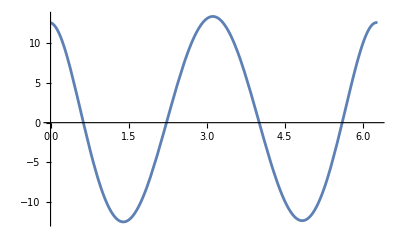

```mathematica
Plot[{Resfunc["density"][[3]][0,t]},{t,0,2Pi}]
```

```mathematica
{to,ro,θo,φo}=orbit["Trajectory"];
```

```mathematica
rring[t_,φ_]:=20+2*10^-1*Resfunc["density"][[3]][t,φ];
```

```mathematica
Show[ParametricPlot[{rring[0,φ]Cos[φ],rring[0,φ]Sin[φ]},{φ,0,2Pi},ImageSize->600,Axes->False,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All],Graphics[{Black,Disk[{0,0},2]}],Graphics[{Black,Disk[{ro[0]  Cos[φo[0]],ro[0] Sin[φo[0]]},0.5]}],ParametricPlot[{ro[λo]  Cos[φo[λo]],ro[λo] Sin[φo[λo]]},{λo,0,2},PlotStyle->{Red,AbsoluteDashing[{5,15}]}]];
```

ParametricPlot::exclul: {(-9.+0. JacobiSN[1.41421356237309504880169 λo,0.]^2)-0,Indeterminate-0} must be a list of equalities or real-valued functions.

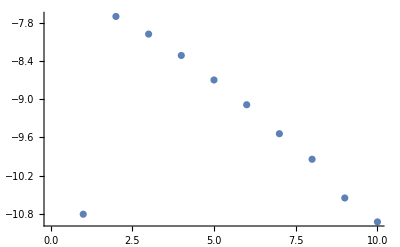

```mathematica
ListPlot[Table[Log[Abs[Sourcestable[[i]]["Sources"][[3]]]],{i,10}]]
```

### Circular inclined orbit

```mathematica
(*With[{a=SetPrecision[0,prec],p=SetPrecision[12,prec],e=SetPrecision[0,prec],x=SetPrecision[0.5,prec],radius=SetPrecision[20,prec],mass=SetPrecision[10^-4,prec]},orbitincl=KerrGeoOrbit[a,p,e,x];
Sourcestableincl={};
SetDirectory[NotebookDirectory[]];
Sourcesfilenameincl= "i"<>ToString[NumberForm[x,{6,1}]]<>"_p"<>ToString[NumberForm[p,{6,1}]]<>"_e"<>ToString[NumberForm[e,{6,1}]]<>"_r"<>ToString[NumberForm[radius,{6,1}]]<>".dat";
Sourcesfile = OpenAppend[Sourcesfilenameincl];
Do[
Do[
Sourcemode=RHSamplitudescalculation[m,0,k,orbitincl,radius,mass];
If[Abs[Sourcemode["Sources"][[1]]]<10^-13&&Abs[Sourcemode["Sources"][[2]]]<10^-13&&Abs[Sourcemode["Sources"][[3]]]<10^-13&&Abs[Sourcemode["Sources"][[4]]]<10^-13&&k+m>4,Break[]];
mywrite[Sourcemode,Sourcesfile];
AppendTo[Sourcestableincl,Sourcemode],
{k,-m+1,20}],
{m,5,10}
];
Close[Sourcesfile];]*)
```

```mathematica
With[{a=SetPrecision[0,prec],p=SetPrecision[12,prec],e=SetPrecision[0,prec],x=SetPrecision[ 0.5,prec],radius=SetPrecision[20,prec],mass=SetPrecision[10^-4,prec]},orbitincl=KerrGeoOrbit[a,p,e,x];
SetDirectory[NotebookDirectory[]];
Sourcesfilenameincl= "i"<>ToString[NumberForm[x,{6,1}]]<>"_p"<>ToString[NumberForm[p,{6,1}]]<>"_e"<>ToString[NumberForm[e,{6,1}]]<>"_r"<>ToString[NumberForm[radius,{6,1}]]<>".dat";
Sourcestableincl=Sourcefiletotable[Import[Sourcesfilenameincl],radius,mass];
]
```

```mathematica
Resfuncincl=ResultingfunctionsRing[Sourcestableincl];
```

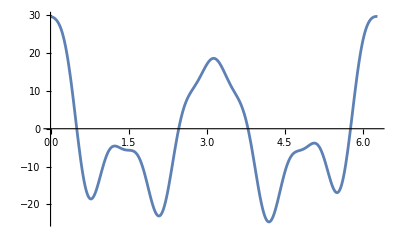

```mathematica
Plot[{ Resfuncincl["density"][["dr"]][0,phi]},{phi,0,2Pi}]
```

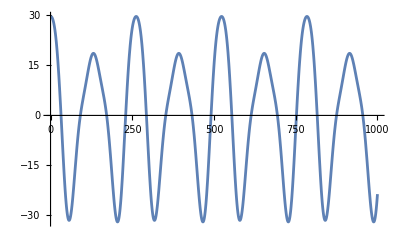

```mathematica
Plot[{ Resfuncincl["density"][["dr"]][t,0]},{t,0,1000}]
```

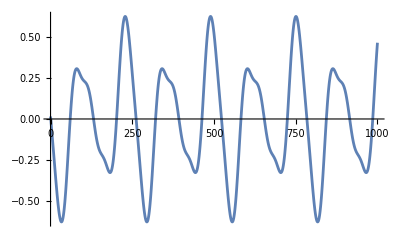

```mathematica
Plot[{Resfuncincl["Fourvelocity"][[2]][t,0]},{t,0,1000}]
```

```mathematica
θring[t_,φ_]:=Pi/2+2*10^-2*Resfuncincl["density"][[2]][t,φ];
rring[t_,φ_]:=20+2*10^-2*Resfuncincl["density"][[3]][t,φ];
```

```mathematica
{to,ro,θo,φo}=orbitincl["Trajectory"];
```

```mathematica
Show[ParametricPlot3D[{rring[0,φ] Sin[θring[0,φ]] Cos[φ],rring[0,φ] Sin[θring[0,φ]] Sin[φ],rring[0,φ]Cos[θring[0,φ]]},{φ,0,2Pi},ImageSize->600,Boxed->True,Axes->True,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All]/. Line[x_]:>Sequence[Arrowheads[Table[0.008,{6}]],Arrow@Line[x]],Graphics3D[{Black,Sphere[{0,0,0},2]}],Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},{0,0,5}}]}],ParametricPlot3D[{ro[λo] Sin[θo[λo]] Cos[φo[λo]],ro[λo] Sin[θo[λo]] Sin[φo[λo]],ro[λo] Cos[θo[λo]]},{λo,0,2},PlotStyle->{Red,AbsoluteDashing[{5,15}]}],Graphics3D[{Black,Sphere[{ro[0.2] Sin[θo[0.2]] Cos[φo[0.2]],ro[0.2] Sin[θo[0.2]] Sin[φo[0.2]],ro[0.2] Cos[θo[0.2]]},0.5]}]]
```

ParametricPlot3D::exclul: {(ⅈ+Tan[1.570796326794896619231322+4. λo])-0,(-ⅈ+Tan[1.570796326794896619231322+4. λo])-0,(ⅈ+0.5 Tan[1.570796326794896619231322+4. λo])-0,(-ⅈ+0.5 Tan[1.570796326794896619231322+4. λo])-0,«4»,Cos[1.570796326794896619231322+4. λo]-0,Re[Tan[1.570796326794896619231322+4. λo]]-0,0.5 Re[Tan[1.570796326794896619231322+4. λo]]-0,-0.75 Im[Cos[4. λo]^2]-0} must be a list of equalities or real-valued functions.

-Graphics3D-

```mathematica
(*Animate[Show[ParametricPlot3D[{rring[to[λ],φ] Sin[θring[to[λ],φ]] Cos[φ],rring[to[λ],φ] Sin[θring[to[λ],φ]] Sin[φ],rring[to[λ],φ]Cos[θring[to[λ],φ]]},{φ,0,2Pi},ImageSize->600,Boxed->False,Axes->False,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All]/. Line[x_]:>Sequence[Arrowheads[Table[0.008,{6}]],Arrow@Line[x]],Graphics3D[{Black,Sphere[{0,0,0},2]}],Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},{0,0,5}}]}],Graphics3D[{Black,Sphere[{ro[λ] Sin[θo[λ]] Cos[φo[λ]],ro[λ] Sin[θo[λ]] Sin[φo[λ]],ro[λ] Cos[θo[λ]]},0.5]}],
ParametricPlot3D[{ro[λo] Sin[θo[λo]] Cos[φo[λo]],ro[λo] Sin[θo[λo]] Sin[φo[λo]],ro[λo] Cos[θo[λo]]},{λo,0,2},PlotStyle->{Red,AbsoluteDashing[{5,15}]}]],{λ,0,5,0.001},AnimationRate->0.15]*)
```

```mathematica
(*Ringframes=Table[Show[ParametricPlot3D[{rring[to[λ],φ] Sin[θring[to[λ],φ]] Cos[φ],rring[to[λ],φ] Sin[θring[to[λ],φ]] Sin[φ],rring[to[λ],φ]Cos[θring[to[λ],φ]]},{φ,0,2Pi},ImageSize->600,Boxed->False,Axes->False,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All,ViewPoint->{2,-5,1.5},SphericalRegion->True]/. Line[x_]:>Sequence[Arrowheads[Table[0.008,{6}]],Arrow@Line[x]],Graphics3D[{Black,Sphere[{0,0,0},2]}],Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},{0,0,5}}]}],Graphics3D[{Black,Sphere[{ro[λ] Sin[θo[λ]] Cos[φo[λ]],ro[λ] Sin[θo[λ]] Sin[φo[λ]],ro[λ] Cos[θo[λ]]},0.5]}],
ParametricPlot3D[{ro[λo] Sin[θo[λo]] Cos[φo[λo]],ro[λo] Sin[θo[λo]] Sin[φo[λo]],ro[λo] Cos[θo[λo]]},{λo,0,2},PlotStyle->{Red,AbsoluteDashing[{5,15}]}]],{λ,0,5,0.1}];*)
```

```mathematica
(*Export["animation.gif",Ringframes,"AnimationRepetitions"->Infinity]
Do[Export["animation_frames/frame_"<>StringPadLeft[ToString[i],4,"0"]<>".png",Ringframes[[i]],"PNG"],{i,1,Length[Ringframes]}]*)
```

```mathematica
(*Ringframes=Table[Show[ParametricPlot3D[{rring[to[λ],φ] Sin[θring[to[λ],φ]] Cos[φ],rring[to[λ],φ] Sin[θring[to[λ],φ]] Sin[φ],rring[to[λ],φ]Cos[θring[to[λ],φ]]},{φ,0,2Pi},ImageSize->600,Boxed->False,Axes->False,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All,ViewPoint->{1,-5,0},SphericalRegion->True]/. Line[x_]:>Sequence[Arrowheads[Table[0.008,{6}]],Arrow@Line[x]],Graphics3D[{Black,Sphere[{0,0,0},2]}],Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},{0,0,5}}]}],Graphics3D[{Black,Sphere[{ro[λ] Sin[θo[λ]] Cos[φo[λ]],ro[λ] Sin[θo[λ]] Sin[φo[λ]],ro[λ] Cos[θo[λ]]},0.5]}],
ParametricPlot3D[{ro[λo] Sin[θo[λo]] Cos[φo[λo]],ro[λo] Sin[θo[λo]] Sin[φo[λo]],ro[λo] Cos[θo[λo]]},{λo,0,2},PlotStyle->{Red,AbsoluteDashing[{5,15}]}]],{λ,0,5,0.1}];*)
```

```mathematica
(*Export["animation2.gif",Ringframes,"AnimationRepetitions"->Infinity]*)
```

```mathematica
(*Do[Export["animation_frames2/frame_"<>StringPadLeft[ToString[i],4,"0"]<>".png",Ringframes[[i]],"PNG"],{i,1,Length[Ringframes]}]*)
```

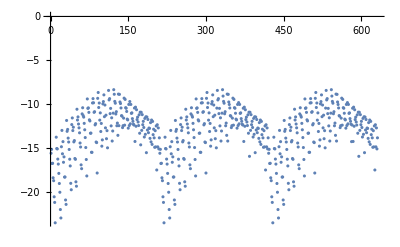

```mathematica
ListPlot[Table[Log[Abs[Sourcestableincl[[i]]["Sources"][[3]]]],{i,Length[Sourcestableincl]}]]
```

#### Plots for the paper

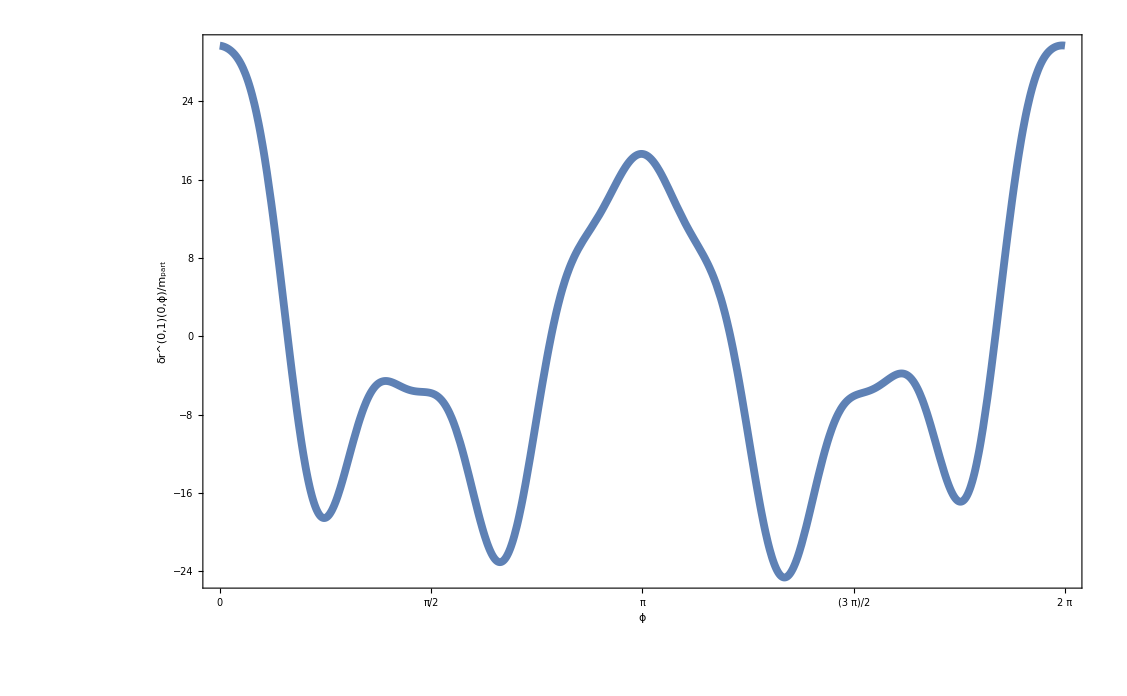

```mathematica
Plot[Resfuncincl["density"][["dr"]][0,phi],{phi,0,2Pi},PlotStyle->Thickness[0.005],Frame->True,FrameTicksStyle->Directive[Black,35],FrameTicks->{{Automatic,None},{Table[{n Pi/2,ToString[TraditionalForm[n π/2]]},{n,0,4}],Automatic}},Axes->False,FrameLabel->{Style["ϕ",FontSize->35,Black],Style["δr^(0,1)(0,ϕ)/m_part",FontSize->35,Black]}]//Quiet
```

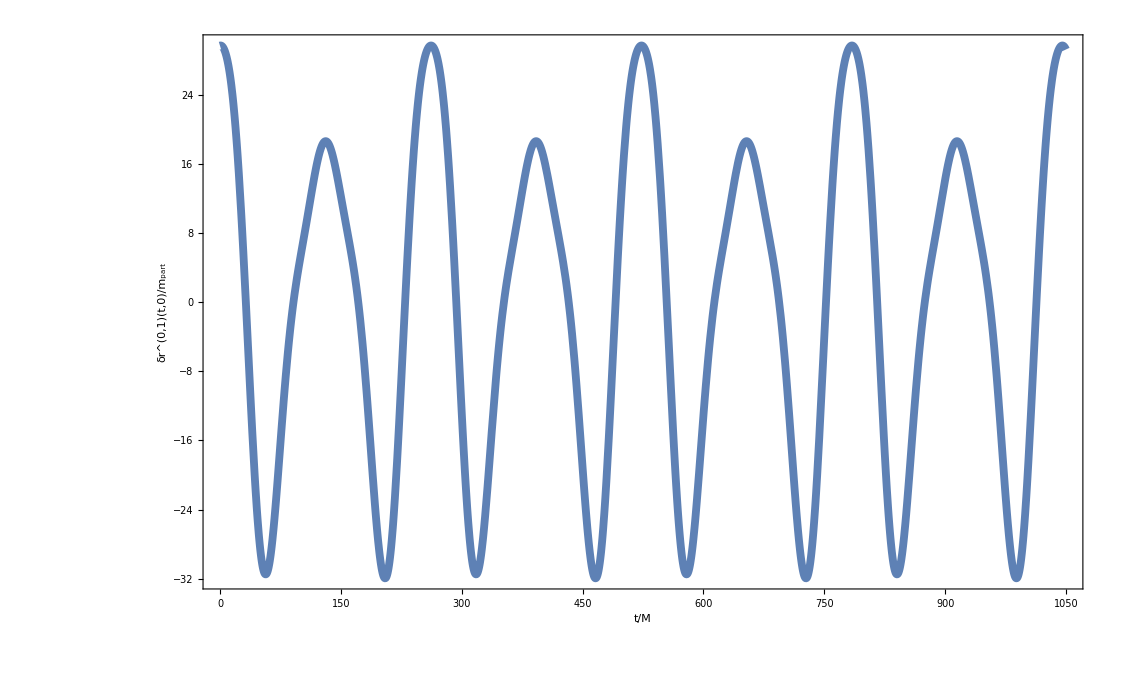

```mathematica
Plot[Resfuncincl["density"][["dr"]][t,0],{t,0,1050},Frame->True,PlotStyle->Thickness[0.005],FrameTicksStyle->Directive[Black,35],Axes->False,FrameLabel->{Style["t/M",FontSize->35,Black],Style["δr^(0,1)(t,0)/m_part",FontSize->35,Black]}]//Quiet
```

```mathematica
Circular inclined orbit
```

Circular inclined KerrGeoOrbitFunction[…]

### Circular inclined orbit large radius

```mathematica
(*With[{a=SetPrecision[0,prec],p=SetPrecision[12,prec],e=SetPrecision[0,prec],x=SetPrecision[0.5,prec],radius=SetPrecision[400,prec],mass=SetPrecision[10^-4,prec]},orbitincl=KerrGeoOrbit[a,p,e,x];
Sourcestableincl={};
SetDirectory[NotebookDirectory[]];
Sourcesfilenameincl= "i"<>ToString[NumberForm[x,{6,1}]]<>"_p"<>ToString[NumberForm[p,{6,1}]]<>"_e"<>ToString[NumberForm[e,{6,1}]]<>"_r"<>ToString[NumberForm[radius,{6,1}]]<>".dat";
Sourcesfile = OpenAppend[Sourcesfilenameincl];
Do[
Do[
Sourcemode=RHSamplitudescalculation[m,0,k,orbitincl,radius,mass];
If[Abs[Sourcemode["Sources"][[1]]]<10^-18&&Abs[Sourcemode["Sources"][[2]]]<10^-18&&Abs[Sourcemode["Sources"][[3]]]<10^-18&&Abs[Sourcemode["Sources"][[4]]]<10^-18&&k+m>5,Break[]];
mywrite[Sourcemode,Sourcesfile];
AppendTo[Sourcestableincl,Sourcemode],
{k,-m+1,20}],
{m,-10,10}
];
Close[Sourcesfile];]*)
```

```mathematica
With[{a=SetPrecision[0,prec],p=SetPrecision[12,prec],e=SetPrecision[0,prec],x=SetPrecision[ 0.5,prec],radius=SetPrecision[400,prec],mass=SetPrecision[10^-4,prec]},orbitincl=KerrGeoOrbit[a,p,e,x];
SetDirectory[NotebookDirectory[]];
Sourcesfilenameincl= "i"<>ToString[NumberForm[x,{6,1}]]<>"_p"<>ToString[NumberForm[p,{6,1}]]<>"_e"<>ToString[NumberForm[e,{6,1}]]<>"_r"<>ToString[NumberForm[radius,{6,1}]]<>".dat";
Sourcestableincl=Sourcefiletotable[Import[Sourcesfilenameincl],radius,mass];
]
```

```mathematica
Resfuncincl=ResultingfunctionsRing[Sourcestableincl];
```

```mathematica
θring[t_,φ_]:=Pi/2+4*10^3*Resfuncincl["density"][[2]][t,φ];
rring[t_,φ_]:=400+4*10^3*Resfuncincl["density"][[3]][t,φ];
```

```mathematica
{to,ro,θo,φo}=orbitincl["Trajectory"];
```

```mathematica
(*Ringframes=Table[Show[ParametricPlot3D[{rring[to[λ],φ] Sin[θring[to[λ],φ]] Cos[φ],rring[to[λ],φ] Sin[θring[to[λ],φ]] Sin[φ],rring[to[λ],φ]Cos[θring[to[λ],φ]]},{φ,0,2Pi},ImageSize->600,Boxed->False,Axes->False,PlotStyle->{Blue,Thickness[0.005]},PlotRange->All,ViewPoint->{2,-5,1.5},SphericalRegion->True]/. Line[x_]:>Sequence[Arrowheads[Table[0.008,{6}]],Arrow@Line[x]],Graphics3D[{Black,Sphere[{0,0,0},2]}],Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},{0,0,5}}]}],Graphics3D[{Black,Sphere[{ro[λ] Sin[θo[λ]] Cos[φo[λ]],ro[λ] Sin[θo[λ]] Sin[φo[λ]],ro[λ] Cos[θo[λ]]},0.5]}],
ParametricPlot3D[{ro[λo] Sin[θo[λo]] Cos[φo[λo]],ro[λo] Sin[θo[λo]] Sin[φo[λo]],ro[λo] Cos[θo[λo]]},{λo,0,2},PlotStyle->{Red,AbsoluteDashing[{5,15}]}]],{λ,0,0,0}];*)
```

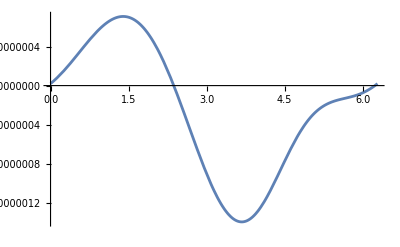

```mathematica
Plot[{ Resfuncincl["density"][["dtheta"]][0,phi]},{phi,0,2Pi}]
```

## The total source S_r_r^(1,1) at r=r_r

```mathematica
Teukeqfactor=-2r[]^6;
```

## The part proportional to δ(r-r_s)

### In total

```mathematica
(*TotalSourceDirac=Teukeqfactor*(-O10Psi4Diracfin-K1Diracfin-K2Diracfin+PureSourceDiracfin+PureSource11Diracfin+TeukSource11StressenergyumuDiracfin)/.r[]->R//Simplify;*)
```

```mathematica
(*TotalSourceDiracfin0=Collect[TotalSourceDirac,{RadHZ†[-1 + li, -mi, -omega, R],RadHZ†[ li, -mi, -omega, R],RadHZ†[1 + li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li-1,-mi,-omega,R],Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R],Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R]}]//Simplify;*)
```

```mathematica
TotalSourceDiracfin=((2*ad*Sqrt[3*Pi]*(2*MB-R)*RadHZ†[-1+li,-mi,-omega,R]*(I*Sqrt[2]*Sqrt[-2-li+li^2]*(384*MB^4+16*MB^3*R*(-57-8*li+8*li^2-(57*I)*omega*R)-4*MB^2*R^2*(-186-14*li^3+7*li^4-(357*I)*omega*R+182*omega^2*R^2+li*(-37-(46*I)*omega*R)+li^2*(44+(46*I)*omega*R))+R^4*(14*li^3-7*li^4-2*li*(13-(6*I)*omega*R+16*omega^2*R^2)+li^2*(19-(12*I)*omega*R+32*omega^2*R^2)+8*omega*R*(2*I-6*omega*R+I*omega^2*R^2-3*omega^3*R^3))+2*MB*R^3*(-28*li^3+14*li^4+li^2*(9+(58*I)*omega*R-32*omega^2*R^2)+li*(5-(58*I)*omega*R+32*omega^2*R^2)+2*(-57-(98*I)*omega*R+omega^2*R^2-(28*I)*omega^3*R^3)))*TripleIntC[-2,-1,1,-1+li,li,mi]+6*R^2*(-16*MB^3*omega-(4*I)*MB^2*(16-2*li^3+li^4+(20*I)*omega*R-8*omega^2*R^2+2*li*(5+(3*I)*omega*R)+li^2*(-9-(6*I)*omega*R))-(-2-li+li^2)*R^2*(li*(I-3*omega*R)+li^2*(-I+3*omega*R)-4*omega*R*(2+omega^2*R^2))-2*MB*R*(6*li^3*omega*R-3*li^4*omega*R+li^2*(8*I+9*omega*R+(10*I)*omega^2*R^2)-(2*I)*li*(4-(6*I)*omega*R+5*omega^2*R^2)+2*(-8*I-5*omega*R-(11*I)*omega^2*R^2+2*omega^3*R^3)))*TripleIntC[-2,0,1,-1+li,li,mi]+(6*I)*Sqrt[2]*Sqrt[-6-li+li^2]*MB*(8*MB-3*R)*(8*MB^2+2*MB*R*(-6-li+li^2-(3*I)*omega*R)+R^2*(2+li-li^2-(2*I)*omega*R+2*omega^2*R^2))*TripleIntC[-2,1,1,-1+li,li,mi]))/((-1)^mi*R)+(RadHZ†[li,-mi,-omega,R]*((2*I)*ad*Sqrt[-2+li+li^2]*Sqrt[6*Pi]*(-2*MB+R)^2*(384*MB^4+16*MB^3*R*(-57+8*li+8*li^2-(57*I)*omega*R)-4*MB^2*R^2*(-186+14*li^3+7*li^4-(357*I)*omega*R+182*omega^2*R^2+li*(37+(46*I)*omega*R)+li^2*(44+(46*I)*omega*R))+R^4*(-14*li^3-7*li^4+2*li*(13-(6*I)*omega*R+16*omega^2*R^2)+li^2*(19-(12*I)*omega*R+32*omega^2*R^2)+8*omega*R*(2*I-6*omega*R+I*omega^2*R^2-3*omega^3*R^3))+2*MB*R^3*(28*li^3+14*li^4+li*(-5+(58*I)*omega*R-32*omega^2*R^2)+li^2*(9+(58*I)*omega*R-32*omega^2*R^2)+2*(-57-(98*I)*omega*R+omega^2*R^2-(28*I)*omega^3*R^3)))*TripleIntC[-2,-1,1,li,li,mi]+3*(md*R*(-1024*MB^5+256*MB^4*R*(12-li-li^2+(4*I)*omega*R)+16*MB^3*R^2*(-200+4*li^3+2*li^4-(159*I)*omega*R+67*omega^2*R^2+12*li*(2+I*omega*R)+2*li^2*(13+(6*I)*omega*R))+4*MB^2*R^3*(384+(512*I)*omega*R-250*omega^2*R^2+(20*I)*omega^3*R^3+li^4*(-9+(3*I)*omega*R)+(6*I)*li^3*(3*I+omega*R)+2*li*(-31-(52*I)*omega*R+17*omega^2*R^2)+li^2*(-71-(101*I)*omega*R+34*omega^2*R^2))+4*MB*R^4*(-88-(171*I)*omega*R+59*omega^2*R^2-(46*I)*omega^3*R^3+12*omega^4*R^4+li^4*(3-(3*I)*omega*R)+li^3*(6-(6*I)*omega*R)+li^2*(25+(60*I)*omega*R-25*omega^2*R^2+(2*I)*omega^3*R^3)+li*(22+(63*I)*omega*R-25*omega^2*R^2+(2*I)*omega^3*R^3))-R^5*(li^4*(1-(3*I)*omega*R)+li^3*(2-(6*I)*omega*R)+2*li*(7+(23*I)*omega*R-8*omega^2*R^2+(2*I)*omega^3*R^3)+li^2*(15+(43*I)*omega*R-16*omega^2*R^2+(4*I)*omega^3*R^3)+8*(-4-(10*I)*omega*R-(7*I)*omega^3*R^3+2*omega^4*R^4)))-4*ad*Sqrt[3*Pi]*R^2*(-2*MB+R)^2*(16*MB^3*omega+(4*I)*MB^2*(16+2*li^3+li^4+(20*I)*omega*R-8*omega^2*R^2+li*(-10-(6*I)*omega*R)+li^2*(-9-(6*I)*omega*R))+(-2+li+li^2)*R^2*(li*(-I+3*omega*R)+li^2*(-I+3*omega*R)-4*omega*R*(2+omega^2*R^2))+2*MB*R*(-6*li^3*omega*R-3*li^4*omega*R+2*li*(4*I+6*omega*R+(5*I)*omega^2*R^2)+li^2*(8*I+9*omega*R+(10*I)*omega^2*R^2)+2*(-8*I-5*omega*R-(11*I)*omega^2*R^2+2*omega^3*R^3)))*TripleIntC[-2,0,1,li,li,mi]+(4*I)*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*(8*MB-3*R)*(-2*MB+R)^2*(8*MB^2+2*MB*R*(-6+li+li^2-(3*I)*omega*R)+R^2*(2-li-li^2-(2*I)*omega*R+2*omega^2*R^2))*TripleIntC[-2,1,1,li,li,mi])))/((-1)^mi*(2*MB-R)*R)+(2*ad*Sqrt[3*Pi]*(2*MB-R)*RadHZ†[1+li,-mi,-omega,R]*(I*Sqrt[2]*Sqrt[li*(3+li)]*(384*MB^4+16*MB^3*R*(-41+24*li+8*li^2-(57*I)*omega*R)-4*MB^2*R^2*(-84+42*li^3+7*li^4-(265*I)*omega*R+182*omega^2*R^2+2*li^2*(64+(23*I)*omega*R)+3*li*(65+(46*I)*omega*R))+2*MB*R^3*(-68+84*li^3+14*li^4-(80*I)*omega*R-62*omega^2*R^2-(56*I)*omega^3*R^3+li*(153+(174*I)*omega*R-96*omega^2*R^2)+li^2*(177+(58*I)*omega*R-32*omega^2*R^2))-R^4*(42*li^3+7*li^4+li*(6+(36*I)*omega*R-96*omega^2*R^2)+li^2*(65+(12*I)*omega*R-32*omega^2*R^2)+8*(-3+I*omega*R-2*omega^2*R^2-I*omega^3*R^3+3*omega^4*R^4)))*TripleIntC[-2,-1,1,1+li,li,mi]+6*R^2*((-6*I)*li^3*(2*MB-R)*(2*MB+R+(3*I)*omega*R^2)-I*li^4*(2*MB-R)*(2*MB+R+(3*I)*omega*R^2)-4*MB*omega*(4*MB^2+8*MB*R*(-1-I*omega*R)+R^2*(1-I*omega*R+2*omega^2*R^2))-li^2*(12*MB^2*(I+2*omega*R)+(2*I)*MB*R*(8+(27*I)*omega*R+10*omega^2*R^2)+R^2*(-11*I+25*omega*R-4*omega^3*R^3))+6*li*(-12*MB^2*(-I+omega*R)-(2*I)*MB*R*(4+5*omega^2*R^2)+R^2*(I+omega*R+2*omega^3*R^3)))*TripleIntC[-2,0,1,1+li,li,mi]+(6*I)*Sqrt[2]*Sqrt[-4+3*li+li^2]*MB*(8*MB-3*R)*(8*MB^2+2*MB*R*(-4+3*li+li^2-(3*I)*omega*R)+R^2*(-3*li-li^2+2*omega*R*(-I+omega*R)))*TripleIntC[-2,1,1,1+li,li,mi]))/((-1)^mi*R)+(4*ad*Sqrt[3*Pi]*(-2*MB+R)^2*(2*Sqrt[2]*Sqrt[-2-li+li^2]*((48*I)*MB^3+MB^2*R*(-63*I-(8*I)*li+(8*I)*li^2+66*omega*R)+MB*R^2*(24*I-19*omega*R+(40*I)*omega^2*R^2-2*li*(I+5*omega*R)+2*li^2*(I+5*omega*R))+R^3*(li*(3*I+5*omega*R)-li^2*(3*I+5*omega*R)+2*omega*R*(1+(2*I)*omega*R+3*omega^2*R^2)))*TripleIntC[-2,-1,1,-1+li,li,mi]-(3*I)*R*(16*MB^2*(-2-li+li^2-I*omega*R)+2*MB*R*(8+2*li^3-li^4-(10*I)*omega*R+4*omega^2*R^2+li*(2-(6*I)*omega*R)+li^2*(-3+(6*I)*omega*R))+(-2-li+li^2)*R^2*(-li+li^2-4*omega*R*(I+omega*R)))*TripleIntC[-2,0,1,-1+li,li,mi]+(6*I)*Sqrt[2]*Sqrt[-6-li+li^2]*MB*(8*MB-3*R)*(MB+I*omega*R^2)*TripleIntC[-2,1,1,-1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,R])/(-1)^mi+((8*ad*Sqrt[-2+li+li^2]*Sqrt[6*Pi]*(-2*MB+R)^2*((48*I)*MB^3+MB^2*R*(-63*I+(8*I)*li+(8*I)*li^2+66*omega*R)+MB*R^2*(24*I-19*omega*R+(40*I)*omega^2*R^2+2*li*(I+5*omega*R)+2*li^2*(I+5*omega*R))+R^3*(-(li*(3*I+5*omega*R))-li^2*(3*I+5*omega*R)+2*omega*R*(1+(2*I)*omega*R+3*omega^2*R^2)))*TripleIntC[-2,-1,1,li,li,mi]+3*(-256*MB^4*md*R+320*MB^3*md*R^2+32*li*MB^3*md*R^2+32*li^2*MB^3*md*R^2-128*MB^2*md*R^3-24*li*MB^2*md*R^3-28*li^2*MB^2*md*R^3-8*li^3*MB^2*md*R^3-4*li^4*MB^2*md*R^3+(432*I)*MB^3*md*omega*R^3+16*MB*md*R^4+4*li^2*MB*md*R^4+8*li^3*MB*md*R^4+4*li^4*MB*md*R^4-(504*I)*MB^2*md*omega*R^4+(72*I)*li*MB^2*md*omega*R^4+(72*I)*li^2*MB^2*md*omega*R^4+2*li*md*R^5+li^2*md*R^5-2*li^3*md*R^5-li^4*md*R^5+(196*I)*MB*md*omega*R^5-(60*I)*li*MB*md*omega*R^5-(60*I)*li^2*MB*md*omega*R^5-176*MB^2*md*omega^2*R^5-(24*I)*md*omega*R^6+(12*I)*li*md*omega*R^6+(12*I)*li^2*md*omega*R^6+168*MB*md*omega^2*R^6-8*li*MB*md*omega^2*R^6-8*li^2*MB*md*omega^2*R^6-40*md*omega^2*R^7+4*li*md*omega^2*R^7+4*li^2*md*omega^2*R^7+(48*I)*MB*md*omega^3*R^7-(16*I)*md*omega^3*R^8-(4*I)*ad*Sqrt[3*Pi]*R*(-2*MB+R)^2*(16*MB^2*(-2+li+li^2-I*omega*R)+2*MB*R*(8-2*li^3-li^4-(10*I)*omega*R+4*omega^2*R^2+li^2*(-3+(6*I)*omega*R)+li*(-2+(6*I)*omega*R))+(-2+li+li^2)*R^2*(li+li^2-4*omega*R*(I+omega*R)))*TripleIntC[-2,0,1,li,li,mi]+(256*I)*ad*Sqrt[-6+li+li^2]*MB^5*Sqrt[6*Pi]*TripleIntC[-2,1,1,li,li,mi]-(352*I)*ad*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*R*TripleIntC[-2,1,1,li,li,mi]+(160*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-256*ad*Sqrt[-6+li+li^2]*MB^4*omega*Sqrt[6*Pi]*R^2*TripleIntC[-2,1,1,li,li,mi]-(24*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]+352*ad*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*R^3*TripleIntC[-2,1,1,li,li,mi]-160*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R^4*TripleIntC[-2,1,1,li,li,mi]+24*ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R^5*TripleIntC[-2,1,1,li,li,mi]))*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R])/(-1)^mi+(4*ad*Sqrt[3*Pi]*(-2*MB+R)^2*((2*I)*Sqrt[2]*Sqrt[li*(3+li)]*(48*MB^3+MB^2*R*(-47+24*li+8*li^2-(66*I)*omega*R)+MB*R^2*(28-I*omega*R+40*omega^2*R^2+6*li*(1-(5*I)*omega*R)+2*li^2*(1-(5*I)*omega*R))+R^3*(-6+(8*I)*omega*R+4*omega^2*R^2-(6*I)*omega^3*R^3+li^2*(-3+(5*I)*omega*R)+li*(-9+(15*I)*omega*R)))*TripleIntC[-2,-1,1,1+li,li,mi]+(3*I)*(R*(6*li^3*(2*MB-R)*R+li^4*(2*MB-R)*R+(4*I)*MB*omega*R*(4*MB+R*(-1+(2*I)*omega*R))-6*li*(8*MB^2+R^2-(2*I)*omega*R^3-2*omega^2*R^4+(6*I)*MB*R*(I+omega*R))+li^2*(-16*MB^2+6*MB*R*(5-(2*I)*omega*R)+R^2*(-11+(4*I)*omega*R+4*omega^2*R^2)))*TripleIntC[-2,0,1,1+li,li,mi]+2*Sqrt[2]*Sqrt[-4+3*li+li^2]*MB*(8*MB-3*R)*(MB+I*omega*R^2)*TripleIntC[-2,1,1,1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R])/(-1)^mi-((192*I)*R^5*(omega*R^2*((-12*I)*ad*mi*(2*MB-R)+li*(1+li)*md*R)*RadPsi4c[li,mi,omega,R]+(I*li*(1+li)*md*(56*MB-25*R)*R+ad*mi*(2*MB-R)*(2*(-62+li+li^2)*MB-(-54+li+li^2)*R))*RadPsi4c[li,mi,omega,R]-ad*(1+li)*Sqrt[(-4+li^2)/(-1+4*li^2)]*Sqrt[li^2-mi^2]*(2*MB-R)*((2*(-25+li)*MB+R*(29-li+(6*I)*omega*R))*RadPsi4c[-1+li,mi,omega,R]+14*(2*MB-R)*R*Derivative[0,0,0,1][RadPsi4c][-1+li,mi,omega,R])+(2*MB-R)*(28*ad*mi*(2*MB-R)-(5*I)*li*(1+li)*md*R)*(4*RadPsi4c[li,mi,omega,R]-R*Derivative[0,0,0,1][RadPsi4c][li,mi,omega,R])-ad*li*Sqrt[(-3+2*li+li^2)/(3+8*li+4*li^2)]*Sqrt[1+2*li+li^2-mi^2]*(2*MB-R)*((-2*(26+li)*MB+R*(30+li+(6*I)*omega*R))*RadPsi4c[1+li,mi,omega,R]+14*(2*MB-R)*R*Derivative[0,0,0,1][RadPsi4c][1+li,mi,omega,R])))/(li*(1+li)*(2*MB-R))-(96*md*Pi*Sqrt[-3*MB+R]*(2*fourvelocitycoef[1,mi,R,Pi/2]*(MB*R*((288*I)*MB^3+16*MB^2*R*(-27*I+omega*R)+(6*I)*MB*R^2*(36+(2*I)*omega*R+3*omega^2*R^2)+R^3*(-36*I+2*omega*R-(8*I)*omega^2*R^2+omega^3*R^3))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(-2*MB+R)*(-2*Sqrt[MB]*(32*MB^2+(20*I)*MB^(3/2)*mi*Sqrt[R]+16*MB*R*(-2-I*omega*R)+2*Sqrt[MB]*mi*R^(3/2)*(-4*I+omega*R)+R^2*(8+(6*I)*omega*R-omega^2*R^2))*SWSHtheta[-1,li,mi,Pi/2]-Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*((4*I)*MB-4*Sqrt[MB]*mi*Sqrt[R]+R*(-2*I+3*omega*R))*SWSHtheta[0,li,mi,Pi/2]))+(2*MB-R)*(((4*I)*MB+R*(-2*I+omega*R))*fourvelocitycoef[2,mi,R,Pi/2]*(MB*(72*MB^2+2*MB*R*(-36-(11*I)*omega*R)+R^2*(18+(10*I)*omega*R-omega^2*R^2))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*Sqrt[R]*(-2*MB+R)*(2*Sqrt[MB]*((8*I)*MB+R*(-4*I+omega*R))*SWSHtheta[-1,li,mi,Pi/2]-Sqrt[li*(1+li)]*Sqrt[R]*(-2*MB+R)*SWSHtheta[0,li,mi,Pi/2]))+Sqrt[2]*R*(fourvelocitycoef[4,mi,R,Pi/2]*(MB*mi*((72*I)*MB^2+2*MB*R*(-36*I+11*omega*R)+R^2*(18*I-10*omega*R-I*omega^2*R^2))*SWSHtheta[-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*Sqrt[MB]*mi*(2*MB-R)*Sqrt[R]*(8*MB+R*(-4-I*omega*R))*SWSHtheta[-1,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*mi*R*SWSHtheta[0,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*mi*R^2*SWSHtheta[0,li,mi,Pi/2]-I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*mi*R^3*SWSHtheta[0,li,mi,Pi/2]-(72*I)*MB^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+(72*I)*MB^2*R*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(18*I)*MB*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-22*MB^2*omega*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+10*MB*omega*R^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+I*MB*omega^2*R^4*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-32*Sqrt[-2+li+li^2]*MB^(5/2)*Sqrt[R]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+32*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-8*Sqrt[-2+li+li^2]*Sqrt[MB]*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[-2+li+li^2]*MB^(3/2)*omega*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-(2*I)*Sqrt[-2+li+li^2]*Sqrt[MB]*omega*R^(7/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*R*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*R^2*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*R^3*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*(I*(88*MB^3*mi-160*MB^(5/2)*omega*R^(3/2)+8*MB^(3/2)*omega*R^(5/2)*(20+(9*I)*omega*R)+2*MB^2*mi*R*(-44-(25*I)*omega*R)+MB*mi*R^2*(22+(22*I)*omega*R-3*omega^2*R^2)+4*Sqrt[MB]*omega*R^(7/2)*(-10-(8*I)*omega*R+omega^2*R^2))*SWSHtheta[-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*Sqrt[R]*(-2*MB+R)*(-4*MB^(3/2)*mi+12*MB*omega*R^(3/2)+2*omega*R^(5/2)*(-3-I*omega*R)+Sqrt[MB]*mi*R*(2+I*omega*R))*SWSHtheta[-1,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*mi*R*SWSHtheta[0,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*mi*R^2*SWSHtheta[0,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*mi*R^3*SWSHtheta[0,li,mi,Pi/2]-(72*I)*MB^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+(72*I)*MB^2*R*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(18*I)*MB*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-22*MB^2*omega*R^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+10*MB*omega*R^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+I*MB*omega^2*R^4*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-32*Sqrt[-2+li+li^2]*MB^(5/2)*Sqrt[R]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+32*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-8*Sqrt[-2+li+li^2]*Sqrt[MB]*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[-2+li+li^2]*MB^(3/2)*omega*R^(5/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-(2*I)*Sqrt[-2+li+li^2]*Sqrt[MB]*omega*R^(7/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]+(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB^2*R*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]-(4*I)*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*MB*R^2*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*Sqrt[-2+li+li^2]*R^3*Derivative[0,0,0,1][SWSHtheta][0,li,mi,Pi/2])))))/((-2*MB+R)^2*(-(Sqrt[MB]*mi*R)+omega*R^(5/2))))/192;
```

### R^(0,1) parts

#### RO_((0)(0)l-1mω)^(1,0)

```mathematica
RO10[0,0,li-1,mi,omega]=Coefficient[TotalSourceDiracfin,RadPsi4c[li-1, mi, omega, R]]//Simplify
```

(ⅈ a_s √((-4+l^2)/(-1+4 l^2)) √(l^2-m^2) r_s^5 (2 (-25+l) M+r_s (29-l+6 ⅈ ω r_s)))/l

#### RO_((0)(0)lmω)^(1,0)

```mathematica
RO10[0,0,li,mi,omega]=Coefficient[TotalSourceDiracfin,RadPsi4c[li, mi, omega, R]]//Simplify
```

-ⅈ r_s^5 ((a_s m (2 (50+l+l^2) M+r_s (-58-l-l^2-12 ⅈ ω r_s)))/(l (1+l))+(m_s r_s (16 ⅈ M+r_s (-5 ⅈ+ω r_s)))/(2 M-r_s))

#### RO_((0)(0)l+1mω)^(1,0)

```mathematica
RO10[0,0,li+1,mi,omega]=Coefficient[TotalSourceDiracfin,RadPsi4c[li+1, mi, omega, R]]//Simplify
```

(ⅈ a_s √((-3+2 l+l^2)/(3+8 l+4 l^2)) √(1+2 l+l^2-m^2) r_s^5 (-2 (26+l) M+r_s (30+l+6 ⅈ ω r_s)))/(1+l)

#### RO_((0)(1)l-1mω)^(1,0)

```mathematica
RO10[0,1,li-1,mi,omega]=Coefficient[TotalSourceDiracfin,Derivative[0,0,0,1][RadPsi4c][li-1, mi, omega, R]]//Simplify
```

(14 ⅈ a_s √((-4+l^2)/(-1+4 l^2)) √(l^2-m^2) (2 M-r_s) r_s^6)/l

#### RO_((0)(1)lmω)^(1,0)

```mathematica
RO10[0,1,li,mi,omega]=Coefficient[TotalSourceDiracfin,Derivative[0,0,0,1][RadPsi4c][li, mi, omega, R]]//Simplify
```

r_s^6 ((28 ⅈ a_s m (2 M-r_s))/(l (1+l))+5 m_s r_s)

#### RO_((0)(1)l+1mω)^(1,0)

```mathematica
RO10[0,1,li+1,mi,omega]=Coefficient[TotalSourceDiracfin,Derivative[0,0,0,1][RadPsi4c][li+1, mi, omega, R]]//Simplify
```

(14 ⅈ a_s √((-3+2 l+l^2)/(3+8 l+4 l^2)) √(1+2 l+l^2-m^2) (2 M-r_s) r_s^6)/(1+l)

### R^(Hz(0,1)) parts

#### RΣ_((0)(0)l-1mω)^(1,0)

```mathematica
RΣ10[0,0,li-1,mi,omega]=Coefficient[TotalSourceDiracfin,RadHZ†[-1 + li, -mi, -omega, R]]//Simplify
```

1/(32 r_s)(-1)^-m a_s √(π/3) (2 M-r_s) (ⅈ √2 √(-2-l+l^2) (384 M^4+16 M^3 r_s (-57-8 l+8 l^2-57 ⅈ ω r_s)-4 M^2 r_s^2 (-186-14 l^3+7 l^4-357 ⅈ ω r_s+182 ω^2 r_s^2+l (-37-46 ⅈ ω r_s)+l^2 (44+46 ⅈ ω r_s))+r_s^4 (14 l^3-7 l^4-2 l (13-6 ⅈ ω r_s+16 ω^2 r_s^2)+l^2 (19-12 ⅈ ω r_s+32 ω^2 r_s^2)+8 ω r_s (2 ⅈ-6 ω r_s+ⅈ ω^2 r_s^2-3 ω^3 r_s^3))+2 M r_s^3 (-28 l^3+14 l^4+l^2 (9+58 ⅈ ω r_s-32 ω^2 r_s^2)+l (5-58 ⅈ ω r_s+32 ω^2 r_s^2)+2 (-57-98 ⅈ ω r_s+ω^2 r_s^2-28 ⅈ ω^3 r_s^3))) (C^{-2,l,m})_(-1,1,0,-1,-1+l,m)+6 r_s^2 (-16 M^3 ω-4 ⅈ M^2 (16-2 l^3+l^4+20 ⅈ ω r_s-8 ω^2 r_s^2+2 l (5+3 ⅈ ω r_s)+l^2 (-9-6 ⅈ ω r_s))-(-2-l+l^2) r_s^2 (l (ⅈ-3 ω r_s)+l^2 (-ⅈ+3 ω r_s)-4 ω r_s (2+ω^2 r_s^2))-2 M r_s (6 l^3 ω r_s-3 l^4 ω r_s+l^2 (8 ⅈ+9 ω r_s+10 ⅈ ω^2 r_s^2)-2 ⅈ l (4-6 ⅈ ω r_s+5 ω^2 r_s^2)+2 (-8 ⅈ-5 ω r_s-11 ⅈ ω^2 r_s^2+2 ω^3 r_s^3))) (C^{-2,l,m})_(0,1,0,-2,-1+l,m)+6 ⅈ √2 √(-6-l+l^2) M (8 M-3 r_s) (8 M^2+2 M r_s (-6-l+l^2-3 ⅈ ω r_s)+r_s^2 (2+l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) (C^{-2,l,m})_(1,1,0,-3,-1+l,m))

#### RΣ_((0)(0)lmω)^(1,0)

```mathematica
RΣ10[0,0,li,mi,omega]=Coefficient[TotalSourceDiracfin,RadHZ†[ li, -mi, -omega, R]]//Simplify
```

1/(192 (2 M-r_s) r_s)(-1)^-m (2 ⅈ a_s √(-2+l+l^2) √(6 π) (-2 M+r_s)^2 (384 M^4+16 M^3 r_s (-57+8 l+8 l^2-57 ⅈ ω r_s)-4 M^2 r_s^2 (-186+14 l^3+7 l^4-357 ⅈ ω r_s+182 ω^2 r_s^2+l (37+46 ⅈ ω r_s)+l^2 (44+46 ⅈ ω r_s))+r_s^4 (-14 l^3-7 l^4+2 l (13-6 ⅈ ω r_s+16 ω^2 r_s^2)+l^2 (19-12 ⅈ ω r_s+32 ω^2 r_s^2)+8 ω r_s (2 ⅈ-6 ω r_s+ⅈ ω^2 r_s^2-3 ω^3 r_s^3))+2 M r_s^3 (28 l^3+14 l^4+l (-5+58 ⅈ ω r_s-32 ω^2 r_s^2)+l^2 (9+58 ⅈ ω r_s-32 ω^2 r_s^2)+2 (-57-98 ⅈ ω r_s+ω^2 r_s^2-28 ⅈ ω^3 r_s^3))) (C^{-2,l,m})_(-1,1,0,-1,l,m)+3 (m_s r_s (-1024 M^5+256 M^4 r_s (12-l-l^2+4 ⅈ ω r_s)+16 M^3 r_s^2 (-200+4 l^3+2 l^4-159 ⅈ ω r_s+67 ω^2 r_s^2+12 l (2+ⅈ ω r_s)+2 l^2 (13+6 ⅈ ω r_s))+4 M^2 r_s^3 (384+512 ⅈ ω r_s-250 ω^2 r_s^2+20 ⅈ ω^3 r_s^3+l^4 (-9+3 ⅈ ω r_s)+6 ⅈ l^3 (3 ⅈ+ω r_s)+2 l (-31-52 ⅈ ω r_s+17 ω^2 r_s^2)+l^2 (-71-101 ⅈ ω r_s+34 ω^2 r_s^2))+4 M r_s^4 (-88-171 ⅈ ω r_s+59 ω^2 r_s^2-46 ⅈ ω^3 r_s^3+12 ω^4 r_s^4+l^4 (3-3 ⅈ ω r_s)+l^3 (6-6 ⅈ ω r_s)+l^2 (25+60 ⅈ ω r_s-25 ω^2 r_s^2+2 ⅈ ω^3 r_s^3)+l (22+63 ⅈ ω r_s-25 ω^2 r_s^2+2 ⅈ ω^3 r_s^3))-r_s^5 (l^4 (1-3 ⅈ ω r_s)+l^3 (2-6 ⅈ ω r_s)+2 l (7+23 ⅈ ω r_s-8 ω^2 r_s^2+2 ⅈ ω^3 r_s^3)+l^2 (15+43 ⅈ ω r_s-16 ω^2 r_s^2+4 ⅈ ω^3 r_s^3)+8 (-4-10 ⅈ ω r_s-7 ⅈ ω^3 r_s^3+2 ω^4 r_s^4)))-4 a_s √(3 π) r_s^2 (-2 M+r_s)^2 (16 M^3 ω+4 ⅈ M^2 (16+2 l^3+l^4+20 ⅈ ω r_s-8 ω^2 r_s^2+l (-10-6 ⅈ ω r_s)+l^2 (-9-6 ⅈ ω r_s))+(-2+l+l^2) r_s^2 (l (-ⅈ+3 ω r_s)+l^2 (-ⅈ+3 ω r_s)-4 ω r_s (2+ω^2 r_s^2))+2 M r_s (-6 l^3 ω r_s-3 l^4 ω r_s+2 l (4 ⅈ+6 ω r_s+5 ⅈ ω^2 r_s^2)+l^2 (8 ⅈ+9 ω r_s+10 ⅈ ω^2 r_s^2)+2 (-8 ⅈ-5 ω r_s-11 ⅈ ω^2 r_s^2+2 ω^3 r_s^3))) (C^{-2,l,m})_(0,1,0,-2,l,m)+4 ⅈ a_s √(-6+l+l^2) M √(6 π) (8 M-3 r_s) (-2 M+r_s)^2 (8 M^2+2 M r_s (-6+l+l^2-3 ⅈ ω r_s)+r_s^2 (2-l-l^2-2 ⅈ ω r_s+2 ω^2 r_s^2)) (C^{-2,l,m})_(1,1,0,-3,l,m)))

#### RΣ_((0)(0)l+1mω)^(1,0)

```mathematica
RΣ10[0,0,li+1,mi,omega]=Coefficient[TotalSourceDiracfin,RadHZ†[+1 + li, -mi, -omega, R]]//Simplify
```

1/(32 r_s)(-1)^-m a_s √(π/3) (2 M-r_s) (ⅈ √2 √(l (3+l)) (384 M^4+16 M^3 r_s (-41+24 l+8 l^2-57 ⅈ ω r_s)-4 M^2 r_s^2 (-84+42 l^3+7 l^4-265 ⅈ ω r_s+182 ω^2 r_s^2+2 l^2 (64+23 ⅈ ω r_s)+3 l (65+46 ⅈ ω r_s))+2 M r_s^3 (-68+84 l^3+14 l^4-80 ⅈ ω r_s-62 ω^2 r_s^2-56 ⅈ ω^3 r_s^3+l (153+174 ⅈ ω r_s-96 ω^2 r_s^2)+l^2 (177+58 ⅈ ω r_s-32 ω^2 r_s^2))-r_s^4 (42 l^3+7 l^4+l (6+36 ⅈ ω r_s-96 ω^2 r_s^2)+l^2 (65+12 ⅈ ω r_s-32 ω^2 r_s^2)+8 (-3+ⅈ ω r_s-2 ω^2 r_s^2-ⅈ ω^3 r_s^3+3 ω^4 r_s^4))) (C^{-2,l,m})_(-1,1,0,-1,1+l,m)+6 r_s^2 (-6 ⅈ l^3 (2 M-r_s) (2 M+r_s+3 ⅈ ω r_s^2)-ⅈ l^4 (2 M-r_s) (2 M+r_s+3 ⅈ ω r_s^2)-4 M ω (4 M^2+8 M r_s (-1-ⅈ ω r_s)+r_s^2 (1-ⅈ ω r_s+2 ω^2 r_s^2))-l^2 (12 M^2 (ⅈ+2 ω r_s)+2 ⅈ M r_s (8+27 ⅈ ω r_s+10 ω^2 r_s^2)+r_s^2 (-11 ⅈ+25 ω r_s-4 ω^3 r_s^3))+6 l (-12 M^2 (-ⅈ+ω r_s)-2 ⅈ M r_s (4+5 ω^2 r_s^2)+r_s^2 (ⅈ+ω r_s+2 ω^3 r_s^3))) (C^{-2,l,m})_(0,1,0,-2,1+l,m)+6 ⅈ √2 √(-4+3 l+l^2) M (8 M-3 r_s) (8 M^2+2 M r_s (-4+3 l+l^2-3 ⅈ ω r_s)+r_s^2 (-3 l-l^2+2 ω r_s (-ⅈ+ω r_s))) (C^{-2,l,m})_(1,1,0,-3,1+l,m))

#### RΣ_((0)(1)l-1mω)^(1,0)

```mathematica
RΣ10[0,1,li-1,mi,omega]=Coefficient[TotalSourceDiracfin,Derivative[0,0,0,1][RadHZ†][-1 + li, -mi, -omega, R]]//Simplify
```

1/16 (-1)^-m a_s √(π/3) (-2 M+r_s)^2 (2 √2 √(-2-l+l^2) (48 ⅈ M^3+M^2 r_s (-63 ⅈ-8 ⅈ l+8 ⅈ l^2+66 ω r_s)+M r_s^2 (24 ⅈ-19 ω r_s+40 ⅈ ω^2 r_s^2-2 l (ⅈ+5 ω r_s)+2 l^2 (ⅈ+5 ω r_s))+r_s^3 (l (3 ⅈ+5 ω r_s)-l^2 (3 ⅈ+5 ω r_s)+2 ω r_s (1+2 ⅈ ω r_s+3 ω^2 r_s^2))) (C^{-2,l,m})_(-1,1,0,-1,-1+l,m)-3 ⅈ r_s (16 M^2 (-2-l+l^2-ⅈ ω r_s)+2 M r_s (8+2 l^3-l^4-10 ⅈ ω r_s+4 ω^2 r_s^2+l (2-6 ⅈ ω r_s)+l^2 (-3+6 ⅈ ω r_s))+(-2-l+l^2) r_s^2 (-l+l^2-4 ω r_s (ⅈ+ω r_s))) (C^{-2,l,m})_(0,1,0,-2,-1+l,m)+6 ⅈ √2 √(-6-l+l^2) M (8 M-3 r_s) (M+ⅈ ω r_s^2) (C^{-2,l,m})_(1,1,0,-3,-1+l,m))

#### RΣ_((0)(1)lmω)^(1,0)

```mathematica
RΣ10[0,1,li,mi,omega]=Coefficient[TotalSourceDiracfin,Derivative[0,0,0,1][RadHZ†][ li, -mi, -omega, R]]//Simplify
```

1/192 (-1)^-m (8 a_s √(-2+l+l^2) √(6 π) (-2 M+r_s)^2 (48 ⅈ M^3+M^2 r_s (-63 ⅈ+8 ⅈ l+8 ⅈ l^2+66 ω r_s)+M r_s^2 (24 ⅈ-19 ω r_s+40 ⅈ ω^2 r_s^2+2 l (ⅈ+5 ω r_s)+2 l^2 (ⅈ+5 ω r_s))+r_s^3 (-l (3 ⅈ+5 ω r_s)-l^2 (3 ⅈ+5 ω r_s)+2 ω r_s (1+2 ⅈ ω r_s+3 ω^2 r_s^2))) (C^{-2,l,m})_(-1,1,0,-1,l,m)+3 (-256 M^4 m_s r_s+320 M^3 m_s r_s^2+32 l M^3 m_s r_s^2+32 l^2 M^3 m_s r_s^2-128 M^2 m_s r_s^3-24 l M^2 m_s r_s^3-28 l^2 M^2 m_s r_s^3-8 l^3 M^2 m_s r_s^3-4 l^4 M^2 m_s r_s^3+432 ⅈ M^3 m_s ω r_s^3+16 M m_s r_s^4+4 l^2 M m_s r_s^4+8 l^3 M m_s r_s^4+4 l^4 M m_s r_s^4-504 ⅈ M^2 m_s ω r_s^4+72 ⅈ l M^2 m_s ω r_s^4+72 ⅈ l^2 M^2 m_s ω r_s^4+2 l m_s r_s^5+l^2 m_s r_s^5-2 l^3 m_s r_s^5-l^4 m_s r_s^5+196 ⅈ M m_s ω r_s^5-60 ⅈ l M m_s ω r_s^5-60 ⅈ l^2 M m_s ω r_s^5-176 M^2 m_s ω^2 r_s^5-24 ⅈ m_s ω r_s^6+12 ⅈ l m_s ω r_s^6+12 ⅈ l^2 m_s ω r_s^6+168 M m_s ω^2 r_s^6-8 l M m_s ω^2 r_s^6-8 l^2 M m_s ω^2 r_s^6-40 m_s ω^2 r_s^7+4 l m_s ω^2 r_s^7+4 l^2 m_s ω^2 r_s^7+48 ⅈ M m_s ω^3 r_s^7-16 ⅈ m_s ω^3 r_s^8-4 ⅈ a_s √(3 π) r_s (-2 M+r_s)^2 (16 M^2 (-2+l+l^2-ⅈ ω r_s)+2 M r_s (8-2 l^3-l^4-10 ⅈ ω r_s+4 ω^2 r_s^2+l^2 (-3+6 ⅈ ω r_s)+l (-2+6 ⅈ ω r_s))+(-2+l+l^2) r_s^2 (l+l^2-4 ω r_s (ⅈ+ω r_s))) (C^{-2,l,m})_(0,1,0,-2,l,m)+256 ⅈ a_s √(-6+l+l^2) M^5 √(6 π) (C^{-2,l,m})_(1,1,0,-3,l,m)-352 ⅈ a_s √(-6+l+l^2) M^4 √(6 π) r_s (C^{-2,l,m})_(1,1,0,-3,l,m)+160 ⅈ a_s √(-6+l+l^2) M^3 √(6 π) r_s^2 (C^{-2,l,m})_(1,1,0,-3,l,m)-256 a_s √(-6+l+l^2) M^4 ω √(6 π) r_s^2 (C^{-2,l,m})_(1,1,0,-3,l,m)-24 ⅈ a_s √(-6+l+l^2) M^2 √(6 π) r_s^3 (C^{-2,l,m})_(1,1,0,-3,l,m)+352 a_s √(-6+l+l^2) M^3 ω √(6 π) r_s^3 (C^{-2,l,m})_(1,1,0,-3,l,m)-160 a_s √(-6+l+l^2) M^2 ω √(6 π) r_s^4 (C^{-2,l,m})_(1,1,0,-3,l,m)+24 a_s √(-6+l+l^2) M ω √(6 π) r_s^5 (C^{-2,l,m})_(1,1,0,-3,l,m)))

#### RΣ_((0)(1)l+1mω)^(1,0)

```mathematica
RΣ10[0,1,li+1,mi,omega]=Coefficient[TotalSourceDiracfin,Derivative[0,0,0,1][RadHZ†][ li+1, -mi, -omega, R]]//Simplify
```

1/16 (-1)^-m a_s √(π/3) (-2 M+r_s)^2 (2 ⅈ √2 √(l (3+l)) (48 M^3+M^2 r_s (-47+24 l+8 l^2-66 ⅈ ω r_s)+M r_s^2 (28-ⅈ ω r_s+40 ω^2 r_s^2+6 l (1-5 ⅈ ω r_s)+2 l^2 (1-5 ⅈ ω r_s))+r_s^3 (-6+8 ⅈ ω r_s+4 ω^2 r_s^2-6 ⅈ ω^3 r_s^3+l^2 (-3+5 ⅈ ω r_s)+l (-9+15 ⅈ ω r_s))) (C^{-2,l,m})_(-1,1,0,-1,1+l,m)+3 ⅈ (r_s (6 l^3 (2 M-r_s) r_s+l^4 (2 M-r_s) r_s+4 ⅈ M ω r_s (4 M+r_s (-1+2 ⅈ ω r_s))-6 l (8 M^2+r_s^2-2 ⅈ ω r_s^3-2 ω^2 r_s^4+6 ⅈ M r_s (ⅈ+ω r_s))+l^2 (-16 M^2+6 M r_s (5-2 ⅈ ω r_s)+r_s^2 (-11+4 ⅈ ω r_s+4 ω^2 r_s^2))) (C^{-2,l,m})_(0,1,0,-2,1+l,m)+2 √2 √(-4+3 l+l^2) M (8 M-3 r_s) (M+ⅈ ω r_s^2) (C^{-2,l,m})_(1,1,0,-3,1+l,m)))

### u^(a(0,1))parts

#### (Rt_((0)1)^(1,0))_lmω

```mathematica
Rt10[0,1,li,mi,omega]=Coefficient[TotalSourceDiracfin,fourvelocitycoef[1, mi, R, Pi/2]]//Simplify
```

1/((-2 M+r_s)^2 (√M m-ω r_s^(3/2)))m_s π √(-3 M+r_s) (M (288 ⅈ M^3+16 M^2 r_s (-27 ⅈ+ω r_s)+6 ⅈ M r_s^2 (36+2 ⅈ ω r_s+3 ω^2 r_s^2)+r_s^3 (-36 ⅈ+2 ω r_s-8 ⅈ ω^2 r_s^2+ω^3 r_s^3)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) (2 M-r_s) √r_s (2 √M (32 M^2+20 ⅈ M^(3/2) m √r_s+16 M r_s (-2-ⅈ ω r_s)+2 √M m r_s^(3/2) (-4 ⅈ+ω r_s)+r_s^2 (8+6 ⅈ ω r_s-ω^2 r_s^2)) Y_(-1,l,m)[π/2]+√(l (1+l)) √r_s (-2 M+r_s) (4 ⅈ M-4 √M m √r_s+r_s (-2 ⅈ+3 ω r_s)) Y_(0,l,m)[π/2]))

#### (Rt_((0)2)^(1,0))_lmω

```mathematica
Rt10[0,2,li,mi,omega]=Coefficient[TotalSourceDiracfin,fourvelocitycoef[2, mi, R, Pi/2]]//Simplify
```

(m_s π √(-3 M+r_s) (4 ⅈ M+r_s (-2 ⅈ+ω r_s)) (M (72 M^2+2 M r_s (-36-11 ⅈ ω r_s)+r_s^2 (18+10 ⅈ ω r_s-ω^2 r_s^2)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) (2 M-r_s) √r_s (2 √M (-8 ⅈ M+r_s (4 ⅈ-ω r_s)) Y_(-1,l,m)[π/2]+√(l (1+l)) √r_s (-2 M+r_s) Y_(0,l,m)[π/2])))/(2 r_s (-2 M+r_s) (-√M m+ω r_s^(3/2)))

#### (Rt_((0)3)^(1,0))_lmω

```mathematica
Rt10[0,3,li,mi,omega]=Coefficient[TotalSourceDiracfin,fourvelocitycoef[3, mi, R, Pi/2]]//Simplify
```

1/(√2 (2 M-r_s) (√M m-ω r_s^(3/2)))m_s π √(-3 M+r_s) (ⅈ (88 M^3 m-160 M^(5/2) ω r_s^(3/2)+8 M^(3/2) ω r_s^(5/2) (20+9 ⅈ ω r_s)+2 M^2 m r_s (-44-25 ⅈ ω r_s)+M m r_s^2 (22+22 ⅈ ω r_s-3 ω^2 r_s^2)+4 √M ω r_s^(7/2) (-10-8 ⅈ ω r_s+ω^2 r_s^2)) Y_(-2,l,m)[π/2]+2 √(-2+l+l^2) √r_s (-2 M+r_s) (-4 M^(3/2) m+12 M ω r_s^(3/2)+2 ω r_s^(5/2) (-3-ⅈ ω r_s)+√M m r_s (2+ⅈ ω r_s)) Y_(-1,l,m)[π/2]+4 ⅈ √(l (1+l)) √(-2+l+l^2) M^2 m r_s Y_(0,l,m)[π/2]-4 ⅈ √(l (1+l)) √(-2+l+l^2) M m r_s^2 Y_(0,l,m)[π/2]+ⅈ √(l (1+l)) √(-2+l+l^2) m r_s^3 Y_(0,l,m)[π/2]-72 ⅈ M^3 Y'_(-2,l,m)[π/2]+72 ⅈ M^2 r_s Y'_(-2,l,m)[π/2]-18 ⅈ M r_s^2 Y'_(-2,l,m)[π/2]-22 M^2 ω r_s^2 Y'_(-2,l,m)[π/2]+10 M ω r_s^3 Y'_(-2,l,m)[π/2]+ⅈ M ω^2 r_s^4 Y'_(-2,l,m)[π/2]-32 √(-2+l+l^2) M^(5/2) √r_s Y'_(-1,l,m)[π/2]+32 √(-2+l+l^2) M^(3/2) r_s^(3/2) Y'_(-1,l,m)[π/2]-8 √(-2+l+l^2) √M r_s^(5/2) Y'_(-1,l,m)[π/2]+4 ⅈ √(-2+l+l^2) M^(3/2) ω r_s^(5/2) Y'_(-1,l,m)[π/2]-2 ⅈ √(-2+l+l^2) √M ω r_s^(7/2) Y'_(-1,l,m)[π/2]+4 ⅈ √(l (1+l)) √(-2+l+l^2) M^2 r_s Y'_(0,l,m)[π/2]-4 ⅈ √(l (1+l)) √(-2+l+l^2) M r_s^2 Y'_(0,l,m)[π/2]+ⅈ √(l (1+l)) √(-2+l+l^2) r_s^3 Y'_(0,l,m)[π/2])

#### (Rt_((0)4)^(1,0))_lmω

```mathematica
Rt10[0,4,li,mi,omega]=Coefficient[TotalSourceDiracfin,fourvelocitycoef[4, mi, R, Pi/2]]//Simplify
```

1/(√2 (2 M-r_s) (√M m-ω r_s^(3/2)))m_s π √(-3 M+r_s) (M m (72 ⅈ M^2+2 M r_s (-36 ⅈ+11 ω r_s)+r_s^2 (18 ⅈ-10 ω r_s-ⅈ ω^2 r_s^2)) Y_(-2,l,m)[π/2]+2 √(-2+l+l^2) √M m (2 M-r_s) √r_s (8 M+r_s (-4-ⅈ ω r_s)) Y_(-1,l,m)[π/2]-4 ⅈ √(l (1+l)) √(-2+l+l^2) M^2 m r_s Y_(0,l,m)[π/2]+4 ⅈ √(l (1+l)) √(-2+l+l^2) M m r_s^2 Y_(0,l,m)[π/2]-ⅈ √(l (1+l)) √(-2+l+l^2) m r_s^3 Y_(0,l,m)[π/2]-72 ⅈ M^3 Y'_(-2,l,m)[π/2]+72 ⅈ M^2 r_s Y'_(-2,l,m)[π/2]-18 ⅈ M r_s^2 Y'_(-2,l,m)[π/2]-22 M^2 ω r_s^2 Y'_(-2,l,m)[π/2]+10 M ω r_s^3 Y'_(-2,l,m)[π/2]+ⅈ M ω^2 r_s^4 Y'_(-2,l,m)[π/2]-32 √(-2+l+l^2) M^(5/2) √r_s Y'_(-1,l,m)[π/2]+32 √(-2+l+l^2) M^(3/2) r_s^(3/2) Y'_(-1,l,m)[π/2]-8 √(-2+l+l^2) √M r_s^(5/2) Y'_(-1,l,m)[π/2]+4 ⅈ √(-2+l+l^2) M^(3/2) ω r_s^(5/2) Y'_(-1,l,m)[π/2]-2 ⅈ √(-2+l+l^2) √M ω r_s^(7/2) Y'_(-1,l,m)[π/2]+4 ⅈ √(l (1+l)) √(-2+l+l^2) M^2 r_s Y'_(0,l,m)[π/2]-4 ⅈ √(l (1+l)) √(-2+l+l^2) M r_s^2 Y'_(0,l,m)[π/2]+ⅈ √(l (1+l)) √(-2+l+l^2) r_s^3 Y'_(0,l,m)[π/2])

## The part proportional to δ^(1)(r-r_s)

### In total

```mathematica
(*TotalSourceDirac1=Teukeqfactor*(-O10Psi4Dirac1fin-K1Dirac1fin-K2Dirac1fin+PureSourceDirac1fin+PureSource11Dirac1fin+TeukSource11StressenergyumuDirac1fin)//Simplify;*)
```

```mathematica
(*TotalSourceDirac1fin0=Collect[TotalSourceDirac1,{RadHZ†[-1 + li, -mi, -omega, R],RadHZ†[ li, -mi, -omega, R],RadHZ†[1 + li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li-1,-mi,-omega,R],Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R],Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R]}]//Simplify;*)
```

```mathematica
TotalSourceDirac1fin=(r[]^2*(((-2+li+li^2)*md*R^2*r[]^3*(6*MB^2*(R-2*r[])-2*R^2*r[]+MB*R*(-2*R+9*r[]))*((-4*MB^2*(-6+li+li^2-(3*I)*omega*r[])-2*MB*r[]*(6+(3*I)*(-3+li+li^2)*omega*r[]+10*omega^2*r[]^2)+r[]^2*(li+(3*I)*li*omega*r[]+li^2*(1+(3*I)*omega*r[])-(4*I)*omega*r[]*(2+omega^2*r[]^2)))*RadHZ†[li,-mi,-omega,r[]]+(-2*MB+r[])*(12*MB^2+2*MB*r[]*(-3-li-li^2+(6*I)*omega*r[])+r[]^2*(li+li^2-4*omega*r[]*(I+omega*r[])))*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]))/((-1)^mi*MB*(2*MB-R))+(8*ad*Sqrt[6*Pi]*R^2*(-2*MB+R)^2*r[]^2*(Sqrt[-2-li+li^2]*((-4*I)*MB^2*(-6-li+li^2-(3*I)*omega*r[])+2*MB*r[]*(-6*I+3*(-3-li+li^2)*omega*r[]-(10*I)*omega^2*r[]^2)+r[]^2*(li^2*(I-3*omega*r[])+li*(-I+3*omega*r[])+4*omega*r[]*(2+omega^2*r[]^2)))*RadHZ†[-1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,-1+li,li,mi]+Sqrt[-2+li+li^2]*((-4*I)*MB^2*(-6+li+li^2-(3*I)*omega*r[])+2*MB*r[]*(-6*I+3*(-3+li+li^2)*omega*r[]-(10*I)*omega^2*r[]^2)+r[]^2*(li*(I-3*omega*r[])+li^2*(I-3*omega*r[])+4*omega*r[]*(2+omega^2*r[]^2)))*RadHZ†[li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,li,li,mi]+Sqrt[li*(3+li)]*((-4*I)*MB^2*(-4+3*li+li^2-(3*I)*omega*r[])+2*MB*r[]*(-6*I+3*(-1+3*li+li^2)*omega*r[]-(10*I)*omega^2*r[]^2)+r[]^2*(2*I+2*omega*r[]+4*omega^3*r[]^3+li*(3*I-9*omega*r[])+li^2*(I-3*omega*r[])))*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]-I*Sqrt[-2-li+li^2]*(2*MB-r[])*(12*MB^2+2*MB*r[]*(-3+li-li^2+(6*I)*omega*r[])-r[]^2*(li-li^2+4*omega*r[]*(I+omega*r[])))*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]-I*Sqrt[-2+li+li^2]*(2*MB-r[])*(12*MB^2+2*MB*r[]*(-3-li-li^2+(6*I)*omega*r[])+r[]^2*(li+li^2-4*omega*r[]*(I+omega*r[])))*TripleIntC[-2,-1,1,li,li,mi]*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]-I*Sqrt[li*(3+li)]*(2*MB-r[])*(12*MB^2+2*MB*r[]*(-5-3*li-li^2+(6*I)*omega*r[])+r[]^2*(2+3*li+li^2-(4*I)*omega*r[]-4*omega^2*r[]^2))*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(-1)^mi-(6*R*(2*MB-r[])*r[]^2*(2*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*RadHZ†[-1+li,-mi,-omega,r[]]*((-I)*Sqrt[2]*Sqrt[-2-li+li^2]*(8*MB^2+2*MB*r[]*(-2-7*li+7*li^2-(13*I)*omega*r[])+r[]^2*(-6+7*li-7*li^2-(18*I)*omega*r[]+14*omega^2*r[]^2))*TripleIntC[-2,-1,1,-1+li,li,mi]+(2*I)*(8*MB^2+2*MB*r[]*(-6-li+li^2-(3*I)*omega*r[])+r[]^2*(2+li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,0,1,-1+li,li,mi])+RadHZ†[li,-mi,-omega,r[]]*(md*R*r[]*((8*I)*MB^3*omega*(R+2*r[])+4*R^2*r[]*(2-li-li^2-omega^2*r[]^2-I*omega^3*r[]^3)+MB*R*(-2*R*(-4-(16*I)*omega*r[]+8*omega^2*r[]^2+li*(2+(3*I)*omega*r[])+li^2*(2+(3*I)*omega*r[]))+r[]*(-44-(24*I)*omega*r[]+10*omega^2*r[]^2+(4*I)*omega^3*r[]^3+li*(22+(9*I)*omega*r[])+li^2*(22+(9*I)*omega*r[])))+2*MB^2*((-4*I)*omega*R^2+R*(-4-(22*I)*omega*r[]+8*omega^2*r[]^2+li*(2+(3*I)*omega*r[])+li^2*(2+(3*I)*omega*r[]))-2*r[]*(li*(6+(3*I)*omega*r[])+li^2*(6+(3*I)*omega*r[])+2*(-6-(4*I)*omega*r[]+omega^2*r[]^2))))-(2*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(8*MB^2+2*MB*r[]*(-2+7*li+7*li^2-(13*I)*omega*r[])+r[]^2*(-6-7*li-7*li^2-(18*I)*omega*r[]+14*omega^2*r[]^2))*TripleIntC[-2,-1,1,li,li,mi]+(4*I)*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,0,1,li,li,mi])+2*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*RadHZ†[1+li,-mi,-omega,r[]]*((-I)*Sqrt[2]*Sqrt[li*(3+li)]*(8*MB^2+2*MB*r[]*(12+21*li+7*li^2-(13*I)*omega*r[])+r[]^2*(-20-21*li-7*li^2-(18*I)*omega*r[]+14*omega^2*r[]^2))*TripleIntC[-2,-1,1,1+li,li,mi]+(2*I)*(8*MB^2+2*MB*r[]*(-4+3*li+li^2-(3*I)*omega*r[])+r[]^2*(-3*li-li^2+2*omega*r[]*(-I+omega*r[])))*TripleIntC[-2,0,1,1+li,li,mi])+4*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(2*MB-r[])*r[]*(Sqrt[2]*Sqrt[-2-li+li^2]*(I*MB+r[]*(-2*I+7*omega*r[]))*TripleIntC[-2,-1,1,-1+li,li,mi]+(2*I)*(MB+I*omega*r[]^2)*TripleIntC[-2,0,1,-1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+(2*MB-r[])*r[]*(md*R*(2*R^2*r[]*(-2+li+li^2+2*omega^2*r[]^2)-2*MB^2*(2*r[]*(6-3*li-3*li^2+(2*I)*omega*r[])+R*(-2+li+li^2-(4*I)*omega*r[]))+MB*R*(2*R*(-2+li+li^2-(4*I)*omega*r[])+r[]*(22-11*li-11*li^2+(6*I)*omega*r[]-4*omega^2*r[]^2)))+(4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(-2*MB+R)^2*(MB+r[]*(-2-(7*I)*omega*r[]))*TripleIntC[-2,-1,1,li,li,mi]+(8*I)*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(MB+I*omega*r[]^2)*TripleIntC[-2,0,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]+4*ad*MB*Sqrt[3*Pi]*(-2*MB+R)^2*(2*MB-r[])*r[]*(Sqrt[2]*Sqrt[li*(3+li)]*(I*MB+r[]*(-2*I+7*omega*r[]))*TripleIntC[-2,-1,1,1+li,li,mi]+(2*I)*(MB+I*omega*r[]^2)*TripleIntC[-2,0,1,1+li,li,mi])*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/((-1)^mi*(2*MB-R))-(12*R*(2*MB-r[])*r[]*(ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*RadHZ†[-1+li,-mi,-omega,r[]]*((4*I)*Sqrt[2]*Sqrt[-2-li+li^2]*r[]*(2*(4-li+li^2)*MB+r[]*(-4+li-li^2-(4*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,-1,1,-1+li,li,mi]-I*(8*MB^2+2*MB*r[]*(-6-li+li^2-(3*I)*omega*r[])+r[]^2*(2+li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*(2*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*TripleIntC[-2,1,1,-1+li,li,mi]))+RadHZ†[li,-mi,-omega,r[]]*(96*MB^3*md*R^2-192*MB^2*md*R^2*r[]+24*li*MB^2*md*R^2*r[]+24*li^2*MB^2*md*R^2*r[]+112*MB*md*R^2*r[]^2-32*li*MB*md*R^2*r[]^2-32*li^2*MB*md*R^2*r[]^2-(88*I)*MB^2*md*omega*R^2*r[]^2-16*MB*md*R*r[]^3+8*li*MB*md*R*r[]^3+8*li^2*MB*md*R*r[]^3-12*md*R^2*r[]^3+6*li*md*R^2*r[]^3+6*li^2*md*R^2*r[]^3+(68*I)*MB*md*omega*R^2*r[]^3-(12*I)*li*MB*md*omega*R^2*r[]^3-(12*I)*li^2*MB*md*omega*R^2*r[]^3-(8*I)*MB*md*omega*R*r[]^4+(4*I)*li*MB*md*omega*R*r[]^4+(4*I)*li^2*MB*md*omega*R*r[]^4+(4*I)*li*md*omega*R^2*r[]^4+(4*I)*li^2*md*omega*R^2*r[]^4-8*MB*md*omega^2*R^2*r[]^4-16*md*omega^2*R^2*r[]^5-(8*I)*md*omega^3*R^2*r[]^6+(4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]^2*(2*(4+li+li^2)*MB+r[]*(-4-li-li^2-(4*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,-1,1,li,li,mi]-(2*I)*ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,0,1,li,li,mi]-(16*I)*ad*Sqrt[-6+li+li^2]*MB^4*Sqrt[6*Pi]*r[]*TripleIntC[-2,1,1,li,li,mi]+(8*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*R*r[]*TripleIntC[-2,1,1,li,li,mi]+(24*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*li*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(12*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]^2*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]^2*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]^2*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*li^2*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]-12*ad*Sqrt[-6+li+li^2]*MB^3*omega*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]-I*ad*li*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]-I*ad*li^2*Sqrt[-6+li+li^2]*MB*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]+6*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi]-4*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*r[]^4*TripleIntC[-2,1,1,li,li,mi]+2*ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R*r[]^4*TripleIntC[-2,1,1,li,li,mi]-(4*I)*ad*Sqrt[-6+li+li^2]*MB^2*omega^2*Sqrt[6*Pi]*r[]^5*TripleIntC[-2,1,1,li,li,mi]+(2*I)*ad*Sqrt[-6+li+li^2]*MB*omega^2*Sqrt[6*Pi]*R*r[]^5*TripleIntC[-2,1,1,li,li,mi])+ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*RadHZ†[1+li,-mi,-omega,r[]]*((4*I)*Sqrt[2]*Sqrt[li*(3+li)]*r[]*(2*(6+3*li+li^2)*MB+r[]*(-6-3*li-li^2-(4*I)*omega*r[]+2*omega^2*r[]^2))*TripleIntC[-2,-1,1,1+li,li,mi]-I*(8*MB^2+2*MB*r[]*(-4+3*li+li^2-(3*I)*omega*r[])+r[]^2*(-3*li-li^2+2*omega*r[]*(-I+omega*r[])))*(2*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*TripleIntC[-2,1,1,1+li,li,mi]))+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*(2*MB-r[])*r[]^2*(4*Sqrt[2]*Sqrt[-2-li+li^2]*((-2*I)*MB+r[]*(I-omega*r[]))*TripleIntC[-2,-1,1,-1+li,li,mi]+((-I)*MB+omega*r[]^2)*(2*TripleIntC[-2,0,1,-1+li,li,mi]+Sqrt[2]*Sqrt[-6-li+li^2]*TripleIntC[-2,1,1,-1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+2*(2*MB-r[])*r[]*(12*MB^2*md*R^2-10*MB*md*R^2*r[]+2*li*MB*md*R^2*r[]+2*li^2*MB*md*R^2*r[]+4*MB*md*R*r[]^2-2*li*MB*md*R*r[]^2-2*li^2*MB*md*R*r[]^2+(4*I)*MB*md*omega*R^2*r[]^2-(4*I)*md*omega*R^2*r[]^3+4*md*omega^2*R^2*r[]^4-(4*I)*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]*(2*MB+r[]*(-1-I*omega*r[]))*TripleIntC[-2,-1,1,li,li,mi]+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*r[]*((-I)*MB+omega*r[]^2)*TripleIntC[-2,0,1,li,li,mi]-(2*I)*ad*Sqrt[-6+li+li^2]*MB^3*Sqrt[6*Pi]*r[]*TripleIntC[-2,1,1,li,li,mi]+I*ad*Sqrt[-6+li+li^2]*MB^2*Sqrt[6*Pi]*R*r[]*TripleIntC[-2,1,1,li,li,mi]+2*ad*Sqrt[-6+li+li^2]*MB^2*omega*Sqrt[6*Pi]*r[]^3*TripleIntC[-2,1,1,li,li,mi]-ad*Sqrt[-6+li+li^2]*MB*omega*Sqrt[6*Pi]*R*r[]^3*TripleIntC[-2,1,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]+2*ad*MB*Sqrt[3*Pi]*(2*MB-R)*(2*MB-r[])*r[]^2*((-4*I)*Sqrt[2]*Sqrt[li*(3+li)]*(2*MB+r[]*(-1-I*omega*r[]))*TripleIntC[-2,-1,1,1+li,li,mi]+((-I)*MB+omega*r[]^2)*(2*TripleIntC[-2,0,1,1+li,li,mi]+Sqrt[2]*Sqrt[-4+3*li+li^2]*TripleIntC[-2,1,1,1+li,li,mi]))*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(-1)^mi+64*R^2*r[]^5*(((12*I)*ad*Sqrt[(-4+li^2)/(-1+4*li^2)]*Sqrt[li^2-mi^2]*R^2*(2*MB-r[])*RadPsi4c[-1+li,mi,omega,r[]])/li+(((24*I)*ad*mi*R^2*(2*MB-r[]))/(li*(1+li))+(md*(-2*R^2*r[]^3+MB*R*r[]*(-12*R^2-2*R*r[]+9*r[]^2)+6*MB^2*(4*R^3+R*r[]^2-2*r[]^3)))/(MB*(2*MB-R)))*RadPsi4c[li,mi,omega,r[]]+((12*I)*ad*Sqrt[(-3+2*li+li^2)/(3+8*li+4*li^2)]*Sqrt[1+2*li+li^2-mi^2]*R^2*(2*MB-r[])*RadPsi4c[1+li,mi,omega,r[]])/(1+li)+(md*r[]^2*(MB*R*(2*R-9*r[])-6*MB^2*(R-2*r[])+2*R^2*r[])*((8*MB+r[]*(-4-I*omega*r[]))*RadPsi4c[li,mi,omega,r[]]+r[]*(-2*MB+r[])*Derivative[0,0,0,1][RadPsi4c][li,mi,omega,r[]]))/(MB*(2*MB-R)*(2*MB-r[])))-(96*md*Pi*Sqrt[-3*MB+R]*(2*R*fourvelocitycoef[1,mi,R,Pi/2]*(I*MB*r[]^2*(16*MB^3*(9*R+10*r[])+(4*I)*MB^2*(R*r[]*(56*I-11*omega*r[])-4*r[]^2*(-10*I+omega*r[])+2*R^2*(9*I+5*omega*r[]))-R*r[]^2*(4*r[]*(5+I*omega*r[])+R*(18+omega^2*r[]^2))+2*MB*r[]*(4*r[]^2*(5+I*omega*r[])+R*r[]*(58+(14*I)*omega*r[]-omega^2*r[]^2)+R^2*(36-(9*I)*omega*r[]+2*omega^2*r[]^2)))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R*(2*MB-r[])*(4*Sqrt[MB]*r[]*((2*I)*MB^(3/2)*mi*r[]^2-I*Sqrt[MB]*mi*R*r[]^2+4*MB^2*Sqrt[R]*(2*R+r[])+MB*Sqrt[R]*(-2*r[]^2+3*R*r[]*(-2-I*omega*r[])+R^2*(-4+I*omega*r[]))+R^(3/2)*r[]*(r[]+R*(2+I*omega*r[])))*SWSHtheta[-1,li,mi,Pi/2]-I*Sqrt[li*(1+li)]*(2*MB-R)*R^3*(2*MB-r[])*SWSHtheta[0,li,mi,Pi/2]))+(2*MB-R)*(fourvelocitycoef[2,mi,R,Pi/2]*(I*MB*r[]^2*(16*MB^3*(9*R+10*r[])-(4*I)*MB^2*(4*r[]^2*(-10*I+omega*r[])+2*R^2*(-9*I+5*omega*r[])+R*r[]*(-56*I+11*omega*r[]))+2*MB*r[]*(4*r[]^2*(5+I*omega*r[])+R^2*(36+(31*I)*omega*r[]-2*omega^2*r[]^2)+R*r[]*(58+(14*I)*omega*r[]-omega^2*r[]^2))+R*r[]^2*(4*r[]*(-5-I*omega*r[])+R*(-18-(20*I)*omega*r[]+3*omega^2*r[]^2)))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(2*MB-r[])*(4*Sqrt[MB]*r[]*(4*MB^2*(2*R+r[])+R*r[]*(r[]+R*(2+I*omega*r[]))-I*MB*(R+r[])*((-2*I)*r[]+R*(-4*I+omega*r[])))*SWSHtheta[-1,li,mi,Pi/2]+I*Sqrt[li*(1+li)]*R^(5/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[0,li,mi,Pi/2]))-2*Sqrt[2]*R*(2*MB-r[])*r[]*(Sqrt[MB]*fourvelocitycoef[4,mi,R,Pi/2]*r[]*(Sqrt[MB]*mi*r[]*((-10*I)*MB+r[]*(5*I-omega*r[]))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*mi*R^(3/2)*(-2*MB+r[])*SWSHtheta[-1,li,mi,Pi/2]+(10*I)*MB^(3/2)*r[]*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(5*I)*Sqrt[MB]*r[]^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+Sqrt[MB]*omega*r[]^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*MB*R^(3/2)*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-Sqrt[-2+li+li^2]*R^(3/2)*r[]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*((-I)*Sqrt[MB]*r[]*(-32*MB*omega*R^(5/2)+2*MB^(3/2)*mi*(16*R-5*r[])+4*omega*R^(5/2)*r[]*(4+I*omega*r[])+Sqrt[MB]*mi*r[]*(r[]*(5+I*omega*r[])+R*(-16-(4*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[-2+li+li^2]*R^(3/2)*(2*MB-r[])*(2*omega*R^(5/2)+Sqrt[MB]*mi*(-2*R+r[]))*SWSHtheta[-1,li,mi,Pi/2]+(10*I)*MB^2*r[]^2*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]-(5*I)*MB*r[]^3*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+MB*omega*r[]^4*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2]+2*Sqrt[-2+li+li^2]*MB^(3/2)*R^(3/2)*r[]*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2]-Sqrt[-2+li+li^2]*Sqrt[MB]*R^(3/2)*r[]^2*Derivative[0,0,0,1][SWSHtheta][-1,li,mi,Pi/2])))))/((-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2)))))/(192*R^5);
```

### R^(0,1) parts

#### RO_((1)(0)l-1mω)^(1,0)

```mathematica
RO10[1,0,li-1,mi,omega]=Coefficient[TotalSourceDirac1fin,RadPsi4c[li-1, mi, omega, r[]]]//Simplify
```

-(4 ⅈ a_s √((-4+l^2)/(-1+4 l^2)) √(l^2-m^2) r^7 (-2 M+r))/(l r_s)

#### RO_((1)(0)lmω)^(1,0)

```mathematica
RO10[1,0,li,mi,omega]=Coefficient[TotalSourceDirac1fin,RadPsi4c[li, mi, omega, r[]]]//Simplify
```

(r^7 (24 ⅈ a_s M m (2 M-r_s) r_s^2 (-2 M+r)^2+l (1+l) m_s (2 r_s^2 r^4 (-3-ⅈ ω r)+12 M^3 (4 r_s^3-3 r_s r^2+6 r^3)+M r_s r^2 (12 r_s^2+2 r_s r (3-ⅈ ω r)+9 r^2 (3+ⅈ ω r))-6 M^2 r (8 r_s^3-2 r_s^2 r+r_s r^2 (6-ⅈ ω r)+2 r^3 (3+ⅈ ω r)))))/(3 l (1+l) M (2 M-r_s) r_s^3 (2 M-r))

#### RO_((1)(0)l+1mω)^(1,0)

```mathematica
RO10[1,0,li+1,mi,omega]=Coefficient[TotalSourceDirac1fin,RadPsi4c[li+1, mi, omega, r[]]]//Simplify
```

-(4 ⅈ a_s √((-3+2 l+l^2)/(3+8 l+4 l^2)) √(1+2 l+l^2-m^2) r^7 (-2 M+r))/((1+l) r_s)

#### RO_((1)(1)l-1mω)^(1,0)

```mathematica
RO10[1,1,li-1,mi,omega]=Coefficient[TotalSourceDirac1fin,Derivative[0,0,0,1][RadPsi4c][li-1, mi, omega, r[]]]//Simplify
```

0

#### RO_((1)(1)lmω)^(1,0)

```mathematica
RO10[1,1,li,mi,omega]=Coefficient[TotalSourceDirac1fin,Derivative[0,0,0,1][RadPsi4c][li, mi, omega, r[]]]//Simplify
```

(m_s r^10 (6 M^2 (r_s-2 r)-2 r_s^2 r+M r_s (-2 r_s+9 r)))/(3 M (2 M-r_s) r_s^3)

#### RO_((1)(1)l+1mω)^(1,0)

```mathematica
RO10[1,1,li+1,mi,omega]=Coefficient[TotalSourceDirac1fin,Derivative[0,0,0,1][RadPsi4c][li+1, mi, omega, r[]]]//Simplify
```

0

### R^(Hz(0,1)) parts

#### RΣ_((1)(0)l-1mω)^(1,0)

```mathematica
RΣ10[1,0,li-1,mi,omega]=Coefficient[TotalSourceDirac1fin,RadHZ†[-1 + li, -mi, -omega,  r[]]]//Simplify
```

1/(8 r_s^4)ⅈ (-1)^-m a_s √(π/6) (2 M-r_s) r^4 (√(-2-l+l^2) (48 M^4-4 M^3 (4 r_s (-6-l+l^2-3 ⅈ ω r)+3 r (20+3 l-3 l^2+13 ⅈ ω r))+2 r_s^2 r^2 (l+3 ⅈ l ω r+l^2 (-1-3 ⅈ ω r)+4 ⅈ ω r (2+ω^2 r^2))+2 M^2 (4 r_s^2 (-6-l+l^2-3 ⅈ ω r)+3 r^2 (28+6 l-6 l^2+11 ⅈ ω r+6 ω^2 r^2)-4 r_s r (6+3 ⅈ (-3-l+l^2) ω r+10 ω^2 r^2))+M r (-3 r^2 (10+3 l-3 l^2-2 ⅈ ω r+6 ω^2 r^2)+4 r_s^2 (6+3 ⅈ (-3-l+l^2) ω r+10 ω^2 r^2)+4 r_s r (l (-1-3 ⅈ ω r)+l^2 (1+3 ⅈ ω r)-4 ⅈ ω r (2+ω^2 r^2)))) (C^{-2,l,m})_(-1,1,0,-1,-1+l,m)+3 √(-6-l+l^2) M (2 M-r) (8 M^2+2 M r (-6-l+l^2-3 ⅈ ω r)+r^2 (2+l-l^2-2 ⅈ ω r+2 ω^2 r^2)) (C^{-2,l,m})_(1,1,0,-3,-1+l,m))

#### RΣ_((1)(0)lmω)^(1,0)

```mathematica
RΣ10[1,0,li,mi,omega]=Coefficient[TotalSourceDirac1fin,RadHZ†[ li, -mi, -omega,  r[]]]//Simplify
```

1/(192 M (2 M-r_s) r_s^4)(-1)^-m r^3 (m_s r_s (-4608 M^6 r_s+96 M^5 (24 r_s^2-2 ⅈ ω r^3+r_s r (120-12 l-12 l^2+43 ⅈ ω r))-2 ⅈ (-2+l+l^2) r_s^2 r^5 (l (-ⅈ+3 ω r)+l^2 (-ⅈ+3 ω r)-4 ω r (2+ω^2 r^2))+24 M^4 r (12 r_s^2 (-20+2 l+2 l^2-7 ⅈ ω r)+r_s r (-424-2 l^3-l^4-206 ⅈ ω r+8 ω^2 r^2+3 l^2 (31+8 ⅈ ω r)+l (94+24 ⅈ ω r))+2 r^2 (2 l^3+l^4+l (-10-4 ⅈ ω r)+l^2 (-9-4 ⅈ ω r)+2 (8+4 ⅈ ω r+ω^2 r^2)))+4 M^3 r^2 (2 r_s^2 (2 l^3+l^4+48 (13+6 ⅈ ω r)+l (-134-30 ⅈ ω r)+l^2 (-133-30 ⅈ ω r))+3 r_s r (256+86 ⅈ ω r+66 ω^2 r^2+28 ⅈ ω^3 r^3+l^4 (-3-3 ⅈ ω r)+l^3 (-6-6 ⅈ ω r)-2 l (37+7 ⅈ ω r+5 ω^2 r^2)-l^2 (77+17 ⅈ ω r+10 ω^2 r^2))+6 r^2 (6 ⅈ l^3 ω r+3 ⅈ l^4 ω r+2 l (4-7 ⅈ ω r+5 ω^2 r^2)+l^2 (8-11 ⅈ ω r+10 ω^2 r^2)-2 (8-9 ⅈ ω r+11 ω^2 r^2)))+ⅈ M r_s r^4 (9 (-2+l+l^2) r (l (-ⅈ+3 ω r)+l^2 (-ⅈ+3 ω r)-4 ω r (2+ω^2 r^2))+2 r_s (l^4 (ⅈ+3 ω r)+l^3 (2 ⅈ+6 ω r)+l (34 ⅈ-40 ω r-20 ⅈ ω^2 r^2+4 ω^3 r^3)+l^2 (35 ⅈ-37 ω r-20 ⅈ ω^2 r^2+4 ω^3 r^3)+4 (-18 ⅈ+5 ω r-11 ⅈ ω^2 r^2+7 ω^3 r^3)))-2 ⅈ M^2 r^3 (6 (-2+l+l^2) r^2 (l (-ⅈ+3 ω r)+l^2 (-ⅈ+3 ω r)-4 ω r (2+ω^2 r^2))+3 r_s r (-24 ⅈ+46 ω r+6 ⅈ ω^2 r^2+20 ω^3 r^3+2 l^3 (ⅈ+6 ω r)+l^4 (ⅈ+6 ω r)+2 l (5 ⅈ-24 ω r-15 ⅈ ω^2 r^2+2 ω^3 r^3)+l^2 (11 ⅈ-42 ω r-30 ⅈ ω^2 r^2+4 ω^3 r^3))+r_s^2 (l^3 (8 ⅈ-12 ω r)+l^4 (4 ⅈ-6 ω r)+4 ⅈ l (64+15 ⅈ ω r+5 ω^2 r^2)+2 ⅈ l^2 (130+33 ⅈ ω r+10 ω^2 r^2)+4 (-204 ⅈ+63 ω r-52 ⅈ ω^2 r^2+18 ω^3 r^3))))+4 ⅈ a_s √(-2+l+l^2) M √(6 π) (-2 M+r_s)^2 r (48 M^4-4 M^3 (4 r_s (-6+l+l^2-3 ⅈ ω r)+3 r (20-3 l-3 l^2+13 ⅈ ω r))+2 ⅈ r_s^2 r^2 (l (ⅈ-3 ω r)+l^2 (ⅈ-3 ω r)+4 ω r (2+ω^2 r^2))+2 M^2 (4 r_s^2 (-6+l+l^2-3 ⅈ ω r)+3 r^2 (28-6 l-6 l^2+11 ⅈ ω r+6 ω^2 r^2)-4 r_s r (6+3 ⅈ (-3+l+l^2) ω r+10 ω^2 r^2))+M r (3 r^2 (-10+3 l+3 l^2+2 ⅈ ω r-6 ω^2 r^2)+4 r_s^2 (6+3 ⅈ (-3+l+l^2) ω r+10 ω^2 r^2)+4 r_s r (l+3 ⅈ l ω r+l^2 (1+3 ⅈ ω r)-4 ⅈ ω r (2+ω^2 r^2)))) (C^{-2,l,m})_(-1,1,0,-1,l,m)+12 ⅈ a_s √(-6+l+l^2) M^2 √(6 π) (-2 M+r_s)^2 (2 M-r) r (8 M^2+2 M r (-6+l+l^2-3 ⅈ ω r)+r^2 (2-l-l^2-2 ⅈ ω r+2 ω^2 r^2)) (C^{-2,l,m})_(1,1,0,-3,l,m))

#### RΣ_((1)(0)l+1mω)^(1,0)

```mathematica
RΣ10[1,0,li+1,mi,omega]=Coefficient[TotalSourceDirac1fin,RadHZ†[ li+1, -mi, -omega,  r[]]]//Simplify
```

1/(8 r_s^4)ⅈ (-1)^-m a_s √(π/6) (2 M-r_s) r^4 (√(l (3+l)) (48 M^4+2 ⅈ r_s^2 r^2 (2 ⅈ+2 ω r+4 ω^3 r^3+l (3 ⅈ-9 ω r)+l^2 (ⅈ-3 ω r))-4 M^3 (4 r_s (-4+3 l+l^2-3 ⅈ ω r)+3 r (14-9 l-3 l^2+13 ⅈ ω r))+2 M^2 (4 r_s^2 (-4+3 l+l^2-3 ⅈ ω r)+3 r^2 (16-18 l-6 l^2+11 ⅈ ω r+6 ω^2 r^2)-4 r_s r (6+3 ⅈ (-1+3 l+l^2) ω r+10 ω^2 r^2))+M r (3 r^2 (-4+9 l+3 l^2+2 ⅈ ω r-6 ω^2 r^2)+4 r_s^2 (6+3 ⅈ (-1+3 l+l^2) ω r+10 ω^2 r^2)+4 r_s r (2+3 l+l^2-2 ⅈ ω r+9 ⅈ l ω r+3 ⅈ l^2 ω r-4 ⅈ ω^3 r^3))) (C^{-2,l,m})_(-1,1,0,-1,1+l,m)+3 √(-4+3 l+l^2) M (2 M-r) (8 M^2+2 M r (-4+3 l+l^2-3 ⅈ ω r)+r^2 (-3 l-l^2+2 ω r (-ⅈ+ω r))) (C^{-2,l,m})_(1,1,0,-3,1+l,m))

#### RΣ_((1)(1)l-1mω)^(1,0)

```mathematica
RΣ10[1,1,li-1,mi,omega]=Coefficient[TotalSourceDirac1fin,Derivative[0,0,0,1][RadHZ†][-1 + li, -mi, -omega,  r[]]]//Simplify
```

1/(4 r_s^4)(-1)^-m a_s √(π/6) (2 M-r_s) (2 M-r) r^4 (-ⅈ √(-2-l+l^2) (6 M^3 (4 r_s-7 r)+M^2 (-12 r_s^2+3 r^2 (11-6 ⅈ ω r)+4 r_s r (-3+l-l^2+6 ⅈ ω r))+r_s^2 r^2 (l-l^2+4 ω r (ⅈ+ω r))-M r (3 r^2 (2-3 ⅈ ω r)-2 r_s^2 (3-l+l^2-6 ⅈ ω r)+2 r_s r (l-l^2+4 ω r (ⅈ+ω r)))) (C^{-2,l,m})_(-1,1,0,-1,-1+l,m)+3 ⅈ √(-6-l+l^2) M (2 M-r) r (M+ⅈ ω r^2) (C^{-2,l,m})_(1,1,0,-3,-1+l,m))

#### RΣ_((1)(1)lmω)^(1,0)

```mathematica
RΣ10[1,1,li,mi,omega]=Coefficient[TotalSourceDirac1fin,Derivative[0,0,0,1][RadHZ†][ li, -mi, -omega,  r[]]]//Simplify
```

1/(192 M (2 M-r_s) r_s^4)(-1)^-m (2 M-r) r^4 (m_s r_s (-1152 M^5 r_s+48 M^4 (12 r_s^2+2 r^2 (-4+2 l+2 l^2+ⅈ ω r)+r_s r (34-5 l-5 l^2-10 ⅈ ω r))+2 (-2+l+l^2) r_s^2 r^4 (l+l^2-4 ω r (ⅈ+ω r))+12 M^3 r (8 r_s^2 (-8+l+l^2+3 ⅈ ω r)+r_s r (-32+2 l^3+l^4+58 ⅈ ω r-28 ω^2 r^2+l (2-6 ⅈ ω r)+l^2 (3-6 ⅈ ω r))+2 r^2 (8-2 l^3-l^4-14 ⅈ ω r+l^2 (-3+6 ⅈ ω r)+l (-2+6 ⅈ ω r)))+4 M^2 r^2 (3 (-2+l+l^2) r^2 (l+l^2-4 ω r (ⅈ+ω r))+3 r_s r (-6+2 l^3+l^4+ⅈ ω r+10 ω^2 r^2+l (1-7 ⅈ ω r+2 ω^2 r^2)+l^2 (2-7 ⅈ ω r+2 ω^2 r^2))-r_s^2 (2 l^3+l^4+2 l (5-3 ⅈ ω r)+l^2 (11-6 ⅈ ω r)-12 (5-8 ⅈ ω r+3 ω^2 r^2)))+M r_s r^3 (-2 l^3 (2 r_s+9 r)-l^4 (2 r_s+9 r)-8 ω r (9 r (ⅈ+ω r)+r_s (-8 ⅈ+7 ω r))+l (r_s (4+16 ⅈ ω r-8 ω^2 r^2)+18 r (1+2 ⅈ ω r+2 ω^2 r^2))+l^2 (r_s (2+16 ⅈ ω r-8 ω^2 r^2)+9 r (1+4 ⅈ ω r+4 ω^2 r^2))))-8 ⅈ a_s √(-2+l+l^2) M √(6 π) (-2 M+r_s)^2 (6 M^3 (4 r_s-7 r)-M^2 (12 r_s^2+4 r_s r (3+l+l^2-6 ⅈ ω r)+3 r^2 (-11+6 ⅈ ω r))+r_s^2 r^2 (-l-l^2+4 ω r (ⅈ+ω r))+M r (3 r^2 (-2+3 ⅈ ω r)+2 r_s^2 (3+l+l^2-6 ⅈ ω r)+2 r_s r (l+l^2-4 ω r (ⅈ+ω r)))) (C^{-2,l,m})_(-1,1,0,-1,l,m)+24 ⅈ a_s √(-6+l+l^2) M^2 √(6 π) (-2 M+r_s)^2 (2 M-r) r (M+ⅈ ω r^2) (C^{-2,l,m})_(1,1,0,-3,l,m))

#### RΣ_((1)(1)l+1mω)^(1,0)

```mathematica
RΣ10[1,1,li+1,mi+1,omega]=Coefficient[TotalSourceDirac1fin,Derivative[0,0,0,1][RadHZ†][ li+1, -mi, -omega,  r[]]]//Simplify
```

1/(4 r_s^4)(-1)^-m a_s √(π/6) (2 M-r_s) (2 M-r) r^4 (-ⅈ √(l (3+l)) (6 M^3 (4 r_s-7 r)+r_s^2 r^2 (-2-3 l-l^2+4 ⅈ ω r+4 ω^2 r^2)-M^2 (12 r_s^2+4 r_s r (5+3 l+l^2-6 ⅈ ω r)+3 r^2 (-11+6 ⅈ ω r))+M r (3 r^2 (-2+3 ⅈ ω r)+2 r_s^2 (5+3 l+l^2-6 ⅈ ω r)+2 r_s r (2+3 l+l^2-4 ⅈ ω r-4 ω^2 r^2))) (C^{-2,l,m})_(-1,1,0,-1,1+l,m)+3 ⅈ √(-4+3 l+l^2) M (2 M-r) r (M+ⅈ ω r^2) (C^{-2,l,m})_(1,1,0,-3,1+l,m))

### u^(a(0,1))parts

#### (Rt_((1)1)^(1,0))_lmω

```mathematica
Rt10[1,1,li,mi,omega]=Coefficient[TotalSourceDirac1fin,fourvelocitycoef[1, mi, R, Pi/2]]//Simplify
```

1/(r_s^4 (-2 M+r_s)^2 (-√M m+ω r_s^(3/2)))m_s π √(-3 M+r_s) r^2 (-ⅈ M r^2 (16 M^3 (9 r_s+10 r)+4 ⅈ M^2 (r_s r (56 ⅈ-11 ω r)-4 r^2 (-10 ⅈ+ω r)+2 r_s^2 (9 ⅈ+5 ω r))-r_s r^2 (4 r (5+ⅈ ω r)+r_s (18+ω^2 r^2))+2 M r (4 r^2 (5+ⅈ ω r)+r_s r (58+14 ⅈ ω r-ω^2 r^2)+r_s^2 (36-9 ⅈ ω r+2 ω^2 r^2))) Y_(-2,l,m)[π/2]-√(-2+l+l^2) r_s (2 M-r) (4 √M r (2 ⅈ M^(3/2) m r^2-ⅈ √M m r_s r^2+4 M^2 √r_s (2 r_s+r)+M √r_s (-2 r^2+3 r_s r (-2-ⅈ ω r)+r_s^2 (-4+ⅈ ω r))+r_s^(3/2) r (r+r_s (2+ⅈ ω r))) Y_(-1,l,m)[π/2]-ⅈ √(l (1+l)) (2 M-r_s) r_s^3 (2 M-r) Y_(0,l,m)[π/2]))

#### (Rt_((1)2)^(1,0))_lmω

```mathematica
Rt10[1,2,li,mi,omega]=Coefficient[TotalSourceDirac1fin,fourvelocitycoef[2, mi, R, Pi/2]]//Simplify
```

1/(2 r_s^5 (-2 M+r_s) (-√M m+ω r_s^(3/2)))m_s π √(-3 M+r_s) r^2 (ⅈ M r^2 (16 M^3 (9 r_s+10 r)-4 ⅈ M^2 (4 r^2 (-10 ⅈ+ω r)+2 r_s^2 (-9 ⅈ+5 ω r)+r_s r (-56 ⅈ+11 ω r))+2 M r (4 r^2 (5+ⅈ ω r)+r_s^2 (36+31 ⅈ ω r-2 ω^2 r^2)+r_s r (58+14 ⅈ ω r-ω^2 r^2))+r_s r^2 (4 r (-5-ⅈ ω r)+r_s (-18-20 ⅈ ω r+3 ω^2 r^2))) Y_(-2,l,m)[π/2]+√(-2+l+l^2) r_s^(3/2) (2 M-r) (4 √M r (4 M^2 (2 r_s+r)+r_s r (r+r_s (2+ⅈ ω r))-ⅈ M (r_s+r) (-2 ⅈ r+r_s (-4 ⅈ+ω r))) Y_(-1,l,m)[π/2]+ⅈ √(l (1+l)) r_s^(5/2) (-2 M+r_s) (2 M-r) Y_(0,l,m)[π/2]))

#### (Rt_((1)3)^(1,0))_lmω

```mathematica
Rt10[1,3,li,mi,omega]=Coefficient[TotalSourceDirac1fin,fourvelocitycoef[3, mi, R, Pi/2]]//Simplify
```

-1/(r_s^4 (-2 M+r_s) (-√M m+ω r_s^(3/2)))√2 m_s π √(-3 M+r_s) (2 M-r) r^3 (-ⅈ √M r (-32 M ω r_s^(5/2)+2 M^(3/2) m (16 r_s-5 r)+4 ω r_s^(5/2) r (4+ⅈ ω r)+√M m r (r (5+ⅈ ω r)+r_s (-16-4 ⅈ ω r))) Y_(-2,l,m)[π/2]+√(-2+l+l^2) r_s^(3/2) (2 M-r) (2 ω r_s^(5/2)+√M m (-2 r_s+r)) Y_(-1,l,m)[π/2]+10 ⅈ M^2 r^2 Y'_(-2,l,m)[π/2]-5 ⅈ M r^3 Y'_(-2,l,m)[π/2]+M ω r^4 Y'_(-2,l,m)[π/2]+2 √(-2+l+l^2) M^(3/2) r_s^(3/2) r Y'_(-1,l,m)[π/2]-√(-2+l+l^2) √M r_s^(3/2) r^2 Y'_(-1,l,m)[π/2])

#### (Rt_((1)4)^(1,0))_lmω

```mathematica
Rt10[1,4,li,mi,omega]=Coefficient[TotalSourceDirac1fin,fourvelocitycoef[4, mi, R, Pi/2]]//Simplify
```

(√2 √M m_s π √(-3 M+r_s) (2 M-r) r^4 (√M m r (10 ⅈ M+r (-5 ⅈ+ω r)) Y_(-2,l,m)[π/2]+√(-2+l+l^2) m r_s^(3/2) (2 M-r) Y_(-1,l,m)[π/2]-10 ⅈ M^(3/2) r Y'_(-2,l,m)[π/2]+5 ⅈ √M r^2 Y'_(-2,l,m)[π/2]-√M ω r^3 Y'_(-2,l,m)[π/2]-2 √(-2+l+l^2) M r_s^(3/2) Y'_(-1,l,m)[π/2]+√(-2+l+l^2) r_s^(3/2) r Y'_(-1,l,m)[π/2]))/(r_s^4 (-2 M+r_s) (-√M m+ω r_s^(3/2)))

## The part proportional to δ^(2)(r-r_s)

### In total

```mathematica
(*TotalSourceDirac2=Teukeqfactor*(PureSourceDirac2fin+PureSource11Dirac2fin+TeukSource11StressenergyumuDirac2fin)//Simplify;*)
```

```mathematica
(*TotalSourceDirac2fin0=Collect[TotalSourceDirac2,{RadHZ†[-1 + li, -mi, -omega, R],RadHZ†[ li, -mi, -omega, R],RadHZ†[1 + li, -mi, -omega, R],Derivative[0,0,0,1][RadHZ†][li-1,-mi,-omega,R],Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,R],Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,R]}]//Simplify;*)
```

```mathematica
(*TotalSourceDirac2=Collect[TotalSourceDirac2fin,{RadHZ†[li-1,-mi,-omega,r[]],RadHZ†[li+1,-mi,-omega,r[]],RadHZ†[li,-mi,-omega,r[]],Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]],Derivative[0,0,0,1][RadHZ†][+1+li,-mi,-omega,r[]],Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]}]//Simplify;*)
```

```mathematica
TotalSourceDirac2fin0=-1/16*(r[]^6*((R*(-2*MB+r[])^2*(-2*ad*Sqrt[-2-li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*(-2*I+omega*r[])*RadHZ†[-1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,-1+li,li,mi]+(RadHZ†[li,-mi,-omega,r[]]*(md*R^2*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))-2*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]^2*(-2*I+omega*r[])*TripleIntC[-2,-1,1,li,li,mi]))/r[]^2-2*ad*Sqrt[li*(3+li)]*MB*Sqrt[6*Pi]*(2*MB-R)*(-2*I+omega*r[])*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]-(2*I)*ad*Sqrt[-2-li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*(2*MB-r[])*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+(2*(2*MB-r[])*(md*R^2*(MB+I*omega*r[]^2)-I*ad*Sqrt[-2+li+li^2]*MB*Sqrt[6*Pi]*(2*MB-R)*r[]*TripleIntC[-2,-1,1,li,li,mi])*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]])/r[]-(2*I)*ad*Sqrt[li*(3+li)]*MB*Sqrt[6*Pi]*(2*MB-R)*(2*MB-r[])*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(-1)^mi+(2*ad*MB*Sqrt[6*Pi]*(2*MB-R)*R*(-2*MB+r[])^2*(Sqrt[-2-li+li^2]*(-2*I+omega*r[])*RadHZ†[-1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,-1+li,li,mi]+Sqrt[-2+li+li^2]*(-2*I+omega*r[])*RadHZ†[li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,li,li,mi]-(2*I)*Sqrt[li*(3+li)]*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]+Sqrt[li*(3+li)]*omega*r[]*RadHZ†[1+li,-mi,-omega,r[]]*TripleIntC[-2,-1,1,1+li,li,mi]+(2*I)*Sqrt[-2-li+li^2]*MB*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]-I*Sqrt[-2-li+li^2]*r[]*TripleIntC[-2,-1,1,-1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][-1+li,-mi,-omega,r[]]+(2*I)*Sqrt[-2+li+li^2]*MB*TripleIntC[-2,-1,1,li,li,mi]*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]-I*Sqrt[-2+li+li^2]*r[]*TripleIntC[-2,-1,1,li,li,mi]*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]+(2*I)*Sqrt[li*(3+li)]*MB*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]-I*Sqrt[li*(3+li)]*r[]*TripleIntC[-2,-1,1,1+li,li,mi]*Derivative[0,0,0,1][RadHZ†][1+li,-mi,-omega,r[]]))/(-1)^mi+(8*Sqrt[MB]*md*Pi*Sqrt[-3*MB+R]*(2*MB-r[])*(2*fourvelocitycoef[1,mi,R,Pi/2]*(I*Sqrt[MB]*R*r[]*(8*MB^2*(5*R+r[])+R*r[]*(2*r[]+R*(10+I*omega*r[]))+MB*(-4*r[]^2+4*R*r[]*(-6-I*omega*r[])+R^2*(-20+(2*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]-2*Sqrt[-2+li+li^2]*R^(7/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[-1,li,mi,Pi/2])+(2*MB-R)*(fourvelocitycoef[2,mi,R,Pi/2]*(I*Sqrt[MB]*r[]*(8*MB^2*(5*R+r[])+MB*(-4*r[]^2+4*R*r[]*(-6-I*omega*r[])+R^2*(-20-(2*I)*omega*r[]))+R*r[]*(2*r[]+R*(10+(3*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]-2*Sqrt[-2+li+li^2]*R^(5/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[-1,li,mi,Pi/2])-I*Sqrt[2]*R*(2*MB-r[])*r[]*(Sqrt[MB]*fourvelocitycoef[4,mi,R,Pi/2]*r[]*(-(mi*SWSHtheta[-2,li,mi,Pi/2])+Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*((4*omega*R^(5/2)+Sqrt[MB]*mi*(-4*R+r[]))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[MB]*r[]*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2])))))/((-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2))*r[]^2)))/R^5;
```

```mathematica
TotalSourceDirac2fin=(md*r[]^4*(-((R^3*(-2*MB+r[])^2*(8*MB^2+2*MB*r[]*(-6+li+li^2-(3*I)*omega*r[])+r[]^2*(2-li-li^2-(2*I)*omega*r[]+2*omega^2*r[]^2))*RadHZ†[li,-mi,-omega,r[]])/(-1)^mi)+(2*R^3*r[]*(-2*MB+r[])^3*(MB+I*omega*r[]^2)*Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]])/(-1)^mi-(8*Sqrt[MB]*Pi*Sqrt[-3*MB+R]*(2*MB-r[])*(2*fourvelocitycoef[1,mi,R,Pi/2]*(I*Sqrt[MB]*R*r[]*(8*MB^2*(5*R+r[])+R*r[]*(2*r[]+R*(10+I*omega*r[]))+MB*(-4*r[]^2+4*R*r[]*(-6-I*omega*r[])+R^2*(-20+(2*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]-2*Sqrt[-2+li+li^2]*R^(7/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[-1,li,mi,Pi/2])+(2*MB-R)*(fourvelocitycoef[2,mi,R,Pi/2]*(I*Sqrt[MB]*r[]*(8*MB^2*(5*R+r[])+MB*(-4*r[]^2+4*R*r[]*(-6-I*omega*r[])+R^2*(-20-(2*I)*omega*r[]))+R*r[]*(2*r[]+R*(10+(3*I)*omega*r[])))*SWSHtheta[-2,li,mi,Pi/2]-2*Sqrt[-2+li+li^2]*R^(5/2)*(-2*MB+R)*(2*MB-r[])*SWSHtheta[-1,li,mi,Pi/2])-I*Sqrt[2]*R*(2*MB-r[])*r[]*(Sqrt[MB]*fourvelocitycoef[4,mi,R,Pi/2]*r[]*(-(mi*SWSHtheta[-2,li,mi,Pi/2])+Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2])+fourvelocitycoef[3,mi,R,Pi/2]*((4*omega*R^(5/2)+Sqrt[MB]*mi*(-4*R+r[]))*SWSHtheta[-2,li,mi,Pi/2]+Sqrt[MB]*r[]*Derivative[0,0,0,1][SWSHtheta][-2,li,mi,Pi/2])))))/((-2*MB+R)^2*(-(Sqrt[MB]*mi)+omega*R^(3/2)))))/(16*R^5);
```

### R^(Hz(0,1)) parts

#### RΣ_((2)(0)l-1mω)^(1,0)

```mathematica
RΣ10[2,0,li-1,mi,omega]=Coefficient[TotalSourceDirac2fin//Expand,RadHZ†[li-1,-mi,-omega,r[]]]//Simplify
```

0

#### RΣ_((2)(0)lmω)^(1,0)

```mathematica
RΣ10[2,0,li,mi,omega]=Coefficient[TotalSourceDirac2fin//Expand,RadHZ†[li,-mi,-omega,r[]]]//Simplify
```

-((-1)^-m m_s r^4 (-2 M+r)^2 (8 M^2+2 M r (-6+l+l^2-3 ⅈ ω r)+r^2 (2-l-l^2-2 ⅈ ω r+2 ω^2 r^2)))/(16 r_s^2)

#### RΣ_((2)(0)l+1mω)^(1,0)

```mathematica
RΣ10[2,0,li+1,mi,omega]=Coefficient[TotalSourceDirac2fin//Expand,RadHZ†[li+1,-mi,-omega,r[]]]//Simplify
```

0

#### RΣ_((2)(1)l-1mω)^(1,0)

```mathematica
RΣ10[2,1,li-1,mi,omega]=Coefficient[TotalSourceDirac2fin//Expand,Derivative[0,0,0,1][RadHZ†][li-1,-mi,-omega,r[]]]//Simplify
```

0

#### RΣ_((2)(1)lmω)^(1,0)

```mathematica
RΣ10[2,1,li,mi,omega]=Coefficient[TotalSourceDirac2fin//Expand,Derivative[0,0,0,1][RadHZ†][li,-mi,-omega,r[]]]//Simplify
```

(ⅇ^(-ⅈ m π) m_s r^5 (-2 M+r)^3 (M+ⅈ ω r^2))/(8 r_s^2)

#### RΣ_((2)(1)l+1mω)^(1,0)

```mathematica
RΣ10[2,1,li+1,mi,omega]=Coefficient[TotalSourceDirac2fin//Expand,Derivative[0,0,0,1][RadHZ†][li+1,-mi,-omega,r[]]]//Simplify
```

0

### u^(a(0,1))parts

#### (Rt_((2)1)^(1,0))_lmω

```mathematica
Rt10[2,1,li,mi,omega]=Coefficient[TotalSourceDirac2fin,fourvelocitycoef[1, mi, R, Pi/2]]//Simplify
```

(√M m_s π √(-3 M+r_s) (2 M-r) r^4 (-ⅈ √M r (8 M^2 (5 r_s+r)+r_s r (2 r+r_s (10+ⅈ ω r))+M (-4 r^2+4 r_s r (-6-ⅈ ω r)+r_s^2 (-20+2 ⅈ ω r))) Y_(-2,l,m)[π/2]+2 √(-2+l+l^2) r_s^(5/2) (-2 M+r_s) (2 M-r) Y_(-1,l,m)[π/2]))/(r_s^4 (-2 M+r_s)^2 (-√M m+ω r_s^(3/2)))

#### (Rt_((2)2)^(1,0))_lmω

```mathematica
Rt10[2,2,li,mi,omega]=Coefficient[TotalSourceDirac2fin,fourvelocitycoef[2, mi, R, Pi/2]]//Simplify
```

-(√M m_s π √(-3 M+r_s) (2 M-r) r^4 (-ⅈ √M r (8 M^2 (5 r_s+r)+M (-4 r^2+4 r_s r (-6-ⅈ ω r)+r_s^2 (-20-2 ⅈ ω r))+r_s r (2 r+r_s (10+3 ⅈ ω r))) Y_(-2,l,m)[π/2]+2 √(-2+l+l^2) r_s^(5/2) (-2 M+r_s) (2 M-r) Y_(-1,l,m)[π/2]))/(2 r_s^5 (-2 M+r_s) (-√M m+ω r_s^(3/2)))

#### (Rt_((2)3)^(1,0))_lmω

```mathematica
Rt10[2,3,li,mi,omega]=Coefficient[TotalSourceDirac2fin,fourvelocitycoef[3, mi, R, Pi/2]]//Simplify
```

-(ⅈ √M m_s π √(-3 M+r_s) r^5 (-2 M+r)^2 ((4 ω r_s^(5/2)+√M m (-4 r_s+r)) Y_(-2,l,m)[π/2]+√M r Y'_(-2,l,m)[π/2]))/(√2 r_s^4 (-2 M+r_s) (-√M m+ω r_s^(3/2)))

#### (Rt_((2)4)^(1,0))_lmω

```mathematica
Rt10[2,4,li,mi,omega]=Coefficient[TotalSourceDirac2fin,fourvelocitycoef[4, mi, R, Pi/2]]//Simplify
```

(ⅈ M m_s π √(-3 M+r_s) r^6 (-2 M+r)^2 (m Y_(-2,l,m)[π/2]-Y'_(-2,l,m)[π/2]))/(√2 r_s^4 (-2 M+r_s) (-√M m+ω r_s^(3/2)))

## The part proportional to δ^(3)(r-r_s)

### In total

```mathematica
(*TotalSourceDirac3fin0=Teukeqfactor*(TeukSource11StressenergyumuDirac3fin)//Simplify;*)
```

```mathematica
TotalSourceDirac3fin=((I/2)*MB*md*Pi*Sqrt[-3*MB+R]*(2*R*fourvelocitycoef[1,mi,R,Pi/2]+(2*MB-R)*fourvelocitycoef[2,mi,R,Pi/2])*r[]^6*(-2*MB+r[])^2*SWSHtheta[-2,li,mi,Pi/2])/(R^4*(-2*MB+R)*(-(Sqrt[MB]*mi)+omega*R^(3/2)));
```

### u^(a(0,1))parts

#### (Rt_((3)1)^(1,0))_lmω

```mathematica
Rt10[3,1,li,mi,omega]=Coefficient[TotalSourceDirac3fin,fourvelocitycoef[1, mi, R, Pi/2]]//Simplify
```

(ⅈ M m_s π √(-3 M+r_s) r^6 (-2 M+r)^2 Y_(-2,l,m)[π/2])/(r_s^3 (-2 M+r_s) (-√M m+ω r_s^(3/2)))

#### (Rt_((3)2)^(1,0))_lmω

```mathematica
Rt10[3,2,li,mi,omega]=Coefficient[TotalSourceDirac3fin,fourvelocitycoef[2, mi, R, Pi/2]]//Simplify
```

-(ⅈ M m_s π √(-3 M+r_s) r^6 (-2 M+r)^2 Y_(-2,l,m)[π/2])/(2 r_s^4 (-√M m+ω r_s^(3/2)))

#### (Rt_((3)3)^(1,0))_lmω

```mathematica
Rt10[3,3,li,mi,omega]=Coefficient[TotalSourceDirac3fin,fourvelocitycoef[3, mi, R, Pi/2]]//Simplify
```

0

#### (Rt_((3)4)^(1,0))_lmω

```mathematica
Rt10[3,4,li,mi,omega]=Coefficient[TotalSourceDirac3fin,fourvelocitycoef[4, mi, R, Pi/2]]//Simplify
```

0